# Draw

Tim Shedelbower, Wolfram, 10/14/16

## Info

Draw is an application created entirely with the Wolfram Language. It was designed to produce 2D and 3D technical illustrations.

## Using Draw

```mathematica
draw[];
```

Evaluate the expression above to open the Draw application.

After Draw opens, click the blue help button for basic information.

Hover over any button of the Draw interface to display a tooltip describing its functionality.

## Init

Below is the code used to create the Draw application.

### global variables

```mathematica
$dtDefaultP={};
$dtDefaultStyle={Polygon,GrayLevel[.7],1,Black,1,1,{},"",Medium,"End",2,False,{1,.05}};(* symbol, color, opacity, edge color, edge opacity, edge thickness, edge dash, centered text, arrow size, arrow placement, point size, rotate after move (T|F), {marker type, marker size} *)
$dtDefaultText={Text,Black,1,"text","sans",11,12,0,{0,0}};(* symbol, color, opacity, text, font family, size, line spacing, rotation, alignment *)
$dtDefaultLink={"Link",Black,1,1,1,"End",0,1,"Solid",Medium,"Straight","Horizontal"};(* Link, color, thickness, origin, target, arrow placement, start location, end location, arrow type, arrow size, link type (straight,corner), origin side *)
$dtDefaultLibrary={acSource,Gray,1,Gray,1,1,0,True};(* only first item is currently used *)(* symbol, color, opacity, edge color, edge opacity, size, rotate *)
$dtDefaultGradients={None,{Gray,White}};

$dtP={$dtDefaultP};
$dtPn=1;
$dtStyle={$dtDefaultStyle};
$dtGradients={$dtDefaultGradients};
$dtObjOpt={{}};
$dtAxoSymbols={Polygon};

$dtRotate={0};
$dtRotateLive=0;
$dtScale={{1,1}};
$dtScaleLive={1,1};
$dtScaleProportionally=True;
$dtShearDirection="Horizontal";
$dtShearLive=0;

$dtMode="layer";(* layer, point, addPoint, "splitPoint", "canvas", "linkTree" *)
$dtSelectedLayers={1};
$dtRenderLayers=Range[Length@$dtP];
$dtUndo={};

$dtOrigin={0,0};
$dtGridSize=.05;
$dtShowGrid=True;
$dtShowObjNumber=False;
$dtCanvasDimensions={{-1,-1},{1,1}};
$dtCanvasDimensionColor=Hue[.125];
$dtCanvasBackgroundColor=GrayLevel[.85];
$dtCanvasSize=750;(* 550, 750, 1000 *)
$dtPlotrange=$dtCanvasSize/325;(* do not change *)
$dtPlotrangeList={0,0};
$dtPVisible=$dtP;

$dt3dProfileEditOrigin={0,0};
$dt3dProfileEditCanvasSize=550;
$dt3dProfileEditPlotrange=1.5;(* do not change *)
$dt3dProfileEditPlotrangeList={0,0};

$dtFinalGraphic={};
$dtHiliteColors=Hue[0,1,.9];
$dtButtonStyle={Appearance->"Palette",ImageSize->{33,33}};
$dtButtonHighlight=GrayLevel[0](*GrayLevel[.8]*);
$dtButtonTitleSpacing=Spacings->{0,.25};
$dtButtonTitleColor=GrayLevel[.7];
$dtButtonObjectTitleColor=Hue[.1,1,1];
$dtToolbarColumns=3;
$dtDupeOffset={0,0}(*{$dtGridSize,$dtGridSize}*);
$dtNumberOfBlends=1;

$dtTemplate={Null,1,{0,0},0,.5};(* graphic, size, location, rotate, fade *)
$dtTemplateRender=True;

$dtArrowSize=Medium;
$dtOpenArrow=Graphics[Line[{{{-1,1/2},{0,0},{-1,-1/2}}}]];
$dtOpenArrowSmallMediumStart={-0.000001,0,Graphics[Line[Offset[9#]&/@{{-1,1/2},{0,0},{-1,-1/2}}]]};
$dtOpenArrowSmallMediumEnd={0.000001,1,Graphics[Line[Offset[9#]&/@{{-1,1/2},{0,0},{-1,-1/2}}]]};
$dtOpenArrowMediumLargeStart={-0.000001,0,Graphics[Line[Offset[15#]&/@{{-1,1/2},{0,0},{-1,-1/2}}]]};
$dtOpenArrowMediumLargeEnd={0.000001,1,Graphics[Line[Offset[15#]&/@{{-1,1/2},{0,0},{-1,-1/2}}]]};
$dtOpenArrowExtraLargeStart={-0.000001,0,Graphics[Line[Offset[27#]&/@{{-1,1/2},{0,0},{-1,-1/2}}]]};
$dtOpenArrowExtraLargeEnd={0.000001,1,Graphics[Line[Offset[27#]&/@{{-1,1/2},{0,0},{-1,-1/2}}]]};
$dtArrowSmallMediumStart={-0.000001,0,Graphics[Polygon[Offset[7.5#]&/@{{-1.25,1/2.5},{0,0},{-1.25,-1/2.5},{-1,0}}]]};
$dtArrowSmallMediumEnd={0.000001,1,Graphics[Polygon[Offset[7.5#]&/@{{-1.25,1/2.5},{0,0},{-1.25,-1/2.5},{-1,0}}]]};
$dtArrowMediumLargeStart={-0.000001,0,Graphics[Polygon[Offset[12#]&/@{{-1.25,1/2.5},{0,0},{-1.25,-1/2.5},{-1,0}}]]};
$dtArrowMediumLargeEnd={0.000001,1,Graphics[Polygon[Offset[12#]&/@{{-1.25,1/2.5},{0,0},{-1.25,-1/2.5},{-1,0}}]]};
$dtArrowExtraLargeStart={-0.000001,0,Graphics[Polygon[Offset[24#]&/@{{-1.25,1/2.5},{0,0},{-1.25,-1/2.5},{-1,0}}]]};
$dtArrowExtraLargeEnd={0.000001,1,Graphics[Polygon[Offset[24#]&/@{{-1.25,1/2.5},{0,0},{-1.25,-1/2.5},{-1,0}}]]};

$dtShapeSymbols={Line,Polygon,BSplineCurve,"BSplineCurveArrow","BSplineFilledCurve",BezierCurve,"BezierCurveArrow","BezierFilledCurve",Arrow,Point,"Markers","CompoundPath"};
$dtShapeSymbolsAlternates=Line|Polygon|BSplineCurve|"BSplineCurveArrow"|"BSplineFilledCurve"|BezierCurve|"BezierCurveArrow"|"BezierFilledCurve"|Arrow|Point|"Markers"|"CompoundPath";
$dtNonShapes={Text,"Link"};
$dtBezierSymbols={BezierCurve,"BezierCurveArrow","BezierFilledCurve"};
$dtBSplineSymbols={BSplineCurve,"BSplineCurveArrow","BSplineFilledCurve"};
$dtLibrary="Circuit";
$dtLibraryObject=acSource;
$dtLibraryObjectCircuit=acSource;
$dtLibraryObjectMechanical=axis2D;
$dtLibraryObject3d=axoRotationArrow;

$dtShow3dGrid="2D";
$dtCurrent3dGrid="XY";
$tilt=30;
$turn=30;
$dt3dMoveAxis="x";
$dt3dRotate=False;
$dtXAngle=axo[Null,"Tilt"->$tilt,"Turn"->$turn,"Angles"->True][[1]];$dtYAngle=axo[Null,"Tilt"->$tilt,"Turn"->$turn,"Angles"->True][[2]];
$dt3dSymbols={axo,axoExtrude,axo3dObject,axoDimensionArrow,axoAxis,axoRotationArrow,axoPoint,axoText};

$dtLibraryCircuitMembers={acSource,capacitor,currentSource,dcSource,diode,galvanometer,ground,inductor,inductorCoil,meter,motor,node,nodeOpen,resistor,resistorBox,switch,switchDouble,variableCapacitor};
$dtLibraryMechanicalMembers={axis2D,bar,centerOfMass,coilSpring,conveyorBelt,damper,dimensionArrow,graphics,gaugeBar,liquidWave,pipeElbow,pivot,rollingBlock,rotationArrow,sphere,surface};
$dtLibrary3dMembers={axoDimensionArrow,axoRotationArrow,axoAxis,axo3dObject,axoPoint,axoText};

$dt3dAxisXColor=Hue[0,1,.8,.8];
$dt3dAxisYColor=Hue[.25,.5,.5,.8];
$dt3dAxisZColor=Hue[.6,.7,.6,.8];
$dtShow3dVectors=True;
$dtShow3dRings=True;

$dtReflectEach=False;
$dtRotateEach=False;
$dtScaleEach=False;
$dtShearEach=False;
$dtCenterEach=False;

$dtSelectedObjectsTransformCenter={0,0};
$dtTransformCenter={Center,Center};
$dtLinkTreeOrigin=$dtSelectedLayers[[1]];
$dtPShapes={$dtDefaultP};
$dtZoomStart={0,0};
$dtZoomEnd={0,0};
$dtBezierAfterHandleHidden=False;
$dtSplineResolution=40;
$dtSplineDegree=3;

$dtRoadDash={{12,12},{24,24}};
$dtTrainTrackDash={{1,17},{1,29}};
$dtColorFill=True;

$dtShadow=False;
$dtShadowOffset=.05;

$dtPresetImport={{0,0},{1,0}};
$dtOffsetSize=.02;
$dtOffsetRes=.03;
$dtOffsetRemovePts=True;
$dtSystemModelerExport=False;
```

### draw (interface creation)

```mathematica
draw[]:=
CreateDocument[ExpressionCell[
DynamicModule[{toolbarspace=Spacer[18]},

Grid[{
(* object style|options *)
{Pane[
Dynamic[Style[
Switch[$dtStyle[[$dtPn]][[1]],
Text,Row[{dtMoveDirection[],dtTextOptions[]}],
"Link",Row[{dtMoveDirection[],dtLinkOptions[]}],
$dtShapeSymbolsAlternates,Row[{dtMoveDirection[],dtShapeOptions[]}],
_,
Which[
MemberQ[{axo,axoExtrude},$dtStyle[[$dtPn]][[1]]],
Row[Flatten@{dtMoveDirection3d[],Delete[dtShapeOptions[],Position[dtShapeOptions[],dtTextInputCentered[]]],dtAxoOptions[],Spacer[20],Column[{Row[{dtButton3dSetMoveAxisDirection[],dtButton3dToggleRotateMove[],If[$dt3dRotate===True,dtButton3dRotateOrigin[],Nothing]}],
Row[{Checkbox[Dynamic@$dtShowGrid],Style[" show grid",LightGray]}]}]}],
MemberQ[{axo3dObject,axoText},$dtStyle[[$dtPn]][[1]]],
Row[Flatten@{dtMoveDirection3d[],dtLibraryOptions[],Spacer[20],Column[{Row[{dtButton3dSetMoveAxisDirection[],dtButton3dToggleRotateMove[],If[$dt3dRotate===True,dtButton3dRotateOrigin[],Nothing]}],
Row[{Checkbox[Dynamic@$dtShowGrid],Style[" show grid",LightGray]}]}]}],
True,
Row[Flatten@{If[$dtLibrary==="3D",dtMoveDirection3d[],dtMoveDirection[]],dtLibraryOptions[],Spacer[20],If[$dtLibrary==="3D",Column[{Row[{dtButton3dSetMoveAxisDirection[],dtButton3dToggleRotateMove[],If[$dt3dRotate===True,dtButton3dRotateOrigin[],Nothing]}],
Row[{Checkbox[Dynamic@$dtShowGrid],Style[" show grid",LightGray]}]}],{}]}]
]],FontFamily->"Arial",10]/.Null->Sequence[]],Alignment->{Left,Center},ImageMargins->15],SpanFromLeft},
{
Column[
Join[
(* point totals *)
{Pane[Grid[{
{Style[Row@{Spacer[{10,15}],Dynamic@Total[Table[Length@$dtP[[n]],{n,Length@$dtP}]]," pts"},FontFamily->"Arial",GrayLevel[.9],10]},
{Style[Row@{Spacer[10],Dynamic@Total[Table[Length@$dtP[[s]],{s,$dtSelectedLayers}]]," pts selected"},FontFamily->"Arial",Lighter@$dtHiliteColors,10]}
},Alignment->Left],ImageSize->120,Alignment->Left]},
(* draw tools *)
Riffle[If[#[[1]]===Null,
Grid[Partition[#[[2]],$dtToolbarColumns,$dtToolbarColumns,1,{}],Spacings->{0,0}],
OpenerView[{Style[OutputForm[#[[1]]],FontFamily->"Arial",12],
Grid[Partition[#[[2]],$dtToolbarColumns,$dtToolbarColumns,1,{}],Spacings->{0,0}]
},If[MemberQ[{"shape","draw"},#[[1]]],True,False],ImageSize->128]]&/@
{
{"shape",Join[dtPresetShapes[],{Grid[{{Row[{Checkbox[Dynamic@$dtShadow],Style["shadow",FontFamily->"Arial",10]}]},
{Slider[Dynamic@$dtShadowOffset,{0,.1,.01},ImageSize->50]}},Spacings->{0,0}],SpanFromLeft}]},
{"special shape",Join[dtPresetBezierShapes[],{dtAutoShape[]},{dtMultiShapeArray[],dtShapeArray[],dtGeometricArray[]}]},
{"text",dtButtonTextTools[]},
{"draw",dtButtonDrawTools["EditProfileShape"->False]},
{"link", dtButtonLinkTools[]},
{"align",dtButtonAlignTools["EditProfileShape"->False]},
{"3D",dtButton3dTools[]},
{"library",dtButtonLibraryTools[]},
{"color palette",dtColorPalettes[]}
},Nothing,{1,12,10}](* change {x, x, n} n to 2 to add line space between each OpenerView; n = length of column plus one for no space *)
]],
Column[{
(* canvas tools *)
Grid[{
Join[
{dtHelp[]},
{dtPreferences[]},
dtButtonCanvasTools[],
{toolbarspace},dtButtonSelectionTools[],
{toolbarspace},dtButtonObjectTools[],
{toolbarspace},dtButtonFileTools[]
]},Spacings->{0,0}],
(* canvas *)
dtRender[]
},Spacings->.2,Background->{GrayLevel[.3],Dynamic@$dtCanvasBackgroundColor}]
}},Spacings->{0,0},Alignment->{None,None,{{1,1}->{Left,Center},{2,1}->Top,{2,2}->Top}},Background->{GrayLevel[.7],None,{{1,1}->GrayLevel[.2]}}]

],CellMargins->{{0,0},{0,0}}],ShowCellBracket->False,DockedCells->{},WindowSize->All,WindowElements->{},WindowFrameElements->{"CloseBox"},WindowTitle->"Draw",Selectable->False]
```

### functions

#### 3d grid

```mathematica
dtButton3dGrid[]:=If[$dtLibrary==="3D"||MemberQ[$dt3dSymbols,$dtStyle[[$dtPn]][[1]]],
{Dynamic@ActionMenu[Dynamic[Style[$dtShow3dGrid/.{"2D"->"2D grid","XY"->"3D XY grid","YZ"->"3D YZ grid"},10]],
{"3D XY grid":>($dtShow3dGrid="XY";$dtCurrent3dGrid="XY"),
"3D YZ grid":>($dtShow3dGrid="YZ";$dtCurrent3dGrid="YZ")},
ImageSize->{99,33}]},
{}]
```

#### calculate spline pts

```mathematica
dtCalculateSplinePts[]:=
Block[{f},
Do[Which[
Length@$dtP[[s]]<4,
Nothing,
MemberQ[$dtBezierSymbols,$dtStyle[[s]][[1]]],
$dtP[[s]]=dtBezierConvert[$dtP[[s]],$dtSplineResolution/3];
$dtStyle[[s]][[1]]=Switch[$dtStyle[[s]][[1]],BezierCurve,Line,"BezierCurveArrow",Arrow,_,Polygon],
MemberQ[$dtBezierSymbols,$dtAxoSymbols[[s]]],
$dtP[[s]]=dtBezierConvert[$dtP[[s]],$dtSplineResolution/3];
$dtAxoSymbols[[s]]=Switch[$dtAxoSymbols[[s]],BezierCurve,Line,"BezierCurveArrow",Arrow,_,Polygon],
MemberQ[$dtBSplineSymbols,$dtStyle[[s]][[1]]],
f=BSplineFunction[$dtP[[s]],SplineClosed->If[$dtStyle[[s]][[1]]==="BSplineFilledCurve",True,False],SplineDegree->$dtSplineDegree];
$dtP[[s]]=Table[f[n],{n,0,1,1/$dtSplineResolution}];
$dtStyle[[s]][[1]]=Switch[$dtStyle[[s]][[1]],BSplineCurve,Line,"BSplineCurveArrow",Arrow,_,Polygon],
True,Nothing
],{s,$dtSelectedLayers}]
]
```

#### center points

```mathematica
Options[dtCenterPoints]={"Center"->Automatic};

dtCenterPoints[pts_:{{}},OptionsPattern[]]:=
Module[{ctr},
Table[
ctr=dtFindCenter[If[$dtCenterEach,pts[[n]],OptionValue["Center"]]];
#-ctr&/@pts[[n]],{n,Length@pts}]
]
```

#### center shape

```mathematica
dtCenterShape[]:=
Module[{startCtr,currentCtr},
$dtOrigin={0,0};
$dtPlotrangeList={0,0};
Table[
If[$dtP[[a]]=!={},
startCtr=dtFindCenter[$dtP[[a]]];
$dtP[[a]]=Flatten[dtCenterPoints[$dtP[[a]]],1];
currentCtr=dtFindCenter[$dtP[[a]]],
startCtr=currentCtr={0,0}];
If[$dtObjOpt[[a]]=!={}&&MemberQ[{axo,axoExtrude},$dtStyle[[a]][[1]]],$dtObjOpt[[a]][[Position[$dtObjOpt[[a]],"Location"->_][[1]][[1]]]][[-1]]=$dtP[[a]][[1]]];
If[MemberQ[$dt3dSymbols,$dtStyle[[a]][[1]]],$dtObjOpt[[a]][[Position[$dtObjOpt[[a]],"AxisLocation"->_][[1]][[1]]]][[-1]]={0,0,0}],
{a,$dtSelectedLayers}]
]
```

#### change head

```mathematica
Options[dtChangeHead]={"Active"->True};
dtChangeHead[head_,OptionsPattern[]]:=
DynamicModule[{text},
Do[
text=Switch[$dtStyle[[s]][[1]],Text,$dtStyle[[s]][[4]],$dtShapeSymbolsAlternates,$dtStyle[[s]][[8]],_,""];
If[OptionValue["Active"],
dtSetUndo[];
Switch[head,
Text,
If[$dtStyle[[s]][[1]]=!=Text,$dtStyle[[s]]=$dtDefaultText;If[text=!="",$dtStyle[[s]][[4]]=text];$dtP[[s]]=If[$dtP[[s]]=!={},{dtFindCenter[$dtP[[s]]]},{{0,0}}]],
"Link",
If[$dtStyle[[s]][[1]]=!="Link",$dtStyle[[s]]=$dtDefaultLink;$dtP[[s]]=If[$dtP[[s]]=!={},{{-.2,0}+dtFindCenter[$dtP[[s]]],{.2,0}+dtFindCenter[$dtP[[s]]]},{{-.2,0},{.2,0}}]],
BezierCurve|"BezierCurveArrow"|"BezierFilledCurve",
If[FreeQ[$dtShapeSymbols,$dtStyle[[s]][[1]]],$dtStyle[[s]]=$dtDefaultStyle];
If[Length@$dtP[[s]]>5&&Mod[Length@$dtP[[s]],3]==0,$dtP[[s]]=Most[$dtP[[s]]]];(* remove hanging handle *)
$dtStyle[[s]][[1]]=head;
If[text=!="",$dtStyle[[s]][[8]]=text],
"CompoundPath",
$dtStyle[[s]][[1]]=head;
$dtStyle[[s]][[11]]=2;
If[text=!="",$dtStyle[[s]][[8]]=text],
_,
If[FreeQ[$dtShapeSymbols,$dtStyle[[s]][[1]]],
$dtStyle[[s]]=$dtDefaultStyle;$dtStyle[[s]][[1]]=head,
$dtStyle[[s]][[1]]=head];
If[text=!="",$dtStyle[[s]][[8]]=text]
]],{s,$dtSelectedLayers}]
]

Options[dtChangeHeadMenu]={"Active"->True};
dtChangeHeadMenu[OptionsPattern[]]:=
Labeled[Tooltip[Dynamic@ActionMenu[Style[If[MemberQ[{axo,axoExtrude},$dtStyle[[$dtPn]][[1]]],"3D",$dtStyle[[$dtPn]][[1]]],10,Black],
{Arrow:>{dtChangeHead[Arrow,"Active"->OptionValue["Active"]]},
BezierCurve:>{dtChangeHead[BezierCurve,"Active"->OptionValue["Active"]]},
"BezierCurveArrow":>{dtChangeHead["BezierCurveArrow","Active"->OptionValue["Active"]]},
"BezierFilledCurve":>{dtChangeHead["BezierFilledCurve","Active"->OptionValue["Active"]]},
BSplineCurve:>{dtChangeHead[BSplineCurve,"Active"->OptionValue["Active"]]},
"BSplineCurveArrow":>{dtChangeHead["BSplineCurveArrow","Active"->OptionValue["Active"]]},
"BSplineFilledCurve":>{dtChangeHead["BSplineFilledCurve","Active"->OptionValue["Active"]]},
Line:>{dtChangeHead[Line,"Active"->OptionValue["Active"]]},
Point:>{dtChangeHead[Point,"Active"->OptionValue["Active"]]},
Polygon:>{dtChangeHead[Polygon,"Active"->OptionValue["Active"]]},
"Markers":>{dtChangeHead["Markers","Active"->OptionValue["Active"]]},
"CompoundPath":>{dtChangeHead["CompoundPath","Active"->OptionValue["Active"]]},
Delimiter,
Text:>{If[OptionValue["Active"],
CreateDialog[Pane[Column[{
"New object?",
Row@{
Button["Replace",dtChangeHead[Text];DialogReturn[]],
Button["Cancel",DialogReturn[]],
DefaultButton[dtNewEmptyLayer[];dtChangeHead[Text];DialogReturn[]]
}
},Alignment->Center],Alignment->Center,ImageSize->220],WindowTitle->"Text",Modal->True]
]},
"Link":>{If[OptionValue["Active"],
CreateDialog[Pane[Column[{
"New object?",
Row@{
Button["Replace",dtChangeHead["Link"];DialogReturn[]],
Button["Cancel",DialogReturn[]],
DefaultButton[dtNewEmptyLayer[];dtChangeHead["Link"];DialogReturn[]]
}
},Alignment->Center],Alignment->Center,ImageSize->220],WindowTitle->"Link",Modal->True]
]}
},ImageSize->{99,33},$dtButtonStyle,Enabled->If[MemberQ[Join[$dtShapeSymbols,{"Link"}],$dtStyle[[$dtPn]][[1]]],True,False]],"Change object form…"],Style["OBJECT",11,$dtButtonObjectTitleColor],Top,$dtButtonTitleSpacing]
```

#### bezier convert

```mathematica
dtBezierConvert[bezierList_:{},res_:20]:=
Block[{closed,final},
closed=If[bezierList[[1]]===bezierList[[-1]],True,False];
final=DeleteDuplicates[Flatten[Table[dtBezierConvertPts[bezierList[[p;;p+3]],res],{p,1,(3IntegerPart[Length@bezierList/3]+1)-3,3}],1]];
If[closed,Join[final,{final[[1]]}],final]
]

dtBezierConvertPts[bezier4Pts_:{},res_:20]:=
Table[(1-n)^3*bezier4Pts[[1]]+3*(1-n)^2*n*bezier4Pts[[2]]+3*(1-n)*n^2*bezier4Pts[[3]]+n^3*bezier4Pts[[4]],{n,0,1,1/Round[res*ArcLength[Line[Table[(1-n)^3*bezier4Pts[[1]]+3*(1-n)^2*n*bezier4Pts[[2]]+3*(1-n)*n^2*bezier4Pts[[3]]+n^3*bezier4Pts[[4]],{n,0,1,1/10}]]]]}]
```

#### find center

```mathematica
dtFindCenter[pts_:{{0,0}}]:=
Module[{min,max},
Switch[Length@pts,
0,{0,0},
1,pts[[1]],
_,
min={Min[#[[1]]&/@pts],Min[#[[2]]&/@pts]};
max={Max[#[[1]]&/@pts],Max[#[[2]]&/@pts]};
Sequence[min+(max-min)/2]
]
]
```

#### find side

```mathematica
dtFindSide[pts_:{{0,0}},side_:{Left,Center}]:=
Module[{min,max},
Switch[Length@pts,
0,{0,0},
1,pts[[1]],
_,
If[side==={0,0},
{0,0},
min={Min[#[[1]]&/@pts],Min[#[[2]]&/@pts]};
max={Max[#[[1]]&/@pts],Max[#[[2]]&/@pts]};
{Switch[side[[1]],
Center,
Switch[side[[2]],
Bottom|Top|Center,min[[1]]+(max[[1]]-min[[1]])/2,
_,min[[2]]+(max[[2]]-min[[2]])/2
],
Left,min[[1]],
Right,max[[1]],
Bottom,min[[2]],
Top,max[[2]]
],
Switch[side[[2]],
Center,
Switch[side[[1]],
Bottom|Top,min[[1]]+(max[[1]]-min[[1]])/2,
_,min[[2]]+(max[[2]]-min[[2]])/2
],
Left,min[[1]],
Right,max[[1]],
Bottom,min[[2]],
Top,max[[2]]
]}
]
]]
```

#### import template

```mathematica
dtImportTemplate[]:=
CreateDialog[Pane[Column[{"Paste graphics or image",InputField[Dynamic@$dtTemplate[[1]],ImageSize->{290,150}],
Row@{Pane["horz ",30,Alignment->Right],Slider[Dynamic@$dtTemplate[[3]][[1]],{-10,10}],
Button["<",$dtTemplate[[3]][[1]]=If[CurrentValue["CommandKey"],0,Round[$dtTemplate[[3]][[1]]-$dtGridSize,$dtGridSize]];If[$dtTemplate[[3]][[1]]<-10,$dtTemplate[[3]][[1]]=-10],ImageSize->12,Appearance->"Palette"],
Button[">",$dtTemplate[[3]][[1]]=If[CurrentValue["CommandKey"],0,Round[$dtTemplate[[3]][[1]]+$dtGridSize,$dtGridSize]];If[$dtTemplate[[3]][[1]]>10,$dtTemplate[[3]][[1]]=10],ImageSize->12,Appearance->"Palette"],
" ",Pane[Dynamic@$dtTemplate[[3]][[1]],40,Alignment->Left]},
Row@{Pane["vert ",30,Alignment->Right],Slider[Dynamic@$dtTemplate[[3]][[2]],{-10,10}],
Button["<",$dtTemplate[[3]][[2]]=If[CurrentValue["CommandKey"],0,Round[$dtTemplate[[3]][[2]]-$dtGridSize,$dtGridSize]];If[$dtTemplate[[3]][[2]]<-10,$dtTemplate[[3]][[2]]=-10],ImageSize->12,Appearance->"Palette"],
Button[">",$dtTemplate[[3]][[2]]=If[CurrentValue["CommandKey"],0,Round[$dtTemplate[[3]][[2]]+$dtGridSize,$dtGridSize]];If[$dtTemplate[[3]][[2]]>10,$dtTemplate[[3]][[2]]=10],ImageSize->12,Appearance->"Palette"],
" ",Pane[Dynamic@$dtTemplate[[3]][[2]],40,Alignment->Left]},
Row@{Pane["size ",30,Alignment->Right],Slider[Dynamic@$dtTemplate[[2]],{.1,2}],
Button["<",$dtTemplate[[2]]=If[CurrentValue["CommandKey"],1,Round[$dtTemplate[[2]]-$dtGridSize,$dtGridSize]];If[$dtTemplate[[2]]<.1,$dtTemplate[[2]]=.1],ImageSize->12,Appearance->"Palette"],
Button[">",$dtTemplate[[2]]=If[CurrentValue["CommandKey"],1,Round[$dtTemplate[[2]]+$dtGridSize,$dtGridSize]];If[$dtTemplate[[2]]>20,$dtTemplate[[2]]=20],ImageSize->12,Appearance->"Palette"],
" ",Pane[Dynamic@$dtTemplate[[2]],40,Alignment->Left]},
Row@{Pane["rot ",30,Alignment->Right],Slider[Dynamic@$dtTemplate[[4]],{-180,180,1}],
Button["<",$dtTemplate[[4]]=If[CurrentValue["CommandKey"],0,$dtTemplate[[4]]-1];If[$dtTemplate[[4]]<-180,$dtTemplate[[4]]=-180],ImageSize->12,Appearance->"Palette"],
Button[">",$dtTemplate[[4]]=If[CurrentValue["CommandKey"],0,$dtTemplate[[4]]+1];If[$dtTemplate[[4]]>180,$dtTemplate[[4]]=180],ImageSize->12,Appearance->"Palette"],
" ",Pane[Dynamic@$dtTemplate[[4]],40,Alignment->Left]},
Row@{Pane["fade ",30,Alignment->Right],Slider[Dynamic@$dtTemplate[[5]],{0,1,.1}],
Button["<",$dtTemplate[[5]]=If[CurrentValue["CommandKey"],0,$dtTemplate[[5]]-.1];If[$dtTemplate[[5]]<0,$dtTemplate[[5]]=0],ImageSize->12,Appearance->"Palette"],
Button[">",$dtTemplate[[5]]=If[CurrentValue["CommandKey"],0,$dtTemplate[[5]]+.1];If[$dtTemplate[[5]]>1,$dtTemplate[[5]]=1],ImageSize->12,Appearance->"Palette"],
" ",Pane[Dynamic@$dtTemplate[[5]],40,Alignment->Left]},
Row@{Checkbox[Dynamic@$dtTemplateRender],"show template"},
Row@{DefaultButton["Done",DialogReturn[],ImageSize->80]}},Alignment->Center],ImageSize->300],WindowTitle->"Template",Modal->True]
```

#### layers

```mathematica
Options[dtNewEmptyLayer]={"SetMode"->True};
dtNewEmptyLayer[OptionsPattern[]]:=
{
dtSetUndo[];
If[OptionValue["SetMode"],$dtMode="layer"];
If[$dtP=!={{}},
AppendTo[$dtP,{}];
AppendTo[$dtStyle,If[FreeQ[$dtShapeSymbols,$dtStyle[[$dtPn]][[1]]],$dtDefaultStyle,$dtStyle[[$dtPn]]]];
$dtStyle[[-1]][[8]]="";(* remove any text *)
AppendTo[$dtGradients,$dtGradients[[$dtPn]]];
AppendTo[$dtRotate,0];
AppendTo[$dtScale,{1,1}];
AppendTo[$dtObjOpt,{}];
AppendTo[$dtAxoSymbols,Polygon];
If[OptionValue["SetMode"],
$dtPn=Length@$dtP;
$dtSelectedLayers={Length@$dtP};
];
$dtRenderLayers=AppendTo[$dtRenderLayers,Length@$dtP],
$dtObjOpt={{}}
]
}

dtReplaceWithNewShape[n_:$dtPn]:=
DynamicModule[{text=Switch[$dtStyle[[n]][[1]],Text,$dtStyle[[n]][[4]],$dtShapeSymbols,$dtStyle[[n]][[8]],_,""]},
dtSetUndo[];
$dtMode="layer";
$dtP[[n]]=If[Length@$dtP[[n]]==1||$dtP[[n]]==={},$dtP[[n]],dtFindCenter[$dtP[[n]]]];
$dtRotate[[n]]=0;
$dtScale[[n]]={1,1};
$dtObjOpt[[n]]={};
If[FreeQ[$dtShapeSymbols,$dtStyle[[n]][[1]]],
$dtStyle[[n]]=$dtDefaultStyle,
$dtStyle[[n]][[1]]=Polygon
];
If[text=!="",$dtStyle[[n]][[8]]=text]]

dtDupeObj[]:=
{
dtSetUndo[];
$dtMode="layer";
(*If[$dtP=!={{}},*)
Do[If[MemberQ[$dt3dSymbols,$dtStyle[[s]][[1]]],
AppendTo[$dtP,$dtP[[s]]];
$dtObjOpt[[-1]][[Position[$dtObjOpt[[-1]],"AxisLocation"->_][[1]][[1]]]][[-1]]+={1,-1,1}(Join[$dtDupeOffset,{0}]),
AppendTo[$dtP,$dtDupeOffset+#&/@$dtP[[s]]];
If[$dtObjOpt[[-1]]=!={},$dtObjOpt[[-1]][[Position[$dtObjOpt[[-1]],"Location"->_][[1]][[1]]]][[-1]]=$dtP[[-1]][[1]]]
],{s,Sort[$dtSelectedLayers]}];
Do[AppendTo[$dtObjOpt,$dtObjOpt[[s]]],{s,Sort[$dtSelectedLayers]}];
Do[AppendTo[$dtAxoSymbols,$dtAxoSymbols[[s]]],{s,Sort[$dtSelectedLayers]}];
Do[AppendTo[$dtStyle,$dtStyle[[s]]],{s,Sort[$dtSelectedLayers]}];
Do[AppendTo[$dtGradients,$dtGradients[[s]]],{s,Sort[$dtSelectedLayers]}];
Do[AppendTo[$dtRotate,0],{Length@$dtSelectedLayers}];
Do[AppendTo[$dtScale,{1,1}],{Length@$dtSelectedLayers}];
$dtPn=Length@$dtP-Length@$dtSelectedLayers+1;
$dtSelectedLayers=Range[Length@$dtP-Length@$dtSelectedLayers+1,Length@$dtP];
$dtRenderLayers=Range[Length@$dtP];
$dtShow3dGrid=If[FreeQ[$dt3dSymbols,$dtStyle[[$dtPn]][[1]]],"2D",$dtCurrent3dGrid]
(*]*)
}

dtDeleteObj[]:=
{
dtSetUndo[];
$dtMode="layer";
Which[
CurrentValue["CommandKey"]||(Length@$dtP==1||Length@$dtSelectedLayers==Length@$dtP),
$dtP={{}};
$dtPn=1;
$dtStyle={$dtDefaultStyle};
$dtGradients={$dtDefaultGradients};
$dtRotate={0};
$dtScale={{1,1}};
$dtObjOpt={{}};
$dtAxoSymbols={Polygon};
$dtSelectedLayers={1};
$dtRenderLayers={1},
True,
$dtP=Delete[$dtP,List/@$dtSelectedLayers];
$dtStyle=Delete[$dtStyle,List/@$dtSelectedLayers];
$dtGradients=Delete[$dtGradients,List/@$dtSelectedLayers];
$dtRotate=Delete[$dtRotate,List/@$dtSelectedLayers];
$dtScale=Delete[$dtScale,List/@$dtSelectedLayers];
$dtObjOpt=Delete[$dtObjOpt,List/@$dtSelectedLayers];
$dtAxoSymbols=Delete[$dtAxoSymbols,List/@$dtSelectedLayers];
$dtPn=1;
$dtSelectedLayers={1};
$dtRenderLayers=Range[Length@$dtP]
];
$dtShow3dGrid=If[FreeQ[$dt3dSymbols,$dtStyle[[$dtPn]][[1]]],"2D",$dtCurrent3dGrid]
}
```

#### links

```mathematica
Options[dtCalculateLinkLocs]={"Link"->All};
dtCalculateLinkLocs[OptionsPattern[]]:=
DynamicModule[{start,mid1,mid2,end,newStart,newEnd,startCtr,endCtr,link,objBoundary},
dtSetUndo[];
link=OptionValue["Link"];
(* fix unusable link values *)
Do[If[$dtStyle[[n]][[1]]==="Link",
If[$dtStyle[[n]][[4]]>Length@$dtP,$dtStyle[[n]][[4]]=1];
If[$dtStyle[[n]][[5]]>Length@$dtP,$dtStyle[[n]][[5]]=If[$dtStyle[[n]][[4]]==Length@$dtP,1,Length@$dtP]]
],{n,Range[Length@$dtP]}];
Do[If[$dtStyle[[n]][[1]]==="Link",
start=If[$dtObjOpt[[$dtStyle[[n]][[4]]]]=!={}&&FreeQ[$dt3dSymbols,$dtStyle[[$dtStyle[[n]][[4]]]][[1]]],
objBoundary=$dtStyle[[$dtStyle[[n]][[4]]]][[1]][$dtObjOpt[[$dtStyle[[n]][[4]]]]/.("LinkOut"->_)->("LinkOut"->True)];
If[Length@objBoundary>1,Line[Join[objBoundary,{objBoundary[[1]]}]],Point[objBoundary]],
If[Length@$dtP[[$dtStyle[[n]][[4]]]]>1,Line[Join[$dtP[[$dtStyle[[n]][[4]]]],{$dtP[[$dtStyle[[n]][[4]]]][[1]]}]],Point[$dtP[[$dtStyle[[n]][[4]]]]]]
];
end=If[$dtObjOpt[[$dtStyle[[n]][[5]]]]=!={}&&FreeQ[$dt3dSymbols,$dtStyle[[$dtStyle[[n]][[5]]]][[1]]],
objBoundary=$dtStyle[[$dtStyle[[n]][[5]]]][[1]][$dtObjOpt[[$dtStyle[[n]][[5]]]]/.("LinkIn"->_)->("LinkIn"->True)];If[Length@objBoundary>1,Line[Join[objBoundary,{objBoundary[[1]]}]],Point[objBoundary]],
If[Length@$dtP[[$dtStyle[[n]][[5]]]]>1,Line[Join[$dtP[[$dtStyle[[n]][[5]]]],{$dtP[[$dtStyle[[n]][[5]]]][[1]]}]],Point[$dtP[[$dtStyle[[n]][[5]]]]]]
];
startCtr=RegionCentroid[start];
endCtr=RegionCentroid[end];
mid1=If[Round[startCtr[[1]],.01]===Round[endCtr[[1]],.01]||Round[startCtr[[2]],.01]===Round[endCtr[[2]],.01],
If[$dtStyle[[n]][[11]]=!="Straight",
If[$dtStyle[[n]][[12]]==="Vertical",
If[endCtr[[1]]<startCtr[[1]],endCtr+{0,-.5},endCtr+{0,.5}],If[endCtr[[2]]<startCtr[[2]],endCtr+{-.5,0},endCtr+{.5,0}]],
Mean[{startCtr,endCtr}]
],
Switch[$dtStyle[[n]][[11]],
"Corner",
If[$dtStyle[[n]][[12]]==="Vertical",
{startCtr[[1]],endCtr[[2]]},{endCtr[[1]],startCtr[[2]]}],
"ZigZag",
If[$dtStyle[[n]][[12]]==="Vertical",
{endCtr[[1]],Mean[{startCtr,endCtr}][[2]]},{Mean[{startCtr,endCtr}][[1]],endCtr[[2]]}],
_,Mean[{startCtr,endCtr}]
]];
mid2=If[$dtStyle[[n]][[11]]=!="Straight",
If[$dtStyle[[n]][[12]]==="Vertical",
{startCtr[[1]],Mean[{startCtr,endCtr}][[2]]},{Mean[{startCtr,endCtr}][[1]],startCtr[[2]]}],
mid1];
newStart=RegionIntersection[Line[{Switch[$dtStyle[[n]][[11]],"Straight",endCtr,_,If[Round[startCtr[[1]],.01]===Round[endCtr[[1]],.01]||Round[startCtr[[2]],.01]===Round[endCtr[[2]],.01],If[$dtStyle[[n]][[12]]==="Vertical",
startCtr+{0,1},startCtr+{1,0}],
mid2]],startCtr}],start];
newEnd=RegionIntersection[Line[{Switch[$dtStyle[[n]][[11]],"Straight",startCtr,_,mid1],endCtr}],end];

If[Head@newStart===RegionIntersection,newStart={startCtr}];
If[Head@newEnd===RegionIntersection,newEnd={endCtr}];

If[Head@newStart=!=EmptyRegion,newStart=If[Head@newStart[[1]][[1]]===List&&Length@newStart[[1]]>1,If[Flatten@Nearest[newStart[[1]],startCtr]===newStart[[1]][[1]],Flatten@newStart[[1]][[-1]],Flatten@newStart[[1]][[1]]],Flatten@newStart[[1]]]];
If[Head@newEnd=!=EmptyRegion,newEnd=If[Head@newEnd[[1]][[1]]===List&&Length@newEnd[[1]]>1,If[Flatten@Nearest[newEnd[[1]],endCtr]===newEnd[[1]][[1]],Flatten@newEnd[[1]][[-1]],Flatten@newEnd[[1]][[1]]],Flatten@newEnd[[1]]]];
If[FreeQ[{newStart,newEnd},EmptyRegion,Infinity],
Switch[$dtStyle[[n]][[11]],
"Corner",
$dtP[[n]]={newStart,mid1,newEnd},
"ZigZag",
$dtP[[n]]={newStart,mid2,mid1,newEnd},
_,
$dtP[[n]]={newStart,newEnd}
]]],
{n,If[link===All,Range[Length@$dtP],link]}]
]
```

#### marker shapes

```mathematica
(* must be polygons / switch should be same in shadow code / add name in option collection breakdown below *)
dtDrawMarkers[pts_:{},n_]:=
Switch[$dtStyle[[n]][[13]][[1]],
1,(* disk *)
Table[Polygon[n2+.5$dtStyle[[n]][[13]][[2]]#&/@CirclePoints[20]],{n2,pts}],
2,(* box *)
Table[Polygon[n2+$dtStyle[[n]][[13]][[2]]#&/@{{-.5,-.5},{.5,-.5},{.5,.5},{-.5,.5}}],{n2,pts}],
3,(* triangle *)
Table[Polygon[n2+1.2$dtStyle[[n]][[13]][[2]]#&/@{{-.5,-.4},{.5,-.4},{0,.4}}],{n2,pts}],
_,{}
]
```

#### modelica import | export

```mathematica
(* $dtStyle[
symbol, color, opacity, edge color, edge opacity, edge thickness, edge dash, centered text, arrow size, arrow placement, point size, rotate after move (T|F)
] *)
```

```mathematica
dtModelicaImport[]:=
Module[{temp,text,origin,final,line,fillColor,arrow,arrowSize,ellipseAngle,ellipseCenter,ellipseSize,bezier,lineColor,g=StringSplit[WSMLink`Diagram`Private`getGraphicsList[WSMLink`Diagram`Private`getIconAnnotation["_DrawImport"][[1]]],"<3|>"]},
(* get points and color; line or polygon; bezier*)
line=Table[StringMatchQ[g[[n]][[1]],"*Line*"],{n,Length@g}];
text=Table[StringMatchQ[g[[n]][[1]],"*Text*"],{n,Length@g}];
bezier=Table[g[[n]][[10]]==="Smooth.Bezier",{n,Length@g}];
temp=Table[StringSplit[g[[n]][[2]],"<4|>"],{n,Length@g}];
origin=Table[ToExpression[temp[[n]][[1]]<>","<>temp[[n]][[2]]],{n,Length@temp}];
temp=Table[StringSplit[g[[n]][[8]],"<4|>"],{n,Length@g}];
arrow=Table[If[line[[n]],ToExpression[temp[[n]][[1]]<>","<>temp[[n]][[2]]],{False,False}],{n,Length@temp}];
arrow=Table[If[MemberQ[{False,Arrow.None},arrow[[n]][[n1]]],False,True],{n,Length@arrow},{n1,2}];
temp=Table[StringSplit[g[[n]][[If[line[[n]],5,4]]],"<4|>"],{n,Length@g}];
lineColor=Table[ToExpression[temp[[n]][[1]]<>","<>temp[[n]][[2]]<>","<>temp[[n]][[3]]]/255,{n,Length@temp}];
fillColor=Table[
If[line[[n]],
{0,0,0},
temp=StringSplit[g[[n]][[5]],"<4|>"];
ToExpression[temp[[1]]<>","<>temp[[2]]<>","<>temp[[3]]]/255
],{n,Length@temp}];
ellipseAngle=Table[If[StringMatchQ[g[[n]][[1]],"*Ellipse*"],ToExpression[g[[n]][[{10,11}]]]Pi/180,Null],{n,Length@g}];
temp=Table[If[StringMatchQ[g[[n]][[1]],"*Ellipse*"],StringSplit[g[[n]][[9]],{"<4|>","<5|>"}],Null],{n,Length@g}];
temp=Table[If[temp[[n]]=!=Null,(origin[[n]]+#&/@ToExpression[StringTake[StringJoin[Table[temp[[n]][[n1]]<>",",{n1,Length@temp[[n]]}]],{1,-2}]])/100],{n,Length@temp}];
ellipseSize=Table[If[temp[[n]]=!=Null,Abs@{temp[[n]][[2]][[1]]-temp[[n]][[1]][[1]],temp[[n]][[2]][[2]]-temp[[n]][[1]][[2]]},Null],{n,Length@temp}];
ellipseCenter=Table[If[ellipseSize[[n]]=!=Null,dtFindCenter[temp[[n]]],Null],{n,Length@temp}];
temp=Table[StringSplit[g[[n]][[If[line[[n]],4,If[StringMatchQ[g[[n]][[9]],"*{{*"],9,10]]]],{"<4|>","<5|>"}],{n,Length@g}];
final=Table[(origin[[n]]+#&/@ToExpression[StringTake[StringJoin[Table[temp[[n]][[n1]]<>",",{n1,Length@temp[[n]]}]],{1,-2}]])/100,{n,Length@temp}];
final=Table[If[StringMatchQ[g[[n]][[If[line[[n]],4,9]]],"*{{*"],final[[n]],{final[[n]][[1]],{final[[n]][[1]][[1]],final[[n]][[2]][[2]]},final[[n]][[2]],{final[[n]][[2]][[1]],final[[n]][[1]][[2]]}}],{n,Length@g}];
(* insert points *)
Do[If[!text[[n]],
dtNewEmptyLayer[];
If[StringMatchQ[g[[n]][[1]],"*Ellipse*"],
(* insert ellipse *)
$dtP[[-1]]={origin[[n]]/100};
$dtStyle[[-1]]={graphics,RGBColor@@fillColor[[n]],If[g[[n]][[7]]==="FillPattern.None",0,1],RGBColor@@lineColor[[n]],If[g[[n]][[6]]==="LinePattern.None",0,1],1,0,True};
$dtObjOpt[[-1]]={"Location"->ellipseCenter[[n]],"Size"->ellipseSize[[n]]0.25,"Rotate"->0,"Graphics"->Graphics[{{Opacity[0],Disk[{0,0},ellipseSize[[n]]]},EdgeForm[{RGBColor@@lineColor[[n]],Opacity[If[g[[n]][[6]]==="LinePattern.None",0,1]]}],Opacity[If[g[[n]][[7]]==="FillPattern.None",0,1]],RGBColor@@fillColor[[n]],Disk[{0,0},ellipseSize[[n]],If[ellipseAngle[[n]][[1]]>ellipseAngle[[n]][[2]],Pi-ellipseAngle[[n]],ellipseAngle[[n]]]]},PlotRangePadding->None],"LinkIn"->False,"LinkOut"->False},
(* insert non-ellipse *)
$dtP[[-1]]=final[[n]];
$dtStyle[[-1]][[1]]=If[line[[n]],If[bezier[[n]],If[MemberQ[arrow[[n]],True],"BSplineCurveArrow",BSplineCurve],If[MemberQ[arrow[[n]],True],Arrow,Line]],If[bezier[[n]],"BSplineFilledCurve",Polygon]];
$dtStyle[[-1]][[2]]=RGBColor@@fillColor[[n]];
$dtStyle[[-1]][[3]]=If[g[[n]][[7]]==="FillPattern.None",0,1];
$dtStyle[[-1]][[4]]=RGBColor@@lineColor[[n]];
$dtStyle[[-1]][[5]]=If[g[[n]][[6]]==="LinePattern.None",0,1];
arrowSize=If[StringMatchQ[g[[n]][[9]],"*{{*"],8,ToExpression[g[[n]][[9]]]];
$dtStyle[[-1]][[9]]=Which[arrowSize≤4,Small,arrowSize≤6,"SmallMedium",arrowSize≤8,Medium,arrowSize≤10,"MediumLarge",arrowSize≤12,Large,arrowSize≤20,"ExtraLarge",True,Medium];
$dtStyle[[-1]][[10]]=Switch[arrow[[n]],{True,False},"Start",{False,True},"End",{True,True},"Both",_,"None"]
]],{n,Length@final}]
]

dtModelicaExport[]:=
Module[{modelName="_DrawImport",origin="{0,0}",lineColor,fillColor,linePattern,fillPattern,lineThickness="0.25",ellipseSize,ellipseAngle,smoothStr,arrow,arrowSize="20",cmd},
Needs["WSMLink`"];
If[CurrentValue["CommandKey"],
(* import graphics *)
dtModelicaImport[],
(* export graphics - need Chop to remove scientific notation of zero *)
cmd=Table[If[FreeQ[{{}},$dtP[[n]]]&&FreeQ[{Text,"Link"},$dtStyle[[n]][[1]]],
fillColor=ToString[Round[255(List@@ColorConvert[$dtStyle[[n]][[2]],"RGB"])]];
lineColor=ToString[Round[255(List@@ColorConvert[$dtStyle[[n]][[4]],"RGB"])]];
fillPattern=If[$dtStyle[[n]][[3]]==1,"FillPattern.Solid","FillPattern.None"];
linePattern=If[$dtStyle[[n]][[5]]==1,"LinePattern.Solid","LinePattern.None"];
arrow=If[MemberQ[{Arrow,"BSplineCurveArrow"},$dtStyle[[n]][[1]]],Switch[$dtStyle[[n]][[10]],"Start","{Arrow.Filled,Arrow.None}","End","{Arrow.None,Arrow.Filled}","Both","{Arrow.Filled,Arrow.Filled}",_,"{Arrow.None,Arrow.None}"],"{Arrow.None,Arrow.None}"];
smoothStr=If[MemberQ[$dtBSplineSymbols,$dtStyle[[n]][[1]]],"Smooth.Bezier","Smooth.None"];
Switch[$dtStyle[[n]][[1]],
graphics,
ellipseSize=(50OptionValue[$dtObjOpt[[n]],"Graphics"][[1]][[Position[OptionValue[$dtObjOpt[[n]],"Graphics"][[1]],Disk][[-1]]]][[1]][[2]]);
ellipseAngle=OptionValue[$dtObjOpt[[n]],"Graphics"][[1]][[Position[OptionValue[$dtObjOpt[[n]],"Graphics"][[1]],Disk][[-1]]]][[1]][[3]];
ellipseAngle=If[ellipseAngle[[1]]>ellipseAngle[[2]],Pi-ellipseAngle,ellipseAngle]180/Pi;
"Ellipse(visible=true,origin="<>ToString[100$dtP[[n]][[1]]]<>",lineColor="<>lineColor<>",fillColor="<>fillColor<>",pattern="<>linePattern<>",fillPattern="<>fillPattern<>",extent="<>ToString[{{-ellipseSize[[1]],ellipseSize[[2]]},{ellipseSize[[1]],-ellipseSize[[2]]}}]<>",startAngle="<>ToString[ellipseAngle[[1]]]<>",endAngle="<>ToString[ellipseAngle[[2]]]<>")",
Line|Arrow|BSplineCurve|"BSplineCurveArrow",
"Line(visible=true,origin="<>origin<>",points="<>ToString[Chop[100*$dtP[[n]]]]<>",color="<>lineColor<>",pattern="<>linePattern<>",arrow="<>arrow<>",arrowSize="<>Switch[$dtStyle[[n]][[9]],Small,"4","SmallMedium","6",Medium,"8","MediumLarge","10",Large,"12","ExtraLarge","20",_,"3"]<>",smooth="<>smoothStr<>")",
_,
"Polygon(visible=true,origin="<>origin<>",lineColor="<>lineColor<>",fillColor="<>fillColor<>",pattern="<>linePattern<>",fillPattern="<>fillPattern<>",points="<>ToString[Chop[100*$dtP[[n]]]]<>",smooth="<>smoothStr<>")"
],Nothing],{n,Length@$dtP}];
WSMLink`Utilities`CallWSMKernel["mce_setClassAnnotation("<>modelName<>",annotate=Icon(graphics="<>ToString[cmd]<>"))"]
]
]
```

#### open file

```mathematica
dtOpenFile[values_,replace_]:=
DynamicModule[{prevNum=Length@$dtP},
dtSetUndo[];
If[replace===True,
If[Head@values===List,
$dtP=values[[1]];
$dtStyle=values[[2]];
$dtGradients=values[[3]];
$dtCanvasDimensions=values[[4]];
$dtDefaultText=values[[5]];
$dtRotate=values[[6]];
$dtScale=values[[7]];
$dtObjOpt=values[[8]];
$dtAxoSymbols=values[[9]];
$dtTemplate=values[[10]];
$tilt=values[[11]];
$turn=values[[12]];
$dtSelectedLayers=If[FreeQ[FreeQ[$dtStyle,#]&/@$dt3dSymbols,False],Range[Length@$dtP],{1}];
$dtRenderLayers=Range[Length@$dtP];
$dtPn=1;
(* fix text for missing value from old files *)
If[Length@$dtDefaultText==8,AppendTo[$dtDefaultText,{0,0}]];
Do[If[$dtStyle[[n]][[1]]===Text&&Length@$dtStyle[[n]]==8,AppendTo[$dtStyle[[n]],{0,0}]],{n,Length@$dtStyle}];
Do[If[$dtStyle[[n]][[1]]=!=Text&&Length@$dtStyle[[n]]==12,AppendTo[$dtStyle[[n]],{1,.05}]],{n,Length@$dtStyle}]
],
If[Head@values===List,
$dtP=Join[$dtP,values[[1]]];
$dtStyle=Join[$dtStyle,values[[2]]];
$dtGradients=Join[$dtGradients,values[[3]]];
$dtCanvasDimensions=values[[4]];
$dtDefaultText=values[[5]];
$dtRotate=Join[$dtRotate,values[[6]]];
$dtScale=Join[$dtScale,values[[7]]];
$dtObjOpt=Join[$dtObjOpt,values[[8]]];
$dtAxoSymbols=Join[$dtAxoSymbols,values[[9]]];
$dtTemplate=values[[10]];
$tilt=values[[11]];
$turn=values[[12]];
$dtSelectedLayers=If[FreeQ[FreeQ[$dtStyle,#]&/@$dt3dSymbols,False],Range[Length@$dtP-Length@values[[1]]+1,Length@$dtP],{1}];
$dtRenderLayers=Range[Length@$dtP];
$dtPn=1;
(* fix text for missing value from old files *)
If[Length@$dtDefaultText==8,AppendTo[$dtDefaultText,{0,0}]];
Do[If[$dtStyle[[n]][[1]]===Text&&Length@$dtStyle[[n]]==7,AppendTo[$dtStyle[[n]],{0,0}]],{n,Length@$dtStyle}];
Do[If[$dtStyle[[n]][[1]]=!=Text&&Length@$dtStyle[[n]]==12,AppendTo[$dtStyle[[n]],{1,.05}]],{n,Length@$dtStyle}]
]]]
```

#### option collection

```mathematica
dtAxoOptions[]:=
Style[
Which[$dtStyle[[$dtPn]][[1]]===axo,
Row[{Tooltip[Dynamic@ActionMenu[Style[$dtAxoSymbols[[$dtPn]],10,Black],
{Arrow:>{$dtAxoSymbols[[$dtPn]]=Arrow},
BezierCurve:>{$dtAxoSymbols[[$dtPn]]=BezierCurve},
"BezierCurveArrow":>{$dtAxoSymbols[[$dtPn]]="BezierCurveArrow"},
"BezierFilledCurve":>{$dtAxoSymbols[[$dtPn]]="BezierFilledCurve"},
BSplineCurve:>{$dtAxoSymbols[[$dtPn]]=BSplineCurve},
"BSplineCurveArrow":>{$dtAxoSymbols[[$dtPn]]="BSplineCurveArrow"},
"BSplineFilledCurve":>{$dtAxoSymbols[[$dtPn]]="BSplineFilledCurve"},
Line:>{$dtAxoSymbols[[$dtPn]]=Line},
Point:>{$dtAxoSymbols[[$dtPn]]=Point},
Polygon:>{$dtAxoSymbols[[$dtPn]]=Polygon},
"Markers":>{$dtAxoSymbols[[$dtPn]]="Markers"},
"CompoundPath":>{$dtAxoSymbols[[$dtPn]]="CompoundPath"}
},ImageSize->{99,33},$dtButtonStyle],"Change object form…"],
dtOptionsButton[],dtEdit3dProfile[]}],
True,
Row[{Tooltip[Dynamic@ActionMenu[Style[$dtAxoSymbols[[$dtPn]],10,Black],
{Polygon:>{$dtAxoSymbols[[$dtPn]]=Polygon}
},ImageSize->{99,33},$dtButtonStyle],"Change object form…"],
dtOptionsButton[],dtEdit3dProfile[]}]],
10,$dtButtonTitleColor]

dtTextOptions[]:=Style[Row[{dtChangeHeadMenu["Active"->True],dtButtonStylePresets[],dtStyle[],dtTextAlignment[],dtTextInput[]
}],10,$dtButtonTitleColor]

dtLinkOptions[]:=Style[Row[{dtChangeHeadMenu["Active"->True],dtButtonStylePresets[],
Spacer[30],dtLinkOrigin[],dtLinkTarget[],dtLinkForm[],dtLinkDirection[],Spacer[20],dtLinkArrowPlacement[],dtLinkArrowStart[],dtLinkArrowEnd[],dtLinkRemoveArrowheads[],Spacer[30],dtStyle[],dtButtonStyleSetAllSelected[]
}],10,$dtButtonTitleColor]

dtShapeOptions[]:=Style[Row[Flatten@{dtChangeHeadMenu["Active"->True],
Switch[$dtStyle[[$dtPn]][[1]],
Point,
{dtTextInputCentered[],dtStyle[]},
Line|BSplineCurve|"BSplineCurveArrow"|BezierCurve|"BezierCurveArrow"|Arrow,
{dtButtonStylePresets[],dtStyle[],dtTextInputCentered[]},
"BSplineFilledCurve",
{dtButtonStylePresets[],dtStyle[],dtTextInputCentered[]},
_,
{dtButtonStylePresets[],dtStyle[],dtTextInputCentered[]}
]
}],10,$dtButtonTitleColor]
```

#### option collection breakdown

```mathematica
dtColor[]:=Labeled[Tooltip[ColorSetter[Dynamic@$dtStyle[[$dtPn]][[2]],BaselinePosition->Scaled[.35]],"Color"],"Color",Top,$dtButtonTitleSpacing];

dtOpacity[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[3]],Table[n,{n,0,1,.05}],Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Opacity"],"Opacity",Top,$dtButtonTitleSpacing]

dtFont[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[5]],{"sans","serif"},Alignment->Center,BaselinePosition->Scaled[.35],ImageSize->{66,33},$dtButtonStyle],"Font"],"Font",Top,$dtButtonTitleSpacing]

dtFontSize[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[6]],Join[Range[8,18],{24,30,36,42,48,60,72,96,120,144,168,192,216,240,264,288,312}],Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Font size"],"Size",Top,$dtButtonTitleSpacing]

dtFontLineSpacing[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[7]],Join[Range[8,18],{24,30,36,42,48}],Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Font line spacing"],"Space",Top,$dtButtonTitleSpacing]

dtTextAlignment[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[9]],{{0,0}->Style["Center",10,Black],{-1,0}->Style["Left",10,Black],{1,0}->Style["Right",10,Black],{0,1}->Style["Top",10,Black],{0,-1}->Style["Bottom",10,Black],{-1,1}->Style["TopLeft",10,Black],{1,1}->Style["TopRight",10,Black],{-1,-1}->Style["BottomLeft",10,Black],{1,-1}->Style["BottomRight",10,Black]},Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Text alignment"],"Align",Top,$dtButtonTitleSpacing]

dtTextInput[]:=Tooltip[Style[Dynamic@InputField[If[$dtStyle[[$dtPn]][[1]]===Text,Dynamic@$dtStyle[[$dtPn]][[4]],Null],Boxes,Enabled->If[$dtStyle[[$dtPn]][[1]]===Text,True,False],ImageSize->{360,33},BaselinePosition->Scaled[.35]],Black],"Text input"]

dtTextInputCentered[]:=Labeled[Tooltip[Style[Dynamic@InputField[Dynamic@$dtStyle[[$dtPn]][[8]],Boxes,ImageSize->{360,33},BaselinePosition->Scaled[.35]],Black],"Text centered within object"],"Text centered within object using default text style",Top,$dtButtonTitleSpacing]

dtSetDefaultFontStyle[]:=Tooltip[Button[Style["set default\nto this style",Black,10,LineSpacing->{0,10}],
$dtDefaultText[[2]]=$dtStyle[[$dtPn]][[2]];
$dtDefaultText[[3]]=$dtStyle[[$dtPn]][[3]];
$dtDefaultText[[5]]=$dtStyle[[$dtPn]][[5]];
$dtDefaultText[[6]]=$dtStyle[[$dtPn]][[6]];,
ImageSize->{66,33},BaselinePosition->Scaled[.35],$dtButtonStyle],"Use current font settings as default."]

dtLinkOrigin[]:=Labeled[Tooltip[ActionMenu[Style[$dtStyle[[$dtPn]][[4]],Black],Table[With[{n=n},n:>($dtStyle[[$dtPn]][[4]]=n;dtCalculateLinkLocs["Link"->{$dtPn}])],{n,Range[Length@$dtP]}],Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Link origin"],"From",Top,$dtButtonTitleSpacing]

dtLinkTarget[]:=Labeled[Tooltip[ActionMenu[Style[$dtStyle[[$dtPn]][[5]],Black],Table[With[{n=n},n:>($dtStyle[[$dtPn]][[5]]=n;dtCalculateLinkLocs["Link"->{$dtPn}])],{n,Range[Length@$dtP]}],Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Link target"],"To",Top,$dtButtonTitleSpacing]

dtLinkThickness[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[3]],Table[n,{n,{.5,1,1.5,2,3}}],Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Link thickness"],"Thick",Top,$dtButtonTitleSpacing]

dtLinkForm[]:=Labeled[Tooltip[ActionMenu[Style[$dtStyle[[$dtPn]][[11]],Black],{
"Straight":>($dtStyle[[$dtPn]][[11]]="Straight";dtCalculateLinkLocs["Link"->{$dtPn}]),
"Corner":>($dtStyle[[$dtPn]][[11]]="Corner";dtCalculateLinkLocs["Link"->{$dtPn}]),
"ZigZag":>($dtStyle[[$dtPn]][[11]]="ZigZag";dtCalculateLinkLocs["Link"->{$dtPn}])},
ImageSize->{66,33},BaselinePosition->Scaled[.35],$dtButtonStyle],"Link form"],"Form",Top,$dtButtonTitleSpacing]

dtLinkDirection[]:=Labeled[Tooltip[ActionMenu[Style[$dtStyle[[$dtPn]][[12]],Black],{
"Horizontal":>($dtStyle[[$dtPn]][[12]]="Horizontal";With[{$dtPn=$dtPn},dtCalculateLinkLocs["Link"->{$dtPn}]]),
"Vertical":>($dtStyle[[$dtPn]][[12]]="Vertical";dtCalculateLinkLocs["Link"->{$dtPn}])},
ImageSize->{72,33},BaselinePosition->Scaled[.35],$dtButtonStyle],"Link direction from origin"],"Direction",Top,$dtButtonTitleSpacing]

dtLinkArrowPlacement[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[6]],{"None","Start","End","Both"},Alignment->Center,ImageSize->{66,33},BaselinePosition->Scaled[.35],$dtButtonStyle],"Arrowhead placement"],{"Placement",Rotate[Style["Arrow\nheads",LineSpacing->{0,10}],Pi/2]},{Top,Left},Spacings->{.2,$dtButtonTitleSpacing[[2]]}]

dtLinkArrowStart[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[7]],Table[n,{n,0,1,.025}],Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Arrowhead start position"],"Start",Top,$dtButtonTitleSpacing]

dtLinkArrowEnd[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[8]],Table[n,{n,0,1,.025}],Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Arrowhead end position"],"End",Top,$dtButtonTitleSpacing]

dtLinkArrowForm[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[9]],{"Solid","Open"},Alignment->Center,ImageSize->{66,33},BaselinePosition->Scaled[.35],$dtButtonStyle],"Arrowhead form"],"Form",Top,$dtButtonTitleSpacing]

dtLinkArrowSize[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[10]],{Small,"SmallMedium",Medium,"MediumLarge",Large,"ExtraLarge"},Alignment->Center,ImageSize->{66,33},BaselinePosition->Scaled[.35],$dtButtonStyle],"Arrowhead size"],"Size",Top,$dtButtonTitleSpacing]

dtLinkRemoveArrowheads[]:=Tooltip[Button[Style["remove\narrowheads\nfrom all",Black,10,LineSpacing->{0,10}],
Do[If[$dtStyle[[s]][[1]]==="Link",$dtStyle[[s]][[6]]="None"],{s,$dtRenderLayers}],
ImageSize->{66,33},BaselinePosition->Scaled[.35],$dtButtonStyle],"Remove arrowheads from all links"]

dtPointSize[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[11]],Table[n,{n,1,12,1}],Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Point size"],"Size",Top,$dtButtonTitleSpacing]

dtMarkerType[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[13]][[1]],{1->Graphics[Disk[],ImageSize->10],2->Graphics[Rectangle[],ImageSize->10],3->Graphics[Polygon[{{-1,-.8},{1,-.8},{0,.8}}],ImageSize->10]},Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Marker shape"],"Shape",Top,$dtButtonTitleSpacing]

dtMarkerSize[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[13]][[2]],Table[n,{n,.01,.1,.01}],Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Marker size"],"Size",Top,$dtButtonTitleSpacing]

dtEdgeColor[]:=Labeled[Tooltip[ColorSetter[Dynamic@$dtStyle[[$dtPn]][[4]],ImageSize->{33,33},BaselinePosition->Scaled[.35]],"Edge color"],"Edge",Top,$dtButtonTitleSpacing]

dtEdgeOpacity[]:=
Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[5]],Table[n,{n,0,1,.1}],Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Edge opacity"],"Opacity",Top,$dtButtonTitleSpacing]

dtLineThickness[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[6]],Join[{.25},Range[.5,2.5,.5],Range[3,10,1],Range[12,50,2]],Alignment->Center,BaselinePosition->Scaled[.35],$dtButtonStyle],"Line Thickness"],"Thick",Top,$dtButtonTitleSpacing]

dtLineDashing[]:=Labeled[Tooltip[Dynamic@ActionMenu[
Which[
MemberQ[$dtRoadDash,$dtStyle[[$dtPn]][[7]]],
Graphics[{CapForm["Butt"],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]+2],Line[{{0,.1},{1,.1}}],White,AbsoluteDashing[$dtStyle[[$dtPn]][[7]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],,Line[{{0,.1},{1,.1}}]},ImageSize->{64,18}],
MemberQ[$dtTrainTrackDash,$dtStyle[[$dtPn]][[7]]],
Graphics[{CapForm["Butt"],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],Line[{{0,.1},{1,.1}}],AbsoluteDashing[$dtStyle[[$dtPn]][[7]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]+6],Line[{{0,.1},{1,.1}}]},ImageSize->{64,18}],
True,
Graphics[{CapForm["Butt"],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[$dtStyle[[$dtPn]][[7]]],Line[{{0,.1},{1,.1}}]},ImageSize->{64,18}]
],{
Graphics[{CapForm["Butt"],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[{}],Line[{{0,.1},{1,.1}}]},ImageSize->{64,18}]:>($dtStyle[[$dtPn]][[7]]={}),
Graphics[{CapForm["Butt"],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[{18,4}],Line[{{0,.1},{1,.1}}]},ImageSize->{64,18}]:>($dtStyle[[$dtPn]][[7]]={18,4}),
Graphics[{CapForm["Butt"],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[{12,4}],Line[{{0,.1},{1,.1}}]},ImageSize->{64,18}]:>($dtStyle[[$dtPn]][[7]]={12,4}),
Graphics[{CapForm["Butt"],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[{8,3}],Line[{{0,.1},{1,.1}}]},ImageSize->{64,18}]:>($dtStyle[[$dtPn]][[7]]={8,3}),
Graphics[{CapForm["Butt"],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[{4,2}],Line[{{0,.1},{1,.1}}]},ImageSize->{64,18}]:>($dtStyle[[$dtPn]][[7]]={4,2}),
Graphics[{CapForm["Butt"],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[{2,2}],Line[{{0,.1},{1,.1}}]},ImageSize->{64,18}]:>($dtStyle[[$dtPn]][[7]]={2,2}),
Delimiter,
Graphics[{CapForm["Butt"],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]+2],Line[{{0,.1},{1,.1}}],White,AbsoluteDashing[$dtRoadDash[[1]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],,Line[{{0,.1},{1,.1}}]},ImageSize->{64,18}]:>($dtStyle[[$dtPn]][[7]]=$dtRoadDash[[1]]),
Graphics[{CapForm["Butt"],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]+2],Line[{{0,.1},{1,.1}}],White,AbsoluteDashing[$dtRoadDash[[2]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],,Line[{{0,.1},{1,.1}}]},ImageSize->{64,18}]:>($dtStyle[[$dtPn]][[7]]=$dtRoadDash[[2]]),
Graphics[{CapForm["Butt"],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],Line[{{0,.1},{1,.1}}],AbsoluteDashing[$dtTrainTrackDash[[1]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]+6],Line[{{0,.1},{1,.1}}]},ImageSize->{64,18}]:>($dtStyle[[$dtPn]][[7]]=$dtTrainTrackDash[[1]]),
Graphics[{CapForm["Butt"],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],Line[{{0,.1},{1,.1}}],AbsoluteDashing[$dtTrainTrackDash[[2]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]+6],Line[{{0,.1},{1,.1}}]},ImageSize->{64,18}]:>($dtStyle[[$dtPn]][[7]]=$dtTrainTrackDash[[2]])
},BaselinePosition->Scaled[.35],ImageSize->{66,33},$dtButtonStyle],"Line dashing"],"Dashing",Top,$dtButtonTitleSpacing]

dtGradientDirection[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtGradients[[$dtPn]][[1]],{None,Left,Right,Bottom,Top,"RadialCenter","RadialTopLeft","RadialTopRight","RadialBottomLeft","RadialBottomRight"},Alignment->Center,ImageSize->{66,33},BaselinePosition->Scaled[.35],$dtButtonStyle],"Gradient direction"],"Gradient",Top,$dtButtonTitleSpacing]

dtGradientStart[]:=Labeled[Tooltip[ColorSetter[Dynamic@$dtGradients[[$dtPn]][[2]][[1]],ImageSize->{33,33},BaselinePosition->Scaled[.35]],"Gradient start color"],"Start",Top,$dtButtonTitleSpacing]

dtGradientEnd[]:=Labeled[Tooltip[ColorSetter[Dynamic@$dtGradients[[$dtPn]][[2]][[2]],ImageSize->{33,33},BaselinePosition->Scaled[.35]],"Gradient end color"],"End",Top,$dtButtonTitleSpacing]

dtArrowSize[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[9]],{Small,"SmallMedium",Medium,"MediumLarge",Large,"ExtraLarge"},Alignment->Center,ImageSize->{66,33},BaselinePosition->Scaled[.35],$dtButtonStyle],"Arrow size"],"Arrow size",Top,$dtButtonTitleSpacing]

dtArrowPlacement[]:=Labeled[Tooltip[PopupMenu[Dynamic@$dtStyle[[$dtPn]][[10]],{"None","Start","End","Both"},Alignment->Center,ImageSize->{66,33},BaselinePosition->Scaled[.35],$dtButtonStyle],"Arrowhead placement"],{"Placement"},{Top},Spacings->{.2,$dtButtonTitleSpacing[[2]]}]
```

#### option collection library

```mathematica
dtLibraryOptions[]:=
DynamicModule[{objList,size=18},
objList=Switch[$dtLibrary,
"Circuit",$dtLibraryCircuitMembers,
"Mechanical",$dtLibraryMechanicalMembers,
"3D",$dtLibrary3dMembers,
_,{}];
Row[{
Labeled[Dynamic@ActionMenu[Style[$dtStyle[[$dtPn]][[1]],10],
Switch[#,
axo3dObject,Graphics[axo3dObject["Size"->1],PlotRange->.3,ImageSize->33],
_,Style[Graphics[#[]],Magnification->.4]
]:>{
dtSetUndo[];
Switch[$dtLibrary,
"Circuit",$dtLibraryObjectCircuit=#,
"3D",$dtLibraryObject3d=#,
_,$dtLibraryObjectMechanical=#];
$dtLibraryObject=#;
$dtStyle[[$dtPn]][[1]]=#;
$dtObjOpt[[$dtPn]]=Options[#];
$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Location"->_][[1]][[1]]]][[-1]]=$dtP[[$dtPn]][[1]]
}&/@objList,ImageSize->{99,33},$dtButtonStyle],Style[StringJoin[$dtLibrary," Library"],11,$dtButtonObjectTitleColor],Top,$dtButtonTitleSpacing],
dtOptionsButton[]
}]
]
```

#### parse draw graphics

```mathematica
dtParseDrawGraphics[g_,loc_,size_,rotate_]:=
Module[{line,polygon,allPts,func,gfinal=g,pn,px,center,pLength,head,pts,col,coledge,opac,opacEdge,thick,dash,text,align,arrowSize,arrowPlacement,pointSize},
(* Replace each GraphicsGroup with its objects to match Line, etc. *)
If[MemberQ[gfinal,GraphicsGroup],
Table[
(* collect each GraphicsGroup object with its style in same format as Line, etc. *)
{},
{n,gfinal}],
Nothing];

(*CopyToClipboard[gfinal];*)

(* collect all points; also collect x of each to calculate width *)
allPts=Join[Flatten[Cases[gfinal,#,Infinity]&/@{Arrow[___],Polygon[___],Line[___],BSplineCurve[___],BezierCurve[___],Point[___],FilledCurve[___],Disk[___],Circle[___]}],
Flatten[Cases[gfinal,Text[___],Infinity]]];
px=#[[1]]&/@Join[Cases[allPts,{0,0},Infinity],
Cases[allPts,{_Real,_Real},Infinity]];
(* replace arrowheads *)
gfinal=gfinal/.{
Arrowheads[{{_,0,Graphics[_]}}]->Arrowheads[{{-Medium,0}}],
Arrowheads[{{_,1,Graphics[_]}}]->Arrowheads[Medium],
Arrowheads[{{_,_,Graphics[_]},{_,_,Graphics[_]}}]->Arrowheads[{-Medium,Medium}]
};
(* find center *)
center=loc-(dtFindCenter[Join[Cases[allPts,{0,0},Infinity],
Cases[allPts,{_Real,_Real},Infinity]]]);
(* save current variables *)
pn=$dtPn;
pLength=Length@$dtP;

(*MessageDialog[gfinal];*)

Table[If[gfinal[[2]][[n]][[1]][[-1]]===Null,
(* text *)
head=Head[gfinal[[2]][[n]][[-1]]];
text=StringTake[ToString[gfinal[[2]][[n]][[-1]][[1]]],{10,-2}];
pts=gfinal[[2]][[n]][[-1]][[2]];
align=gfinal[[2]][[n]][[-1]][[3]];
opac=gfinal[[2]][[n]][[1]][[1]][[1]];
col=gfinal[[2]][[n]][[1]][[2]];
dtNewEmptyLayer[];
(* scale *)
func=ScalingTransform[({size,size}/((Max[px]-Min[px])/4)),loc];
$dtP[[-1]]=func[#]&/@{pts};
(* rotate *)
func=RotationTransform[rotate,loc];
$dtP[[-1]]=func[#]&/@$dtP[[-1]];
$dtP[[-1]]=center+#&/@$dtP[[-1]];
$dtStyle[[-1]]={head,col,opac,text,"sans",11,12,If[Length@rotate>1,rotate[[1]],rotate],align},
(* check for object text *)
If[Head[gfinal[[2]][[n]][[2]]]===Text,
text=StringTake[ToString[gfinal[[2]][[n]][[2]][[1]]],{10,-2}],
text=""
];
(* get arrows *)
If[gfinal[[2]][[n]][[1]][[3]]===Null,
arrowSize=Medium;arrowPlacement="End",
Switch[gfinal[[2]][[n]][[1]][[3]][[1]],
{{-_,0}},arrowSize=gfinal[[2]][[n]][[1]][[3]][[1]][[1]][[1]][[-1]];arrowPlacement="Start",
{},arrowSize=Medium;arrowPlacement="None",
{-_,_},arrowSize=gfinal[[2]][[n]][[1]][[3]][[1]][[-1]];arrowPlacement="Both",

_,arrowSize=gfinal[[2]][[n]][[1]][[3]][[1]];arrowPlacement="End"
]];
(* get head and points *)
head=Head[gfinal[[2]][[n]][[1]][[-1]]];
pointSize=1;

Switch[head,
Arrow,
Switch[Head[gfinal[[2]][[n]][[1]][[-1]][[1]]],
BezierCurve,
head="BezierCurveArrow";
pts=gfinal[[2]][[n]][[1]][[-1]][[1]][[1]],
BSplineCurve,
head="BSplineCurveArrow";
pts=gfinal[[2]][[n]][[1]][[-1]][[1]][[1]],
_,pts=gfinal[[2]][[n]][[1]][[-1]][[1]]
],
Line|Point|BezierCurve|BSplineCurve,
pts=gfinal[[2]][[n]][[1]][[-1]][[1]],
Polygon,
If[Length[gfinal[[2]][[n]][[1]]]>7,
pts=#[[1]]&/@gfinal[[2]][[n]][[1]][[7;;-1]],
pts=gfinal[[2]][[n]][[1]][[-1]][[1]]
],
FilledCurve,
Switch[Head[gfinal[[2]][[n]][[1]][[-1]][[1]][[1]]],
BezierCurve,
head="BezierFilledCurve";
pts=gfinal[[2]][[n]][[1]][[-1]][[1]][[1]][[1]],
BSplineCurve,
head="BSplineFilledCurve";
pts=gfinal[[2]][[n]][[1]][[-1]][[1]][[1]][[1]],
_,
head="CompoundPath";
pts=Table[gfinal[[2]][[n]][[1]][[-1]][[1]][[n2]][[1]][[1]],{n2,Length[gfinal[[2]][[n]][[1]][[-1]][[1]]]}];
opac=gfinal[[2]][[n]][[1]][[1]][[1]];
col=gfinal[[2]][[n]][[1]][[2]];
coledge=gfinal[[2]][[n]][[1]][[2]];
opacEdge=1;
thick=1;
dash={};
arrowSize=Medium;
arrowPlacement="None"
],
_,pts=gfinal[[2]][[n]][[1]][[-1]][[1]]
];
(* get remaining values *)
Switch[head,
Polygon|"BezierFilledCurve"|"BSplineFilledCurve",
opac=gfinal[[2]][[n]][[1]][[1]][[1]];
col=gfinal[[2]][[n]][[1]][[2]];
coledge=gfinal[[2]][[n]][[1]][[6]][[1]][[2]];
opacEdge=gfinal[[2]][[n]][[1]][[6]][[1]][[3]][[1]];
thick=gfinal[[2]][[n]][[1]][[6]][[1]][[4]][[1]];
dash=gfinal[[2]][[n]][[1]][[6]][[1]][[5]][[1]],
Point,
opac=gfinal[[2]][[n]][[1]][[1]][[1]];
col=gfinal[[2]][[n]][[1]][[2]];
coledge=gfinal[[2]][[n]][[1]][[3]];
opacEdge=gfinal[[2]][[n]][[1]][[4]][[1]];
pointSize=gfinal[[2]][[n]][[1]][[5]][[1]];
thick=1;
dash={},
BezierCurve|BSplineCurve,
opac=gfinal[[2]][[n]][[1]][[1]][[1]];
col=gfinal[[2]][[n]][[1]][[2]];
coledge=gfinal[[2]][[n]][[1]][[4]];
opacEdge=gfinal[[2]][[n]][[1]][[5]][[1]];
thick=gfinal[[2]][[n]][[1]][[6]][[1]];
dash=gfinal[[2]][[n]][[1]][[7]][[1]];
arrowSize=Medium;
arrowPlacement="None",
Arrow|Line|"BezierCurveArrow"|"BSplineCurveArrow",
opac=gfinal[[2]][[n]][[1]][[1]][[1]];
col=gfinal[[2]][[n]][[1]][[2]];
coledge=gfinal[[2]][[n]][[1]][[5]];
opacEdge=gfinal[[2]][[n]][[1]][[6]][[1]];
thick=gfinal[[2]][[n]][[1]][[7]][[1]];
dash=gfinal[[2]][[n]][[1]][[8]][[1]],
_,Nothing
];
pts=If[Length@pts[[1]]>2,pts,{pts}];
(* create layer *)
Table[
dtNewEmptyLayer[];
$dtP[[-1]]=center+ #&/@(pts[[n2]]);
$dtStyle[[-1]]={head,col,opac,coledge,opacEdge,thick,dash,text,arrowSize,arrowPlacement,pointSize,False,{1,.05}};
(* scale *)
func=ScalingTransform[({size,size}/((Max[px]-Min[px])/4)),loc];
$dtP[[-1]]=func[#]&/@$dtP[[-1]];
(* rotate *)
func=RotationTransform[rotate,loc];
$dtP[[-1]]=func[#]&/@$dtP[[-1]],
{n2,Length@pts}];
],
{n,Length@gfinal[[2]]}];
$dtSelectedLayers={pn};
dtDeleteObj[];
$dtPn=Length@$dtP;
$dtSelectedLayers=Range[pLength,$dtPn]
]
```

#### round point values

```mathematica
dtRoundPointValues[object_]:=If[Head[object[[1]]]===List&&object[[1]][[1]]=!=Offset,InputForm[ToExpression[ToString[Head[object][Round[object[[1]],.0001],If[Length@object>1,object[[2]],Nothing]]]],NumberMarks->False][[1]],object]
```

#### style presets

```mathematica
dtButtonStylePresets[]:=
DynamicModule[{c1=Hue[.55,.3,.9],c2=GrayLevel[.7],c3=Hue[0.125, 0.5, .9],c4=White},

Labeled[Tooltip[Dynamic@ActionMenu[
Dynamic@Switch[$dtStyle[[$dtPn]][[1]],
Text,
Graphics[{Text[Style["style",8,$dtStyle[[$dtPn]][[2]]],{0,0}]},
ImageSize->{24,24}],
"Link",
Graphics[{Arrowheads[Switch[$dtStyle[[$dtPn]][[10]],
"SmallMedium",{$dtArrowSmallMediumEnd},
"MediumLarge",{$dtArrowMediumLargeEnd},
_,$dtStyle[[$dtPn]][[10]]
]],$dtStyle[[$dtPn]][[2]],AbsoluteThickness[$dtStyle[[$dtPn]][[3]]],
Arrow[{{0,0},{2,1}}]},
ImageSize->{24,24}],
_,
If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}]/.Point->Sequence[],$dtStyle[[$dtPn]][[1]]],
Graphics[Flatten[{EdgeForm[{CapForm["Butt"],$dtStyle[[$dtPn]][[4]],Opacity[$dtStyle[[$dtPn]][[5]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[$dtStyle[[$dtPn]][[7]]]}],
If[$dtGradients[[$dtPn]][[1]]===None,{$dtStyle[[$dtPn]][[2]],Opacity[$dtStyle[[$dtPn]][[3]]],
Disk[],Style[Rectangle[{0,0},{2,2}],Antialiasing->True]},Polygon[{{0,0},{2,0},{2,2},{0,2}},VertexColors->(Flatten[Insert[$dtGradients[[$dtPn]][[2]],$dtGradients[[$dtPn]][[2]],2]])]]}],
ImageSize->{24,24}],
Pane[Style[Column[{"no","preset","styles"},Spacings->0,Alignment->Center],8,Gray],Alignment->Center]
]],
Switch[$dtStyle[[$dtPn]][[1]],
Text,
{
Graphics[Text[Style["style",10,Black],{0,0}],
ImageSize->{36,18}]:>(Do[If[$dtStyle[[n]][[1]]===Text,$dtStyle[[n]][[2]]=Black],{n,$dtSelectedLayers}]),
Graphics[Text[Style["style",10,Gray],{0,0}],
ImageSize->{36,18}]:>(Do[If[$dtStyle[[n]][[1]]===Text,$dtStyle[[n]][[2]]=Gray],{n,$dtSelectedLayers}]),
Graphics[Text[Style["style",10,White],{0,0},Background->Gray],
ImageSize->{36,18}]:>(Do[If[$dtStyle[[n]][[1]]===Text,$dtStyle[[n]][[2]]=White],{n,$dtSelectedLayers}]),
Graphics[Text[Style["style",10,Hue[0,1,.8]],{0,0}],
ImageSize->{36,18}]:>(Do[If[$dtStyle[[n]][[1]]===Text,$dtStyle[[n]][[2]]=Hue[0,1,.8]],{n,$dtSelectedLayers}])
},
"Link",
{
Graphics[{Black,Arrowheads[
Switch[$dtStyle[[$dtPn]][[10]],
"SmallMedium",{$dtArrowSmallMediumEnd},
"MediumLarge",{$dtArrowMediumLargeEnd},
_,$dtStyle[[$dtPn]][[10]]
]],Arrow[{{0,0},{1,1}}]},
ImageSize->{18,18}]:>(Do[If[$dtStyle[[n]][[1]]==="Link",$dtStyle[[n]][[2]]=Black],{n,$dtSelectedLayers}]),
Graphics[{Hue[.55,1,.7],Arrowheads[
Switch[$dtStyle[[$dtPn]][[10]],
"SmallMedium",{$dtArrowSmallMediumEnd},
"MediumLarge",{$dtArrowMediumLargeEnd},
_,$dtStyle[[$dtPn]][[10]]
]],Arrow[{{0,0},{1,1}}]},
ImageSize->{18,18}]:>(Do[If[$dtStyle[[n]][[1]]==="Link",$dtStyle[[n]][[2]]=Hue[.55,1,.7]],{n,$dtSelectedLayers}]),
Graphics[{Gray,Arrowheads[
Switch[$dtStyle[[$dtPn]][[10]],
"SmallMedium",{$dtArrowSmallMediumEnd},
"MediumLarge",{$dtArrowMediumLargeEnd},
_,$dtStyle[[$dtPn]][[10]]
]],Arrow[{{0,0},{1,1}}]},
ImageSize->{18,18}]:>(Do[If[$dtStyle[[n]][[1]]==="Link",$dtStyle[[n]][[2]]=Gray],{n,$dtSelectedLayers}])
},
_,
{
"None":>(Do[If[MemberQ[$dtShapeSymbols,$dtStyle[[n]][[1]]],$dtStyle[[n]][[3]]=0;$dtStyle[[n]][[5]]=0],{n,$dtSelectedLayers}]),

Delimiter,
Graphics[Flatten[{c2,Opacity[1],EdgeForm[{CapForm["Butt"],Black,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}]}],
Disk[],Style[Rectangle[{0,0},{2,2}],Antialiasing->True]}],
ImageSize->{18,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],
$dtGradients[[n]][[1]]=None;$dtStyle[[n]][[2]]=c2;$dtStyle[[n]][[3]]=1;$dtStyle[[n]][[4]]=Black;$dtStyle[[n]][[5]]=1;$dtStyle[[n]][[6]]=1;$dtStyle[[n]][[7]]={}
],{n,$dtSelectedLayers}]),
Graphics[Flatten[{c4,Opacity[1],EdgeForm[{CapForm["Butt"],Black,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}]}],
Disk[],Style[Rectangle[{0,0},{2,2}],Antialiasing->True]}],
ImageSize->{18,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],$dtGradients[[n]][[1]]=None;$dtStyle[[n]][[2]]=c4;$dtStyle[[n]][[3]]=1;$dtStyle[[n]][[4]]=Black;$dtStyle[[n]][[5]]=1;$dtStyle[[n]][[6]]=1;$dtStyle[[n]][[7]]={}
],{n,$dtSelectedLayers}]),
Graphics[Flatten[{c2,Opacity[1],EdgeForm[{CapForm["Butt"],White,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}]}],
Disk[],Style[Rectangle[{0,0},{2,2}],Antialiasing->True]}],
ImageSize->{18,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],
$dtGradients[[n]][[1]]=None;$dtStyle[[n]][[2]]=c2;$dtStyle[[n]][[3]]=1;$dtStyle[[n]][[4]]=White;$dtStyle[[n]][[5]]=1;$dtStyle[[n]][[6]]=1;$dtStyle[[n]][[7]]={}
],{n,$dtSelectedLayers}]),
Graphics[Flatten[{c2,Opacity[1],EdgeForm[{}],
Disk[],Style[Rectangle[{0,0},{2,2}],Antialiasing->True]}],
ImageSize->{18,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],
$dtGradients[[n]][[1]]=None;$dtStyle[[n]][[2]]=c2;$dtStyle[[n]][[3]]=1;$dtStyle[[n]][[4]]=Black;$dtStyle[[n]][[5]]=0;$dtStyle[[n]][[6]]=1;$dtStyle[[n]][[7]]={}
],{n,$dtSelectedLayers}]),

Delimiter,
Graphics[Flatten[{c2,Opacity[1],EdgeForm[],
Polygon[{{0,0},{2,0},{2,2},{0,2}},VertexColors->{Gray,Gray,GrayLevel[.9],GrayLevel[.9]}]}],
ImageSize->{18,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],
$dtGradients[[n]]={Bottom,{Gray,GrayLevel[.9]}};$dtStyle[[n]][[2]]=Gray;$dtStyle[[n]][[3]]=1;$dtStyle[[n]][[4]]=Black;$dtStyle[[n]][[5]]=0;$dtStyle[[n]][[6]]=1;$dtStyle[[n]][[7]]={}
],{n,$dtSelectedLayers}]),
Graphics[Flatten[{c2,Opacity[1],EdgeForm[],
Polygon[{{0,0},{2,0},{2,2},{0,2}},VertexColors->{GrayLevel[.1],GrayLevel[.1],GrayLevel[.5],GrayLevel[.5]}]}],
ImageSize->{18,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],
$dtGradients[[n]]={Bottom,{GrayLevel[.1],GrayLevel[.5]}};$dtStyle[[n]][[2]]=Gray;$dtStyle[[n]][[3]]=1;$dtStyle[[n]][[4]]=Black;$dtStyle[[n]][[5]]=0;$dtStyle[[n]][[6]]=1;$dtStyle[[n]][[7]]={}
],{n,$dtSelectedLayers}]),

Delimiter,
Graphics[Flatten[{Opacity[0], EdgeForm[{Black}],
Disk[],Style[Rectangle[{0,0},{2,2}],Antialiasing->True]}],
ImageSize->{18,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],$dtGradients[[n]][[1]]=None;$dtStyle[[n]][[2]]=$dtDefaultStyle[[2]];$dtStyle[[n]][[3]]=0;$dtStyle[[n]][[4]]=Black;$dtStyle[[n]][[5]]=1;$dtStyle[[n]][[6]]=1;$dtStyle[[n]][[7]]={}],{n,$dtSelectedLayers}]),
Graphics[Flatten[{Opacity[0], EdgeForm[{Hue[0,1,.8]}],
Disk[],Style[Rectangle[{0,0},{2,2}],Antialiasing->True]}],
ImageSize->{18,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],$dtGradients[[n]][[1]]=None;$dtStyle[[n]][[2]]=$dtDefaultStyle[[2]];$dtStyle[[n]][[3]]=0;$dtStyle[[n]][[4]]=Hue[0,1,.8];$dtStyle[[n]][[5]]=1;$dtStyle[[n]][[6]]=1;$dtStyle[[n]][[7]]={}
],{n,$dtSelectedLayers}]),
Graphics[Flatten[{Opacity[0], EdgeForm[{AbsoluteDashing[{6, 2}], CapForm["Butt"]}],
Disk[],Style[Rectangle[{0,0},{2,2}],Antialiasing->True]}],
ImageSize->{18,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],$dtGradients[[n]][[1]]=None;$dtStyle[[n]][[2]]=$dtDefaultStyle[[2]];$dtStyle[[n]][[3]]=0;$dtStyle[[n]][[4]]=Black;$dtStyle[[n]][[5]]=1;$dtStyle[[n]][[6]]=1;$dtStyle[[n]][[7]]={8, 4}
],{n,$dtSelectedLayers}]),
Graphics[Flatten[{Opacity[0], EdgeForm[{AbsoluteDashing[{2, 2}], CapForm["Butt"]}],
Disk[],Style[Rectangle[{0,0},{2,2}],Antialiasing->True]}],
ImageSize->{18,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],$dtGradients[[n]][[1]]=None;$dtStyle[[n]][[2]]=$dtDefaultStyle[[2]];$dtStyle[[n]][[3]]=0;$dtStyle[[n]][[4]]=Black;$dtStyle[[n]][[5]]=1;$dtStyle[[n]][[6]]=1;$dtStyle[[n]][[7]]={2, 2}
],{n,$dtSelectedLayers}]),

Delimiter,
Graphics[Flatten[{.9#&/@c2,Opacity[.7],EdgeForm[{CapForm["Butt"],Black,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}]}],
Disk[],Style[Rectangle[{0,0},{2,2}],Antialiasing->True]}],
ImageSize->{18,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],$dtGradients[[n]][[1]]=None;$dtStyle[[n]][[2]]=.7#&/@c2;$dtStyle[[n]][[3]]=.5;$dtStyle[[n]][[4]]=Black;$dtStyle[[n]][[5]]=1;$dtStyle[[n]][[6]]=1;$dtStyle[[n]][[7]]={}
],{n,$dtSelectedLayers}]),
Graphics[Flatten[{c4,Opacity[.7],EdgeForm[{CapForm["Butt"],Black,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}]}],
Disk[],Style[Rectangle[{0,0},{2,2}],Antialiasing->True]}],
ImageSize->{18,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],
$dtGradients[[n]][[1]]=None;$dtStyle[[n]][[2]]=c4;$dtStyle[[n]][[3]]=.5;$dtStyle[[n]][[4]]=Black;$dtStyle[[n]][[5]]=1;$dtStyle[[n]][[6]]=1;$dtStyle[[n]][[7]]={}
],{n,$dtSelectedLayers}]),

Delimiter,
Graphics[{Text["0.25",{.5,.1},{0,-1}],AbsoluteThickness[.25],Style[Line[{{0,.1},{1,.1}}],Antialiasing->False]},
ImageSize->{24,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],$dtStyle[[n]][[6]]=.25
],{n,$dtSelectedLayers}]),
Graphics[{Text["0.5",{.5,.1},{0,-1}],AbsoluteThickness[.5],Style[Line[{{0,.1},{1,.1}}],Antialiasing->False]},
ImageSize->{24,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],$dtStyle[[n]][[6]]=.5
],{n,$dtSelectedLayers}]),
Graphics[{Text["1",{.5,.1},{0,-1}],AbsoluteThickness[1],Style[Line[{{0,.1},{1,.1}}],Antialiasing->False]},
ImageSize->{24,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],$dtStyle[[n]][[6]]=1
],{n,$dtSelectedLayers}]),
Graphics[{Text["2",{.5,.1},{0,-1}],AbsoluteThickness[2],Style[Line[{{0,.1},{1,.1}}],Antialiasing->False]},
ImageSize->{24,18}]:>(
Do[If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[n]][[1]]],$dtStyle[[n]][[6]]=2
],{n,$dtSelectedLayers}])
}],$dtButtonStyle,BaselinePosition->Scaled[.35],Enabled->If[MemberQ[Join[$dtShapeSymbols,{Text,"Link",axo,axoExtrude}]/.Point->Sequence[],$dtStyle[[$dtPn]][[1]]],True,False]],"Preset styles"],"Preset",Top,$dtButtonTitleSpacing]
]
```

#### style tools

```mathematica
dtButtonStyleSetAllSelected[]:=
Tooltip[Dynamic@Button[$dtIconSetAllSelected,
dtSetUndo[];
Do[Switch[$dtStyle[[$dtPn]][[1]],
Text,
If[$dtStyle[[n]][[1]]===Text,
Do[$dtStyle[[n]][[s]]=$dtStyle[[$dtPn]][[s]],{s,{2,3,5,6,7}}]
],
"Link",
If[$dtStyle[[n]][[1]]==="Link",
Do[$dtStyle[[n]][[s]]=$dtStyle[[$dtPn]][[s]],{s,{2,3,6,9,10}}]
],
$dtShapeSymbolsAlternates,
If[MemberQ[$dtShapeSymbols,$dtStyle[[n]][[1]]],Do[$dtStyle[[n]][[s]]=$dtStyle[[$dtPn]][[s]],{s,Join[Range[2,7],{9,11}]}];
$dtGradients[[n]]=$dtGradients[[$dtPn]]
]
],{n,$dtSelectedLayers}],$dtButtonStyle,BaselinePosition->Scaled[.35]],
"Set all selected to current style"]

dtSetTextToDefaultText[prev_,new_]:=
Do[If[$dtStyle[[s]][[1]]===Text,
If[$dtStyle[[s]][[{2,3,5,6,7}]]===prev,
$dtStyle[[s]][[2]]=new[[1]];
$dtStyle[[s]][[3]]=new[[2]];
$dtStyle[[s]][[5]]=new[[3]];
$dtStyle[[s]][[6]]=new[[4]];
$dtStyle[[s]][[7]]=new[[5]];
]],{s,$dtRenderLayers}]
```

#### transform center

```mathematica
dtTransformCenter[]:=
Dynamic@Column[{Grid[Partition[Button["",$dtTransformCenter=#;dtUpdateObjectTransformCenter[],Background->If[$dtTransformCenter===#,Gray,LightGray],Appearance->None,ImageSize->{8,8}]&/@{{Left,Top},{Center,Top},{Right,Top},{Left,Center},{Center,Center},{Right,Center},{Left,Bottom},{Center,Bottom},{Right,Bottom}},3],Spacings->{.15,0}],ActionMenu[Style[If[MemberQ[{{0,0}},$dtTransformCenter],$dtTransformCenter,"Object"],10],{{0,0}:>($dtTransformCenter={0,0})},ImageSize->Tiny,Appearance->None,ContentPadding->False]},Frame->True,FrameStyle->Gray]
```

#### undo

```mathematica
dtSetUndo[]:=$dtUndo={$dtP,$dtPn,$dtStyle,$dtGradients,$dtCanvasDimensions,$dtRenderLayers,$dtSelectedLayers,$dtDefaultText,$dtObjOpt,$dtAxoSymbols,$dtRotate,$dtScale}

dtButtonUndo[]:=
DynamicModule[{beforeUndo},
Tooltip[Dynamic@Button[$dtIconUndo,
If[$dtUndo=!={},
beforeUndo={$dtP,$dtPn,$dtStyle,$dtGradients,$dtCanvasDimensions,$dtRenderLayers,$dtSelectedLayers,$dtDefaultText,$dtObjOpt,$dtAxoSymbols,$dtRotate,$dtScale};
$dtP=$dtUndo[[1]];
$dtPn=$dtUndo[[2]];
$dtStyle=$dtUndo[[3]];
$dtGradients=$dtUndo[[4]];
$dtCanvasDimensions=$dtUndo[[5]];
$dtRenderLayers=$dtUndo[[6]];
$dtSelectedLayers=$dtUndo[[7]];
$dtDefaultText=$dtUndo[[8]];
$dtObjOpt=$dtUndo[[9]];
$dtAxoSymbols=$dtUndo[[10]];
$dtRotate=$dtUndo[[11]];
$dtScale=$dtUndo[[12]];
$dtUndo=beforeUndo;
],$dtButtonStyle],"Undo"]
]
```

#### update object transform center

```mathematica
dtUpdateObjectTransformCenter[]:=$dtSelectedObjectsTransformCenter=If[$dtP=!={{}},dtFindSide[Flatten[Table[$dtP[[s]],{s,$dtSelectedLayers}],1],$dtTransformCenter],{0,0}]
```

#### visible points

```mathematica
dtGetVisibleP[]:=$dtPVisible:=Table[If[MemberQ[$dtRenderLayers,n],$dtP[[n]],{}],{n,Length@$dtP}];
```

### cursors

```mathematica
$dtCursorCanvas=Graphics[{Black,Line[{{-0.3, -1.}, {-0.35, -0.75}, {-0.65, -0.55}, {-0.97, -0.108}, {-0.91, 0.077}, {-0.75, 0.1}, {-0.45, -0.2}, {-0.45, 0.1}, {-0.7, 0.7}, {-0.6327, 0.8914}, {-0.45, 0.85}, {-0.2, 0.25}, {-0.15, 0.9}, {0.0093, 0.9841}, {0.15, 0.9}, {0.1883, 0.2557}, {0.35, 0.8}, {0.534, 0.879}, {0.65, 0.75}, {0.55, 0.15}, {0.75, 0.6}, {0.9, 0.6}, {0.95, 0.45}, {0.85, 0.}, {0.8, -0.45}, {0.5525, -0.8246}, {0.5525, -1.016}}]},ImageSize->18];
$dtCursorText=Style[Graphics[{Style[Text["T",{1,-1},{1,-.5}],8],Line[{{0,1},{0,-1}}],Line[{{-1,0},{1,0}}]},ImageSize->18,ImagePadding->None],Antialiasing->False];
$dtCursorDraw=Style[Graphics[{Line[{{0,1},{0,-1}}],Line[{{-1,0},{1,0}}]},ImageSize->18,ImagePadding->None],Antialiasing->False];
$dtCursorPoint=Block[{cursorHole=.35},Style[Graphics[{Style[Circle[{0,0},cursorHole],Antialiasing->True],Line[{{0,1},{0,cursorHole}}],Line[{{0,-cursorHole},{0,-1}}],Line[{{1,0},{cursorHole,0}}],Line[{{-cursorHole,0},{-1,0}}]},ImageSize->18,ImagePadding->None],Antialiasing->False]];
$dtCursorCanvasDimension=Block[{cursorHole=.35},Style[Graphics[{Darker@$dtCanvasDimensionColor,Style[Circle[{0,0},2cursorHole],Antialiasing->True],Line[{{0,1},{0,cursorHole}}],Line[{{0,-cursorHole},{0,-1}}],Line[{{1,0},{cursorHole,0}}],Line[{{-cursorHole,0},{-1,0}}]},ImageSize->18,ImagePadding->None],Antialiasing->False]];
$dtCursorSelect=Graphics[{
Opacity[0],Polygon[{{1., 1.}, {1., -1.}, {-1., -1.}, {-1., 1.}}],
Opacity[1],Black,Polygon[{{-0.03929491924311229, 0.05131397208144145}, {0.5955127018922195, 
           -0.44820508075688764}, {0.3540063509461097, -0.5299038105676657}, 
          {0.5540063509461097, -0.876313972081441}, {0.4241025403784439, 
           -0.951313972081441}, {0.2241025403784439, -0.6049038105676657}, 
          {0.03259618943233425, -0.7732050807568875}, {-0.03929491924311229, 
           0.05131397208144145}}]},ImageSize->{36,36}];
```

### icons

#### 3d tools

```mathematica
$dtIcon3dView=Graphics[{GrayLevel[.8],Polygon[{{0,1.25},{1,.75},{1,-.5},{0,-1},{-1,-.5},{-1,.75},{0,1.25}}],Arrowheads[Small],GrayLevel[.3],Arrow[{{0,0},{-1,-.5}}],Arrow[{{0,0},{1,-.5}}],Arrow[{{0,0},{0,1.25}}]},ImageSize->{24,24}];

$dtIcon3dShape=Graphics[{GrayLevel[.6],Polygon[{-1.85,0}+4#&/@{{0.15, 0.}, {0., -0.15}, {0., -0.05}, 
         {-0.2, -0.05}, {-0.2, -0.15}, {-0.35, 0.}, 
         {-0.2, 0.15}, {-0.2, 0.05}, {0., 0.05}, 
         {0., 0.15}}],GrayLevel[.3],Line[{-5,-.6}+#&/@{{0,0},{1.5,0},{1.5,1.5},{0,1.5},{0,0}}],Line[{{0,1.25},{1,.75},{1,-.5},{0,-1},{-1,-.5},{-1,.75},{0,1.25}}],Line[{{1,.75},{0,.25},{-1,.75}}],Line[{{0,.25},{0,-1}}]},ImageSize->{48,18}];
```

#### align tools

```mathematica
$dtIconAlignBottom=Graphics[{Gray,Rectangle[{.2,0},{.4,.5}],Rectangle[{.6,0},{.8,1}],Line[{{0,0},{1,0}}]},ImageSize->{18,18}];
$dtIconAlignHorizontal=Graphics[{Gray,Rectangle[{.2,.25},{.4,.75}],Rectangle[{.6,0},{.8,1}],Line[{{0,.5},{1,.5}}]},ImageSize->{18,18}];
$dtIconAlignHorizontalSpace=Graphics[{Gray,Rectangle[#+{-.25,-.25},#+{.25,.25}]}&/@{{-1,0},{0,0},{1,0}},ImageSize->{19,19}];
$dtIconAlignLeft=Graphics[{Gray,Rectangle[{0,.2},{.5,.4}],Rectangle[{0,.6},{1,.8}],Line[{{0,0},{0,1}}]},ImageSize->{18,18}];
$dtIconAlignRight=Graphics[{Gray,Rectangle[{.5,.2},{1,.4}],Rectangle[{0,.6},{1,.8}],Line[{{1,0},{1,1}}]},ImageSize->{18,18}];
$dtIconAlignTop=Graphics[{Gray,Rectangle[{.2,.5},{.4,1}],Rectangle[{.6,0},{.8,1}],Line[{{0,1},{1,1}}]},ImageSize->{18,18}];
$dtIconAlignVertical=Graphics[{Gray,Rectangle[{.25,.2},{.75,.4}],Rectangle[{0,.6},{1,.8}],Line[{{.5,0},{.5,1}}]},ImageSize->{18,18}];
$dtIconAlignVerticalSpace=Graphics[{Gray,Rectangle[#+{-.25,-.25},#+{.25,.25}]}&/@{{0,-1},{0,0},{0,1}},ImageSize->{19,19}];
$dtIconAlignToGrid=Graphics[{Gray,Polygon[{{.4,.1},{.9,.1},{.9,.6},{.4,.6}}],Gray,Line[{{0,0},{1,0},{1,1}}]
},ImageSize->{18,18}];
```

#### canvas tools

```mathematica
$dtIconMoveCanvas=Graphics[{Gray,Line[{{-0.3, -1.},{-0.35, -0.75}, {-0.65, -0.55}, {-0.9722222222222225, -0.10853708526234561}, {-0.9104938271604941, 0.07664809992283954}, {-0.75, 0.1}, {-0.45, -0.2}, {-0.45, 0.1}, {-0.7, 0.7}, {-0.6327160493827164, 0.8914629147376542},  {-0.45, 0.85}, {-0.2, 0.25}, {-0.15, 0.9}, {0.009259259259258634, 0.9840555073302468}, {0.15, 0.9}, {0.18827160493827133, 0.25566044560185186}, {0.35, 0.8}, {0.5339506172839501, 0.8791172357253085}, {0.65, 0.75}, {0.55, 0.15},{0.75, 0.6}, {0.9, 0.6}, {0.95, 0.45}, {0.85, 0.}, {0.8, -0.45}, {0.5524691358024687, -0.8245864679783949}, {0.5524691358024687, -1.0159444926697527}}]},ImageSize->{18,18}];

$dtIconZoom=Dynamic@Graphics[{
Gray,CapForm["Round"],
AbsoluteThickness[2],Line[{{.25,.25},{.45,.45}}],Circle[{.75,.75},.4],
AbsoluteThickness[4],Line[{{0,0},{.25,.25}}],
AbsoluteThickness[1],Line[{{.6,.75},{.9,.75}}],If[CurrentValue["OptionKey"],{},Line[{{.75,.6},{.75,.9}}]]
},ImageSize->19];

$dtIconCanvasDimensions=Graphics[{Gray,Rectangle[{.2,.1},{.5,.4}],Disk[{.75,.35},.15],Polygon[{.3,.6}+.4#&/@{{0,0},{1,0},{.5,.77}}],$dtCanvasDimensionColor,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],Point[{{0,0},{1,1}}]},ImageSize->21];

$dtIconGrid=Graphics[{Gray,Table[{Line[{{n,-1},{n,1}}],Line[{{-1,n},{1,n}}]},{n,-1,1,2/3}]},ImageSize->19];

$dtIconTemplate=Graphics[{EdgeForm[Gray],Opacity[0],Rectangle[],Opacity[1],Gray,Circle[{.5,.5},.2],Circle[{.5,.5},.4],Line[{{0,0},{1,1}}],Line[{{0,1},{1,0}}]},ImageSize->19];
```

#### draw tools

```mathematica
$dtIconAddPoint=Graphics[{Gray,Line[{1,1}#&/@{ {-0.2, -0.15}, 
       {-0.1, -0.6}, {0.5, -0.75}, {1., -0.2}, {0.65, 0.65}, 
       {-0.35, 0.75}, {-1., -0.15}}],Text[Style["DRAW",6],Scaled[{.5,1}],{0,-1.5}],Point[{1,1}#&/@{  {-0.2, -0.15}, 
       {-0.1, -0.6}, {0.5, -0.75}, {1., -0.2}, {0.65, 0.65}, 
       {-0.35, 0.75}}],Red,Point[{1,1}#&/@{{-1., -0.15}}]},ImageSize->{24,24}];

$dtIconSplitPoint=Graphics[{Gray,Line[{{0,1},{1,1}}],Text[Style["INSERT\nDELETE",LineSpacing->{0,7},6],{.5,1.75},{0,0}],Point[{{0,1},{1,1}}],Red,Point[{{.5,1}}]},PlotRange->{{-.5,1.5},{.5,2.5}},ImageSize->{24,24}];

$dtIconMovePoint=Graphics[{
GrayLevel[.75],Line[{{1.5,0},{1.5,.75},{0,1}}],Point[{{1.5,.75}}],
GrayLevel[.5],Point[{{0,0},{1.5,0},{0,1}}],Line[{{0,0},{1.5,0},{2.5,1.25},{0,1},{0,0}}],Red,Point[{{2.5,1.25}}],Gray,Text[Style["MOVE",6],Scaled[{.5,1.6}]]},ImageSize->{18,18}];

$dtIconRotate=Graphics[{Gray,Arrowheads[Small],Arrow[Table[{Sin[n],Cos[n]},{n,0,3Pi/2,Pi/10}]]},ImageSize->{19,19}];

$dtIconScale=Graphics[{
Gray,Arrowheads[Small],
Arrow[{{.5,.5},{1,1}}],
Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],
CapForm["Butt"],AbsoluteDashing[{2,1}],
Line[{{0,0},{.5,0},{.5,.5},{0,.5},{0,0}}]
},ImageSize->{18,18}];

$dtIconCenterObject=Graphics[{
Gray,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],Arrowheads[.35],
Arrow[{{0,.5},{.5,.5}}],Arrow[{{.5,0},{.5,.5}}],Arrow[{{1,.5},{.5,.5}}],Arrow[{{.5,1},{.5,.5}}]
},ImageSize->{21,21}];

$dtIconIncreasePts=Graphics[{Gray, Circle[],Gray,Point[Table[{Sin[n],Cos[n]},{n,0,2Pi,Pi/4}]],
Red,Point[Table[{Sin[n],Cos[n]},{n,0,2Pi,Pi/2}]],
Gray,Text[Style["+",14],{0,0}]},ImageSize->{21,21}];

$dtIconDecreasePts=Graphics[{Gray, Circle[],Gray,Point[Table[{Sin[n],Cos[n]},{n,0,2Pi,Pi/4}]],
GrayLevel[.7],Point[Table[{Sin[n],Cos[n]},{n,0,2Pi,Pi/2}]],
Gray,Text[Style["-",14],{0,0}]},ImageSize->{21,21}];

$dtIconReflectH=Graphics[{GrayLevel[.7], EdgeForm[GrayLevel[.7]],Polygon[{{-1.2,-1.},{-0.2,0},{-1.2,1.}}],White, EdgeForm[$dtHiliteColors],Polygon[{{1.2,-1.},{0.2, 0},{1.2, 1.}}],Gray,CapForm["Butt"],Line[{{0,-1},{0,1}}]},ImageSize->{18,18}];

$dtIconReflectV=Graphics[{GrayLevel[.7], EdgeForm[GrayLevel[.7]],Polygon[{{-1., 1.2},{0., 0.2},{1., 1.2}}],White, EdgeForm[$dtHiliteColors],Polygon[{{-1.,-1.2},{0.,-0.2},{1.,-1.2}}],Gray,CapForm["Butt"],Line[{{-1,0},{1,0}}]},ImageSize->{18,18}];

$dtIconScalePts=Graphics[{
Gray,Arrowheads[Small],
Arrow[{{.5,.5},{1,1}}],
Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],
CapForm["Butt"],AbsoluteDashing[{1,1}],
Line[{{0,0},{.5,0},{.5,.5},{0,.5},{0,0}}]
},ImageSize->{18,18}];

$dtIconMirrorH=Graphics[{GrayLevel[.7],EdgeForm[$dtHiliteColors], 
Polygon[{{0.,1.},{-1.2,1.},{-1.2,0.8},{-0.8,0.6},{-0.8,0.2},{-1.4,0.1},{-1.4,-0.1},{-0.8,-0.2},{-0.8,-0.6},{-1.2,-0.8},{-1.2,-1.},{0.,-1.}}],
White,EdgeForm[$dtHiliteColors],Polygon[{{0.,1.},{1.2,1.},{1.2,0.8},{0.8,0.6},{0.8,0.2},{1.4,0.1},{1.4,-0.1},{0.8,-0.2},{0.8,-0.6},{1.2,-0.8},{1.2,-1.},{0.,-1.}}],
Gray,Line[{{0,-1.5},{0,1.5}}]},ImageSize->{21,21}];

$dtIconMirrorV=Rotate[$dtIconMirrorH,Pi/2];

$dtIconShearShape=Graphics[{{EdgeForm[Gray],Opacity[0],Polygon[{{0,0},{1,0},{1.5,1},{.5,1}}]},Gray,Arrowheads[Small],Arrow[{{-.5,1},{.5,1}}]},ImageSize->{24,24}];

$dtIconRotateShape=Graphics[{Gray,Arrowheads[Small],Arrow[Table[{Sin[n],Cos[n]},{n,0,3Pi/2,Pi/10}]]},ImageSize->{18,18}];

$dtIconCombineShapes=Graphics[{{White,EdgeForm[$dtHiliteColors],Disk[{1,-1}]},White,EdgeForm[GrayLevel[.7]],Rectangle[{-1,-1},{1,1}],GrayLevel[.7],Circle[{1,-1},1,{Pi,Pi/2}],$dtHiliteColors,Line[{{0,-1},{-1,-1},{-1,1},{1,1},{1,0}}]
},ImageSize->{18,18}];

$dtIconBlendShapes=Graphics[Flatten@{White,EdgeForm[Gray],Polygon[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}],EdgeForm[$dtHiliteColors],FilledCurve@BSplineCurve[{1,-1}+#&/@{{-1,-1},{0,-1},{1,-1},{1,0},{1,1},{0,1},{-1,1},{-1,0}},SplineClosed->True,SplineDegree->2],EdgeForm[Gray],Disk[{2,-2},1]},AspectRatio->1,ImageSize->{18,18}];

$dtIconSnapPts=Graphics[{GrayLevel[.7],Table[{Line[{{n,-1},{n,1}}],Line[{{-1,n},{1,n}}]},{n,-1,1,2/3}],
{GrayLevel[.5], EdgeForm[GrayLevel[.5]],Polygon[.9#&/@{{0., 0.85},{0.25, 0.8},{0.45, 0.7},{0.6, 0.55},{0.7, 0.35},{0.75, 0.1},{0.7,-0.15},{0.45,-0.8},{0.1,-0.8},{0.35,-0.15},{0.4, 0.},{0.4, 0.2},{0.35, 0.35},{0.2, 0.45},{0., 0.5},{-0.2, 0.45},{-0.35, 0.35},{-0.4, 0.2},{-0.4, 0.},{-0.35,-0.15},{-0.1,-0.8},{-0.45,-0.8},{-0.7,-0.15},{-0.75, 0.1},{-0.7, 0.35},{-0.6, 0.55},{-0.45, 0.7},{-0.25, 0.8},{0., 0.85}}]},
{White,EdgeForm[Gray], Polygon[.9#&/@{{-0.45,-0.8},{-0.7,-0.15},{-0.35,-0.15},{-0.1,-0.8}}]},
{White,EdgeForm[Gray], Polygon[.9#&/@{{0.35,-0.15},{0.7,-0.15},{0.45,-0.8},{0.1,-0.8}}]}},ImageSize->{18,18}];

$dtIconReverseDirection=Graphics[{GrayLevel[.5],Line[{{-.2,0},{1.2,0}}],Point[{{-.2,0},{1.2,0}}],$dtHiliteColors,Arrowheads[Small],Arrow[{{0,.3},{1,.3}}],Arrow[{{1,-.3},{0,-.3}}]},ImageSize->{24,18}];

$dtIconCombineLines=Graphics[{Gray,Text[Style["JOIN",6],{.5,1},{0,-.5}],GrayLevel[.7],Point[{{0,0},{1/3,0},{1,0},{2/3,0}}], Line[{{0,0},{1/3,0},{1/3,.75}}],Line[{{1,0},{2/3,0},{2/3,.75}}],$dtHiliteColors,Point[{{1/3,.75},{2/3,.75}}],Line[{{1/3,.75},{2/3,.75}}]},ImageSize->{24,24}];

$dtIconOffsetLines=Graphics[{Gray,Text[Style["OFFSET",6],{.5,1.3},{0,-1}],GrayLevel[.7],Polygon[{{0,0},{1,0},{.5,.83},{0,0}}],$dtHiliteColors,Line[{-.35,-.2}+1.7#&/@{{0,0},{1,0},{.5,.83},{0,0}}]},ImageSize->{24,24}];

$dtIconDeleteDupePts=Graphics[{Gray,Text[Style["DELETE\nDUPE\nPOINTS",LineSpacing->{0,7},6],{0,0},{0,0}]},ImageSize->{24,24}];

$dtIconSplitShape=Graphics[{EdgeForm[Gray],GrayLevel[.85],Polygon[{{1,.5},{1,0},{0,0},{1,.5}}],Gray,Text[Style["SPLIT",6],{.5,1},{0,-.5}],Point[{{1,0}}],EdgeForm[Red],GrayLevel[.7],Polygon[{{0,0},{0,.75},{1,.75},{1,.5},{0,0}}],Red,Point[{{0,0}}],Point[{{0,.75}}],Point[{{1,.75}}],Point[{{1,.5}}]},ImageSize->{24,24}];

$dtIconRotateDirection=Graphics[{{EdgeForm[Gray],Opacity[0],Polygon[2/3CirclePoints[6]]},Gray,Point[2/3CirclePoints[6][[{4}]]],$dtHiliteColors,Arrowheads[Small],Arrow[{{-.5,1},{.75,1}}],Point[2/3CirclePoints[6][[{3}]]]},PlotRange->{{-.7,.7},{-.7,1.2}},ImageSize->{24,24}];

$dtIconToggleBezierPtType=
Graphics[{Gray,Text[Style["JOINT",6],{0,1},{0,-.5}],Circle[{.5,0},1,{Pi/1.7,Pi/1.1}],Line[{{0,0},{0,.5},{.5,.5}}],Point[{{0,.5},{-.19,.7}}]},ImageSize->{24,24}];

$dtIconBezierConvert=
Graphics[{GrayLevel[.75],Line[{{Sin[Pi/4],Cos[Pi/4]},{1/3,1.33}}],Line[{{Sin[7Pi/4],Cos[7Pi/4]},{-1/3,1.33}}],Gray,Circle[{0,0},1,{Pi/4,3Pi/4}],Point[{{Sin[Pi/4],Cos[Pi/4]},{Sin[7Pi/4],Cos[7Pi/4]},{1/3,1.33},{-1/3,1.33}}],Circle[{0,-1},1,{Pi/4,3Pi/4}],
Point[Table[{Sin[n],Cos[n]-1},{n,Pi/4,-Pi/4,-Pi/8}]],$dtHiliteColors,Polygon[{{-.4,.7},{0,.25},{.4,.7}}]},ImageSize->{24,24}];

$dtIconBSplineConvert=Graphics[{GrayLevel[.75],Line[{{Sin[Pi/4],Cos[Pi/4]},{0,1.33},{Sin[7Pi/4],Cos[7Pi/4]}}],Gray,Circle[{0,0},1,{Pi/4,3Pi/4}],Point[{{Sin[Pi/4],Cos[Pi/4]},{Sin[7Pi/4],Cos[7Pi/4]},{0,1.33}}],Circle[{0,-1},1,{Pi/4,3Pi/4}],
Point[Table[{Sin[n],Cos[n]-1},{n,Pi/4,-Pi/4,-Pi/8}]],$dtHiliteColors,Polygon[{{-.4,.7},{0,.25},{.4,.7}}]},ImageSize->{24,24}];
```

#### file tools

```mathematica
$dtIconSaveFile=Graphics[{
{JoinForm["Butt"],EdgeForm[Gray],LightGray,Polygon[{{0,0},{.8,0},{.8,.7},{.5,1},{0,1}}],Gray,Line[{{.8,.7},{.5,.7},{.5,1}}],Text[Style["S",Gray,10],{.4,.4}]}
},ImageSize->{18,18}];
$dtIconOpenFile=Graphics[{
{JoinForm["Butt"],EdgeForm[Gray],LightGray,Polygon[{{0,0},{.8,0},{.8,.7},{.5,1},{0,1}}],Gray,Line[{{.8,.7},{.5,.7},{.5,1}}]},Text[Style["O",Gray,10],{.4,.4}]
},ImageSize->{18,18}];
$dtIconClipboard=Graphics[{
EdgeForm[Gray],LightGray,Rectangle[{-.5,0},{.5,1}],Polygon[{0,1}+.15#&/@Join[{{1,-1},{-1,-1}},Table[{Sin[x],Cos[x]},{x,-Pi/2,Pi/2,Pi/180}]]],Rectangle[{-.25,.7},{.25,.85}]
},ImageSize->{18,18}];
$dtIconModelicaExport=Graphics[{
{JoinForm["Butt"],EdgeForm[Gray],LightGray,Polygon[{{0,0},{.8,0},{.8,.7},{.5,1},{0,1}}],Gray,Line[{{.8,.7},{.5,.7},{.5,1}}],Text[Style["M",Gray,10],{.4,.4}]}
},ImageSize->{18,18}];
```

#### link tools

```mathematica
$dtIconLinkChain=Graphics[{
{Red,Arrowheads[.35],Arrow[{{.2,.1},{.8,.1}}],Arrow[{{.9,.2},{.55,.8}}],Arrow[{{.45,.8},{.1,.2}}]},
{Gray,EdgeForm[{Gray}],Rectangle[{0,0},{.2,.2}],Rectangle[{.8,0},{1,.2}],Rectangle[{.4,.8},{.6,1}]}
},ImageSize->{18,18}];

$dtIconLinkTree=Graphics[{Red,Arrowheads[.35],Arrow[{{.5,.2},{.1,.8}}],Arrow[{{.5,.2},{.9,.8}}],Gray,Rectangle[{.4,0},{.6,.2}],Rectangle[{0,.8},{.2,1}],Rectangle[{.8,.8},{1,1}]
},ImageSize->{18,18}];

$dtIconLinkFix=Graphics[{
Rotate[{GrayLevel[.55],EdgeForm[GrayLevel[.55]],Rectangle[{0,0},{1,.4},RoundingRadius->.15]},Pi/4],
Rotate[{GrayLevel[.7],EdgeForm[GrayLevel[.7]],Rectangle[{0,0},{1,.4},RoundingRadius->.15],LightGray,EdgeForm[],Rectangle[{1/3,.05},{2/3,.35}]},-Pi/4]},ImageSize->{22,22}];
```

#### object tools

```mathematica
$dtIconObjectDelete=Graphics[{Red,AbsoluteThickness[2],(*Circle[],*)Rotate[{Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]},Pi/4,{0,0}]},ImageSize->{18,18}];

$dtIconObjectDupe=Graphics[{EdgeForm[Gray],White,Disk[],Disk[{.5,.5}]},ImageSize->{18,18}];

$dtIconMoveToFront=Graphics[{Gray,EdgeForm[Gray],Rectangle[{0,0},{.7,.7}],Rectangle[{.8,.8},{1.5,1.5}],White,Rectangle[{.3,.3},{1.2,1.2}]},ImageSize->18];

$dtIconMoveToBack=Graphics[{White,EdgeForm[Gray],Rectangle[{.3,.3},{1.2,1.2}],Gray,Rectangle[{0,0},{.7,.7}],Rectangle[{.8,.8},{1.5,1.5}]},ImageSize->18];

$dtIconUndo=Graphics[{Gray,Arrowheads[Small],Arrow[Join[{{-1,-1}},Table[{Sin[n],Cos[n]},{n,-Pi,-2Pi,-Pi/10}],{{-1.25,1}}]]},ImagePadding->2,ImageSize->{18,18}];
```

#### preset shapes

```mathematica
$dtIconMultiShapeArray=Graphics[Flatten@{
Gray,Delete[Flatten@Table[Rectangle[{x,y},{x+1/3,y+1/3}],{x,0,1,.5},{y,0,1,.5}],4]},ImageSize->{19,19}];

$dtIconShapeArray=Graphics[Flatten@{
Gray,Delete[Flatten@Table[Disk[{x,y},.15],{x,0,1,.5},{y,0,1,.5}],4]},ImageSize->{19,19}];

$dtIconPresetImport=Graphics[{Gray,Text[Style["import\npoints",8,LineSpacing->{0,8}],{0,0},{0,1}]},ImageSize->{24,24}];

$dtIconAutoShape=Graphics[{Inset[ArrayPlot[{{0,0,1,0,0},{0,1,1,1,0},{1,1,1,1,1},{0,1,1,1,0},{0,0,1,0,0}},ColorFunction->(Blend[{White,Gray},#]&),Frame->None,ImageMargins->None,ImagePadding->None],{0,0},Automatic,2],$dtHiliteColors,Circle[{0,0}]},ImageSize->{24,24}];

$dtIconGroupShape=Graphics[{
Gray,Rectangle[{0,0},{1,1}],Disk[{1.5,1.5},.6],Opacity[0],EdgeForm[{CapForm["Butt"],AbsoluteDashing[{4,1}],$dtHiliteColors}],Rectangle[{-.2,-.2},{2.2,2.2}]},ImageSize->{24,24}];

$dtIconUngroupShape=Graphics[{
Gray,Rectangle[{0,0},{1,1}],Disk[{1.5,1.5},.6],Opacity[0],EdgeForm[{CapForm["Butt"],AbsoluteDashing[{4,1}],LightGray}],Rectangle[{-.2,-.2},{2.2,2.2}]},ImageSize->{24,24}];
```

#### selection tools

```mathematica
$dtIconObjectSelect=Graphics[{Gray,Polygon[{{-0.5566987298107782, 1.0026279441628827}, {0.7129165124598853, 0.0035898384862245378}, {0.22990381056766584, -0.15980762113533162},  {0.6299038105676658, -0.8526279441628823}, {0.37009618943233424, -1.0026279441628823}, {-0.02990381056766575, -0.3098076211353317},  {-0.4129165124598851, -0.6464101615137754},{-0.5566987298107782, 1.0026279441628827}}]},ImageSize->{18,18}];

$dtIconObjectSelectHide=Graphics[{Gray,Polygon[{{0,1},{.75,.25},{1.5,1}}],Line[{{-0.5566987298107782, 1.0026279441628827}, {0.7129165124598853, 0.0035898384862245378}, {0.22990381056766584, -0.15980762113533162},  {0.6299038105676658, -0.8526279441628823}, {0.37009618943233424, -1.0026279441628823}, {-0.02990381056766575, -0.3098076211353317},  {-0.4129165124598851, -0.6464101615137754},{-0.5566987298107782, 1.0026279441628827}}]},ImageSize->{18,18}];
```

#### style tools

```mathematica
$dtIconSetAllSelected=Graphics[{Black,Text[Style["set\nall to\nstyle",8,LineSpacing->{0,8}]]},ImageSize->{24,24}];
```

#### text tools

```mathematica
$dtIconText=Graphics[{Gray,Text[Style["T",FontFamily->"Times",18],{0,0},{0,1}]},ImageSize->{18,18}];

$dtIconTextDefaultStyle=Graphics[{Gray,Text[Style["default\ntext\nstyle",8,LineSpacing->{0,8}],{0,0},{0,1}]},ImageSize->{24,24}];

$dtIconTextInsertNumbers=Graphics[{Gray,Text[Style["insert\nobject\nnum",8,LineSpacing->{0,8}],{0,0},{0,1}]},ImageSize->{24,24}];
```

### help

#### main

```mathematica
dtHelp[]:=
DynamicModule[{fh={Bold,Hue[.55,1,.7],15}},
Tooltip[Button[Style["?",18,White],
CreateDialog[
Pane[
Column[{
OpenerView[{Style["Basics",fh],
Grid[Partition[{
Button["Overview",basicsWindow[dtHelpBasicsOverview[]]],
Button["Draw",basicsWindow[dtHelpBasicsDraw[]]],
Button["Style",basicsWindow[dtHelpBasicsStyle[]]],
Button["Move 2D",basicsWindow[dtHelpBasicsMove2d[]]],
Button["BezierCurve",basicsWindow[dtHelpBasicsDrawBezier[]]],
Button["Libraries",basicsWindow[dtHelpBasicsLibraries[]]],
Button["Flowchart 1",basicsWindow[dtHelpBasicsFlowchart1[]]],
Button["Flowchart 2",basicsWindow[dtHelpBasicsFlowchart2[]]],
Button["Prefs",basicsWindow[dtHelpBasicsPreferences[]]],
Button["Link 1",basicsWindow[dtHelpBasicsLink1[]]],
Button["Link 2",basicsWindow[dtHelpBasicsLink2[]]],
Button["3D",basicsWindow[dtHelpBasics3D[]]],
Button["Circuit 1",basicsWindow[dtHelpBasicsCircuit1[]]],
Button["Circuit 2",basicsWindow[dtHelpBasicsCircuit2[]]],
Button["Move 3D",basicsWindow[dtHelpBasicsMove3d[]]]},3,3,1,{}],Spacings->{0,0}]},True],
"",
OpenerView[{Style["Features",fh],
Column[{
dtHelpAdjustablePresetShapes[],
dtHelpLibrariesFeature[],
dtHelpConvertableShapes[],
dtHelp3dFeatures[]}]}(*,True*)],
"",
OpenerView[{Style["Interaction",fh],
Column[{dtHelpCanvas[],
dtHelpSelection[],
dtHelpObject[],
dtHelpImportExport[]}]}(*,True*)],
"",
OpenerView[{Style["Tools",fh],
Column[{dtHelpShapeTools[],
dtHelpBezierShapeTools[],
dtHelpTextTools[],
dtHelpDrawTools[],
dtHelpLinkTools[],
dtHelpAlignTools[],
dtHelp3dTools[],
dtHelpLibraryTools[]}]}(*,True*)],
"",
OpenerView[{Style["Examples",fh],
Grid[Partition[{
Button["Examples",basicsWindow[dtHelpExampleFiles[]]],
Button["Spirograph",basicsWindow[dtHelpExampleSpirograph[]]],
Button["Cracker",basicsWindow[dtHelpExampleCracker[]]],
Button["Cobblestone",basicsWindow[dtHelpExampleCobblestone[]]],
Button["Weave",basicsWindow[dtHelpExampleWeave[]]],
Button["Floor tile",basicsWindow[dtHelpExampleFloorTile[]]],
Button["Intricate",basicsWindow[dtHelpExampleIntricate[]]]
},3,3,1,{}],Spacings->{0,0}]},True],
"",
OpenerView[{Style["Tips",fh],
dtHelpTips[]}(*,True*)],
""

}],Scrollbars->Automatic],WindowTitle->"Draw Help"(*,Modal->True*)],Background->Hue[.55,1,.8],$dtButtonStyle],
"Help topics"]]
```

#### basicsWindow

```mathematica
basicsWindow[item_:dtHelpBasicsDraw[]]:=
CreateDialog[
Pane[Column[{item,""}],ImageSize->{{600},{700}},Scrollbars->Automatic],WindowTitle->"Basics"]
```

#### 3d features

```mathematica
dtHelp3dFeatures[]:=
OpenerView[{"3D drawing in a 2D environment",
Panel@Column[{Style[Pane[
"Orthographic 3D drawing with object layering and real-time 2D profile editing.",
ImageSize->280],LineIndent->0]}]}]
```

#### 3d tools

```mathematica
dtHelp3dTools[]:=
OpenerView[{"3D",
Panel@Grid[{
{Button[$dtIcon3dView,Null,$dtButtonStyle],"3D view"},
{Button[$dtIcon3dShape,Null,ImageSize->{66,33},$dtButtonStyle],"2D/3D conversion"}
},Alignment->{Left,Center}]}]
```

#### adjustable shape

```mathematica
dtHelpAdjustablePresetShapes[]:=
OpenerView[{"Adjustable shapes",
Panel@Column[{Style[Pane[
"Command-click a shape button to change the default settings. Try it with the gear button below.",
ImageSize->280],LineIndent->0],
dtPresetGear["Active"->False]}]}]
```

#### align tools

```mathematica
dtHelpAlignTools[]:=
OpenerView[{"Align",
Panel@Grid[{
{Button[Rotate[$dtIconAlignToGrid,Pi],Null,$dtButtonStyle],"align to grid"},
{Button[$dtIconAlignHorizontalSpace,Null,$dtButtonStyle],"distribute horizontal"},
{Button[$dtIconAlignVerticalSpace,Null,$dtButtonStyle],"distribute vertical"},
{Button[$dtIconAlignLeft,Null,$dtButtonStyle],"align left"},
{Button[$dtIconAlignRight,Null,$dtButtonStyle],"align right"},
{Button[$dtIconAlignVertical,Null,$dtButtonStyle],"align vertical"},
{Button[$dtIconAlignBottom,Null,$dtButtonStyle],"align bottom"},
{Button[$dtIconAlignTop,Null,$dtButtonStyle],"align top"},
{Button[$dtIconAlignHorizontal,Null,$dtButtonStyle],"align horizontal"},
{},
{Style[Pane[
"Align tools work with 2D objects.",
ImageSize->280],LineIndent->0],SpanFromLeft}
},Alignment->{Left,Center}]}]
```

#### canvas

```mathematica
dtHelpCanvas[]:=
OpenerView[{"Canvas",
Panel@Grid[{
{Style[Pane[
"Pan or zoom to move around the canvas. Set the boundary by dragging a corner dot of the yellow box.",
ImageSize->280],LineIndent->0],SpanFromLeft},
{Button[$dtIconMoveCanvas,Null,$dtButtonStyle],"pan"},
{Button[$dtIconZoom,Null,$dtButtonStyle],"zoom"},
{Button[$dtIconCanvasDimensions,Null,$dtButtonStyle],"set boundary"},
{Button[$dtIconGrid,Null,$dtButtonStyle],"2D/3D grid"},
{Button[$dtIconTemplate,Null,$dtButtonStyle],"template to trace"}
},Alignment->{Left,Center}]},ImageSize->280]
```

#### 2D draw and convertable shapes

```mathematica
dtHelpConvertableShapes[]:=
OpenerView[{"2D drawing with shape conversion",
Panel@Column[{Style[Pane[
"Construct a 2D shape such as a Line or Polygon then convert to another form such as BSplineFilledCurve.",
ImageSize->280],LineIndent->0]
}]}]
```

#### draw tools

```mathematica
dtHelpDrawTools[]:=
OpenerView[{"Draw",
Panel@Grid[Partition[Flatten@{
{Button[$dtIconAddPoint,Null,$dtButtonStyle],"draw new shape"},
{Button[$dtIconSplitPoint,Null,$dtButtonStyle],"insert or delete point"},
{Button[$dtIconMovePoint,Null,$dtButtonStyle],"move point"},
{Button[$dtIconRotate,Null,$dtButtonStyle],"rotate"},
{Button[$dtIconScale,Null,$dtButtonStyle],"scale"},
{Button[$dtIconShearShape,Null,$dtButtonStyle],"shear"},
{Button[$dtIconCenterObject,Null,$dtButtonStyle],"center selected\nobjects on canvas"},
{Button[$dtIconIncreasePts,Null,$dtButtonStyle],"increase points"},
{Button[$dtIconDecreasePts,Null,$dtButtonStyle],"decrease point"},
{Button[$dtIconRotateDirection,Null,$dtButtonStyle],"move starting point"},
{Button[$dtIconReverseDirection,Null,$dtButtonStyle],"reverse line direction"},
{Button[$dtIconReflectH,Null,$dtButtonStyle],"reflect horizontal"},
{Button[$dtIconReflectV,Null,$dtButtonStyle],"reflect vertical"},
{Button[$dtIconBlendShapes,Null,$dtButtonStyle],"blend shapes"},
{Button[$dtIconMirrorH,Null,$dtButtonStyle],"mirror horizontal"},
{Button[$dtIconMirrorV,Null,$dtButtonStyle],"mirror vertical"},
{Button[$dtIconSnapPts,Null,$dtButtonStyle],"snap points to grid"},
{Button[$dtIconCombineShapes,Null,$dtButtonStyle],Grid[{{"combine shapes"},{"(a shape cannot"},{"intersect itself ",Graphics[Line[{{0,0},{1,.5},{1,0},{0,.5},{0,0}}],ImageSize->15]," )"}},Alignment->{Left,Bottom},Spacings->{0,0}]},
{Button[$dtIconCombineLines,Null,$dtButtonStyle],"combine lines"},
{Button[$dtIconSplitShape,Null,$dtButtonStyle],"split shape"},
{Button[$dtIconToggleBezierPtType,Null,$dtButtonStyle],"toggle bezier\nsmooth|corner point"},
{Button[$dtIconBezierConvert,Null,$dtButtonStyle],"convert bspline or\nbezier to coordinates"},
{Button[$dtIconDeleteDupePts,Null,$dtButtonStyle],"delete duplicate points"},
{Button[$dtIconOffsetLines,Null,$dtButtonStyle],"offset shape boundary"}
},4,4,1,{}],Alignment->{Left,Center}]}]
```

#### import export

```mathematica
dtHelpImportExport[]:=
OpenerView[{"Import / export",
Panel@Grid[{
{Button[$dtIconSaveFile,Null,$dtButtonStyle],"save file"},
{Button[$dtIconClipboard,Null,$dtButtonStyle],"copy graphics to clipboard"},
{Button[$dtIconOpenFile,Null,$dtButtonStyle],"open file"},
If[$dtSystemModelerExport,{Button[$dtIconModelicaExport,Null,$dtButtonStyle],"import | export lines and polygons\nfrom | to Modelica model of\nSystemModeler Model Center"},
Nothing]
},Alignment->{Left,Center}]}]
```

#### libraries

```mathematica
dtHelpLibraries[]:=
Panel@Column[{
"Click button for popup menu displaying library objects.",
Panel[Row[{Labeled[ActionMenu[Style[$dtLibraryObjectCircuit,10],
Style[Graphics[#[]],Magnification->.4]:>{}&/@$dtLibraryCircuitMembers,ImageSize->{99,33},$dtButtonStyle],Style["Circuit Library",11,$dtButtonObjectTitleColor],Top,$dtButtonTitleSpacing],Labeled[ActionMenu[Style[$dtLibraryObjectMechanical,10],
Style[Graphics[#[]],Magnification->.4]:>{}&/@$dtLibraryMechanicalMembers,ImageSize->{99,33},$dtButtonStyle],Style["Mechanical Library",11,$dtButtonObjectTitleColor],Top,$dtButtonTitleSpacing],Labeled[ActionMenu[Style[$dtLibraryObject3d,10],
If[#===axo3dObject,
Graphics[axo3dObject["Size"->1],PlotRange->.3,ImageSize->33],
Style[Graphics[#[]],Magnification->.4]
]:>{}&/@$dtLibrary3dMembers,ImageSize->{99,33},$dtButtonStyle],Style["3D Library",11,$dtButtonObjectTitleColor],Top,$dtButtonTitleSpacing]}],
Background->GrayLevel[.2]]
}]
```

#### libraries feature

```mathematica
dtHelpLibrariesFeature[]:=
OpenerView[{"Library presets",
Panel@Column[{Style[Pane[
"Presets for circuit, mechanical and 3D drawings are included. Click Libraries of Basics section above.",
ImageSize->280],LineIndent->0]}]}]
```

#### library tools

```mathematica
dtHelpLibraryTools[]:=
OpenerView[{"Library",
Panel@Grid[{
{Button[Style[Graphics[$dtLibraryObjectCircuit[]],Magnification->.25],Null,$dtButtonStyle],"Circuit library"},
{Button[Style[Graphics[$dtLibraryObjectMechanical[]],Magnification->.25],Null,$dtButtonStyle],"Mechanical library"},
{Button[Dynamic@If[$dtLibraryObject3d===axo3dObject,
Graphics[axo3dObject["Size"->1],PlotRange->.3,ImageSize->25,Background->White],
Style[Graphics[$dtLibraryObject3d[]],Magnification->.2]
],Null,$dtButtonStyle],"3D library"}
},Alignment->{Left,Center}]
}]
```

#### link tools

```mathematica
dtHelpLinkTools[]:=
OpenerView[{"Links",
Panel@Grid[{
{"2D Link Chain"},
{Button[$dtIconLinkChain,Null,$dtButtonStyle],
"1. Click a shape\n2. Click the Link Chain button\n3. Click shapes in order of chain"},
{},
{"2D Link Tree"},
{Button[$dtIconLinkTree,Null,$dtButtonStyle],
"1. Click a shape\n2. Click the Link Tree button\n3. Click shapes to link from original shape"},
{},
{"Fix 2D Link"},
{Button[$dtIconLinkFix,Null,$dtButtonStyle],
"1. Click a link\n2. Click Fix 2D Links button to relink"}
},Alignment->{Left,Top}]
}]
```

#### object

```mathematica
dtHelpObject[]:=
OpenerView[{"Object",
Panel@Grid[{
{Button[$dtIconGroupShape,Null,$dtButtonStyle],"group shapes"},
{Button[$dtIconUngroupShape,Null,$dtButtonStyle],"ungroup shapes"},
{Button[$dtIconMoveToFront,Null,$dtButtonStyle],"move to front"},
{Button[$dtIconMoveToBack,Null,$dtButtonStyle],"move to back"},
{Button[$dtIconObjectDupe,Null,$dtButtonStyle],"duplicate"},
{Button[$dtIconObjectDelete,Null,$dtButtonStyle],"delete"},
{Button[$dtIconUndo,Null,$dtButtonStyle],"undo last action"}
},Alignment->{Left,Center}]}]
```

#### selection

```mathematica
dtHelpSelection[]:=
OpenerView[{"Selection",
Panel@Grid[{
{Button[$dtIconObjectSelect,Null,$dtButtonStyle],"select 2D object by clicking"},
{Button[$dtIconObjectSelectHide,Null,$dtButtonStyle],"select / hide object(s) by menu"},
{Button[Graphics[{EdgeForm[Gray],GrayLevel[.7],Polygon[{{0,0},{1,.25},{1,.75},{0,.5}}]},ImageSize->18],Null,$dtButtonStyle],"select 2D or 3D object by popup menu"},
{"....................................................................................",SpanFromLeft},
{Graphics[{Arrowheads[Small],$dt3dAxisXColor,axo[Arrow[{{0,0},{0,-1}}],"Tilt"->$tilt,"Turn"->$turn,
"Direction"->"Top"],
$dt3dAxisYColor,axo[Arrow[{{0,0},{-1,0}}],"Tilt"->$tilt,"Turn"->$turn,
"Direction"->"Top"],
$dt3dAxisZColor,axo[Arrow[{{0,0},{0,1}}],"Tilt"->$tilt,"Turn"->$turn,
"Direction"->"Right"]},ImageSize->{33,33}],"selected 3D object displays orientation axis"}
},Alignment->{Left,Center}]}]
```

#### shape tools

```mathematica
dtHelpShapeTools[]:=
OpenerView[{"Shape",
Panel@Grid[{
{Button[Graphics[{Gray,Disk[]},ImageSize->{18,18}],Null,$dtButtonStyle],"disk"},
{Button[Block[{gearTeeth=8,gearToothHeight=.3,gearToothWidth=.1,gearToothCurveMidPt=0,gearToothCurve=0,gearToothPeakSize=0,gearToothBaseSize=0,checkGearToothFit=False,gearToothAutoShape=False,layerCenter},
Graphics[{Gray,Cases[gear["Size"->1,"Teeth"->gearTeeth,"ToothHeight"->gearToothHeight,"ToothWidth"->gearToothWidth,"ToothCurveMidPoint"->gearToothCurveMidPt,"ToothCurve"->gearToothCurve,"ToothPeakSize"->gearToothPeakSize,"ToothBaseSize"->gearToothBaseSize],_FilledCurve,Infinity][[1]]},ImageSize->{18,18}]],Null,$dtButtonStyle],"gear"},
{Button[Block[{layerCenter,turns=4,spread=1,plotPts=50,finalPts,finalPtsScale},Graphics[{Gray,ParametricPlot[{(u^spread Pi)Cos[u],(u^spread Pi) Sin[u]},{u,.01,turns Pi},PlotPoints->plotPts,MaxRecursion->0,DisplayFunction->(Cases[#[[1]],_Line,Infinity][[1]]&)]},ImageSize->{18,18}]],Null,$dtButtonStyle],"spiral"},
{Button[Block[{barLength=.8,barWidth=.4,barRes=20,layerCenter},Graphics[{Gray,Polygon[Join[Table[{barLength/2,0}+barWidth{Sin[n],Cos[n]},{n,0,Pi,2Pi/barRes}],Table[{-barLength/2,0}+barWidth{Sin[n],Cos[n]},{n,Pi,2Pi,2Pi/barRes}]]]},ImageSize->18]
],Null,$dtButtonStyle],"bar"},
{Button[Graphics[{Gray,Rectangle[{0,0},{1,.25}]},ImageSize->{18,18}],Null,$dtButtonStyle],"box"},
{Button[Block[{shaftLength=.5,shaftWidth=.5,arrowLength=1,arrowWidth=1},
Graphics[{Gray,Polygon[{{arrowLength/2,0},{(arrowLength/2-(arrowLength-(arrowLength shaftLength))),-arrowWidth/2},{(arrowLength/2-(arrowLength-(arrowLength shaftLength))),(-arrowWidth/2)+((arrowWidth/2) shaftWidth)},{-arrowLength/2,(-arrowWidth/2)+((arrowWidth/2) shaftWidth)},{-arrowLength/2,(arrowWidth/2)-((arrowWidth/2) shaftWidth)},{arrowLength/2-(arrowLength-(arrowLength shaftLength)),(arrowWidth/2)-((arrowWidth/2) shaftWidth)},{arrowLength/2-(arrowLength-(arrowLength shaftLength)),arrowWidth/2}}]},ImageSize->18]],Null,$dtButtonStyle],"arrow"},
{Button[$dtIconPresetImport,Null,$dtButtonStyle],"import points\n{{x,y},{x,y}} or {{{x,y},{x,y}},{{x,y},{x,y}}}"},
{"Shadow checkbox turns on shadows for all shapes.\nSlider controls shadow size.",SpanFromLeft}
},Alignment->{Left,Center}]}]
```

#### special shape tools

```mathematica
dtHelpBezierShapeTools[]:=
OpenerView[{"Special Shape",
Panel@Grid[{
{Button[Graphics[{Gray,Disk[]},ImageSize->18],Null,$dtButtonStyle],"Bezier Disk"},
{Button[Graphics[{Gray,StadiumShape[]},ImageSize->24],Null,$dtButtonStyle],"Bezier Capsule"},
{Button[$dtIconAutoShape,Null,$dtButtonStyle],"Auto shape from image"},
{Button[$dtIconMultiShapeArray,Null,$dtButtonStyle],"multi-shape array"},
{Button[$dtIconShapeArray,Null,$dtButtonStyle],"shape array"},
{Button[Graphics[{Gray,Cases[gear["Size"->1,"Teeth"->6,"ToothHeight"->1,"ToothWidth"->.3696,"ToothCurveMidPoint"->.5,"ToothCurve"->0,"ToothPeakSize"->0,"ToothBaseSize"->.25],_FilledCurve,Infinity][[1]]},ImageSize->{24,24},PlotRangePadding->None],Null,$dtButtonStyle],"geometric array"}
},Alignment->{Left,Center}]}]
```

#### text tools

```mathematica
dtHelpTextTools[]:=
OpenerView[{"Text",
Panel@Grid[{
{Button[$dtIconText,Null,$dtButtonStyle],"insert text"},
{Button[$dtIconTextDefaultStyle,Null,$dtButtonStyle],"text default style"},
{Button[$dtIconTextInsertNumbers,Null,$dtButtonStyle],"insert centered object number in selected shapes"}
},Alignment->{Left,Center}]}]
```

#### tips

```mathematica
dtHelpTips[]:=
Column[
{Row[{Button[$dtIconAddPoint,Null,$dtButtonStyle],Spacer[5],Pane[Style["Remove the red selection from an object by\nclicking the Draw tool to create an empty layer.",LineIndent->0],ImageSize->280]}],
Null,
"• Connect bezier endpoints of open bezier object\nby dragging endpoint on top of other endpoint.",
Null,
Row[{Button[Graphics[{Text[Style["P",18,White],{0,0}]}],Null,Background->Hue[.25,.7,.7],$dtButtonStyle],Spacer[5],Pane[Style["Open preferences to change global settings.",LineIndent->0],ImageSize->280]}],
Null,
"• A compound object contains all shapes set to CompoundPath.\nEach part of a compound object can be colored but the\nfirst CompoundPath of the selection menu is the actual color.",
Null,
Row[{Button[$dtIconMoveToBack,Null,$dtButtonStyle],Spacer[5],Pane[Style["Move shape to back to see at top of selection menu.",LineIndent->0],ImageSize->280]}],
Null,
"• BezierFilledCurve and Polygon support gradients.",
Null,
"• Object text does not rotate with object.\nGrouped object text rotates until ungrouped."
},Spacings->0]
```

#### basics - overview

```mathematica
dtHelpBasicsOverview[]:=
Column[{
Style["Overview",Gray,24],
Style[Pane[
"The Draw window is divided into four sections.",
ImageSize->280],LineIndent->0],
"",
Show[-Graphics-,ImageSize->300]
""
}]
```

#### basics - 3D

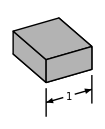
```mathematica
dtHelpBasics3D[]:=
Column[{
Style["3D",Gray,24],
Style["EXAMPLE",Bold,Hue[.55,1,.7],12],
-Graphics-,
"",
Style["STEPS",Bold,Hue[.55,1,.7],12],
Pane["1. Click Box tool.",ImageSize->280],
Row[{Spacer[20],dtPresetBox[],Spacer[10],Show[-Graphics-,ImageSize->100]}],
Pane["2. Choose extrude from the 2Dto3D popup menu.",ImageSize->280],
Row[{Spacer[20],dt3dShape[],Spacer[10],Show[-Graphics-,ImageSize->100],Spacer[10],Show[-Graphics-,ImageSize->100]}],
Pane["3. Insert 3D library object and set to axoDimensionArrow.",ImageSize->280],
Row[{Spacer[20],Button[Style[Graphics[axoRotationArrow[]],Magnification->.25],Null,$dtButtonStyle],Spacer[20],Show[-Graphics-,ImageSize->80],Spacer[20],Show[-Graphics-,ImageSize->140]}],
Pane["4. Click green orientation arrow then drag left. Click blue orientation arrow then drag down.",ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->140],Spacer[10],Show[-Graphics-,ImageSize->140]}],
,
Pane["5. Click Options and set length to 0.4 and break to 0.05.",ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->140],Show[-Graphics-,ImageSize->140]}],
Row[{Spacer[20],Show[-Graphics-,ImageSize->100]}],
Pane["6. Click Text tool and drag to line break.",ImageSize->280],
Row[{Spacer[20],Button[$dtIconText,Null,$dtButtonStyle],Spacer[10],Show[-Graphics-,ImageSize->100]}],
Pane["7. Enter 1 into text field at top.",ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->100],Spacer[10],Show[-Graphics-,ImageSize->100]}]
}]
```

#### basics - draw

```mathematica
dtHelpBasicsDraw[]:=
Column[{
Style["Draw",Gray,24],
Style["EXAMPLE",Bold,Hue[.55,1,.7],12],
-Graphics-,
Style["STEPS",Bold,Hue[.55,1,.7],12],
Pane["1. Click Draw tool and click various canvas locations.",ImageSize->280],
Row[{Spacer[20],Button[$dtIconAddPoint,Null,$dtButtonStyle],Spacer[10],Show[-Graphics-,ImageSize->100]}],
Pane[
"2. Click Insert|Delete tool and click a line to split.",
ImageSize->280],
Row[{Spacer[20],Button[$dtIconSplitPoint,Null,$dtButtonStyle],Spacer[10],Show[-Graphics-,ImageSize->100]}],
Pane[
"3. Click Move Point tool and drag point to new location.",
ImageSize->280],
Row[{Spacer[20],Button[$dtIconMovePoint,Null,$dtButtonStyle],Spacer[10],Show[-Graphics-,ImageSize->100]}],
Pane[
"4. Change shape from Polygon to BSplineFilledCurve.",
ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->80],Spacer[5],Show[-Graphics-,ImageSize->80],Spacer[5],Show[-Graphics-,ImageSize->100]}]
}]
```

#### basics - draw bezier

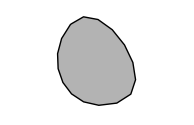
```mathematica
dtHelpBasicsDrawBezier[]:=
Column[{
Style["BezierCurve",Gray,24,LineSpacing->{0,26}],
Style["EXAMPLE",Bold,Hue[.55,1,.7],12],
-Graphics-,
Style["STEPS",Bold,Hue[.55,1,.7],12],
Pane["1. Click Draw tool and select BezierCurve, BezierCurveArrow or BezierFilledCurve from object popup menu.",ImageSize->280],
Row[{Spacer[20],Button[$dtIconAddPoint,Null,$dtButtonStyle],Spacer[10],Show[-Graphics-,ImageSize->80]}],

Pane[
"2. Drag on canvas to create the first point and its handle.",
ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->100]}],
Pane[
"3. Drag at second location to create another point and its handles.",
ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->100]}],
Pane[
"4. Drag starting at the first point to close the shape. The shape can be left open by not dragging on the first point.",
ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->100]}],
Pane["5. Click Selection tool to stop drawing.",ImageSize->280],
Row[{Spacer[20],Button[$dtIconObjectSelect,Null,$dtButtonStyle]}],
Pane[
"5. Click Split Point or Move Point tool and drag points or handles to adjust shape. Open shapes can be closed by moving the last point on top of the first point. Command-drag a handle for corner point.",
ImageSize->280],
Row[{Spacer[20],Button[$dtIconSplitPoint,Null,$dtButtonStyle],Button[$dtIconMovePoint,Null,$dtButtonStyle]}]
}]
```

#### basics - circuit 1

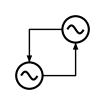
```mathematica
dtHelpBasicsCircuit1[]:=
Column[{
Style["Circuit 1",Gray,24],
Style["EXAMPLE",Bold,Hue[.55,1,.7],12],
-Graphics-,
"",
Style["STEPS",Bold,Hue[.55,1,.7],12],
Pane[
"1. Click Insert Circuit Library Object and set to acSource.",ImageSize->280],
Row[{Spacer[20],Button[Style[Graphics[acSource[]],Magnification->.25],Null,$dtButtonStyle],Spacer[20],Show[-Graphics-,ImageSize->150]}],
Pane[
"2. Click duplicate and drag to above right.",
ImageSize->280],
Row[{Spacer[20],Button[$dtIconObjectDupe,Null,$dtButtonStyle],Spacer[20],-Graphics-}],
Pane[
"3. Click first object. Click Link Chain tool then click second object.",
ImageSize->280],
Row[{Spacer[20],Button[$dtIconLinkChain,Null,$dtButtonStyle],Spacer[20],-Graphics-}],
Pane[
"4. Click first object.",
ImageSize->280],
Row[{Spacer[20],-Graphics-}],
Pane[
"5. Click Select tool then click each link and set Form to Corner.",
ImageSize->280],
Row[{Spacer[20],Button[$dtIconObjectSelect,Null,$dtButtonStyle],Spacer[10],Show[-Graphics-,ImageSize->150],Spacer[10],-Graphics-,-Graphics-}]
}]
```

#### basics - circuit 2

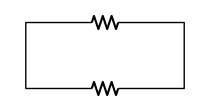
```mathematica
dtHelpBasicsCircuit2[]:=
Column[{
Style["Circuit 2",Gray,24],
Style["EXAMPLE",Bold,Hue[.55,1,.7],12],
-Graphics-,
"",
Style["STEPS",Bold,Hue[.55,1,.7],12],
Pane[
"1. Click Insert Circuit Library Object and set to resistor.",ImageSize->280],
Row[{Spacer[20],Button[Style[Graphics[acSource[]],Magnification->.25],Null,$dtButtonStyle],Spacer[20],
Show[-Graphics-,ImageSize->100],Spacer[20],Show[-Graphics-,ImageSize->50]
}],
Pane[
"2. Click duplicate and drag above.",ImageSize->280],
Row[{Spacer[20],Button[$dtIconObjectDupe,Null,$dtButtonStyle],Spacer[20],
Show[-Graphics-,ImageSize->100]
}],
Pane[
"3. Click resistor Options and rotate 180°.",ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->140]
}],
Row[{Spacer[20],Show[-Graphics-,ImageSize->200]
}],
Pane[
"4. Click Link Chain tool and click first object.",ImageSize->280],
Row[{Spacer[20],Button[$dtIconLinkChain,Null,$dtButtonStyle],Spacer[20],-Graphics-}],
Pane[
"5. Click second object.",ImageSize->280],
Row[{Spacer[20],Button[$dtIconLinkChain,Null,$dtButtonStyle],Spacer[20],-Graphics-}],
Pane[
"6. Click Selection tool then select each link and set Form to Corner.",ImageSize->280],
Row[{Spacer[20],Button[$dtIconObjectSelect,Null,$dtButtonStyle],Spacer[10],Show[-Graphics-,ImageSize->150]}],
Row[{Spacer[20],Show[-Graphics-,ImageSize->100],Spacer[20],Show[-Graphics-,ImageSize->140]}],
Pane[
"7. Click Remove Arrowheads From All.",ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->80],Spacer[20],Show[-Graphics-,ImageSize->140]}]
}]
```

#### basics - flowchart 1

```mathematica
dtHelpBasicsFlowchart1[]:=
Column[{
Style["Flowchart 1",Gray,24],
Style["EXAMPLE",Bold,Hue[.55,1,.7],12],
-Graphics-,
"",
Style["STEPS",Bold,Hue[.55,1,.7],12],
Pane["1. Click Multi-shape Array tool.",ImageSize->280],
Row[{Spacer[20],Button[$dtIconMultiShapeArray,Null,$dtButtonStyle]}],
Pane["2. Enter {1,1}, press Tab key then click Create Shapes.",ImageSize->280],
Row[{Spacer[20],-Graphics-}],
Row[{Spacer[20],Show[-Graphics-,ImageSize->140]}],
Pane["3. Click Insert Object Number to auto-label boxes.",ImageSize->280],
Row[{Spacer[20],Button[$dtIconTextInsertNumbers,Null,$dtButtonStyle],Spacer[10],Show[-Graphics-,ImageSize->140]}],
Pane["4. Select box 1, click Link Chain tool then click box 2.",ImageSize->280],
Row[{Spacer[20],Button[$dtIconLinkChain,Null,$dtButtonStyle],Spacer[10],Show[-Graphics-,ImageSize->140]}],
Pane["5. Click Selection tool, select box 1 then enter text for shape.",ImageSize->280],
Row[{Spacer[20],Button[$dtIconObjectSelect,Null,$dtButtonStyle],Spacer[10],Show[-Graphics-,ImageSize->140],Spacer[10],Show[-Graphics-,ImageSize->140]
}]
}]
```

#### basics - flowchart 2

```mathematica
dtHelpBasicsFlowchart2[]:=
Column[{
Style["Flowchart 2",Gray,24],
Style["EXAMPLE",Bold,Hue[.55,1,.7],12],
-Graphics-,
"",
Style["STEPS",Bold,Hue[.55,1,.7],12],
Pane["1. Start with Basics: Flowchart 1.",ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->140]}],
Pane["2. With first box selected, click the Disk shape then click Replace.",ImageSize->280],
Row[{Spacer[20],dtPresetDisk[],Spacer[10],Show[-Graphics-,ImageSize->140],Spacer[10],Show[-Graphics-,ImageSize->140]}],
Pane["3. Select link and click Fix Link.",ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->140],Spacer[10],Button[$dtIconLinkFix,Null,$dtButtonStyle],Spacer[10],Show[-Graphics-,ImageSize->140]}]
}]
```

#### basics - libraries

```mathematica
dtHelpBasicsLibraries[]:=
Column[{
Style["Libraries",Gray,24],
Style["PREVIEW",Bold,Hue[.55,1,.7],12],
dtHelpLibraries[],
"",
Style["EXAMPLE",Bold,Hue[.55,1,.7],12],
-Graphics-,
"",
Style["STEPS",Bold,Hue[.55,1,.7],12],
Style[Pane["1. Click a library button to insert a library object.\nThe button image displays the current library object.\nThe middle button was clicked for this example.",ImageSize->280],LineIndent->0],
Row[{Spacer[20],-Graphics-,Spacer[10],Show[-Graphics-,ImageSize->70]}],
Pane["2. Select a new object from the LIBRARY popup menu.",ImageSize->280],
Row[{Spacer[20],-Graphics-,Spacer[10],-Graphics-}],
Pane["3. Modify with the Style|Options button.",ImageSize->280],
Row[{Spacer[20],-Graphics-}],
Row[{Spacer[20],Show[-Graphics-,ImageSize->300]}],
Row[{Spacer[20],-Graphics-}],
""
}]
```

#### basics - link 1

```mathematica
dtHelpBasicsLink1[]:=
Column[{
Style["Link 1",Gray,24],
Style["EXAMPLE",Bold,Hue[.55,1,.7],12],
-Graphics-,
"",
Style["STEPS",Bold,Hue[.55,1,.7],12],
Pane[
"1. Start with Basics: Flowchart 1.\n2. Click link to select.",
ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->150]}],
Pane[
"3. Change Form to Corner and Direction to Vertical.",
ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->140],Show[-Graphics-,ImageSize->140]}],
Pane[
"4. Click Move Point tool and move link corner point down.",
ImageSize->280],
Row[{Spacer[20],Button[$dtIconMovePoint,Null,$dtButtonStyle],Spacer[20],Show[-Graphics-,ImageSize->140]}]
}]
```

#### basics - link 2

```mathematica
dtHelpBasicsLink2[]:=
Column[{
Style["Link 2",Gray,24],
Style["EXAMPLE",Bold,Hue[.55,1,.7],12],
-Graphics-,
"",
Style["STEPS",Bold,Hue[.55,1,.7],12],
Pane["1. Start with Basics: Link 1.",ImageSize->280],
Pane["2. Click Move Point tool and move link end point to right side of box 2.",ImageSize->280],
Row[{Spacer[20],Button[$dtIconMovePoint,Null,$dtButtonStyle],Spacer[10],Show[-Graphics-,ImageSize->140],Show[-Graphics-,ImageSize->140]}],
Pane["3. Move link corner point to right.",ImageSize->280],
Row[{Spacer[20],Show[-Graphics-,ImageSize->140]}]
}]
```

#### basics - move2d

```mathematica
dtHelpBasicsMove2d[]:=
Column[{
Style["2D POSITION",Bold,Hue[.55,1,.7],12],
Style[Pane[
"Select 2D objects and drag or use the directional button to move a grid unit.",
ImageSize->280],LineIndent->0],
Row[{Spacer[20],dtMoveDirection[]}],
"",
Style["2D ROTATION",Bold,Hue[.55,1,.7],12],
Style[Pane[
"Select 2D objects and click rotate tool.",
ImageSize->280],LineIndent->0],
Row[{Button[$dtIconRotate,Null,$dtButtonStyle],Spacer[20],Show[-Graphics-,ImageSize->150]}]
},Alignment->{Left,Center}]
```

#### basics - move3d

```mathematica
dtHelpBasicsMove3d[]:=
Column[{
Style["3D POSITION | ROTATION",Bold,Hue[.55,1,.7],12],
Style[Pane[
"There are four ways to position/rotate a 3D object.\n1. Click an orientation vector or rotation ring of the selected object then drag within the canvas. Dragging the vector or ring will not move the object.",
ImageSize->280],LineIndent->0],
Row[{Spacer[20],Show[-Graphics-,ImageSize->100]}],
Style[Pane[
Row[{"2. Click the x, y or z button then drag within the canvas.\nClick the move ",Graphics[{{Hue[.6,.7,1],Rectangle[{-1.75,-1.75},{1.75,1.75},RoundingRadius->1]},White,Arrowheads[Small],Arrow[{{-1,-1},{1,1}}]},PlotRange->{{-1.75,1.75},{-1.75,1.75}},ImagePadding->0,ImageSize->{15,15}]," | rotate ",Graphics[{{Hue[.6,.7,1],Rectangle[{-1.75,-1.75},{1.75,1.75},RoundingRadius->1]},White,Arrowheads[{{Automatic,Automatic,Graphics[Polygon[{{-6,0},{0,0},{-3,-5}}]]}}],Arrow[Table[{Sin[x],Cos[x]},{x,.1Pi,1.9Pi,Pi/20}]]},PlotRange->{{-1.75,1.75},{-1.75,1.75}},ImagePadding->0,ImageSize->{15,15}]," button to toggle action."}],
ImageSize->280],LineIndent->0],
Row[{Spacer[20],Show[-Graphics-,ImageSize->70],Spacer[20],Show[-Graphics-,ImageSize->70]}],
Style[Pane[
"3. Click Style | Options button for x, y and z sliders.",
ImageSize->280],LineIndent->0],
Row[{Spacer[20],Button[Style["Options",10],Null,ImageSize->{99,33},$dtButtonStyle],
Spacer[10],Button[Style["Style | Options",10],Null,ImageSize->{99,33},$dtButtonStyle]}],
Style[Pane[
"4. Use the 3D directional button to move a grid unit.",
ImageSize->280],LineIndent->0],
Row[{Spacer[20],dtMoveDirection3d[]}],
"",
Style[Pane[
"Note: The black dot represents the object center\nprojected onto the xy plane.",
ImageSize->280],LineIndent->0,Italic],
Row[{Spacer[20],Show[-Graphics-,ImageSize->100]}]
},Alignment->{Left,Center}]
```

#### basics - preferences

```mathematica
dtHelpBasicsPreferences[]:=
Column[{
Style["Preferences",Gray,24],"",
Style[Pane[
"The following visibility and transformation settings can be set within the preferences dialog:",
ImageSize->280],LineIndent->0],
Spacer[{0,2}],
Show[-Graphics-,ImageSize->220],
Spacer[{0,2}],
Style[Pane[
"Set the transformation center by clicking the grid boxes or click Object and choose {0,0} from popupmenu for middle of canvas.",
ImageSize->280],LineIndent->0]
}]
```

#### basics - style

```mathematica
dtHelpBasicsStyle[]:=
Column[{
Style["Style",Gray,24],"",
Style[Pane[
"The Style preset menu and button are located at the top of the window.",
ImageSize->280],LineIndent->0],
Show[-Graphics-,ImageSize->254],
"",
Style[Pane[
"The color palette is an alternative way to change the edge or fill color of a shape. Click on the edge or fill icon at left then click a color at right to change.",
ImageSize->280],LineIndent->0],
Show[-Graphics-,ImageSize->100]
}]
```

#### example - files

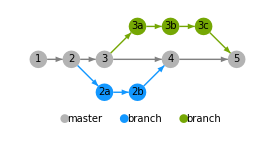
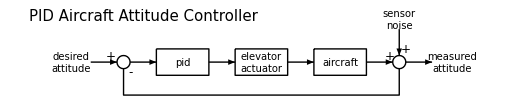
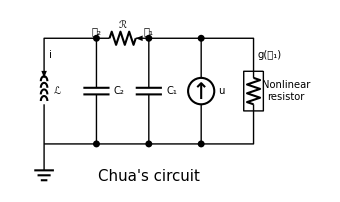
```mathematica
dtHelpExampleFiles[]:=
Column[
{
Style["Examples",Gray,24],"",
Row[{-Graphics-,Spacer[50],Show[-Graphics-,ImageSize->{Automatic,150}]}],Spacer[{0,40}],
-Graphics-,Spacer[{0,40}],
-Graphics-
}]
```

#### example - spirograph

```mathematica
dtHelpExampleSpirograph[]:=
Column[
{
Style["Gear spirograph",Gray,24],
"",
"Command-click gear shape for presets.",
Show[-Graphics-,ImageSize->180],Show[-Graphics-,ImageSize->180]
},Spacings->0,Background->None]
```

#### example - cobblestone

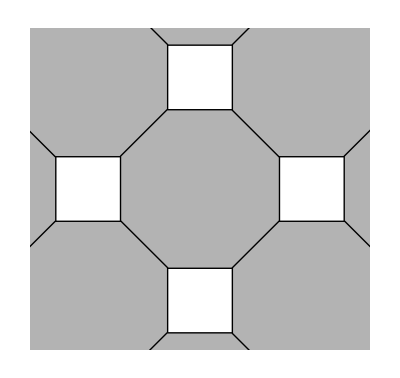
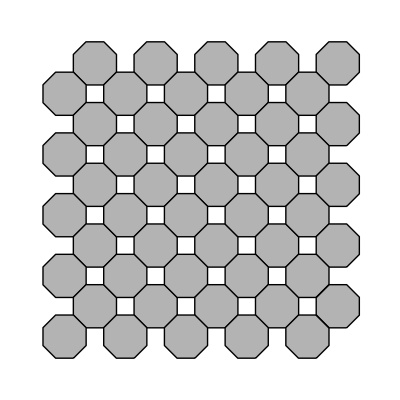
```mathematica
dtHelpExampleCobblestone[]:=
Column[
{
Style["Cobblestone",Gray,24],"",
Row[{Button[Show[$dtIconMultiShapeArray,ImageSize->23],Null,$dtButtonStyle],Pane[" Click Multi-Shape Array tool.\n Click 5x10 button.",ImageSize->200]}],
"",
Row[{Button[Show[-Graphics-,ImageSize->23],Null,$dtButtonStyle],Pane[" Click tile button.\n Click Create Shapes.",ImageSize->200]}],
"",
Show[-Graphics-,ImageSize->100],
"",
Row[{Button[Show[$dtIconGrid,ImageSize->23],Null,$dtButtonStyle],Pane[" Set grid size to 0.1.",ImageSize->200]}],
"",
Row[{Button[Show[$dtIconSnapPts,ImageSize->23],Null,$dtButtonStyle],Pane[" Click snap points to grid tool.",ImageSize->200]}],
"",
Pane["Set objects to BSplineFilledCurve.",ImageSize->280],
"",
Show[-Graphics-,ImageSize->200]
},Spacings->0]
```

#### example - cracker

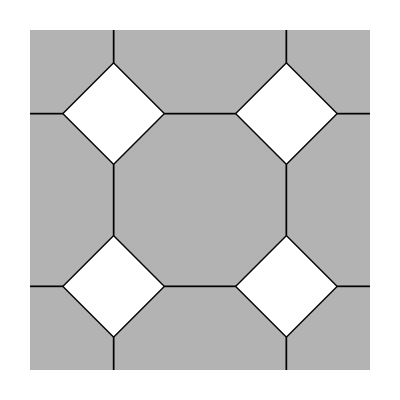
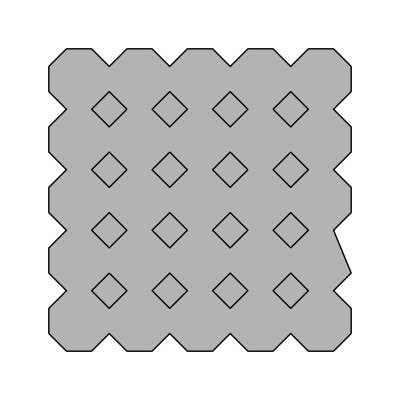
```mathematica
dtHelpExampleCracker[]:=
Column[
{
Style["Cracker",Gray,24],"",
Row[{Button[Show[$dtIconMultiShapeArray,ImageSize->23],Null,$dtButtonStyle],Pane[" Click Multi-Shape Array tool.\n Click 5x5 button.",ImageSize->200]}],
"",
Row[{Button[Show[-Graphics-,ImageSize->23],Null,$dtButtonStyle],Pane[" Click tile button.\n Click Create Shapes.",ImageSize->200]}],
"",
Row[{Button[$dtIconCombineShapes,Null,$dtButtonStyle],Pane[" Click Combine tool.",ImageSize->200]}],
"",
Show[-Graphics-,ImageSize->100],
"",
Pane["Select all shapes and set to BSplineFilledCurve.",ImageSize->280],
Pane["Select inner shapes and set fill color to white.",ImageSize->280],
Show[-Graphics-,ImageSize->200]
},Spacings->0]
```

#### example - weave

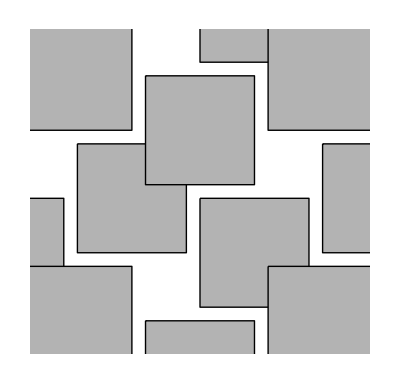
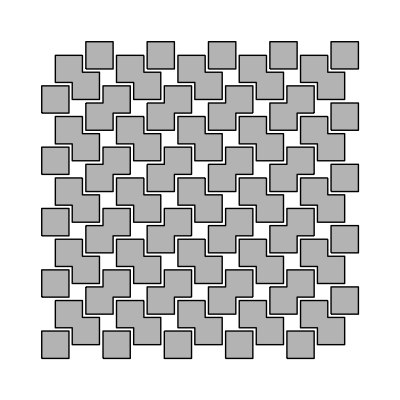
```mathematica
dtHelpExampleWeave[]:=
Column[
{
Style["Weave",Gray,24],"",
Row[{Button[Show[$dtIconMultiShapeArray,ImageSize->23],Null,$dtButtonStyle],Pane[" Click Multi-Shape Array tool.\n Click 10x10 button.",ImageSize->200]}],
"",
Row[{Button[Show[-Graphics-,ImageSize->23],Null,$dtButtonStyle],Pane[" Click tile button.\n Click Create Shapes.",ImageSize->200]}],
"",
Row[{Button[$dtIconCombineShapes,Null,$dtButtonStyle],Pane[" Click Combine tool.",ImageSize->200]}],
"",
Show[-Graphics-,ImageSize->200],

"",
Pane["Want a peanut texture instead?\nSet object to BSplineFilledCurve.",ImageSize->280],
"",
Show[-Graphics-,ImageSize->200]
},Spacings->0]
```

#### example - floor tile

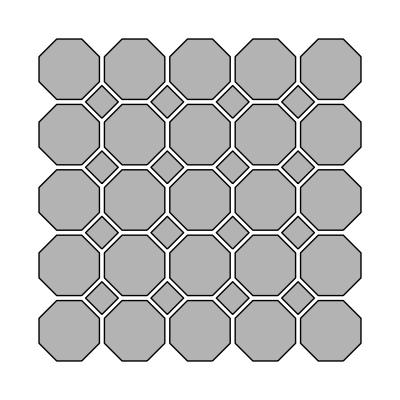
```mathematica
dtHelpExampleFloorTile[]:=
Column[
{
Style["Floor tile",Gray,24],"",
Row[{Button[Show[$dtIconMultiShapeArray,ImageSize->23],Null,$dtButtonStyle],Pane[" Click Multi-Shape Array tool.\n Click 5x5 button.",ImageSize->200]}],
"",
Row[{Button[Show[-Graphics-,ImageSize->23],Null,$dtButtonStyle],Pane[" Click tile button.\n Set space h and v to 0.\n Click Create Shapes.",ImageSize->200]}],
"",
Row[{Button[Show[$dtIconMultiShapeArray,ImageSize->23],Null,$dtButtonStyle],Pane[" Click Multi-Shape Array tool.\n Enter {4,4,4,4} and press Tab key.\n Set width, height, space h and v to 0.2.\n Set sides to 4.\n Set rotate to 0.\n Click Create Shapes.",ImageSize->200]}],
"",
Show[-Graphics-,ImageSize->200]
},Spacings->0]
```

#### example - intricate

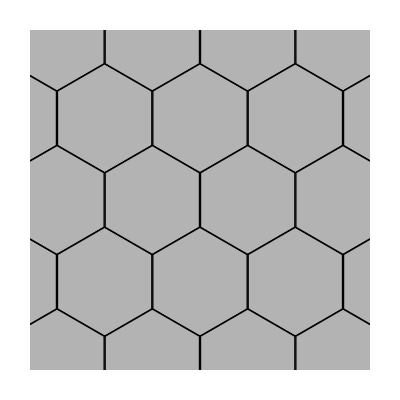
```mathematica
dtHelpExampleIntricate[]:=
Column[
{
Style["Intricate",Gray,24],"",
Row[{Button[Dynamic@Graphics[{Gray,Cases[gear["Size"->1,"Teeth"->6,"ToothHeight"->1,"ToothWidth"->.3696,"ToothCurveMidPoint"->.5,"ToothCurve"->0,"ToothPeakSize"->0,"ToothBaseSize"->.25],_FilledCurve,Infinity][[1]]},ImageSize->{24,24},PlotRangePadding->None],Null,$dtButtonStyle],Pane[" Click Geometric Array tool.\n Click 5x10 button.",ImageSize->200]}],
"",
Row[{Button[Graphics[Flatten[{Opacity[0], EdgeForm[{Black}],
Disk[],Style[Rectangle[{0,0},{2,2}],Antialiasing->True]}],
ImageSize->{18,18}],Null,$dtButtonStyle],Pane[" Set shape style to outline.",ImageSize->200]}],
"",
Row[{Button[Show[-Graphics-,ImageSize->23],Null,$dtButtonStyle],Pane[" Set shape (last preset button).",ImageSize->200]}],
"",
Row[{Button[Show[-Graphics-,ImageSize->23],Null,$dtButtonStyle],Pane[" Set layout.\n Set space v to 0.1.\n Click Create Shapes.",ImageSize->200]}],
"",
Show[-Graphics-,ImageSize->200]
},Spacings->0]
```

#### example - blend (not used)

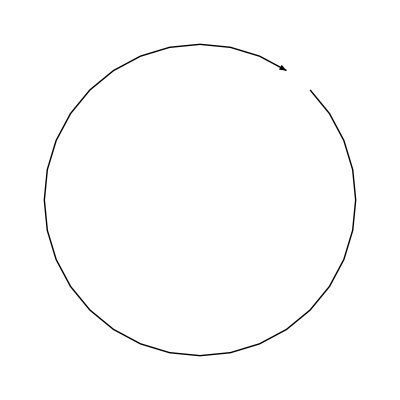
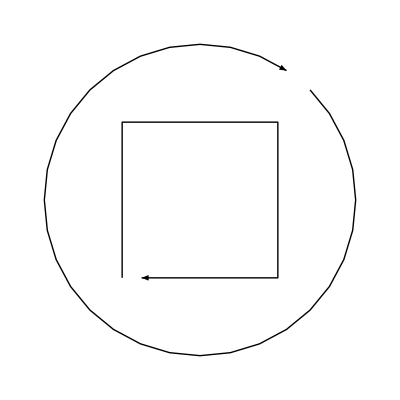
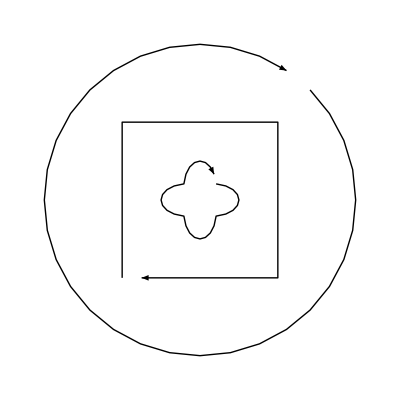
```mathematica
dtHelpExampleBlend[]:=
Column[
{
Style["Blend",Gray,24],"",
Row[{Button[Graphics[{Gray,Disk[]},ImageSize->18],Null,$dtButtonStyle],Pane[" Set object to Arrow.\n Set disk shape resolution to 32.\n Click disk shape to insert.\n Enlarge to fit {-1,-1} to {1,1}.\n Rotate -45°.",ImageSize->200]}],
Show[-Graphics-,ImageSize->100],
"",
Row[{Button[Graphics[{Gray,Rectangle[{0,0},{1,.5}]},ImageSize->18],Null,$dtButtonStyle],Pane[" Set box shape size to 1 x 1.\n Click box shape to insert.\n Rotate 180°.\n Increase points 3 times for 32 points.",ImageSize->200]}],
Show[-Graphics-,ImageSize->100],
"",
Row[{Button[$dtIconBlendShapes,Null,$dtButtonStyle],Pane[" Click Blend tool and set to 1.",ImageSize->200]}],
Show[-Graphics-,ImageSize->100],
"",
Pane["Delete box and disk.\nSet blended object to BSplineFilledCurve.",ImageSize->280],
Show[-Graphics-,ImageSize->200]
},Spacings->0]
```

#### example - combine (not used)

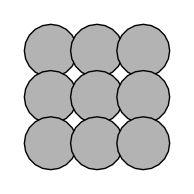
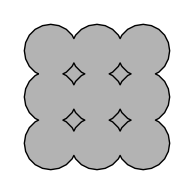
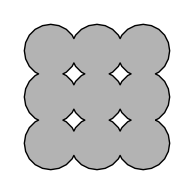
```mathematica
dtHelpExampleCombine[]:=
Column[
{
Style["Combine",Gray,24],"",
Row[{Button[Show[$dtIconShapeArray,ImageSize->23],Null,$dtButtonStyle],Pane[" Click Shape Array tool.\n Click 3x3 button.\n Choose disk shape.\n Set height and width to 0.4.\n Set space h and v to -0.05.\n Click Create Shapes.",ImageSize->200]}],"",
Show[-Graphics-,ImageSize->100],
"",
Row[{Button[$dtIconCombineShapes,Null,$dtButtonStyle],Pane[" Click Combine tool.",ImageSize->200]}],
Show[-Graphics-,ImageSize->100],
"",
Pane["Select inner shapes and set color to white.",ImageSize->280],
Show[-Graphics-,ImageSize->200]
},Spacings->0]
```

#### example - combine2 (not used)

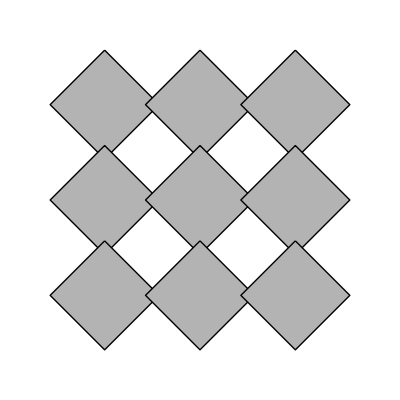
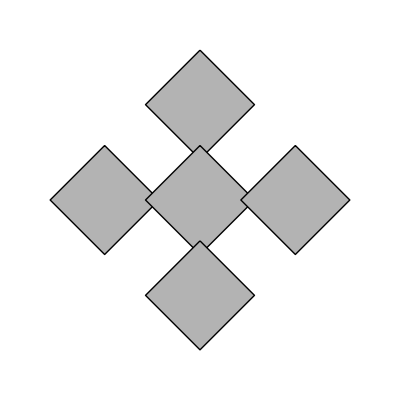
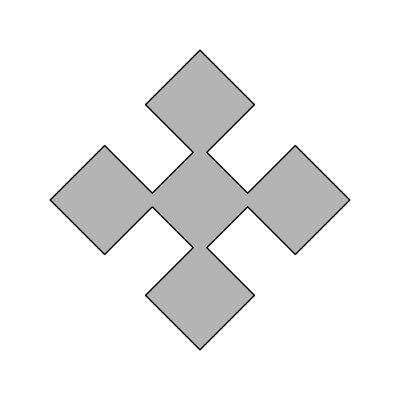
```mathematica
dtHelpExampleCombine2[]:=
Column[
{
Style["Combine 2",Gray,24],"",
Row[{Button[Show[$dtIconShapeArray,ImageSize->23],Null,$dtButtonStyle],Pane[" Click Shape Array tool.\n Click 3x3 button.\n Choose diamond shape.\n Set height and width to 0.4.\n Set space h and v to -0.05.\n Click Create Shapes.",ImageSize->200]}],"",
Show[-Graphics-,ImageSize->100],
"",
Pane["Select and delete corner shapes.",ImageSize->280],
Show[-Graphics-,ImageSize->100],
"",
Row[{Button[$dtIconCombineShapes,Null,$dtButtonStyle],Pane[" Select all shapes.\n Click Combine tool.",ImageSize->200]}],
Show[-Graphics-,ImageSize->100],
"",
Pane["Set object to BSplineFilledCurve.",ImageSize->280],
Show[-Graphics-,ImageSize->200]
},Spacings->0]
```

### buttons

#### 3d set move axis direction

```mathematica
dtButton3dSetMoveAxisDirection[]:=
Tooltip[Dynamic@SetterBar[Dynamic@$dt3dMoveAxis,{"x"->Style["x",Bold,$dt3dAxisXColor],"y"->Style["y",Bold,$dt3dAxisYColor],"z"->Style["z",Bold,$dt3dAxisZColor]}],"Set axis direction to move"]
```

#### 3d toggle rotate / move

```mathematica
dtButton3dToggleRotateMove[]:=
DynamicModule[{box={Hue[.6,.7,1],Rectangle[{-1.75,-1.75},{1.75,1.75},RoundingRadius->1]}},
Tooltip[Dynamic@Button[If[$dt3dRotate===True,Graphics[{box,White,Arrowheads[{{Automatic,Automatic,Graphics[Polygon[{{-6,0},{0,0},{-3,-5}}]]}}],Arrow[Table[{Sin[x],Cos[x]},{x,.1Pi,1.9Pi,Pi/20}]]},PlotRange->{{-1.75,1.75},{-1.75,1.75}},ImagePadding->0],Graphics[{box,White,Arrowheads[Small],Arrow[{{-1,-1},{1,1}}]},PlotRange->{{-1.75,1.75},{-1.75,1.75}},ImagePadding->0]],$dt3dRotate=If[$dt3dRotate===True,False,True],ImageSize->{21,21},Appearance->"Frameless"],"Toggle between 3D rotate and move"]
]
```

#### 3d rotate origin

```mathematica
dtButton3dRotateOrigin[]:=
DynamicModule[{box={Hue[.6,.7,1],Rectangle[{-1.75,-1.75},{1.75,1.75},RoundingRadius->1]}},
Tooltip[Dynamic@Button[Dynamic@If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]===True,
Graphics[{box,White,Circle[],Disk[{0,0},.3]},PlotRange->{{-1.75,1.75},{-1.75,1.75}},ImagePadding->0],
Graphics[{box,White,Style[Line[{{0,-1},{0,1}}],Antialiasing->False],Style[Line[{{-1,0},{1,0}}],Antialiasing->False],EdgeForm[{Thick,Hue[.6,.7,1]}],Disk[{-.1,.1},.5]},PlotRange->{{-1.75,1.75},{-1.75,1.75}},ImagePadding->0]],$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]=If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]===True,False,True],ImageSize->{21,21},Appearance->"Frameless"],Dynamic@If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]===True,"Global origin","Local origin"]]
]
```

#### 3d tools

```mathematica
dtButton3dTools[]:=
{
DynamicModule[{tilt,turn},
Tooltip[Button[$dtIcon3dView,
dtSetUndo[];
CreateDialog[Pane[Column[{
tilt=$tilt;turn=$turn;
Row@{Pane["tilt ",40,Alignment->Right],Slider[Dynamic@tilt,{1,89,1}]," ",Pane[Dynamic@tilt,40]},
Row@{Pane["turn ",40,Alignment->Right],Slider[Dynamic@turn,{1,89,1}]," ",Pane[Dynamic@turn,40]},
Dynamic@Graphics[{White,EdgeForm[{JoinForm["Round"],Black}],axoExtrude[Polygon[{{-1,-1},{1,-1},{1,1},{-1,1}}],"AxisRotation"->{{0,"Right"}},"Tilt"->tilt,"Turn"->turn,"Extrude"->2]},ImageSize->100,PlotRange->{{-2.3,1.3},{-1.5,2.5}}],
Row@{Button["30-30",tilt=30;turn=30],
Button["isometric",tilt=35.264;turn=45],
Button["30-60",tilt=30;turn=60]},
Row@{Button["Cancel",DialogReturn[]],
Button["Apply",$tilt=tilt;$turn=turn;$dtXAngle=axo[Null,"Tilt"->$tilt,"Turn"->$turn,"Angles"->True][[1]];$dtYAngle=axo[Null,"Tilt"->$tilt,"Turn"->$turn,"Angles"->True][[2]];],
DefaultButton[$tilt=tilt;$turn=turn;DialogReturn[]]}
},Alignment->Center],ImageSize->300],WindowTitle->"3D view",Modal->True],
$dtButtonStyle],"3D view"]],

dt3dShape[]
}

dt3dShape[]:=
DynamicModule[{check=False,menuIconSize={24,24},pts},
Tooltip[Dynamic@ActionMenu[$dtIcon3dShape,
{
Dynamic@Graphics[{Opacity[$dtStyle[[$dtPn]][[3]]],
$dtStyle[[$dtPn]][[2]],
EdgeForm[{CapForm["Butt"],$dtStyle[[$dtPn]][[4]],Opacity[$dtStyle[[$dtPn]][[5]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[$dtStyle[[$dtPn]][[7]]]}],Polygon[Table[.5{Sin[x],Cos[x]},{x,0,2Pi-2Pi/10,2Pi/10}]],GrayLevel[0,1],Text[Style["2D",8,LineSpacing->{0,7}],{0,-.05}]},ImageSize->menuIconSize]:>If[MemberQ[Join[$dtShapeSymbols/.{"CompoundPath"->Nothing},{axo,axoExtrude}],$dtStyle[[$dtPn]][[1]]],
dtSetUndo[];
$dtMode="layer";
$dtStyle[[$dtPn]][[1]]=Switch[$dtAxoSymbols[[$dtPn]],Point|Line|Arrow|Polygon|BezierCurve|"BezierFilledCurve"|BSplineCurve|"BSplineFilledCurve"|"Markers",$dtAxoSymbols[[$dtPn]],_,Polygon];
$dtObjOpt[[$dtPn]]={},
MessageDialog["Not able to convert objects to shape."]
],
Dynamic@Graphics[{Opacity[$dtStyle[[$dtPn]][[3]]],
$dtStyle[[$dtPn]][[2]],
EdgeForm[{CapForm["Butt"],$dtStyle[[$dtPn]][[4]],Opacity[$dtStyle[[$dtPn]][[5]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[$dtStyle[[$dtPn]][[7]]]}],axo[Polygon[Table[.5{Sin[x],Cos[x]},{x,0,2Pi-2Pi/10,2Pi/10}]],"Direction"->"Right"]},ImageSize->menuIconSize]:>
(check=False;
dtSetUndo[];
$dtMode="layer";
Table[If[MemberQ[Join[$dtShapeSymbols/.{"CompoundPath"->Nothing},{axo,axoExtrude}],$dtStyle[[n]][[1]]]&&Length@$dtP[[n]]>1,
$dtPn=n;
$dtSelectedLayers={$dtPn};
$dtShow3dGrid=$dtCurrent3dGrid;
$dtAxoSymbols[[$dtPn]]=Switch[$dtStyle[[$dtPn]][[1]],Point|Line|Arrow|Polygon|BezierCurve|"BezierFilledCurve"|BSplineCurve|"BSplineFilledCurve"|"Markers",$dtStyle[[$dtPn]][[1]],_,Polygon];
$dtStyle[[$dtPn]][[1]]=axo;
$dtObjOpt[[$dtPn]]=Options[axo]/.{("Direction"->_)->("Direction"->"Right")};
$dtP[[$dtPn]]=dtCenterPoints[{$dtP[[$dtPn]]}][[1]],
check=True
],{n,$dtSelectedLayers}];
If[check,MessageDialog["Not able to convert one or more objects to 3D."]]),
Dynamic@Graphics[{Opacity[$dtStyle[[$dtPn]][[3]]],
$dtStyle[[$dtPn]][[2]],
EdgeForm[{CapForm["Butt"],$dtStyle[[$dtPn]][[4]],Opacity[$dtStyle[[$dtPn]][[5]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[$dtStyle[[$dtPn]][[7]]]}],axoExtrude[Polygon[Table[.5{Sin[x],Cos[x]},{x,0,2Pi-2Pi/10,2Pi/10}]],"Direction"->"Right"]},ImageSize->menuIconSize]:>
(check=False;
dtSetUndo[];
$dtMode="layer";
Table[If[MemberQ[Join[$dtShapeSymbols/.{"CompoundPath"->Nothing},{axo,axoExtrude}],$dtStyle[[n]][[1]]]&&Length@$dtP[[n]]>1,
$dtPn=n;
$dtSelectedLayers={$dtPn};
$dtShow3dGrid=$dtCurrent3dGrid;
$dtStyle[[$dtPn]][[1]]=axoExtrude;
$dtAxoSymbols[[$dtPn]]=Polygon;
$dtObjOpt[[$dtPn]]=Options[axoExtrude]/.{("Direction"->_)->("Direction"->"Right")};
$dtP[[$dtPn]]=dtCenterPoints[{$dtP[[$dtPn]]}][[1]],
check=True
],{n,$dtSelectedLayers}];
If[check,MessageDialog["Not able to convert one or more objects to 3D."]]),
Dynamic@Graphics[{Opacity[$dtStyle[[$dtPn]][[3]]],
$dtStyle[[$dtPn]][[2]],
EdgeForm[{CapForm["Butt"],$dtStyle[[$dtPn]][[4]],Opacity[$dtStyle[[$dtPn]][[5]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[$dtStyle[[$dtPn]][[7]]]}],axo[Polygon[Table[.5{Sin[x],Cos[x]},{x,0,2Pi-2Pi/10,2Pi/10}]],"Direction"->"Left"]},ImageSize->menuIconSize]:>
(check=False;
dtSetUndo[];
$dtMode="layer";
Table[If[MemberQ[Join[$dtShapeSymbols/.{"CompoundPath"->Nothing},{axo,axoExtrude}],$dtStyle[[n]][[1]]]&&Length@$dtP[[n]]>1,
$dtPn=n;
$dtSelectedLayers={$dtPn};
$dtShow3dGrid=$dtCurrent3dGrid;
$dtAxoSymbols[[$dtPn]]=Switch[$dtStyle[[$dtPn]][[1]],Point|Line|Arrow|Polygon|BezierCurve|"BezierFilledCurve"|BSplineCurve|"BSplineFilledCurve"|"Markers",$dtStyle[[$dtPn]][[1]],_,Polygon];
$dtStyle[[$dtPn]][[1]]=axo;
$dtObjOpt[[$dtPn]]=Options[axo]/.{("Direction"->_)->("Direction"->"Left")};
$dtP[[$dtPn]]=dtCenterPoints[{$dtP[[$dtPn]]}][[1]],
check=True
],{n,$dtSelectedLayers}];
If[check,MessageDialog["Not able to convert one or more objects to 3D."]]),
Dynamic@Graphics[{Opacity[$dtStyle[[$dtPn]][[3]]],
$dtStyle[[$dtPn]][[2]],
EdgeForm[{CapForm["Butt"],$dtStyle[[$dtPn]][[4]],Opacity[$dtStyle[[$dtPn]][[5]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[$dtStyle[[$dtPn]][[7]]]}],axoExtrude[Polygon[Table[.5{Sin[x],Cos[x]},{x,0,2Pi-2Pi/10,2Pi/10}]],"Direction"->"Left"]},ImageSize->menuIconSize]:>
(check=False;
dtSetUndo[];
$dtMode="layer";
Table[If[MemberQ[Join[$dtShapeSymbols/.{"CompoundPath"->Nothing},{axo,axoExtrude}],$dtStyle[[n]][[1]]]&&Length@$dtP[[n]]>1,
$dtPn=n;
$dtSelectedLayers={$dtPn};
$dtShow3dGrid=$dtCurrent3dGrid;
$dtStyle[[$dtPn]][[1]]=axoExtrude;
$dtAxoSymbols[[$dtPn]]=Polygon;
$dtObjOpt[[$dtPn]]=Options[axoExtrude]/.{("Direction"->_)->("Direction"->"Left")};
$dtP[[$dtPn]]=dtCenterPoints[{$dtP[[$dtPn]]}][[1]],
check=True
],{n,$dtSelectedLayers}];
If[check,MessageDialog["Not able to convert one or more objects to 3D."]]),
Dynamic@Graphics[{Opacity[$dtStyle[[$dtPn]][[3]]],
$dtStyle[[$dtPn]][[2]],
EdgeForm[{CapForm["Butt"],$dtStyle[[$dtPn]][[4]],Opacity[$dtStyle[[$dtPn]][[5]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[$dtStyle[[$dtPn]][[7]]]}],axo[Polygon[Table[.5{Sin[x],Cos[x]},{x,0,2Pi-2Pi/10,2Pi/10}]],"Direction"->"Top"]},ImageSize->menuIconSize]:>
(check=False;
dtSetUndo[];
$dtMode="layer";
Table[If[MemberQ[Join[$dtShapeSymbols/.{"CompoundPath"->Nothing},{axo,axoExtrude}],$dtStyle[[n]][[1]]]&&Length@$dtP[[n]]>1,
$dtPn=n;
$dtSelectedLayers={$dtPn};
$dtShow3dGrid=$dtCurrent3dGrid;
$dtAxoSymbols[[$dtPn]]=Switch[$dtStyle[[$dtPn]][[1]],Point|Line|Arrow|Polygon|BezierCurve|"BezierFilledCurve"|BSplineCurve|"BSplineFilledCurve"|"Markers",$dtStyle[[$dtPn]][[1]],_,Polygon];
$dtStyle[[$dtPn]][[1]]=axo;
$dtObjOpt[[$dtPn]]=Options[axo]/.{("Direction"->_)->("Direction"->"Top")};
$dtP[[$dtPn]]=dtCenterPoints[{$dtP[[$dtPn]]}][[1]],
check=True
],{n,$dtSelectedLayers}];
If[check,MessageDialog["Not able to convert one or more objects to 3D."]]),
Dynamic@Graphics[{Opacity[$dtStyle[[$dtPn]][[3]]],
$dtStyle[[$dtPn]][[2]],
EdgeForm[{CapForm["Butt"],$dtStyle[[$dtPn]][[4]],Opacity[$dtStyle[[$dtPn]][[5]]],AbsoluteThickness[$dtStyle[[$dtPn]][[6]]],AbsoluteDashing[$dtStyle[[$dtPn]][[7]]]}],axoExtrude[Polygon[Table[.5{Sin[x],Cos[x]},{x,0,2Pi-2Pi/10,2Pi/10}]],"Direction"->"Top"]},ImageSize->menuIconSize]:>
(check=False;
dtSetUndo[];
$dtMode="layer";
Table[If[MemberQ[Join[$dtShapeSymbols/.{"CompoundPath"->Nothing},{axo,axoExtrude}],$dtStyle[[n]][[1]]]&&Length@$dtP[[n]]>1,
$dtPn=n;
$dtSelectedLayers={$dtPn};
$dtShow3dGrid=$dtCurrent3dGrid;
$dtStyle[[$dtPn]][[1]]=axoExtrude;
$dtAxoSymbols[[$dtPn]]=Polygon;
$dtObjOpt[[$dtPn]]=Options[axoExtrude]/.{("Direction"->_)->("Direction"->"Top")};
$dtP[[$dtPn]]=dtCenterPoints[{$dtP[[$dtPn]]}][[1]],
check=True
],{n,$dtSelectedLayers}];
If[check,MessageDialog["Not able to convert one or more objects to 3D."]])
},Enabled->If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[$dtPn]][[1]]]&&Length@$dtP[[$dtPn]]>1,True,False],BaselinePosition->Scaled[.4],ImageSize->{66,33},$dtButtonStyle],Dynamic@If[$dtP[[$dtPn]]==={},"Add shape before using this tool.","2D/3D conversion"]]
]
```

#### align tools

```mathematica
Options[dtButtonAlignTools]={"EditProfileShape"->False};

dtButtonAlignTools[OptionsPattern[]]:=
Block[{editPS=OptionValue["EditProfileShape"]},
{

If[!editPS,Tooltip[Button[$dtIconAlignLeft,
dtAlign["Alignment"->"Left"],$dtButtonStyle],
"Align left of selected objects."],Null],

If[!editPS,Tooltip[Button[$dtIconAlignRight,
dtAlign["Alignment"->"Right"],$dtButtonStyle],
"Align right of selected objects."],Null],

If[!editPS,Tooltip[Button[$dtIconAlignVertical,
dtAlign["Alignment"->"Vertical"],$dtButtonStyle],
"Align selected objects vertically."],Null],

If[!editPS,Tooltip[Button[$dtIconAlignBottom,
dtAlign["Alignment"->"Bottom"],$dtButtonStyle],
"Align bottom of selected objects."],Null],

If[!editPS,Tooltip[Button[$dtIconAlignTop,
dtAlign["Alignment"->"Top"],$dtButtonStyle],
"Align top of selected objects."],Null],

If[!editPS,Tooltip[Button[$dtIconAlignHorizontal,
dtAlign["Alignment"->"Horizontal"],$dtButtonStyle],
"Align selected objects horizontally."],Null],

Tooltip[Button[Rotate[$dtIconAlignToGrid,Pi],
CreateDialog[Pane[Grid[{
{Row@{Button[Rotate[Graphics[{Gray,Polygon[{{.25,.2},{.75,.2},{.75,.7},{.25,.7}}],Black,Line[{{0,.1},{1,.1}}]
},ImageSize->18],-Pi/2],dtAlignShapeToGrid["Left"]],
Button[Rotate[Graphics[{Gray,Polygon[{{.25,.2},{.75,.2},{.75,.7},{.25,.7}}],Black,Line[{{0,.1},{1,.1}}]
},ImageSize->18],Pi/2],dtAlignShapeToGrid["Right"]],
Button[Rotate[Graphics[{Gray,Polygon[{{.25,.2},{.75,.2},{.75,.7},{.25,.7}}],Black,Line[{{0,.1},{1,.1}}]
},ImageSize->18],Pi],dtAlignShapeToGrid["Top"]],
Button[Graphics[{Gray,Polygon[{{.25,.2},{.75,.2},{.75,.7},{.25,.7}}],Black,Line[{{0,.1},{1,.1}}]
},ImageSize->18],dtAlignShapeToGrid["Bottom"]]
}},
{Row@{Button[Rotate[Graphics[{Gray,Polygon[{{.4,.1},{.9,.1},{.9,.6},{.4,.6}}],Black,Line[{{0,0},{1,0},{1,1}}]
},ImageSize->18],Pi],dtAlignShapeToGrid["TopLeft"]],
Button[Rotate[Graphics[{Gray,Polygon[{{.4,.1},{.9,.1},{.9,.6},{.4,.6}}],Black,Line[{{0,0},{1,0},{1,1}}]
},ImageSize->18],Pi/2],dtAlignShapeToGrid["TopRight"]],
Button[Rotate[Graphics[{Gray,Polygon[{{.4,.1},{.9,.1},{.9,.6},{.4,.6}}],Black,Line[{{0,0},{1,0},{1,1}}]
},ImageSize->18],-Pi/2],dtAlignShapeToGrid["BottomLeft"]],Button[Graphics[{Gray,Polygon[{{.4,.1},{.9,.1},{.9,.6},{.4,.6}}],Black,Line[{{0,0},{1,0},{1,1}}]
},ImageSize->18],dtAlignShapeToGrid["BottomRight"]]
}},
{DefaultButton["Done",DialogReturn[],ImageSize->100]}
}],ImageSize->300],WindowTitle->"Align to grid",Modal->True],$dtButtonStyle],
"Align selected objects to grid"],

If[!editPS,Tooltip[Button[$dtIconAlignHorizontalSpace,
dtAlign["Alignment"->"HorizontalSpace"],$dtButtonStyle],
"Equal horizontal space between selected objects."],Null],

If[!editPS,Tooltip[Button[$dtIconAlignVerticalSpace,
dtAlign["Alignment"->"VerticalSpace"],$dtButtonStyle],
"Equal vertical space between selected objects."],Null]
}/.Null->Sequence[]]
```

```mathematica
Options[dtAlign]:={"Alignment"->"Horizontal"};

dtAlign[OptionsPattern[]]:=
DynamicModule[{alignment,xy,objsToMove,firstObjToMove,sortDistance,maxDistance,totalDistance,extraSpace,ctrStart,ctrEnd,sortCtr,objCtr,sortOrder,runningTotal,adjustStart,centerLine},
alignment=OptionValue["Alignment"];
dtSetUndo[];
If[(MemberQ[{"HorizontalSpace","VerticalSpace"},alignment]&&Length@$dtSelectedLayers>2)||(MemberQ[{"Left","Right","Top","Bottom","Horizontal","Vertical"},alignment]&&Length@$dtSelectedLayers>1),
$dtMode="layer";
xy=Switch[alignment,"HorizontalSpace"|"Left"|"Right"|"Vertical",1,_,2];
sortDistance=Table[{s,{Min[If[xy==1,First/@$dtP[[s]],Last/@$dtP[[s]]]],Max[If[xy==1,First/@$dtP[[s]],Last/@$dtP[[s]]]]}},{s,Sort@$dtSelectedLayers}];
sortDistance=Sort[sortDistance,#1[[2]][[xy]]<#2[[2]][[xy]]&];
If[MemberQ[{"Right","Top"},alignment],sortDistance=Reverse@sortDistance];
sortOrder=Table[sortDistance[[s]][[1]],{s,Length@sortDistance}];
ctrStart=dtFindCenter[$dtP[[sortDistance[[1]][[1]]]]];
ctrEnd=dtFindCenter[$dtP[[sortDistance[[-1]][[1]]]]];
sortCtr=Switch[alignment,
"Horizontal",
centerLine=ctrStart[[2]]+(ctrEnd[[2]]-ctrStart[[2]])/2;
Join[{{ctrStart[[1]],centerLine}},Table[{dtFindCenter[$dtP[[sortDistance[[n]][[1]]]]][[1]],centerLine},{n,Length@sortDistance-2}],{{ctrEnd[[1]],centerLine}}],
"Vertical",
centerLine=ctrStart[[1]]+(ctrEnd[[1]]-ctrStart[[1]])/2;
Join[{{centerLine,ctrStart[[2]]}},Table[{centerLine,dtFindCenter[$dtP[[sortDistance[[n]][[1]]]]][[2]]},{n,Length@sortDistance-1}],{{centerLine,ctrEnd[[1]]}}],
_,
Join[{ctrStart},Table[ctrStart+(n(ctrEnd-ctrStart)/(Length@sortDistance-1)),{n,Length@sortDistance-2}],{ctrEnd}]
];
totalDistance=Total[Table[(sortDistance[[n]][[2]][[2]]-sortDistance[[n]][[2]][[1]]),{n,Length@sortDistance}]];
maxDistance=(sortDistance[[-1]][[2]][[2]]-sortDistance[[1]][[2]][[1]]);
extraSpace=If[totalDistance>maxDistance||MemberQ[{"Left","Right","Top","Bottom","Horizontal","Vertical"},alignment],0,(maxDistance-totalDistance)/(Length@sortDistance-1)];
runningTotal=Switch[alignment,"Left"|"Right"|"Top"|"Bottom"|"Horizontal"|"Vertical",0,_,
sortDistance[[1]][[2]][[2]]-sortDistance[[1]][[2]][[1]]];
objsToMove=Length@sortDistance-Switch[alignment,"Left"|"Right"|"Top"|"Bottom"|"Horizontal"|"Vertical",0,_,1];
firstObjToMove=Switch[alignment,"Left"|"Right"|"Top"|"Bottom"|"Horizontal"|"Vertical",1,_,2];
If[(maxDistance>totalDistance||MemberQ[{"Left","Right","Top","Bottom"},alignment])&&FreeQ[{"Horizontal","Vertical"},alignment],
Do[
adjustStart=If[MemberQ[{"Right","Top"},alignment],sortDistance[[n]][[2]][[2]]-sortDistance[[1]][[2]][[2]],sortDistance[[n]][[2]][[1]]-sortDistance[[1]][[2]][[1]]];
(* points *)
Do[$dtP[[sortDistance[[n]][[1]]]][[n2]][[xy]]+=-adjustStart+runningTotal+(n-1) extraSpace,{n2,Length@$dtP[[sortDistance[[n]][[1]]]]}];
(* library objects *)
If[$dtObjOpt[[sortDistance[[n]][[1]]]]=!={},Do[$dtObjOpt[[sortDistance[[n]][[1]]]][[Position[$dtObjOpt[[sortDistance[[n]][[1]]]],"Location"->_][[1]][[1]]]][[-1]]=$dtP[[sortDistance[[n]][[1]]]][[1]],{n2,Length@$dtP[[sortDistance[[n]][[1]]]]}]
];runningTotal+=Switch[alignment,"Left"|"Right"|"Top"|"Bottom"|"Horizontal"|"Vertical",0,_,
sortDistance[[n]][[2]][[2]]-sortDistance[[n]][[2]][[1]]],
{n,firstObjToMove,objsToMove}],
If[ctrStart[[1]]=!=ctrEnd[[1]]||MemberQ[{"Horizontal","Vertical"},alignment],
Do[objCtr=dtFindCenter[$dtP[[sortDistance[[n]][[1]]]]];
(* points *)
Do[$dtP[[sortDistance[[n]][[1]]]][[n2]][[xy]]+=(sortCtr[[n]][[xy]]-objCtr[[xy]]),{n2,Length@$dtP[[sortDistance[[n]][[1]]]]}];
(* library objects *)
If[$dtObjOpt[[sortDistance[[n]][[1]]]]=!={},Do[$dtObjOpt[[sortDistance[[n]][[1]]]][[Position[$dtObjOpt[[sortDistance[[n]][[1]]]],"Location"->_][[1]][[1]]]][[-1]]=$dtP[[sortDistance[[n]][[1]]]][[1]],{n2,Length@$dtP[[sortDistance[[n]][[1]]]]}]
],
{n,firstObjToMove,objsToMove}]]
]]
]

dtAlignShapeToGrid[direction_]:=
Module[{shapePt,shapePtAlign,distance},
dtSetUndo[];
Do[
shapePt=Null;
Switch[direction,
"Left",
shapePt={Min[First/@$dtP[[n]]],0},
"Right",
shapePt={Max[First/@$dtP[[n]]],0},
"Top",
shapePt={0,Max[Last/@$dtP[[n]]]},
"Bottom",
shapePt={0,Min[Last/@$dtP[[n]]]},
"TopLeft",
shapePt={Min[First/@$dtP[[n]]],Max[Last/@$dtP[[n]]]},
"TopRight",
shapePt={Max[First/@$dtP[[n]]],Max[Last/@$dtP[[n]]]},
"BottomLeft",
shapePt={Min[First/@$dtP[[n]]],Min[Last/@$dtP[[n]]]},
"BottomRight",
shapePt={Max[First/@$dtP[[n]]],Min[Last/@$dtP[[n]]]},
_,
MessageDialog[Row@{ToString[direction]<>" should be Left, Right, Top, Bottom, TopLeft, TopRight, BottomLeft, BottomRight."}]];
If[shapePt=!=Null,
shapePtAlign=Round[shapePt,$dtGridSize];
distance=shapePtAlign-shapePt;
Do[$dtP[[n]][[n2]]+=distance,{n2,Length@$dtP[[n]]}];
If[$dtObjOpt[[n]]=!={},
$dtObjOpt[[n]][[Position[$dtObjOpt[[n]],"Location"->_][[1]][[1]]]][[-1]]=$dtP[[n]][[1]]
]
],{n,$dtSelectedLayers}]
]
```

#### auto shape

```mathematica
dtAutoShape[]:=
DynamicModule[{max,pts,fc,g,p,finalPts,image=Null,imageFinal,invert=False,binarize=.5},
Tooltip[Button[$dtIconAutoShape,
CreateDialog[Pane[Column[{
"Paste image without compound shapes",
Row@{"Invert ",Checkbox[Dynamic@invert]},
Row@{"Adjust ",Slider[Dynamic@binarize,{0,1}]},
InputField[Dynamic@image,ImageSize->{290,150}],
Dynamic@If[Head@image===Image,If[invert,Binarize[ColorNegate[image],1-binarize],Binarize[image,1-binarize]],""],
Row[{
Button["Cancel",DialogReturn[]],
DefaultButton[If[Head@image===Image,
imageFinal=If[invert,Binarize[image,binarize],Binarize[ColorNegate[image],binarize]];
(****)
g=Show[ImageMesh[imageFinal]];
pts=Cases[g,_GraphicsComplex,Infinity][[1]][[1]];
fc=Cases[g[[1]],_FilledCurve,Infinity];
fc=Table[Flatten[fc[[n]][[1]]],{n,Length@fc}];
p=Cases[g[[1]],_Polygon,Infinity];
finalPts=Join[Flatten[Table[Flatten[Table[pts[[fc[[n1]][[n2]][[n3]]]],{n2,Length@fc[[n1]]},{n3,Length@fc[[n1]][[n2]]}],1],{n1,Length@fc}],1],
If[p==={},{},Flatten[Table[pts[[p[[1]][[n]][[n2]]]],{n,Length@p[[1]]},{n2,Length@p[[1]][[n]]}],1]]];
(****)
(* this does not work for compound shapes so had to use Graphics in the code above *)
(*p=MeshPrimitives[ImageMesh[imageFinal],2];
finalPts=#[[1]]&/@p;*)
max=.5Max[finalPts];
Do[
dtNewEmptyLayer[];
$dtP[[$dtPn]]={-1,-1}+(1/max)#&/@finalPts[[n]],{n,Length@finalPts}],
Nothing];
DialogReturn[]]
}]
},Alignment->Center],ImageSize->300],WindowTitle->"AutoShape",Modal->True],$dtButtonStyle],"Create shape from image"]
]
```

#### blends

```mathematica
dtBlends[numPts_]:=
Block[{layers,fillColor,edgeColor,fillOpacity,edgeOpacity,thick,gradient,dash,ptSize},
layers=Sort@$dtSelectedLayers;
fillColor={$dtStyle[[layers[[1]]]][[2]],$dtStyle[[layers[[2]]]][[2]]};
edgeColor={$dtStyle[[layers[[1]]]][[4]],$dtStyle[[layers[[2]]]][[4]]};
fillOpacity={$dtStyle[[layers[[1]]]][[3]],$dtStyle[[layers[[2]]]][[3]]};
edgeOpacity={$dtStyle[[layers[[1]]]][[5]],$dtStyle[[layers[[2]]]][[5]]};
thick={$dtStyle[[layers[[1]]]][[6]],$dtStyle[[layers[[2]]]][[6]]};
gradient={$dtGradients[[layers[[1]]]][[-1]],$dtGradients[[layers[[2]]]][[-1]]};
dash={$dtStyle[[layers[[1]]]][[7]],$dtStyle[[layers[[2]]]][[7]]};
ptSize={$dtStyle[[layers[[1]]]][[11]],$dtStyle[[layers[[2]]]][[11]]};
(* create polygons *)
$dtP=Join[$dtP[[1;;layers[[1]]]],Table[Table[$dtP[[layers[[1]]]][[pt]]+(n/($dtNumberOfBlends+1))($dtP[[layers[[2]]]][[pt]]-$dtP[[layers[[1]]]][[pt]]),{pt,numPts}],{n,Range[$dtNumberOfBlends]}],$dtP[[layers[[1]]+1;;-1]]];
(* update lists *)
Do[
$dtStyle=Insert[$dtStyle,$dtStyle[[layers[[1]]]],layers[[1]]+n];
$dtGradients=Insert[$dtGradients,$dtGradients[[layers[[1]]]],layers[[1]]+n];
$dtRotate=Insert[$dtRotate,$dtRotate[[layers[[1]]]],layers[[1]]+n];
$dtScale=Insert[$dtScale,$dtScale[[layers[[1]]]],layers[[1]]+n];
$dtObjOpt=Insert[$dtObjOpt,$dtObjOpt[[layers[[1]]]],layers[[1]]+n];
$dtAxoSymbols=Insert[$dtAxoSymbols,$dtAxoSymbols[[layers[[1]]]],layers[[1]]+n];
(* blend values *)
$dtStyle[[layers[[1]]+n]]=ReplacePart[$dtStyle[[layers[[1]]+n]],{
2->Blend[ColorConvert[fillColor,"LCH"],(n+1)/($dtNumberOfBlends+2)]}];
$dtStyle[[layers[[1]]+n]]=ReplacePart[$dtStyle[[layers[[1]]+n]],{
4->Blend[ColorConvert[edgeColor,"LCH"],(n+1)/($dtNumberOfBlends+2)]}];
$dtStyle[[layers[[1]]+n]]=ReplacePart[$dtStyle[[layers[[1]]+n]],{
3->Table[fillOpacity[[1]]+n2(fillOpacity[[2]]-fillOpacity[[1]])/($dtNumberOfBlends+1),{n2,$dtNumberOfBlends}][[n]]}];
$dtStyle[[layers[[1]]+n]]=ReplacePart[$dtStyle[[layers[[1]]+n]],{
5->Table[edgeOpacity[[1]]+n(edgeOpacity[[2]]-edgeOpacity[[1]])/($dtNumberOfBlends+1),{n,$dtNumberOfBlends}][[n]]}];
$dtStyle[[layers[[1]]+n]]=ReplacePart[$dtStyle[[layers[[1]]+n]],{
6->Table[thick[[1]]+n2(thick[[2]]-thick[[1]])/($dtNumberOfBlends+1),{n2,$dtNumberOfBlends}][[n]]}];
$dtGradients[[layers[[1]]+n]]=ReplacePart[$dtGradients[[layers[[1]]+n]],{
2->{Blend[ColorConvert[gradient[[1]],"LCH"],(n+1)/($dtNumberOfBlends+2)],Blend[ColorConvert[gradient[[2]],"LCH"],(n+1)/($dtNumberOfBlends+2)]}}];
If[FreeQ[{dash},{},Infinity],
$dtStyle[[layers[[1]]+n]]=ReplacePart[$dtStyle[[layers[[1]]+n]],{
7->Table[dash[[1]]+n2(dash[[2]]-dash[[1]])/($dtNumberOfBlends+1),{n2,$dtNumberOfBlends}][[n]]}]
];
$dtStyle[[layers[[1]]+n]]=ReplacePart[$dtStyle[[layers[[1]]+n]],{
11->Table[ptSize[[1]]+n2(ptSize[[2]]-ptSize[[1]])/($dtNumberOfBlends+1),{n2,$dtNumberOfBlends}][[n]]}],
{n,Range[$dtNumberOfBlends]}];
$dtSelectedLayers=Table[layers[[1]]+n,{n,$dtNumberOfBlends}];
$dtPn=$dtSelectedLayers[[1]];
$dtRenderLayers=Range[Length@$dtP];
dtGetVisibleP;
$dtMode="layer";
]
```

#### canvas tools

```mathematica
dtButtonCanvasTools[]:=
{
Tooltip[Dynamic@Button[$dtIconMoveCanvas,
If[CurrentValue["CommandKey"],$dtPlotrangeList=$dtOrigin={0,0},$dtMode="canvas"],Background->If[$dtMode==="canvas",$dtButtonHighlight,None],$dtButtonStyle],"Move canvas\nCommand-click to center canvas"],

Tooltip[Dynamic@Button[$dtIconZoom,
Which[
CurrentValue["OptionKey"],$dtPlotrange=Min[$dtPlotrange+=.5$dtPlotrange,4],
CurrentValue["CommandKey"],$dtPlotrange=$dtCanvasSize/325,
True,$dtMode="zoom"(*;$dtPlotrange=Max[$dtPlotrange-=.5$dtPlotrange,.1]*)],
Background->If[$dtMode==="zoom",$dtButtonHighlight,None],$dtButtonStyle],"Zoom canvas\nClick to zoom in\nOption-click to zoom out\nCommand-click for actual size\nDrag canvas for zoom area"],

Tooltip[Dynamic@Button[$dtIconCanvasDimensions,
Block[{pList,shadow},If[CurrentValue["CommandKey"],pList=Join[Flatten[Table[$dtP[[n]],{n,Length@$dtP}],1]];
shadow=If[$dtShadow,$dtShadowOffset,0];
$dtCanvasDimensions=If[pList=!={}&&Length@pList>1,
{{Round[Min[First/@pList]-.5$dtGridSize,$dtGridSize],Round[Min[Last/@pList]-.5$dtGridSize-shadow,$dtGridSize]},{Round[Max[First/@pList]+.5$dtGridSize+shadow,$dtGridSize],Round[Max[Last/@pList]+.5$dtGridSize,$dtGridSize]}},
{{-1,-1},{1,1}}
]];$dtShow3dGrid="2D";$dtMode="canvasDimensions"],Background->If[$dtMode==="canvasDimensions",$dtButtonHighlight,Automatic],$dtButtonStyle],"Resize boundary\nDrag corner dots of yellow box to resize\nCommand-click to shrink wrap all objects"],

Tooltip[Dynamic@Button[$dtIconGrid,
CreateDialog[Pane[Column[{
Row@{Slider[Dynamic@$dtGridSize,{.005,.2,.0025}],Spacer[5],Dynamic@$dtGridSize},
Row@{Button[.005,$dtGridSize=.005],Button[.01,$dtGridSize=.01],Button[.0125,$dtGridSize=.0125]},
Row@{Button[.015,$dtGridSize=.015],Button[.02,$dtGridSize=.02],Button[.025,$dtGridSize=.025]},
Row@{Button[.05,$dtGridSize=.05],Button[.1,$dtGridSize=.1],Button[.15,$dtGridSize=.15]},
Row@{Checkbox[Dynamic@$dtShowGrid]," show grid",Spacer[20],PopupMenu[Dynamic@$dtCanvasBackgroundColor,{White,LightGray}]," background"},
Panel[Style["Grid is always on even if not visible.\nHalf of the grid lines are displayed.",Italic]],
DefaultButton[$dtDupeOffset=$dtDupeOffset;DialogReturn[]]},Alignment->Center],ImageSize->250],WindowTitle->"Grid",Modal->True],$dtButtonStyle],"Canvas grid"],

Tooltip[Button[$dtIconTemplate,
dtImportTemplate[],$dtButtonStyle],"Canvas template"]
}
```

#### color palette

```mathematica
dtColorPalettes[]:=
{Panel[Grid[{{
Column[{Button[Dynamic@Graphics[{EdgeForm[If[!$dtColorFill,White,{}]],If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[$dtPn]][[1]]],$dtStyle[[$dtPn]][[4]],Gray],Rectangle[{0,0},{1,.25}]},ImagePadding->0,ImageSize->{24,12}],$dtColorFill=False,Appearance->None,ImageSize->Automatic,ImageMargins->None,FrameMargins->None,$dtButtonStyle],
Button[Dynamic@Graphics[{EdgeForm[If[$dtColorFill,White,{}]],If[MemberQ[Join[$dtShapeSymbols,$dtNonShapes,{axo,axoExtrude}],$dtStyle[[$dtPn]][[1]]],$dtStyle[[$dtPn]][[2]],Gray],Rectangle[]},ImagePadding->None,ImageSize->{24,24}],$dtColorFill=True,Appearance->None,ImageSize->Automatic,ImageMargins->None,FrameMargins->None,$dtButtonStyle]
},Spacings->0],
Spacer[3],
Grid[Partition[Flatten[Button[Graphics[{#,Rectangle[]},ImagePadding->0],
Do[If[MemberQ[Join[$dtShapeSymbols,$dtNonShapes,{axo,axoExtrude}],$dtStyle[[s]][[1]]],Switch[$dtColorFill,False,If[MemberQ[Join[$dtShapeSymbols,{axo,axoExtrude}],$dtStyle[[s]][[1]]],$dtStyle[[s]][[4]]=#],_,$dtStyle[[s]][[2]]=#]],{s,$dtSelectedLayers}],ImageSize->{10,10},Appearance->None]&/@{GrayLevel[0.],GrayLevel[0.25],GrayLevel[0.5],GrayLevel[0.75],GrayLevel[1.],Hue[0, 1, 0.8],RGBColor[0.9, 0.25, 0.25],RGBColor[0.9375, 0.4375, 0.16375],RGBColor[0.975, 0.625, 0.0675],RGBColor[1., 0.75, 0.],RGBColor[0.546, 0.702, 0.028000000000000004],RGBColor[0.13749999999999996, 0.7, 0.525],RGBColor[0.125, 0.6, 0.85],RGBColor[0.3125, 0.46249999999999997, 1],RGBColor[0.49479999999999996, 0.35319999999999996, 0.988],RGBColor[0.5900000000000001, 0.2975, 0.7749999999999999],RGBColor[0.6849999999999999, 0.28, 0.6],RGBColor[0.7875000000000001, 0.2725, 0.4375],Sequence@@ColorData[97,"ColorList"][[;;6]]}],6,6,1,{}],Spacings->{0,0}]}},Spacings->{0,0},Alignment->Bottom],FrameMargins->{{5,5},{5,0}}],Null,Null
}
```

#### draw tools

```mathematica
Options[dtButtonDrawTools]={"EditProfileShape"->False};

dtButtonDrawTools[OptionsPattern[]]:=
Block[{editPS=OptionValue["EditProfileShape"]},
{
If[!editPS,
Tooltip[Dynamic@Button[$dtIconAddPoint,
dtNewEmptyLayer[];
If[FreeQ[$dtShapeSymbols,$dtStyle[[-1]][[1]]],$dtStyle[[-1]]=$dtDefaultStyle];
$dtMode="addPoint";$dtSelectedLayers={$dtPn},Background->If[$dtMode==="addPoint",$dtButtonHighlight,None],$dtButtonStyle],Dynamic@If[MemberQ[$dtBezierSymbols,$dtStyle[[$dtPn]][[1]]],"Click for corner point\nDrag for smooth point\nCommand-drag for smooth|corner point","Click canvas for each point of new shape"]],Null],

Tooltip[Dynamic@Button[$dtIconSplitPoint,
$dtMode="splitPoint";$dtSelectedLayers={$dtPn},Background->If[$dtMode==="splitPoint",$dtButtonHighlight,Automatic],$dtButtonStyle],
"Click line to insert point\nClick existing point to delete"],

Tooltip[Dynamic@Button[$dtIconMovePoint,
$dtMode="point";
If[MemberQ[$dtBezierSymbols,$dtStyle[[$dtPn]][[1]]],
dtChangeHead[$dtStyle[[$dtPn]][[1]]],Nothing];
$dtSelectedLayers={$dtPn},Background->If[$dtMode==="point",$dtButtonHighlight,Automatic],$dtButtonStyle],
Dynamic@If[MemberQ[{BezierCurve,"BezierFilledCurve"},$dtStyle[[$dtPn]][[1]]],"Move shape point\nCommand-drag handle for corner point","Move shape point"]],

If[!editPS,
Tooltip[Dynamic@Button[$dtIconSplitShape,
$dtMode="splitShape";$dtSelectedLayers={$dtPn},Background->If[$dtMode==="splitShape",$dtButtonHighlight,Automatic],$dtButtonStyle],
"Click point to split shape"]
],

If[!editPS,
Dynamic@Tooltip[Button[$dtIconCombineLines,
DynamicModule[{layers,combineLines,combineFinal,smallestDistance},
dtSetUndo[];
(* remove text and links objects *)
$dtSelectedLayers=(If[FreeQ[$dtNonShapes,$dtStyle[[#]][[1]]],#,Null]&/@$dtSelectedLayers)/.Null->Sequence[];
(* remove one point objects *)
$dtSelectedLayers=(If[Length@$dtP[[#]]>1,#,Null]&/@$dtSelectedLayers)/.Null->Sequence[];
(* remove extra handle if bezier *)
Do[If[MemberQ[$dtBezierSymbols,$dtStyle[[s]][[1]]],$dtP[[s]]=$dtP[[s]][[;;3IntegerPart[Length[$dtP[[s]]]/3]+1]]],{s,$dtSelectedLayers}];
(* combine lines *)
If[Length@$dtSelectedLayers>1,
layers=Sort@$dtSelectedLayers;
(* find closest points of first two lines *)
smallestDistance=Min[Abs[Sqrt[Plus[Sequence@@((#)^2)]]]&/@{
$dtP[[1]][[-1]]-$dtP[[2]][[-1]],
$dtP[[1]][[-1]]-$dtP[[2]][[1]],
$dtP[[1]][[1]]-$dtP[[2]][[1]],
$dtP[[1]][[1]]-$dtP[[2]][[-1]]
}];
(* fix direction of first line *)
If[Abs[Sqrt[Plus[Sequence@@(($dtP[[1]][[1]]-$dtP[[2]][[1]])^2)]]]===smallestDistance||
Abs[Sqrt[Plus[Sequence@@(($dtP[[1]][[1]]-$dtP[[2]][[-1]])^2)]]]===smallestDistance,$dtP[[1]]=Reverse[$dtP[[1]]]];
(* make sure first point does not have 3 identical points *)
If[$dtP[[1]][[1]]===$dtP[[1]][[3]],$dtP[[1]]=Rest@$dtP[[1]]];
(* fix direction of remaining lines *)
Do[If[Abs[Sqrt[Plus[Sequence@@(($dtP[[layers[[n]]]][[-1]]-$dtP[[layers[[n+1]]]][[-1]])^2)]]]<
Abs[Sqrt[Plus[Sequence@@(($dtP[[layers[[n]]]][[-1]]-$dtP[[layers[[n+1]]]][[1]])^2)]]],$dtP[[layers[[n+1]]]]=Reverse[$dtP[[layers[[n+1]]]]];If[$dtP[[layers[[n+1]]]][[1]]===$dtP[[layers[[n+1]]]][[3]],$dtP[[layers[[n+1]]]]=Rest@$dtP[[layers[[n+1]]]]]],{n,Length@layers-1}];
(* connect lines *)
combineFinal=If[MemberQ[$dtBezierSymbols,$dtStyle[[layers[[1]]]][[1]]],
(* bezier curve *)
Join[Sequence@@Table[Join[
(* dupe first point *)
If[s=!=layers[[1]],{$dtP[[layers[[s]]]][[1]]},{}],
(* collect all points *)
$dtP[[layers[[s]]]],
(* add points to end *)
Which[
Mod[Length@$dtP[[layers[[s]]]],3]==1,{$dtP[[layers[[s]]]][[-1]]},
Mod[Length@$dtP[[layers[[s]]]],3]==0,{$dtP[[layers[[s]]]][[-1]],$dtP[[layers[[s]]]][[-1]]},
True,{}
]],{s,layers}]
],
(* non-bezier curve *)
Join[Sequence@@Table[$dtP[[s]],{s,layers}]]
];
(* update global variables *)
$dtP=FlattenAt[Insert[Delete[$dtP,List[#]&/@layers],{combineFinal},layers[[1]]],layers[[1]]];
$dtStyle=Delete[$dtStyle,List[#]&/@Rest[layers]];$dtGradients=Delete[$dtGradients,List[#]&/@Rest[layers]];$dtRotate=Delete[$dtRotate,List[#]&/@Rest[layers]];$dtScale=Delete[$dtScale,List[#]&/@Rest[layers]];$dtObjOpt=Delete[$dtObjOpt,List[#]&/@Rest[layers]];$dtAxoSymbols=Delete[$dtAxoSymbols,List[#]&/@Rest[layers]];$dtPn=layers[[1]];
$dtSelectedLayers={$dtPn};
$dtRenderLayers=Range[Length@$dtP]
]],$dtButtonStyle],
"Combine selected lines"],Null],

If[!editPS,
Tooltip[Dynamic@Button[$dtIconToggleBezierPtType,
$dtMode="toggleBezierPtType";$dtSelectedLayers={$dtPn},Background->If[$dtMode==="toggleBezierPtType",$dtButtonHighlight,Automatic],$dtButtonStyle],
"Click bezier or bspline point to toggle corner|smooth"]
],

Tooltip[Dynamic@Button[$dtIconIncreasePts,
dtSetUndo[];
Do[
If[Length@$dtP[[s]]>1,
$dtP[[s]]=Flatten[{$dtP[[s]],{$dtP[[s]][[1]]}},1];
If[MemberQ[{BezierCurve,"BezierFilledCurve"},$dtStyle[[s]][[1]]],
$dtP[[s]]=Most@Riffle[$dtP[[s]],Table[If[$dtP[[s]][[n]]=!=$dtP[[s]][[n+1]],Median[{$dtP[[s]][[n]],$dtP[[s]][[n+1]]}],Nothing],{n,1,Length@$dtP[[s]]-1}]];
If[Length@$dtP[[s]]>6,$dtP[[s]]=Take[$dtP[[s]],3IntegerPart[Length@$dtP[[s]]/3]+1]],
$dtP[[s]]=Most@Riffle[$dtP[[s]],Table[Median[{$dtP[[s]][[n]],$dtP[[s]][[n+1]]}],{n,1,Length@$dtP[[s]]-1}]]
]
],
{s,$dtSelectedLayers}],$dtButtonStyle],
"Increase points"],

Tooltip[Dynamic@Button[$dtIconDecreasePts,
dtSetUndo[];
Do[
If[Length@$dtP[[n]]>5,$dtP[[n]]=Drop[$dtP[[n]],{2,-1,2}]];
If[MemberQ[{BezierCurve,"BezierFilledCurve"},$dtStyle[[n]][[1]]],If[Length@$dtP[[n]]>6,$dtP[[n]]=Take[$dtP[[n]],3IntegerPart[Length@$dtP[[n]]/3]+1]]
Nothing],
{n,$dtSelectedLayers}],$dtButtonStyle],
"Decrease points"],

Tooltip[Button[$dtIconDeleteDupePts,
Do[If[FreeQ[$dtBezierSymbols,$dtStyle[[s]][[1]]],$dtP[[s]]=DeleteDuplicates[$dtP[[s]],Round[#1,.01]==Round[#2,.01]&]],{s,$dtSelectedLayers}],$dtButtonStyle],
"Delete duplicate points"],

Tooltip[Button[$dtIconRotateDirection,
$dtSelectedLayers={$dtPn};
$dtP[[$dtPn]]=If[CurrentValue["CommandKey"],RotateRight,RotateLeft][$dtP[[$dtPn]]],
$dtButtonStyle],
"Move start point to next point\nCommand-click for opposite direction"],

Tooltip[Dynamic@Button[$dtIconReverseDirection,
dtSetUndo[];
Do[$dtP[[s]]=Reverse[$dtP[[s]]];If[$dtP[[s]][[1]]===$dtP[[s]][[3]],$dtP[[s]]=Rest@$dtP[[s]]],{s,$dtSelectedLayers}]
,$dtButtonStyle],
"Reverse line direction"],

(*If[!editPS,*)
Tooltip[Button[$dtIconBezierConvert,
If[CurrentValue["CommandKey"],
CreateDialog[Pane[Dynamic@Column[{
Row@{PopupMenu[Dynamic@$dtSplineResolution,{10->"Rough",20->"Low",40->"Medium",80->"High",160->"Extreme",320->"Ultra"}]," resolution"},
Row@{CancelButton[DialogReturn[]],DefaultButton[dtSetUndo[];dtCalculateSplinePts[];DialogReturn[]]}},
Alignment->Center],Alignment->Center,ImageSize->260],WindowTitle->"Duplicate",Modal->True],
dtSetUndo[];dtCalculateSplinePts[]
],$dtButtonStyle],
"Convert bezier or bspline to coordinates.\nCommand-click to set resolution."]
(*]*),

DynamicModule[{startValue,func},
Tooltip[Dynamic@Button[$dtIconRotate,
$dtMode="layer";
startValue=0;
$dtSelectedObjectsTransformCenter=If[$dtP=!={{}},dtFindSide[Flatten[Table[$dtP[[s]],{s,$dtSelectedLayers}],1],$dtTransformCenter],{0,0}];
CreateDialog[Pane[Dynamic@Column[{
Row@{Dynamic@Slider[Dynamic@$dtRotateLive,{-180,180,1}],
Button["<",$dtRotateLive=Min[Max[$dtRotateLive-=.5,-360],360],ImageSize->12,Appearance->"Palette"],
Button[">",$dtRotateLive=Min[Max[$dtRotateLive+=.5,-360],360],ImageSize->12,Appearance->"Palette"],
Spacer[5],Dynamic@$dtRotateLive},
Grid[{Button[#,$dtRotateLive=#,Appearance->"Palette"]&/@{10,20,30,45,60,90,120,150,180}},Spacings->{0,0}],
Row@{Checkbox[Dynamic@$dtRotateEach], " rotate each",Spacer[20],"center: ",dtTransformCenter[]},
Row@{CancelButton[Do[$dtRotate[[s]]=0,{s,$dtSelectedLayers}];$dtRotateLive=0;DialogReturn[]],
Dynamic@DefaultButton[dtSetUndo[];
Do[
func=RotationTransform[($dtRotate[[s]]+$dtRotateLive) Degree,If[$dtRotateEach,dtFindSide[$dtP[[s]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]];
$dtP[[s]]=func[#]&/@$dtP[[s]];
If[$dtStyle[[s]][[1]]===Text,$dtStyle[[s]][[8]]+=$dtRotateLive];
$dtRotate[[s]]=0,{s,$dtSelectedLayers}];$dtRotateLive=0;DialogReturn[]]}},
Alignment->Center],ImageSize->260],WindowTitle->"Rotate",Modal->True],$dtButtonStyle],
"Rotate"]],

DynamicModule[{startValue,func},
Tooltip[Dynamic@Button[$dtIconScale,
$dtMode="layer";
startValue=$dtScale;
$dtSelectedObjectsTransformCenter=dtFindSide[Flatten[Table[$dtP[[s]],{s,$dtSelectedLayers}],1],$dtTransformCenter];
CreateDialog[Pane[Column[{
Row@{"h ",Dynamic@Slider[Dynamic@$dtScaleLive[[1]],{.1,10,$dtGridSize}],
Button["<",$dtScaleLive[[1]]-=$dtGridSize;If[$dtScaleLive[[1]]<.1,$dtScaleLive[[1]]=.1],ImageSize->12,Appearance->"Palette"],
Button[">",$dtScaleLive[[1]]+=$dtGridSize;If[$dtScaleLive[[1]]>10,$dtScaleLive[[1]]=10],ImageSize->12,Appearance->"Palette"],
Spacer[5],Dynamic@$dtScaleLive[[1]]},
Grid[{Button[#,$dtScaleLive[[1]]=#,ImageSize->{20,30},Appearance->"Palette"]&/@{1/4,1/3,1/2,2/3,3/4,4/3,3/2,2,3,4,5}},Spacings->{0,0}],
Row@{"v ",Dynamic@Slider[Dynamic@$dtScaleLive[[2]],{.1,10,$dtGridSize},Enabled->If[$dtScaleProportionally,False,True]],
Dynamic@Button["<",$dtScaleLive[[2]]-=$dtGridSize;If[$dtScaleLive[[2]][[2]]<.1,$dtScaleLive[[2]]=.1],ImageSize->12,Appearance->"Palette",Enabled->If[$dtScaleProportionally,False,True]],
Dynamic@Button[">",$dtScaleLive[[2]]+=$dtGridSize;If[$dtScaleLive[[2]][[2]]>10,$dtScaleLive[[2]]=10],ImageSize->12,Appearance->"Palette",Enabled->If[$dtScaleProportionally,False,True]],
Spacer[5],Dynamic@$dtScaleLive[[2]]},
Grid[{Button[#,$dtScaleLive[[2]]=#,ImageSize->{20,30},Appearance->"Palette"]&/@{1/4,1/3,1/2,2/3,3/4,4/3,3/2,2,3,4,5}},Spacings->{0,0}],
Row[{Grid[{{Checkbox[Dynamic@$dtScaleProportionally],"scale proportional"},{Checkbox[Dynamic@$dtScaleEach], "scale each"}},Spacings->{0,0},Alignment->Left],Spacer[20],"center: ",dtTransformCenter[]}],
Row@{CancelButton[Table[$dtScale[[s]]={1,1},{s,$dtSelectedLayers}];$dtScaleLive={1,1};DialogReturn[]],
Dynamic@DefaultButton[dtSetUndo[];
Do[func=ScalingTransform[If[$dtScaleProportionally,{$dtScaleLive[[1]],$dtScaleLive[[1]]}*$dtScale[[s]],$dtScaleLive*$dtScale[[s]]],If[$dtScaleEach,dtFindSide[$dtP[[s]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]];$dtP[[s]]=func[#]&/@$dtP[[s]];
$dtScale[[s]]={1,1},
{s,$dtSelectedLayers}];
$dtScaleLive={1,1};DialogReturn[]]}},
Alignment->Center],ImageSize->300],WindowTitle->"Scale",Modal->True],$dtButtonStyle],
"Scale"]],

DynamicModule[{startValue,func},
Tooltip[Dynamic@Button[$dtIconShearShape,
$dtMode="layer";
startValue=0;
$dtSelectedObjectsTransformCenter=If[$dtP=!={{}},dtFindSide[Flatten[Table[$dtP[[s]],{s,$dtSelectedLayers}],1],$dtTransformCenter],{0,0}];
CreateDialog[Pane[Dynamic@Column[{
Row@{Dynamic@Slider[Dynamic@$dtShearLive,{-45,45,1}],
Button["<",$dtShearLive=Min[Max[$dtShearLive-=1,-45],45],ImageSize->12,Appearance->"Palette"],
Button[">",$dtShearLive=Min[Max[$dtShearLive+=1,-45],45],ImageSize->12,Appearance->"Palette"],
Spacer[5],Dynamic@$dtShearLive},
Grid[{Button[#,$dtShearLive=#,Appearance->"Palette"]&/@Range[0,45,5]},Spacings->{0,0}],
Row@{PopupMenu[Dynamic@$dtShearDirection,{"Vertical","Horizontal"}]},
Row@{Checkbox[Dynamic@$dtShearEach], " shear each",Spacer[20],"center: ",dtTransformCenter[]},
Row@{CancelButton[$dtShearLive=0;DialogReturn[]],
Dynamic@DefaultButton[dtSetUndo[];
Do[
func=ShearingTransform[$dtShearLive Degree,Switch[$dtShearDirection,"Horizontal",{1,0},_,{0,1}],Switch[$dtShearDirection,"Horizontal",{0,1},_,{1,0}],If[$dtShearEach,dtFindSide[$dtP[[s]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]];
$dtP[[s]]=func[#]&/@$dtP[[s]],{s,$dtSelectedLayers}];$dtShearLive=0;DialogReturn[]]}},
Alignment->Center],ImageSize->260],WindowTitle->"Shear",Modal->True],$dtButtonStyle],
"Shear"]],

Tooltip[Dynamic@Button[$dtIconReflectH,
Block[{center},
dtSetUndo[];
center={1,0}dtFindSide[Flatten[Table[$dtP[[s]],{s,$dtSelectedLayers}],1],$dtTransformCenter];
Do[center=If[$dtReflectEach,{1,0}dtFindSide[$dtP[[s]],$dtTransformCenter],center];$dtP[[s]]=#-2({#[[1]],0}-center)&/@$dtP[[s]],{s,$dtSelectedLayers}]
],$dtButtonStyle],
"Reflect horizontal"],

Tooltip[Dynamic@Button[$dtIconReflectV,
Block[{center},
dtSetUndo[];
center={0,1}dtFindSide[Flatten[Table[$dtP[[s]],{s,$dtSelectedLayers}],1],$dtTransformCenter];
Do[center=If[$dtReflectEach,{0,1}dtFindSide[$dtP[[s]],$dtTransformCenter],center];$dtP[[s]]=#-2({0,#[[2]]}-center)&/@$dtP[[s]],{s,$dtSelectedLayers}]
],$dtButtonStyle],
"Reflect vertical"],

Tooltip[Dynamic@Button[$dtIconSnapPts,
Block[{dif},
dtSetUndo[];
Do[If[MemberQ[$dtBezierSymbols,$dtStyle[[s]][[1]]],
Do[dif=Round[$dtP[[s]][[n]],$dtGridSize]-$dtP[[s]][[n]];
$dtP[[s]][[n]]+=dif;
If[n>1,$dtP[[s]][[n-1]]+=dif];If[Length@$dtP[[s]]≥n+1,$dtP[[s]][[n+1]]+=dif],{n,1,Length@$dtP[[s]],3}],
$dtP[[s]]=Round[#,$dtGridSize]&/@$dtP[[s]]
],{s,$dtSelectedLayers}]
],$dtButtonStyle],"Snap selected object points to grid"],

Tooltip[Dynamic@Button[$dtIconMirrorH,
Block[{center},
dtSetUndo[];
center={1,0}dtFindCenter[Flatten[Table[$dtP[[s]],{s,$dtSelectedLayers}],1]];
Do[center=If[$dtReflectEach,{1,0}dtFindCenter[$dtP[[s]]],center];$dtP[[s]]=Join[$dtP[[s]],Reverse[(#-2({#[[1]],0}-center)&/@$dtP[[s]])]],{s,$dtSelectedLayers}]
],$dtButtonStyle],
"Mirror horizontal"],

Tooltip[Dynamic@Button[$dtIconMirrorV,
Block[{center},
dtSetUndo[];
center={0,1}dtFindCenter[Flatten[Table[$dtP[[s]],{s,$dtSelectedLayers}],1]];
Do[center=If[$dtReflectEach,{0,1}dtFindCenter[$dtP[[s]]],center];$dtP[[s]]=Join[$dtP[[s]],Reverse[#-2({0,#[[2]]}-center)&/@$dtP[[s]]]],{s,$dtSelectedLayers}]
],$dtButtonStyle],
"Mirror vertical"],

Tooltip[Button[$dtIconCenterObject,
DynamicModule[{ctrAll},
dtSetUndo[];
$dtOrigin={0,0};
$dtPlotrangeList={0,0};
ctrAll=dtFindCenter[{Flatten[Table[$dtP[[s]],{s,$dtSelectedLayers}],1]}];
Do[
$dtP[[s]]=Flatten[dtCenterPoints[{$dtP[[s]]},"Center"->If[$dtCenterEach,Automatic,ctrAll]],1];
If[$dtObjOpt[[s]]=!={}&&FreeQ[$dt3dSymbols,$dtStyle[[s]][[1]]],$dtObjOpt[[s]][[Position[$dtObjOpt[[s]],"Location"->_][[1]][[1]]]][[-1]]=$dtP[[s]][[1]]];
If[MemberQ[$dt3dSymbols,$dtStyle[[s]][[1]]],$dtObjOpt[[s]][[Position[$dtObjOpt[[s]],"AxisLocation"->_][[1]][[1]]]][[-1]]={0,0,0}],
{s,$dtSelectedLayers}]],$dtButtonStyle],"Center selected objects on canvas"],

If[!editPS,
Dynamic@Tooltip[Button[$dtIconCombineShapes,
DynamicModule[{combineLines,combineFinal,layers},
dtSetUndo[];
(* remove text objects *)
$dtSelectedLayers=(If[FreeQ[$dtNonShapes,$dtStyle[[#]][[1]]],#,Null]&/@$dtSelectedLayers)/.Null->Sequence[];
(* remove duplicate points *)
Do[$dtP[[n]]=DeleteDuplicates[$dtP[[n]],Round[#1,.01]==Round[#2,.01]&],{n,$dtSelectedLayers}];
If[Length@$dtSelectedLayers>1,
layers=Sort@$dtSelectedLayers;
(* combine selected layers *)
If[Length@($dtP/.{}->Sequence[])>1,
$dtP=Round[#,.001]&/@$dtP;(* for possible RegionUnion error when combining shapes *)
combineLines=MeshPrimitives[RegionUnion[Table[MeshRegion[$dtP[[n]],Polygon[Range[Length@$dtP[[n]]]]],{n,layers}]/.Null->Sequence[]],1];
combineFinal={{combineLines[[1]][[1]][[1]]}};
Do[If[combineLines[[n]][[1]][[-1]]==combineLines[[n+1]][[1]][[1]],
AppendTo[combineFinal[[-1]],combineLines[[n+1]][[1]][[1]]],
AppendTo[combineFinal,{combineLines[[n+1]][[1]][[1]]}]],
{n,Length@combineLines-1}];
(* update variables *)
$dtP=FlattenAt[Insert[Delete[$dtP,List[#]&/@layers],combineFinal,layers[[1]]],layers[[1]]];
$dtStyle=FlattenAt[Insert[Delete[$dtStyle,List[#]&/@layers],Table[$dtStyle[[layers[[1]]]],{Length@ combineFinal}],layers[[1]]],layers[[1]]];$dtGradients=FlattenAt[Insert[Delete[$dtGradients,List[#]&/@layers],Table[$dtGradients[[layers[[1]]]],{Length@ combineFinal}],layers[[1]]],layers[[1]]];$dtRotate=FlattenAt[Insert[Delete[$dtRotate,List[#]&/@layers],Table[0,{Length@ combineFinal}],layers[[1]]],layers[[1]]];$dtScale=FlattenAt[Insert[Delete[$dtScale,List[#]&/@layers],Table[{1,1},{Length@ combineFinal}],layers[[1]]],layers[[1]]];$dtObjOpt=FlattenAt[Insert[Delete[$dtObjOpt,List[#]&/@layers],Table[{},{Length@ combineFinal}],layers[[1]]],layers[[1]]];$dtAxoSymbols=FlattenAt[Insert[Delete[$dtAxoSymbols,List[#]&/@layers],Table[Polygon,{Length@ combineFinal}],layers[[1]]],layers[[1]]];$dtPn=layers[[1]];
$dtSelectedLayers={$dtPn};
$dtRenderLayers=Range[Length@$dtP];
$dtStyle[[$dtPn]][[1]]=Polygon;
]]],$dtButtonStyle],
"Combine selected shapes"],Null],

If[!editPS,
Tooltip[Dynamic@Button[Show[$dtIconBlendShapes,ImageSize->{18,18}],
DynamicModule[{numPts,layers},
If[Length@$dtSelectedLayers>1&&MemberQ[$dtShapeSymbols,$dtStyle[[Sort[$dtSelectedLayers][[1]]]][[1]]]&&MemberQ[$dtShapeSymbols,$dtStyle[[Sort[$dtSelectedLayers][[2]]]][[1]]],
dtSetUndo[];
layers=Sort@$dtSelectedLayers;
numPts=Min[Length@$dtP[[layers[[1]]]],Length@$dtP[[layers[[2]]]]];
CreateDialog[Pane[Column[{
Dynamic@Graphics[Flatten@{GrayLevel[.7],EdgeForm[Black],ReplaceAll[$dtStyle[[layers[[1]]]][[1]],{Arrow|"Markers"->Line,"BezierFilledCurve"|"BezierCurveArrow"->BezierCurve,"BSplineFilledCurve"|"BSplineCurveArrow"->BSplineCurve}][$dtP[[layers[[1]]]],If[MemberQ[{"BezierFilledCurve","BSplineFilledCurve"},$dtStyle[[layers[[1]]]][[1]]],SplineClosed->True,{}]],EdgeForm[Red],Table[ReplaceAll[$dtStyle[[layers[[1]]]][[1]],{Arrow|"Markers"->Line,"BezierFilledCurve"|"BezierCurveArrow"->BezierCurve,"BSplineFilledCurve"|"BSplineCurveArrow"->BSplineCurve}][
Table[
$dtP[[layers[[1]]]][[pt]]+(n/($dtNumberOfBlends+1))($dtP[[layers[[2]]]][[pt]]-$dtP[[layers[[1]]]][[pt]]),{pt,numPts}],If[MemberQ[{"BezierFilledCurve","BSplineFilledCurve"},$dtStyle[[layers[[1]]]][[1]]],SplineClosed->True,{}]
],{n,Range[$dtNumberOfBlends]}],EdgeForm[Black],ReplaceAll[$dtStyle[[layers[[1]]]][[1]],{Arrow|"Markers"->Line,"BezierFilledCurve"|"BezierCurveArrow"->BezierCurve,"BSplineFilledCurve"|"BSplineCurveArrow"->BSplineCurve}][$dtP[[layers[[2]]]],If[MemberQ[{"BezierFilledCurve","BSplineFilledCurve"},$dtStyle[[layers[[1]]]][[1]]],SplineClosed->True,{}]]},ImageSize->{200,200}],
Row@{"Number of blends ",PopupMenu[Dynamic@$dtNumberOfBlends,Join[Range[10],Range[15,50,5]]]},
Row@{Button["Cancel",DialogReturn[]],DefaultButton["Blend",dtBlends[numPts];DialogReturn[]]}},Alignment->Center],ImageSize->230],WindowTitle->"Blend",Modal->True],
MessageDialog["Select two shapes to blend."]]],$dtButtonStyle],
"Blend two selected layers with same number of points"],Null],

If[!editPS,
Tooltip[Button[$dtIconOffsetLines,
DynamicModule[{g,final,p,finalP,x,y,quantity=1},
dtSetUndo[];
CreateDialog[Pane[Column[{
Row@{"Offset size ",PopupMenu[Dynamic@$dtOffsetSize,Join[Range[.01,.10,.01],{.15,.2,.25,.3,.35,.4,.45,.5}],ImageSize->100]},
Row@{"Resolution ",PopupMenu[Dynamic@$dtOffsetRes,{.01->"Extreme",.02->"Very high",.03->"High",.04->"Medium",.05->"Low"},ImageSize->100]},
Row@{"Quantity ",PopupMenu[Dynamic@quantity,Range[10],ImageSize->100]},
Row@{Checkbox[Dynamic@$dtOffsetRemovePts]," Remove extra points"},
Row@{Button["Cancel",DialogReturn[]],DefaultButton["Offset",
If[$dtP[[$dtPn]]=!={}&&Length@$dtP[[$dtPn]]>2,
Do[
g=BoundaryDiscretizeGraphics[Polygon[$dtP[[If[q==1,$dtPn,-1]]]]];
final=Quiet@BoundaryDiscretizeRegion[ImplicitRegion[RegionDistance[g,{x,y}]≤$dtOffsetSize,{x,y}],MaxCellMeasure->$dtOffsetRes];
p=MeshPrimitives[final,2][[1]][[1]];
(* combine straight lines *)
If[$dtOffsetRemovePts===True,
finalP={p[[1]]};
Do[If[Min[Abs@Round[(p[[n]][[2]]-p[[n-1]][[2]])/(Chop[(p[[n]][[1]]-p[[n-1]][[1]])]+$MachineEpsilon),.0001],20]===Min[Abs@Round[(p[[n+1]][[2]]-p[[n]][[2]])/(Chop[(p[[n+1]][[1]]-p[[n]][[1]])]+$MachineEpsilon),.0001],20],Nothing,AppendTo[finalP,p[[n]]]],{n,2,Length@p-1}];
AppendTo[finalP,p[[-1]]],
finalP=p
];
(* create new layer *)
dtNewEmptyLayer[];
$dtP[[-1]]=finalP,
{q,quantity}]
]DialogReturn[]]}},Alignment->Right],ImageSize->160],WindowTitle->"Offset shape boundary",Modal->True]],$dtButtonStyle],
"Offset shape boundary"]
]

}/.Null->Sequence[]]
```

#### edit3dProfile

```mathematica
dtEdit3dProfile[]:=
DynamicModule[{nearestPoint,clickPt,clickPtScaled,start,nearestPointValue,nearestPointBeforeValue,nearestPointAfterValue},
Tooltip[Button[Style["Edit 2D profile",10,Black],

If[MemberQ[{axo,axoExtrude},$dtStyle[[$dtPn]][[1]]],
$dtMode="point";
CreateDialog[
Column[{
InputField[

EventHandler[MouseAppearance[Dynamic@Graphics[{

dtEdit3dProfileDrawGrid[],
dtEdit3dProfileDraw[],
dtEdit3dProfileDrawHandles[],
dtEdit3dProfileDrawPoints[],
dtEdit3dProfileDrawHighlight[]

},PlotRange->{-$dt3dProfileEditPlotrange $dt3dProfileEditPlotrangeList[[1]]+{-$dt3dProfileEditPlotrange,$dt3dProfileEditPlotrange},-$dt3dProfileEditPlotrange $dt3dProfileEditPlotrangeList[[2]]+{-$dt3dProfileEditPlotrange,$dt3dProfileEditPlotrange}},ImageSize->$dt3dProfileEditCanvasSize,Background->$dtCanvasBackgroundColor],

dtRenderCursors[]
],
"MouseDown":>(
dtSetUndo[];
start=$dtP;
nearestPoint=If[$dtP[[$dtPn]]=!={},Position[$dtP[[$dtPn]],First@Nearest[$dtP[[$dtPn]],MousePosition["Graphics"]]],{0,0}];
clickPtScaled=MousePosition["GraphicsScaled"];
clickPt=$dtZoomStart=$dtZoomEnd=Round[MousePosition["Graphics"],$dtGridSize];
nearestPoint=If[$dtP[[$dtPn]]=!={},{Position[$dtP[[$dtPn]],Last@Nearest[$dtP[[$dtPn]],MousePosition["Graphics"]]][[1]]},{0}];
nearestPointValue=If[Flatten[nearestPoint][[1]]>0,
$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]],{0,0}];
nearestPointBeforeValue=If[Flatten[nearestPoint][[1]]>0,
Which[
Mod[nearestPoint,3]==={{0}},(* before handle *)
$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]],
Mod[nearestPoint+1,3]==={{0}},(* after handle *)
If[Flatten[nearestPoint][[1]]===2&&Mod[Length@$dtP[[$dtPn]]-1,3]===0,$dtP[[$dtPn]][[Length@$dtP[[$dtPn]]-1]],$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-2]]],
True,(* main point *)
If[Flatten[nearestPoint][[1]]===1&&$dtP[[$dtPn]][[1]]===$dtP[[$dtPn]][[-1]]&&Length@$dtP[[$dtPn]]>2,$dtP[[$dtPn]][[-2]],If[Flatten[nearestPoint][[1]]===1,{0,0},$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-1]]]]
],{0,0}];
nearestPointAfterValue=If[Flatten[nearestPoint][[1]]<Length@$dtP[[$dtPn]],
Which[
Mod[nearestPoint,3]==={{0}},(* before handle *)
If[Flatten[nearestPoint][[1]]+1===Length@$dtP[[$dtPn]],$dtP[[$dtPn]][[2]],$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+2]]],
Mod[nearestPoint+1,3]==={{0}},(* after handle *)
$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]],
True,(* main point *)
$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+1]]
],{0,0}];
),
"MouseDragged":>(dtEdit3dProfileMouseDragged[start,clickPtScaled,clickPt,nearestPoint,nearestPointValue,nearestPointBeforeValue,nearestPointAfterValue]),
"MouseClicked":>(dtEdit3dProfileMouseClicked[])
],ImageSize->$dt3dProfileEditCanvasSize],

dtEdit3dProfileTools[],

Row@{Style["grid ",Gray],Slider[Dynamic@$dtGridSize,{.01,.2,.005}],Spacer[5],Style[Dynamic@$dtGridSize,Gray]},

DefaultButton["Done",$dtMode="layer";DialogReturn[],ImageSize->100]
},Alignment->Center],WindowTitle->"3D profile",Modal->True],

MessageDialog["Selected layer must have 3D shape to edit profile."]
],ImageSize->{99,33},$dtButtonStyle],"Edit 2D profile"]
]
```

#### dtEdit3dProfileDrawGrid

```mathematica
dtEdit3dProfileDrawGrid[]:=
Flatten[{
(* grid *)
GrayLevel[1,.3],
If[$dtGridSize>.01,
{Table[Line[{{n,-2$dt3dProfileEditPlotrange},{n,2$dt3dProfileEditPlotrange}}],{n,-2$dt3dProfileEditPlotrange+Mod[2$dt3dProfileEditPlotrange,$dtGridSize],2$dt3dProfileEditPlotrange,2$dtGridSize}],
Table[Line[{{-2$dt3dProfileEditPlotrange,n},{2$dt3dProfileEditPlotrange,n}}],{n,-2$dt3dProfileEditPlotrange+Mod[2$dt3dProfileEditPlotrange,$dtGridSize],2$dt3dProfileEditPlotrange,2$dtGridSize}]}
],
(* axis *)
GrayLevel[.2,.2],Line[{{0,-2$dt3dProfileEditPlotrange},{0,2$dt3dProfileEditPlotrange}}],Line[{{-2$dt3dProfileEditPlotrange,0},{2$dt3dProfileEditPlotrange,0}}],
Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}],
(* text *)
GrayLevel[0,.5],
Text["{1, 1}",{1,1},{1,1}],
Text["{1, -1}",{1,-1},{1,-1}],
Text["{-1, 1}",{-1,1},{-1,1}],
Text["{-1, -1}",{-1,-1},{-1,-1}]
}]
```

#### dtEdit3dProfileDraw

```mathematica
dtEdit3dProfileDraw[]:=
DynamicModule[{func,shearFunc},
If[$dtP[[$dtPn]]=!={},
func=ScalingTransform[If[$dtScaleProportionally,{$dtScaleLive[[1]],$dtScaleLive[[1]]}*{$dtScale[[$dtPn]][[1]],$dtScale[[$dtPn]][[1]]},$dtScaleLive*$dtScale [[$dtPn]]],dtFindCenter@$dtP[[$dtPn]]];
shearFunc=ShearingTransform[$dtShearLive Degree,Switch[$dtShearDirection,"Horizontal",{1,0},_,{0,1}],Switch[$dtShearDirection,"Horizontal",{0,1},_,{1,0}],If[$dtShearEach,dtFindSide[$dtP[[$dtPn]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]];
Flatten@{Switch[$dtAxoSymbols[[$dtPn]],
Line|Arrow,
{Opacity[1],GrayLevel[0,.5],Arrowheads[$dtStyle[[$dtPn]][[9]]],
Rotate[$dtAxoSymbols[[$dtPn]][func[shearFunc[#]]&/@$dtP[[$dtPn]]],($dtRotateLive+$dtRotate [[$dtPn]])Degree,dtFindCenter@$dtP[[$dtPn]]]},
BezierCurve,
{Opacity[1],EdgeForm[{GrayLevel[0,.5]}],
Rotate[BezierCurve[func[shearFunc[#]]&/@$dtP[[$dtPn]]],($dtRotateLive+$dtRotate [[$dtPn]])Degree,dtFindCenter@$dtP[[$dtPn]]]},
"BezierCurveArrow",
{Opacity[1],GrayLevel[0,.5],Arrowheads[$dtStyle[[$dtPn]][[9]]],
Rotate[Arrow[BezierCurve[func[shearFunc[#]]&/@$dtP[[$dtPn]]]],($dtRotateLive+$dtRotate [[$dtPn]])Degree,dtFindCenter@$dtP[[$dtPn]]]},
"BezierFilledCurve",
{Opacity[0],EdgeForm[{GrayLevel[0,.5]}],
Rotate[FilledCurve@BezierCurve[func[shearFunc[#]]&/@$dtP[[$dtPn]]],($dtRotateLive+$dtRotate [[$dtPn]])Degree,dtFindCenter@$dtP[[$dtPn]]]},
BSplineCurve,
{Opacity[1],EdgeForm[{GrayLevel[0,.5]}],
Rotate[BSplineCurve[func[shearFunc[#]]&/@$dtP[[$dtPn]],SplineClosed->False],($dtRotateLive+$dtRotate [[$dtPn]])Degree,dtFindCenter@$dtP[[$dtPn]]]},
"BSplineCurveArrow",
{Opacity[1],GrayLevel[0,.5],Arrowheads[$dtStyle[[$dtPn]][[9]]],
Rotate[Arrow[BSplineCurve[func[shearFunc[#]]&/@$dtP[[$dtPn]]]],($dtRotateLive+$dtRotate [[$dtPn]])Degree,dtFindCenter@$dtP[[$dtPn]]]},
"BSplineFilledCurve",
{Opacity[0],EdgeForm[{GrayLevel[0,.5]}],
Rotate[FilledCurve@BSplineCurve[func[shearFunc[#]]&/@$dtP[[$dtPn]],SplineClosed->True],($dtRotateLive+$dtRotate [[$dtPn]])Degree,dtFindCenter@$dtP[[$dtPn]]]},
_,(* Polygon *)
{Opacity[0],EdgeForm[{GrayLevel[0,.5]}],
Rotate[$dtAxoSymbols[[$dtPn]][func[shearFunc[#]]&/@$dtP[[$dtPn]]],($dtRotateLive+$dtRotate [[$dtPn]])Degree,dtFindCenter@$dtP[[$dtPn]]]}
]}]
]
```

#### dtEdit3dProfileDrawPoints

```mathematica
dtEdit3dProfileDrawPoints[]:=
DynamicModule[{func,shearFunc},
If[$dtP[[$dtPn]]=!={},
If[$dtObjOpt[[$dtPn]]==={}||$dtStyle[[$dtPn]][[1]]===axo||$dtStyle[[$dtPn]][[1]]===axoExtrude,
func=ScalingTransform[If[$dtScaleProportionally,{$dtScaleLive[[1]],$dtScaleLive[[1]]}*{$dtScale[[$dtPn]][[1]],$dtScale[[$dtPn]][[1]]},$dtScaleLive*$dtScale [[$dtPn]]],If[$dtRotateEach,dtFindSide[$dtP[[$dtPn]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]];
shearFunc=ShearingTransform[$dtShearLive Degree,Switch[$dtShearDirection,"Horizontal",{1,0},_,{0,1}],Switch[$dtShearDirection,"Horizontal",{0,1},_,{1,0}],If[$dtShearEach,dtFindSide[$dtP[[$dtPn]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]];
{Rotate[Point[func[shearFunc[#]]&/@$dtP[[$dtPn]]],($dtRotateLive+$dtRotate [[$dtPn]])Degree,If[$dtRotateEach,dtFindSide[$dtP[[$dtPn]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]],
If[MemberQ[$dtBezierSymbols,$dtAxoSymbols[[$dtPn]]],
{PointSize[Medium],$dtHiliteColors,
Rotate[Rotate[Point[func[shearFunc[#]]&/@Take[$dtP[[$dtPn]],{1,-1,3}]],$dtRotate [[$dtPn]]Degree,If[$dtRotateEach,dtFindSide[$dtP[[$dtPn]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]],If[MemberQ[$dtSelectedLayers,$dtPn],$dtRotateLive,0] Degree,If[$dtRotateEach,dtFindSide[$dtP[[$dtPn]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]]
}
]}
]]
]
```

#### dtEdit3dProfileDrawHandles

```mathematica
dtEdit3dProfileDrawHandles[]:=
If[Length@$dtP[[$dtPn]]>1&&$dtP[[$dtPn]]=!={},
If[MemberQ[$dtBezierSymbols,$dtAxoSymbols[[$dtPn]]]&&MemberQ[{"point","addPoint","splitPoint"},$dtMode],
Flatten[{Gray,
Table[Line[{$dtP[[$dtPn]][[n-1]],$dtP[[$dtPn]][[n]]}],{n,2,Length@$dtP[[$dtPn]],3}],
Table[Line[{$dtP[[$dtPn]][[n-1]],$dtP[[$dtPn]][[n]]}],{n,4,Length@$dtP[[$dtPn]],3}]
}]]]
```

#### dtEdit3dProfileDrawHighlight

```mathematica
dtEdit3dProfileDrawHighlight[]:=
Flatten@{$dtHiliteColors,PointSize[Medium],
If[$dtP[[$dtPn]]=!={},
Switch[$dtMode,
"layer"|"splitPoint",
{Table[Line[Join[Table[$dtP[[n2]][[n]],{n,Length@$dtP[[n2]]}],If[FreeQ[{Line,Arrow,BezierCurve,BSplineCurve},$dtStyle[[n2]][[1]]],{$dtP[[n2]][[1]]},{}]]],{n2,$dtSelectedLayers}],
Table[Point[Table[$dtP[[n2]][[n]],{n,Length@$dtP[[n2]]}]],{n2,$dtSelectedLayers}]},
"point",
If[$dtP[[$dtPn]]=!={},
{EdgeForm[$dtHiliteColors],White,Disk[#,Offset[4]]}&/@{First@Nearest[$dtP[[$dtPn]],MousePosition["Graphics"]/.None->$dtP[[$dtPn]][[1]]]}],
_,Point[{First@Nearest[$dtP[[$dtPn]],MousePosition["Graphics"]/.None->$dtP[[$dtPn]][[1]]]}]
]]}
```

#### dtEdit3dProfileMouseDragged

```mathematica
dtEdit3dProfileMouseDragged[start_,clickPtScaled_,clickPt_,nearestPoint_,nearestPointValue_,nearestPointBeforeValue_,nearestPointAfterValue_]:=
DynamicModule[{mouseLoc,pt,angle,constrainAngle=Pi/4},
Switch[$dtMode,
"layer",
If[$dtStyle[[$dtPn]][[1]]===axo||$dtStyle[[$dtPn]][[1]]===axoExtrude,
Do[$dtP[[s]]=Round[MousePosition["GraphicsScaled"]-clickPtScaled,$dtGridSize]+#&/@start[[s]],{s,$dtSelectedLayers}]
],
"point",
If[$dtStyle[[$dtPn]][[1]]===axo||$dtStyle[[$dtPn]][[1]]===axoExtrude,
If[MemberQ[$dtBezierSymbols,$dtAxoSymbols[[$dtPn]]],
Which[

Mod[nearestPoint,3]==={{0}},(* before handle *)
beforeHandle[nearestPoint,nearestPointAfterValue],

Mod[nearestPoint+1,3]==={{0}},(* after handle *)
afterHandle[nearestPoint,nearestPointBeforeValue],

True,(* main point *)
mainPoint[mouseLoc,clickPt,nearestPoint,nearestPointValue,nearestPointBeforeValue,nearestPointAfterValue]
],
$dtP[[$dtPn]]=ReplacePart[$dtP[[$dtPn]],nearestPoint->Round[MousePosition["Graphics"],$dtGridSize]];
]
],
"canvas",
If[MousePosition["Graphics"]=!=None,
$dt3dProfileEditPlotrangeList=$dt3dProfileEditOrigin+(MousePosition["GraphicsScaled"]-clickPtScaled);
]]
]
```

#### dtEdit3dProfileMouseClicked

```mathematica
dtEdit3dProfileMouseClicked[]:=
DynamicModule[{deletePrecision=.03,nearestPoint},
Switch[$dtMode,
"splitPoint",
If[$dtStyle[[$dtPn]][[1]]===axo||$dtStyle[[$dtPn]][[1]]===axoExtrude,
If[Union[#<deletePrecision&/@Abs[MousePosition["Graphics"]-Nearest[$dtP[[$dtPn]],MousePosition["Graphics"]][[1]]]]==={True},
(* delete point *)
$dtP[[$dtPn]]=Delete[$dtP[[$dtPn]],Position[$dtP[[$dtPn]],Nearest[$dtP[[$dtPn]],MousePosition["Graphics"]][[1]]]],
(* split point *)
Do[If[Round[RegionNearest[Line[$dtP[[$dtPn]][[{n,If[n==Length@$dtP[[$dtPn]],1,n+1]}]]],MousePosition["Graphics"]/.None->{0,0}],.01]==Round[RegionNearest[Line[Join[$dtP[[$dtPn]],{$dtP[[$dtPn]][[1]]}]],MousePosition["Graphics"]/.None->{0,0}],.01],
If[n==Length@$dtP[[$dtPn]],
AppendTo[$dtP[[$dtPn]],RegionNearest[Line[Join[$dtP[[$dtPn]],{$dtP[[$dtPn]][[1]]}]],MousePosition["Graphics"]/.None->{0,0}]],
$dtP[[$dtPn]]=Insert[$dtP[[$dtPn]],RegionNearest[Line[Join[$dtP[[$dtPn]],{$dtP[[$dtPn]][[1]]}]],MousePosition["Graphics"]/.None->{0,0}],n+1]
];Break[]],
{n,Length@$dtP[[$dtPn]]}]
]]]]
```

#### dtEdit3dProfileTools

```mathematica
dtEdit3dProfileTools[]:=
Row[Join[{
Tooltip[Dynamic@Button[$dtIconMoveCanvas,
If[CurrentValue["CommandKey"],$dt3dProfileEditPlotrangeList={0,0},$dtMode="canvas"],Background->If[$dtMode==="canvas",$dtButtonHighlight,Automatic],$dtButtonStyle],"Move canvas -\nCommand-click to center canvas"],

Tooltip[Button[Dynamic@$dtIconZoom,
Which[
CurrentValue["OptionKey"],$dt3dProfileEditPlotrange=Min[$dt3dProfileEditPlotrange+=.5$dt3dProfileEditPlotrange,4],
CurrentValue["CommandKey"],$dt3dProfileEditPlotrange=$dt3dProfileEditCanvasSize/325,
True,$dt3dProfileEditPlotrange=Max[$dt3dProfileEditPlotrange-=.5$dt3dProfileEditPlotrange,.1]],$dtButtonStyle],"Zoom - \nOption-click to zoom out\nCommand-click for actual size"],

(* move layer *)
Tooltip[Dynamic@Button[$dtIconObjectSelect,
$dtMode="layer",Background->If[$dtMode==="layer",$dtButtonHighlight,Automatic],$dtButtonStyle],"Move 2D object"]},
dtButtonAlignTools["EditProfileShape"->True],
dtButtonDrawTools["EditProfileShape"->True],
{dtButtonUndo[]}
]]
```

#### files tools

```mathematica
dtButtonFileTools[]:=
Module[{filename,g,finalG,style},
{

Tooltip[Button[$dtIconSaveFile,
filename=SystemDialogInput["FileSave","untitled.nb"];
If[filename=!=$Canceled,
filename=If[!StringMatchQ[filename,"*.nb"],filename<>".nb",filename];
Export[Evaluate@filename,{$dtP,$dtStyle,$dtGradients,$dtCanvasDimensions,$dtDefaultText,$dtRotate,$dtScale,$dtObjOpt,$dtAxoSymbols,$dtTemplate,$tilt,$turn}]
],Method->"Queued",$dtButtonStyle],"Save file"],

Tooltip[Button[$dtIconClipboard,
{
g=dtRenderObject["Export"->True][[2]]/.(Magnification->_)->{};
dtRenderObject[];(* to fix selection menu pink box *)
(* round point values *)
Do[g=Evaluate[MapAt[dtRoundPointValues,g,Position[g,obj,Infinity]]],{obj,{_Polygon,_Line,_Point,_Arrow,_BSplineCurve,_BezierCurve}}];
(* combine similar colored parts and remove unnecessary code *)
finalG={g[[1]]};
style=g[[1]][[1]][[1;;-2]];
Do[Which[
Head[g[[n]][[1]]]===GraphicsGroup||Head[finalG[[Length@finalG]][[1]]]===GraphicsGroup,
style=GraphicsGroup;
AppendTo[finalG,g[[n]]],
(style===g[[n]][[1]][[1;;-2]])&&(g[[n]][[-1]]===Null&&g[[n]][[-2]]==={}),
AppendTo[finalG[[Length@finalG]][[1]],g[[n]][[1]][[-1]]],
True,
style=g[[n]][[1]][[1;;-2]];
AppendTo[finalG,g[[n]]]],{n,2,Length@g}];
(* copy to clipboard *)
CopyToClipboard[Graphics[(finalG/.{(FontColor->GrayLevel[0])->Nothing,AbsoluteThickness[1]->Nothing,Dashing[{}]->Nothing,AbsoluteDashing[{}]->Nothing})/.Nothing->Sequence[],PlotRangePadding->None,PlotRange->InputForm[ToExpression[ToString[Round[{{$dtCanvasDimensions[[1]][[1]],$dtCanvasDimensions[[2]][[1]]},{$dtCanvasDimensions[[1]][[2]],$dtCanvasDimensions[[2]][[2]]}},.0001]]],NumberMarks->False][[1]],ImageSize->InputForm[ToExpression[ToString[Round[162{$dtCanvasDimensions[[2]][[1]]-$dtCanvasDimensions[[1]][[1]],$dtCanvasDimensions[[2]][[2]]-$dtCanvasDimensions[[1]][[2]]},1]]],NumberMarks->False][[1]]]]
},$dtButtonStyle],"Copy graphics to clipboard"],

Tooltip[Button[$dtIconOpenFile,
filename=SystemDialogInput["FileOpen",".nb"];
If[filename=!=$Canceled,
If[Length@NotebookImport[filename][[1]][[1]]==12,
CreateDialog[Pane[Grid[{
{"Replace all objects?",SpanFromLeft},
{Button["Do not replace",
dtOpenFile[NotebookImport[filename][[1]][[1]],False];DialogReturn[]],
Button["Cancel",DialogReturn[]],
DefaultButton["OK",
dtOpenFile[NotebookImport[filename][[1]][[1]],True];DialogReturn[]]
}}],Alignment->Center,ImageSize->280],WindowTitle->"Open file",Modal->True],
MessageDialog["File is not supported by Draw."]]
],Method->"Queued",$dtButtonStyle],"Open file"],

If[$dtSystemModelerExport,
Tooltip[Button[$dtIconModelicaExport,dtModelicaExport[],$dtButtonStyle],"export to Icon View of Modelica model named\n_DrawImport which must be open\nin SystemModeler Model Center\n\nCommand-click to import model\nlines and polygons from Icon View"],
Nothing]

}
]
```

#### geometric array

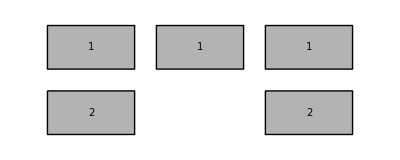
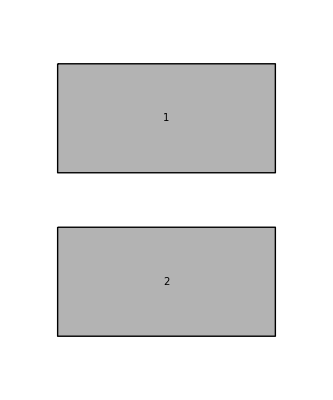
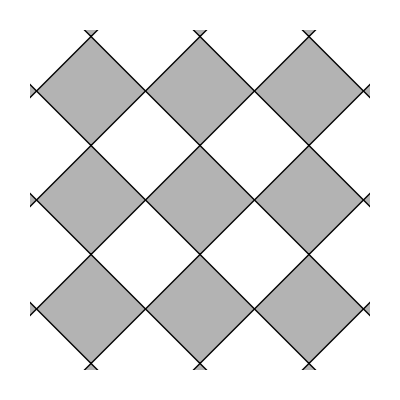
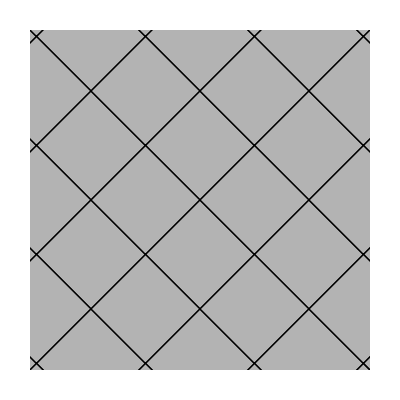
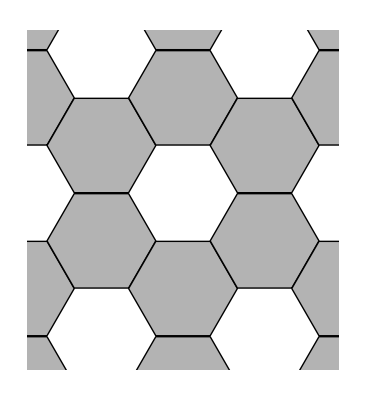
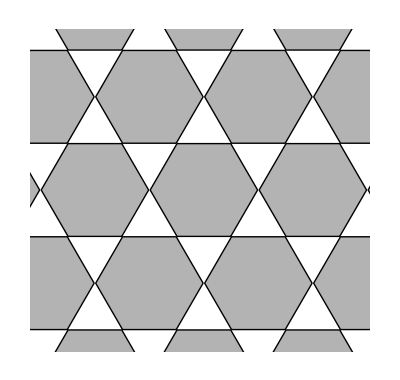
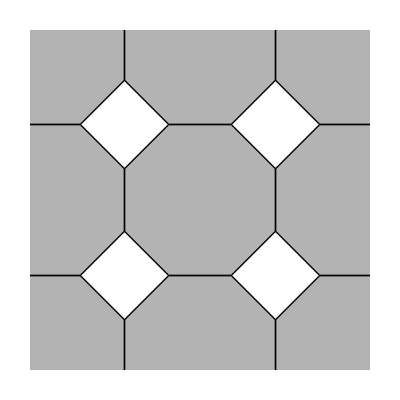
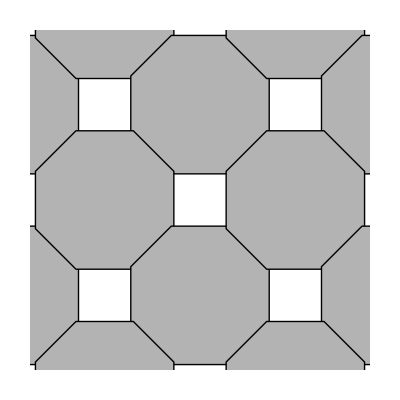
```mathematica
dtGeometricArray[]:=
DynamicModule[{
colList={5,5,5,5,5},
spaceH=.4Cos[30*Pi/180],
spaceV=.4-.2Sin[30*Pi/180],
offsetH=.2Cos[30*Pi/180],
offsetV=0,
offsetHList={},
offsetVList={},
width=.4,
height=.4,
origin={0,0},
clickPtScaled,
plotrange=1,
plotrangeList,
style,shapeStyle,space,shape=dtShapeStart,scaleAll=1,max={0,0},gearSize=.2,gearRotate=0,
gearTeeth=6,gearToothHeight=1,gearToothWidth=.3696,gearToothCurveMidPt=.5,gearToothCurve=0,gearToothPeakSize=0,gearToothBaseSize=.25,checkGearToothFit=False,gearToothAutoShape=False,layerCenter,func
},
Tooltip[Button[Dynamic@Graphics[{Gray,Cases[gear["Size"->1,"Teeth"->gearTeeth,"ToothHeight"->gearToothHeight,"ToothWidth"->gearToothWidth,"ToothCurveMidPoint"->gearToothCurveMidPt,"ToothCurve"->gearToothCurve,"ToothPeakSize"->gearToothPeakSize,"ToothBaseSize"->gearToothBaseSize],_FilledCurve,Infinity][[1]]},ImageSize->{24,24},PlotRangePadding->None],

$dtMode="layer";
CreateDialog[
Pane[Column[{
Grid[{
{"List the\nnumber of rows\nfor each column.",Spacer[20],Show[-Graphics-,ImageSize->{Automatic,50}],Spacer[20],Show[-Graphics-,ImageSize->{Automatic,50}]},
{"","","{2,1,2}","","{2}"}
}],
InputField[Dynamic@colList,ImageSize->{340,30}],
Grid[{Button[Row[{#[[1]],"x",#[[2]]}],colList=Table[#[[2]],{n,#[[1]]}],ImageSize->{49,20},Appearance->"Palette"]&/@{{1,1},{1,5},{5,1},{5,5},{10,10},{5,10},{10,5}}},Spacings->{0,0}],
Spacer[{0,10}],
Panel@Dynamic@Grid[{
{EventHandler[MouseAppearance[
plotrangeList={0,0};
plotrange=1;
offsetHList=ReplacePart[Table[0,{Max@colList}],Table[n->offsetH,{n,1,Max@colList,2}]];
offsetVList=ReplacePart[Table[0,{Length@colList}],Table[n->offsetV,{n,1,Length@colList,2}]];
style=If[MemberQ[$dtShapeSymbols,$dtStyle[[$dtPn]][[1]]],$dtStyle[[$dtPn]],$dtDefaultStyle];
func=RotationTransform[gearRotate Degree,{0,0}];
Dynamic[Graphics[Flatten@{
{EdgeForm[{CapForm["Butt"],style[[4]],Opacity[style[[5]]],AbsoluteThickness[style[[6]]],AbsoluteDashing[style[[7]]]}],Opacity[style[[3]]],style[[2]]},
Table[FilledCurve[BSplineCurve[scaleAll({(x-1) spaceH,-(y-1) spaceV}+#-{offsetHList[[y]],-offsetVList[[x]]}-{ spaceH*(Length[colList]-1),- spaceV*(Max[colList]-1)}/2)&/@(func[#]&/@gear["Size"->gearSize,"Teeth"->gearTeeth,"ToothHeight"->gearToothHeight,"ToothWidth"->gearToothWidth,"ToothCurveMidPoint"->gearToothCurveMidPt,"ToothCurve"->gearToothCurve,"ToothPeakSize"->gearToothPeakSize,"ToothBaseSize"->gearToothBaseSize][[1]][[6]][[1]][[1]]),SplineClosed->True]],{x,Length@colList},{y,Range[colList[[x]]]}]
},PlotRange->{-plotrange plotrangeList[[1]]+{-plotrange,plotrange},-plotrange plotrangeList[[2]]+{-plotrange,plotrange}},Background->LightGray,ImageSize->325]],
(* cursor *)
$dtCursorCanvas],
(* mouse events *)
"MouseUp":>(origin=plotrangeList),
"MouseDown":>(clickPtScaled=MousePosition["GraphicsScaled"]),
"MouseDragged":>(If[MousePosition["Graphics"]=!=None,
plotrangeList=origin+(MousePosition["GraphicsScaled"]-clickPtScaled)])
]},
{""},
{OpenerView[{"SHAPE",
Grid[{
{Row@{dtButtonStylePresets[]/."Preset"->"Style",Spacer[10],Button[Show[-Graphics-,ImageSize->23],
gearToothHeight=1;
gearToothBaseSize=.25;
gearToothCurve=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
gearToothHeight=1;
gearToothBaseSize=1;
gearToothCurve=.5,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
gearToothHeight=.8;
gearToothBaseSize=.4;
gearToothCurve=.4,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
gearToothHeight=.65;
gearToothBaseSize=.25;
gearToothCurve=.25,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
gearToothHeight=1;
gearToothBaseSize=1;
gearToothCurve=1,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
gearToothHeight=.65;
gearToothBaseSize=.9;
gearToothCurve=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
gearToothHeight=.7;
gearToothBaseSize=1.05;
gearToothCurve=.5,$dtButtonStyle]}},
{""},
{Row@{Pane["size ",ImageSize->50,Alignment->Right],Slider[Dynamic@gearSize,{.05,1,.01}],
Button["<",gearSize=Round[gearSize-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",gearSize=Round[gearSize+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@gearSize,ImageSize->50,Alignment->Left]}},
{Row@{Pane["rotate ",ImageSize->50,Alignment->Right],Slider[Dynamic@gearRotate,{-180,180,.5}],
Button["<",gearRotate=Round[gearRotate-=.5,.5],Appearance->"Palette"],
Button[">",gearRotate=Round[gearRotate+=.5,.5],Appearance->"Palette"],
" ",Pane[Dynamic@gearRotate,ImageSize->50,Alignment->Left]}},
{Row@{Pane["sides ",ImageSize->50,Alignment->Right],Slider[Dynamic@gearTeeth,{4,12,1}],
Button["<",gearTeeth=Round[gearTeeth-=1,1],Appearance->"Palette"],
Button[">",gearTeeth=Round[gearTeeth+=1,1],Appearance->"Palette"],
" ",Pane[Dynamic@gearTeeth,ImageSize->50,Alignment->Left]}},
{Row@{Pane["outer ",ImageSize->50,Alignment->Right],Slider[Dynamic@gearToothHeight,{.25,1,.01}],
Button["<",gearToothHeight=Round[gearToothHeight-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",gearToothHeight=Round[gearToothHeight+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@gearToothHeight,ImageSize->50,Alignment->Left]}},
{Row@{Pane["inner ",ImageSize->50,Alignment->Right],Slider[Dynamic@gearToothBaseSize,{.25,1,.01}],
Button["<",gearToothBaseSize=Round[gearToothBaseSize-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",gearToothBaseSize=Round[gearToothBaseSize+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@gearToothBaseSize,ImageSize->50,Alignment->Left]}},
{Row@{Pane["curve ",ImageSize->50,Alignment->Right],Slider[Dynamic@gearToothCurve,{0,1,.01}],
Button["<",gearToothCurve=Round[gearToothCurve-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",gearToothCurve=Round[gearToothCurve+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@gearToothCurve,ImageSize->50,Alignment->Left]}}

}]},False]},
{""},
{OpenerView[{"LAYOUT",
Grid[{{Row@{

Button[Show[-Graphics-,ImageSize->23],
gearSize=.2;
gearRotate=0;
gearTeeth=4;spaceH=.4;spaceV=.4;offsetH=0;offsetV=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
gearSize=.2;
gearRotate=0;
gearTeeth=4;
spaceH=.4;spaceV=.2;offsetH=.2;offsetV=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
gearSize=.2;
gearRotate=0;
gearTeeth=6;
spaceH=.4Cos[30*Pi/180];
spaceV=.4-.2Sin[30*Pi/180];
offsetH=.2Cos[30*Pi/180];
offsetV=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
gearSize=.2;
gearRotate=30;
gearTeeth=6;
spaceH=.3;
spaceV=.6Cos[30*Pi/180];
offsetH=.3;
offsetV=.2Cos[30*Pi/180],$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
gearSize=.2;
gearRotate=30;
gearTeeth=6;
spaceH=.4;
spaceV=.4Cos[30*Pi/180];
offsetH=.2;
offsetV=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
Block[{s},
s=((2Cos[67.5*Pi/180])+2(2Cos[67.5*Pi/180])Cos[45*Pi/180]);
gearSize=.2;
gearRotate=22.5;
gearTeeth=8;
spaceH=.2s;
spaceV=.2s;
offsetH=0;
offsetV=0
],$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
Block[{s},
s=((2Cos[67.5*Pi/180])+(2Cos[67.5*Pi/180])Cos[45*Pi/180]);
gearSize=.2;
gearRotate=22.5;
gearTeeth=8;
spaceH=.4s;
spaceV=.2s;
offsetH=.2s;
offsetV=0
],$dtButtonStyle]

}},
{""},
{Row@{Pane["scale all ",50,Alignment->Right],
Slider[Dynamic@scaleAll,{.1,2,.05}],
Button["<",scaleAll=Round[scaleAll-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",scaleAll=Round[scaleAll+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@scaleAll,50]}},
{Row@{Pane["space h ",50,Alignment->Right],
Slider[Dynamic@spaceH,{-1,1,$dtGridSize}],
Button["<",spaceH=Round[spaceH-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",spaceH=Round[spaceH+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@spaceH,50]}},
{Row@{Pane["space v ",50,Alignment->Right],
Slider[Dynamic@spaceV,{-1,1,$dtGridSize}],
Button["<",spaceV=Round[spaceV-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",spaceV=Round[spaceV+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@spaceV,50]}},
{Row@{Pane["offset h ",50,Alignment->Right],
Slider[Dynamic@offsetH,{-1,1,$dtGridSize}],
Button["<",offsetH=Round[offsetH-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",offsetH=Round[offsetH+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@offsetH,50]}},
{Row@{Pane["offset v ",50,Alignment->Right],
Slider[Dynamic@offsetV,{-1,1,$dtGridSize}],
Button["<",offsetV=Round[offsetV-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",offsetV=Round[offsetV+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@offsetV,50]}}
}]},False]}},Alignment->Left,Spacings->{0,0}],
Row@{Button["Cancel",DialogReturn[],ImageSize->100],
DefaultButton["Create shapes",
func=RotationTransform[gearRotate Degree,{0,0}];
Do[
dtNewEmptyLayer[];
$dtStyle[[Length@$dtP]][[1]]="BSplineFilledCurve";
$dtP[[Length@$dtP]]=scaleAll({(x-1) spaceH,-(y-1) spaceV}+#-{offsetHList[[y]],-offsetVList[[x]]}-{ spaceH*(Length[colList]-1),- spaceV*(Max[colList]-1)}/2)&/@(func[#]&/@gear["Size"->gearSize,"Teeth"->gearTeeth,"ToothHeight"->gearToothHeight,"ToothWidth"->gearToothWidth,"ToothCurveMidPoint"->gearToothCurveMidPt,"ToothCurve"->gearToothCurve,"ToothPeakSize"->gearToothPeakSize,"ToothBaseSize"->gearToothBaseSize][[1]][[6]][[1]][[1]]),
{x,Length@colList},{y,Range[colList[[x]]]}];$dtSelectedLayers=Range[(Length@$dtP-(colList/.List->Plus))+1,Length@$dtP];DialogReturn[],ImageSize->150]}
},Alignment->Center]],WindowTitle->"Geometric array",Modal->True],

$dtButtonStyle],"Geometric array"]
]
```

#### group shape

```mathematica
dtGroupShape[]:=
DynamicModule[{allPts,g,p,px,selectedLayers},
Tooltip[Button[$dtIconGroupShape,
(* shapes only *)
selectedLayers=If[MemberQ[$dtShapeSymbols,$dtStyle[[#]][[1]]],#,Nothing]&/@$dtSelectedLayers;
$dtSelectedLayers=If[selectedLayers==={},$dtSelectedLayers,selectedLayers];
If[Length[selectedLayers]>1,
dtSetUndo[];
g=dtRenderObject["Export"->True,"SelectedObjectsOnly"->True]/.{
Arrowheads[{{_,0,Graphics[_]}}]->Arrowheads[{{-Medium,0}}],
Arrowheads[{{_,1,Graphics[_]}}]->Arrowheads[Medium],
Arrowheads[{{_,_,Graphics[_]},{_,_,Graphics[_]}}]->Arrowheads[{-Medium,Medium}]
};
allPts=Join[Flatten[Cases[g,#,Infinity]&/@{Arrow[___],Polygon[___],Line[___],BSplineCurve[___],BezierCurve[___],Point[___],FilledCurve[___]}],
Flatten[Cases[g,Text[___],Infinity]]];
p=Join[Cases[allPts,{0,0},Infinity],
Cases[allPts,{_Real,_Real},Infinity]];
px=#[[1]]&/@p;
$dtLibrary="Mechanical";
$dtLibraryObjectMechanical=graphics;
$dtLibraryObject=$dtLibraryObjectMechanical;
dtNewEmptyLayer[];
$dtObjOpt[[$dtPn]]=Replace[Options[$dtLibraryObject],{("Size"->_)->("Size"->(Max[px]-Min[px])/4),("Graphics"->_)->("Graphics"->Graphics[g,PlotRangePadding->None(*,ImagePadding->None*)]),("Location"->_)->("Location"->dtFindCenter[p])},Infinity];
$dtStyle[[$dtPn]]=ReplacePart[$dtDefaultLibrary,1->$dtLibraryObject];
$dtP[[$dtPn]]={dtFindCenter[p]};
dtLibraryOptions[];
(* delete original group layers *)
$dtSelectedLayers=selectedLayers;
dtDeleteObj[];
$dtPn=Length@$dtP;
$dtSelectedLayers={$dtPn}
],
$dtButtonStyle],"Group shapes\n- select shapes\n- click this button to create duplicate group\n- click Style|Options to size and rotate\n- ungroup to style"]
]
```

#### library tools

```mathematica
dtButtonLibraryTools[]:=
{
Tooltip[Dynamic@Button[Style[Graphics[$dtLibraryObjectCircuit[]],Magnification->.25],
dtSetUndo[];
$dtLibrary="Circuit";
$dtLibraryObject=$dtLibraryObjectCircuit;
dtNewEmptyLayer[];
$dtObjOpt[[$dtPn]]=Options[$dtLibraryObject];
$dtStyle[[$dtPn]]=ReplacePart[$dtDefaultLibrary,1->$dtLibraryObject];
$dtP[[$dtPn]]={{0,0}};
dtLibraryOptions[],$dtButtonStyle],
"Insert circuit library object"],

Tooltip[Dynamic@Button[Style[Graphics[$dtLibraryObjectMechanical[]],Magnification->.25],
dtSetUndo[];
$dtLibrary="Mechanical";
$dtLibraryObject=$dtLibraryObjectMechanical;
dtNewEmptyLayer[];
$dtObjOpt[[$dtPn]]=Options[$dtLibraryObject];
$dtStyle[[$dtPn]]=ReplacePart[$dtDefaultLibrary,1->$dtLibraryObject];
$dtP[[$dtPn]]={{0,0}};
dtLibraryOptions[],$dtButtonStyle],
"Insert mechanical library object"],

Tooltip[Dynamic@Button[
Dynamic@If[$dtLibraryObject3d===axo3dObject,
Graphics[axo3dObject["Size"->1],PlotRange->.3,ImageSize->25,Background->White],
Style[Graphics[$dtLibraryObject3d[]]/.{(FontSize->_)->(FontSize->$dtPlotrange/.05),(LineSpacing->_)->(LineSpacing->{0,$dtPlotrange/.05})},Magnification->.2]
],
dtNewEmptyLayer[];
$dtShow3dGrid=$dtCurrent3dGrid;
$dtLibrary="3D";
$dtLibraryObject=$dtLibraryObject3d;
$dtObjOpt[[$dtPn]]=Options[$dtLibraryObject];
$dtStyle[[$dtPn]]=ReplacePart[$dtDefaultLibrary,1->$dtLibraryObject];
$dtP[[$dtPn]]={{0,0}};
dtLibraryOptions[],$dtButtonStyle],
"Insert 3d library object"]
}
```

#### link tools

```mathematica
dtButtonLinkTools[]:=
{
Tooltip[Dynamic@Button[$dtIconLinkChain,
If[Length@$dtRenderLayers>1,
$dtMode="linkChain";$dtPShapes=Table[If[$dtStyle[[n]][[1]]=!="Link",$dtP[[n]],{{}}],{n,Length@$dtP}],
MessageDialog["Need at least two objects (origin and target)."]
],Background->If[$dtMode==="linkChain",$dtButtonHighlight,Automatic],$dtButtonStyle],"2D LINK CHAIN\nObjects linked in order clicked from first selected object.\nClick select tool when finished."],

Tooltip[Dynamic@Button[$dtIconLinkTree,
If[Length@$dtRenderLayers>1,
$dtMode="linkTree";$dtLinkTreeOrigin=$dtSelectedLayers[[1]];$dtPShapes=Table[If[$dtStyle[[n]][[1]]=!="Link",$dtP[[n]],{{}}],{n,Length@$dtP}],
MessageDialog["Need at least two objects (origin and target)."]
],Background->If[$dtMode==="linkTree",$dtButtonHighlight,Automatic],$dtButtonStyle],"2D LINK TREE\nClicked objects link to selected object.\nCommand-click object to select.\nClick select tool when finished."],

Tooltip[Button[$dtIconLinkFix,
$dtMode="layer";
If[CurrentValue["CommandKey"],
dtCalculateLinkLocs["Link"->All],
dtCalculateLinkLocs["Link"->$dtSelectedLayers]
],$dtButtonStyle],"Fix selected 2D links.\nCommand-click to fix all 2D links."]
}
```

#### move direction

```mathematica
dtMoveDirection[]:=Tooltip[Graphics[{EdgeForm[{AbsoluteThickness[2],GrayLevel[.3]}],GrayLevel[.5],Disk[],GrayLevel[.3],CapForm["Butt"],AbsoluteThickness[2],Line[{{Sin[Pi/4],Cos[Pi/4]},-{Sin[Pi/4],Cos[Pi/4]}}],Line[{{Sin[Pi/4],-Cos[Pi/4]},{-Sin[Pi/4],Cos[Pi/4]}}],
Table[With[{b=bInfo},
Inset[
Button[Graphics[{GrayLevel[.3],b[[1]]},ImageSize->{12,12},PlotRangePadding->None],
dtSetUndo;
Do[
If[$dtP[[s]]=!={},
(* shapes, text, links *)
If[FreeQ[$dt3dSymbols,$dtStyle[[s]][[1]]],
$dtP[[s]]=b[[2]]+#&/@$dtP[[s]],{s,$dtSelectedLayers}];
(* library object *)
If[$dtObjOpt[[s]]=!={}&&FreeQ[$dt3dSymbols,$dtStyle[[s]][[1]]],
$dtObjOpt[[s]][[Position[$dtObjOpt[[s]],"Location"->_][[1]][[1]]]][[-1]]=$dtP[[s]][[1]]];
(* 3d object *)
If[MemberQ[$dt3dSymbols,$dtStyle[[s]][[1]]],
$dtObjOpt[[s]][[Position[$dtObjOpt[[s]],"AxisLocation"->_][[1]][[1]]]][[-1]]+=If[$dtShow3dGrid==="XY",
{-b[[2]][[2]],-b[[2]][[1]],0},
{0,-b[[2]][[1]],b[[2]][[2]]}
]]],
{s,$dtSelectedLayers}],
FrameMargins->0,ImageSize->{16,16},Appearance->"Frameless"],bInfo[[3]]
]],{bInfo,{
{Polygon[{{-1,0},{0,1},{1,0}}],{0,$dtGridSize},{0,.6}},
{Polygon[{{1,1},{0,0},{1,-1}}],{-$dtGridSize,0},{-.6,0}},
{Polygon[{{0,1},{1,0},{0,-1}}],{$dtGridSize,0},{.6,0}},
{Polygon[{{-1,0},{0,-1},{1,0}}],{0,-$dtGridSize},{0,-.6}}
}}]},ImagePadding->{{0,3},{0,0}},ImageSize->50],"Move selected objects 1 grid unit"]
```

#### move direction 3d

```mathematica
dtMoveDirection3d[]:=

Tooltip[Graphics[{EdgeForm[{AbsoluteThickness[2],GrayLevel[.3]}],GrayLevel[.5],Disk[],GrayLevel[.3],CapForm["Butt"],AbsoluteThickness[2],Line[{{-1,0},{1,0}}],Line[{{Sin[Pi/6],Cos[Pi/6]},-{Sin[Pi/6],Cos[Pi/6]}}],Line[{{Sin[Pi/6],-Cos[Pi/6]},{-Sin[Pi/6],Cos[Pi/6]}}],

(* need to fix all below *)
Table[With[{b=bInfo},
Inset[
Button[Graphics[b[[1]],ImageSize->{12,12},PlotRangePadding->None],
dtSetUndo;
Do[
If[$dtP[[s]]=!={},
(* only 3d object *)
If[MemberQ[$dt3dSymbols,$dtStyle[[s]][[1]]],
$dtObjOpt[[s]][[Position[$dtObjOpt[[s]],"AxisLocation"->_][[1]][[1]]]][[-1]]+=b[[2]]]],
{s,$dtSelectedLayers}],
FrameMargins->0,ImageSize->{16,16},Appearance->"Frameless"],bInfo[[3]]
]],{bInfo,{
{{ReplacePart[$dt3dAxisZColor,{2->1,3->1}],Polygon[{{-1,0},{0,1},{1,0}}]},{0,0,$dtGridSize},{0,.7}},
{Rotate[{$dt3dAxisXColor,Polygon[{{-1,0},{0,1},{1,0}}]},1Pi/3,{0,0}],{-$dtGridSize,0,0},{-.55,.3}},
{Rotate[{ReplacePart[$dt3dAxisYColor,{2->1,3->.7}],Polygon[{{-1,0},{0,1},{1,0}}]},2Pi/3,{0,0}],{0,$dtGridSize,0},{-.55,-.3}},
{Rotate[{ReplacePart[$dt3dAxisZColor,{2->1,3->1}],Polygon[{{-1,0},{0,1},{1,0}}]},3Pi/3,{0,0}],{0,0,-$dtGridSize},{0,-.7}},
{Rotate[{$dt3dAxisXColor,Polygon[{{-1,0},{0,1},{1,0}}]},4Pi/3,{0,0}],{$dtGridSize,0,0},{.55,-.3}},
{Rotate[{ReplacePart[$dt3dAxisYColor,{2->1,3->.7}],Polygon[{{-1,0},{0,1},{1,0}}]},5Pi/3,{0,0}],{0,-$dtGridSize,0},{.55,.3}}
}}]},ImagePadding->{{0,3},{0,0}},ImageSize->50],
"Move selected objects 1 grid unit"]
```

#### multi shape array

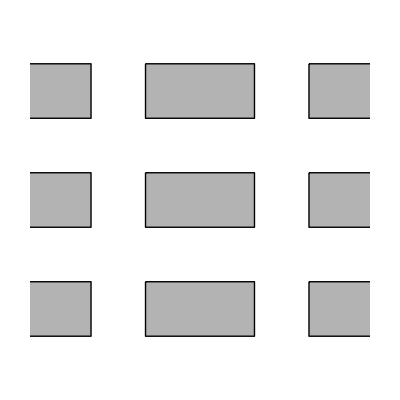
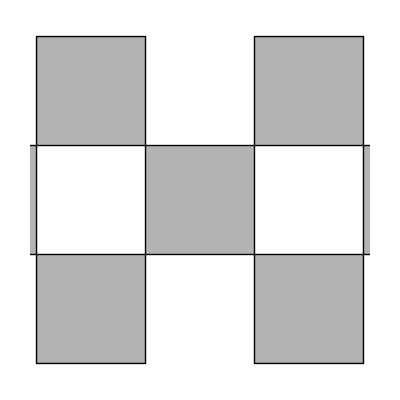
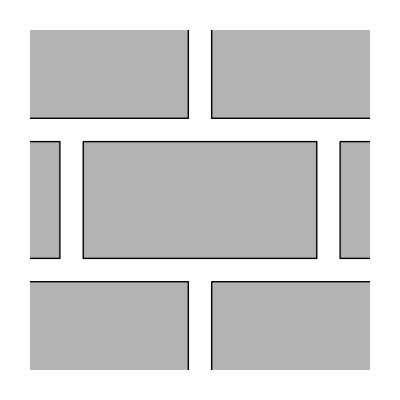
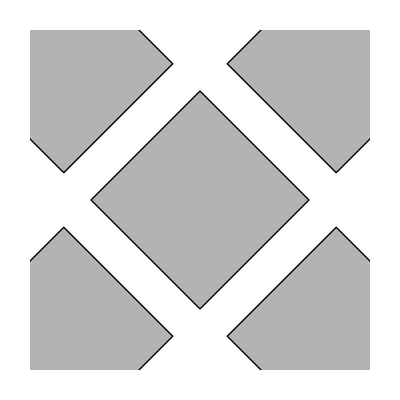
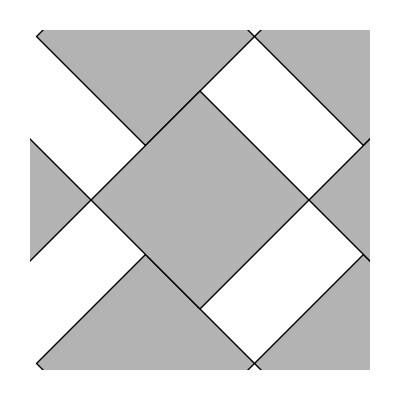
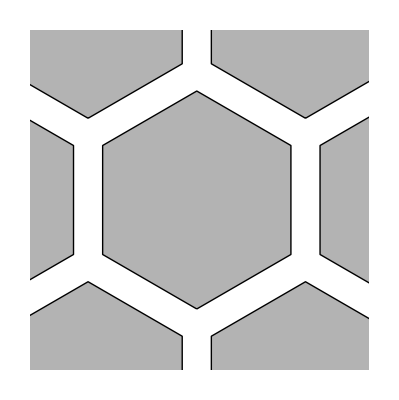
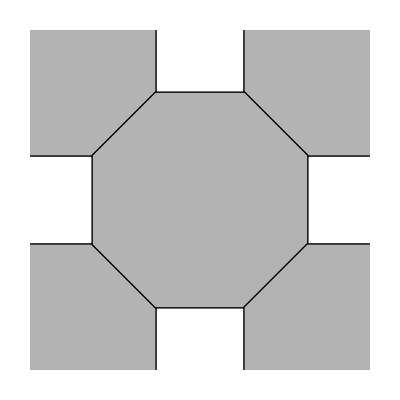
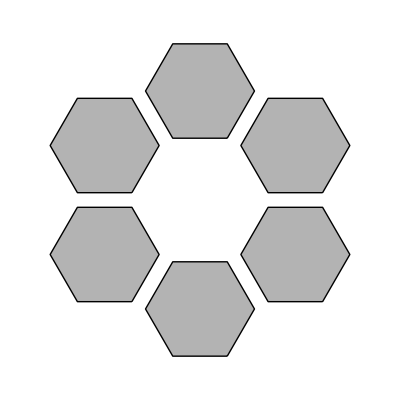
```mathematica
dtMultiShapeArray[]:=
DynamicModule[{
colList={3,2,3},
spaceH=.2,
spaceV=.2,
offsetH=0,
offsetV=0,
offsetHList={},
offsetVList={},
width=.4,
height=.2,
origin={0,0},
clickPtScaled,
plotrange=1,
plotrangeList,
style,shapeStyle,space,shape=dtShapeProcess,res=10,rotate=0,scaleAll=1
},
Tooltip[Button[$dtIconMultiShapeArray,

$dtMode="layer";
CreateDialog[
Pane[Column[{
Grid[{
{"List the\nnumber of rows\nfor each column.",Spacer[20],Show[-Graphics-,ImageSize->{Automatic,50}],Spacer[20],Show[-Graphics-,ImageSize->{Automatic,50}]},
{"","","{2,1,2}","","{2}"}
}],
InputField[Dynamic@colList,ImageSize->{340,30}],
Grid[{Button[Row[{#[[1]],"x",#[[2]]}],colList=Table[#[[2]],{n,#[[1]]}],ImageSize->{49,20},Appearance->"Palette"]&/@{{1,1},{1,5},{5,1},{5,5},{10,10},{5,10},{10,5}}},Spacings->{0,0}],
Spacer[{0,10}],
Panel@Dynamic@Grid[{
{EventHandler[MouseAppearance[
plotrangeList={0,0};
plotrange=1;
space={width (Length@colList)+spaceH (Length@colList-1),-height Max[colList]-spaceV(Max[colList]-1)}/2;
offsetHList=ReplacePart[Table[0,{Max@colList}],Table[n->offsetH,{n,1,Max@colList,2}]];
offsetVList=ReplacePart[Table[0,{Length@colList}],Table[n->offsetV,{n,1,Length@colList,2}]];
style=If[MemberQ[$dtShapeSymbols,$dtStyle[[$dtPn]][[1]]],$dtStyle[[$dtPn]],$dtDefaultStyle];
Dynamic[Graphics[Flatten@{
(* inline item with rows *)
{EdgeForm[{CapForm["Butt"],style[[4]],Opacity[style[[5]]],AbsoluteThickness[style[[6]]],AbsoluteDashing[style[[7]]]}],Opacity[style[[3]]],style[[2]]},
Table[Polygon[scaleAll(#-space+{offsetHList[[y]],-offsetVList[[x]]})&/@shape[height,width,spaceH,spaceV,x,y,res,rotate]],{x,Length@colList},{y,Range[colList[[x]]]}]
},PlotRange->{-plotrange plotrangeList[[1]]+{-plotrange,plotrange},-plotrange plotrangeList[[2]]+{-plotrange,plotrange}},Background->LightGray,ImageSize->325]],
(* cursor *)
$dtCursorCanvas],
(* mouse events *)
"MouseUp":>(origin=plotrangeList),
"MouseDown":>(clickPtScaled=MousePosition["GraphicsScaled"]),
"MouseDragged":>(If[MousePosition["Graphics"]=!=None,
plotrangeList=origin+(MousePosition["GraphicsScaled"]-clickPtScaled)])
]},
{""},
{OpenerView[{"SHAPE",
Grid[{
{Row@{dtButtonStylePresets[]/."Preset"->"Style",Spacer[10],
Grid[Partition[{
Button[Show[Evaluate@dtShapeIcon[Rectangle[{0,0},{1,.5}]],ImageSize->23],
shape=dtShapeProcess,$dtButtonStyle],
Button[Show[Evaluate@dtShapeIcon[Polygon[{{0,.25},{.5,0},{1,.25},{.5,.5}}]],ImageSize->23],
shape=dtShapeDecision,$dtButtonStyle],
Button[Show[Evaluate@dtShapeIcon[Polygon[{{0,0},{.75,0},{1,.5},{.25,.5}}]],ImageSize->23],
shape=dtShapeData,$dtButtonStyle],
Button[Show[Evaluate@dtShapeIcon[Disk[]],ImageSize->23],
shape=dtShapeStart,$dtButtonStyle],
Button[Show[Evaluate@dtShapeIcon[Polygon[Table[{Sin[n],Cos[n]},{n,Pi/2,2.5Pi-Pi/3,Pi/3}]]],ImageSize->23],
shape=dtShapePreparation,$dtButtonStyle],
Button[Show[Evaluate@dtShapeIcon[Polygon[{{.5,0},{1,.5},{1,1},{0,1},{0,.5}}]],ImageSize->23],
shape=dtShapeReference,$dtButtonStyle],
Button[Show[Evaluate@dtShapeIcon[Polygon[Join[
Table[{.75+.25Sin[n],.5+.25Cos[n]},{n,0,Pi,Pi/10}],
Table[{.25+.25Sin[n],.5+.25Cos[n]},{n,Pi,2Pi,Pi/10}]
]]],ImageSize->23],
shape=dtShapeTerminator,$dtButtonStyle],
Button[Show[Evaluate@dtShapeIcon[Polygon[Join[
Table[{.75+.25Sin[n],.5+.25Cos[n]},{n,0,Pi,Pi/10}],
{{0,.25},{0,.75}}
]]],ImageSize->23],
shape=dtShapeDelay,$dtButtonStyle]
},8,8,1,{}],Spacings->{0,0}]}},
{""},
{Row@{Pane["width ",50,Alignment->Right],
Slider[Dynamic@width,{0,1,$dtGridSize}],
Button["<",width=Round[width-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",width=Round[width+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@width,50]}},
{Row@{Pane["height ",50,Alignment->Right],
Slider[Dynamic@height,{0,1,$dtGridSize}],
Button["<",height=Round[height-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",height=Round[height+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@height,50]}},
{Row@{Pane["sides ",50,Alignment->Right],
Dynamic@Slider[Dynamic@res,{2,20,1},Enabled->MemberQ[{dtShapeStart,dtShapeTerminator,dtShapeDelay},shape]],
Button["<",res-=1,Appearance->"Palette",Enabled->MemberQ[{dtShapeStart,dtShapeTerminator,dtShapeDelay},shape]],
Button[">",res+=1,Appearance->"Palette",Enabled->MemberQ[{dtShapeStart,dtShapeTerminator,dtShapeDelay},shape]],
" ",Pane[Switch[shape,
dtShapeTerminator,
Dynamic[(2*res)+2],
dtShapeDelay,
Dynamic[res+3],
_,
Dynamic[2*res]
],50]}},
{Row@{Pane["rotate ",50,Alignment->Right],
Dynamic@Slider[Dynamic@rotate,{0,90,.5},Enabled->MemberQ[{dtShapeStart,dtShapePreparation},shape]],
Button["<",rotate-=.5,Appearance->"Palette",Enabled->MemberQ[{dtShapeStart,dtShapePreparation},shape]],
Button[">",rotate+=.5,Appearance->"Palette",Enabled->MemberQ[{dtShapeStart,dtShapePreparation},shape]],
" ",Pane[Dynamic@rotate,50]}}
},Alignment->Left]
},False]},
{""},
{OpenerView[{"LAYOUT",
Grid[{
{Row[{
Grid[Partition[{
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeProcess;width=.4;height=.2;spaceH=.2;
spaceV=.2;res=2;offsetH=0;offsetV=0;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeProcess;width=.2;height=.2;spaceH=.2;
spaceV=0;res=2;offsetH=.2;offsetV=0;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeProcess;width=.5;height=.25;spaceH=0.05;
spaceV=.05;res=2;offsetH=.275;offsetV=0;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeStart;width=.4;height=.4;spaceH=0.1;
spaceV=-.15;res=2;offsetH=.25;offsetV=0;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeStart;width=.4;height=.4;spaceH=0;
spaceV=-.1;res=2;offsetH=.3;offsetV=0;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeStart;width=.4;height=.4;spaceH=0;
spaceV=-.05;res=3;offsetH=.2;offsetV=0;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeStart;width=.4;height=.4;spaceH=-.03;
spaceV=-.03;res=4;offsetH=0;offsetV=0;rotate=22.5,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeStart;width=.5;height=.5;spaceH=.15;
spaceV=-.175;res=4;offsetH=.325;offsetV=0;rotate=22.5,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeStart;width=.4;height=.4;spaceH=-.05;
spaceV=.2;res=3;offsetH=.35;offsetV=.2;rotate=30,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeStart;width=.2;height=.2;spaceH=0;
spaceV=-.05;res=2;offsetH=.05;offsetV=.1;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeStart;width=.3;height=.3;spaceH=0;
spaceV=-.1;res=2;offsetH=.1;offsetV=.05;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeProcess;width=.4;height=.4;spaceH=.05;
spaceV=.05;res=2;offsetH=.2;offsetV=.2;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeStart;width=.5;height=.5;spaceH=-.1;
spaceV=-.1;res=2;offsetH=.15;offsetV=.15;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeStart;width=.25;height=.25;spaceH=-.05;
spaceV=-.05;res=2;offsetH=.05;offsetV=.05;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeReference;width=.2;height=.2;spaceH=0;
spaceV=0;res=2;offsetH=.1;offsetV=.1;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
shape=dtShapeStart;width=.3;height=.3;spaceH=0;
spaceV=0;res=4;offsetH=.15;offsetV=.15;rotate=0,$dtButtonStyle]
},8,8,1,{}],Spacings->{0,0}]}]},
{""},
{Row@{Pane["scale all ",50,Alignment->Right],
Slider[Dynamic@scaleAll,{.1,2,.05}],
Button["<",scaleAll=Round[scaleAll-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",scaleAll=Round[scaleAll+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@scaleAll,50]}},
{Row@{Pane["space h ",50,Alignment->Right],
Slider[Dynamic@spaceH,{-1,1,$dtGridSize}],
Button["<",spaceH=Round[spaceH-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",spaceH=Round[spaceH+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@spaceH,50]}},
{Row@{Pane["space v ",50,Alignment->Right],
Slider[Dynamic@spaceV,{-1,1,$dtGridSize}],
Button["<",spaceV=Round[spaceV-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",spaceV=Round[spaceV+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@spaceV,50]}},
{Row@{Pane["offset h ",50,Alignment->Right],
Slider[Dynamic@offsetH,{-1,1,$dtGridSize}],
Button["<",offsetH=Round[offsetH-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",offsetH=Round[offsetH+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@offsetH,50]}},
{Row@{Pane["offset v ",50,Alignment->Right],
Slider[Dynamic@offsetV,{-1,1,$dtGridSize}],
Button["<",offsetV=Round[offsetV-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",offsetV=Round[offsetV+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@offsetV,50]}}
}]
},False]}
},Alignment->Left,Spacings->{0,0}],
Row@{Button["Cancel",DialogReturn[],ImageSize->100],
DefaultButton["Create shapes",
Do[
dtNewEmptyLayer[];
$dtP[[Length@$dtP]]=scaleAll(#-space+{offsetHList[[y]],-offsetVList[[x]]}&/@shape[height,width,spaceH,spaceV,x,y,res,rotate]),
{x,Length@colList},{y,Range[colList[[x]]]}];$dtSelectedLayers=Range[(Length@$dtP-(colList/.List->Plus))+1,Length@$dtP];DialogReturn[],ImageSize->150]}
},Alignment->Center]],WindowTitle->"Multi-shape array",Modal->True],

$dtButtonStyle],"Muti-shape array"]
]
```

#### multi shape array shapes

```mathematica
dtShapeIcon[shape_]:=Graphics[{EdgeForm[Black],GrayLevel[.7],shape},ImageSize->{{30},{20}}]

dtShapeProcess[height_,width_,spaceH_,spaceV_,x_,y_,res_,rotate_]:=
Block[{},
{
{(x-1) width+(x-1) spaceH,-(y-1) height -(y-1) spaceV},
{x width+(x-1) spaceH,-(y-1) height -(y-1) spaceV},
{x width+(x-1) spaceH,-y height -(y-1) spaceV},
{(x-1) width+(x-1) spaceH,-y height -(y-1) spaceV}
}
]

dtShapeDecision[height_,width_,spaceH_,spaceV_,x_,y_,res_,rotate_]:=
Block[{},
{
{.5width+(x-1) width+(x-1) spaceH,-(y-1) height -(y-1) spaceV},
{x width+(x-1) spaceH,-.5height-(y-1) height -(y-1) spaceV},
{-.5width+x width+(x-1) spaceH,-y height -(y-1) spaceV},
{(x-1) width+(x-1) spaceH,.5height-y height -(y-1) spaceV}
}
]

dtShapeData[height_,width_,spaceH_,spaceV_,x_,y_,res_,rotate_]:=
Block[{},
{
{.1+(x-1) width+(x-1) spaceH,-(y-1) height -(y-1) spaceV},
{.1+x width+(x-1) spaceH,-(y-1) height -(y-1) spaceV},
{x width+(x-1) spaceH,-y height -(y-1) spaceV},
{(x-1) width+(x-1) spaceH,-y height -(y-1) spaceV}
}
]

dtShapeReference[height_,width_,spaceH_,spaceV_,x_,y_,res_,rotate_]:=
Block[{},
{
{(x-1) width+(x-1) spaceH,-(y-1) height -(y-1) spaceV},
{x width+(x-1) spaceH,-(y-1) height -(y-1) spaceV},
{x width+(x-1) spaceH,-.5height-(y-1) height -(y-1) spaceV},
{-.5width+x width+(x-1) spaceH,-y height -(y-1) spaceV},
{(x-1) width+(x-1) spaceH,.5height-y height -(y-1) spaceV}
}
]

dtShapeStart[height_,width_,spaceH_,spaceV_,x_,y_,res_,rotate_]:=
Block[{},
Table[{(x-1) spaceH,-(y-1) spaceV}+{(x-1) width,-(y-1) height}+{width,-height}{.5+.5Sin[n],.5+.5Cos[n]},{n,rotate*Pi/180,rotate*Pi/180+2Pi-Pi/res,Pi/res}]
]

dtShapePreparation[height_,width_,spaceH_,spaceV_,x_,y_,res_,rotate_]:=
Block[{},
Table[{(x-1) spaceH,-(y-1) spaceV}+{(x-1) width,-(y-1) height}+{width,-height}{.5+.5Sin[n],.5+.5Cos[n]},{n,rotate*Pi/180+Pi/2,rotate*Pi/180+(2.5Pi-Pi/3),Pi/3}]
]

dtShapeTerminator[height_,width_,spaceH_,spaceV_,x_,y_,res_,rotate_]:=
Block[{},
Join[
Table[{(x-1) spaceH,-(y-1) spaceV}+{(x-1) width,-(y-1) height}+{.8width+.5height Sin[n],-.5height+.5height Cos[n]},{n,0,Pi,Pi/res}],
Table[{(x-1) spaceH,-(y-1) spaceV}+{(x-1) width,-(y-1) height}+{.2width+.5height Sin[n],-.5height+.5height Cos[n]},{n,Pi,2Pi,Pi/res}]
]
]

dtShapeDelay[height_,width_,spaceH_,spaceV_,x_,y_,res_,rotate_]:=
Block[{},
Join[
Table[{(x-1) spaceH,-(y-1) spaceV}+{(x-1) width,-(y-1) height}+{.8width+.5height Sin[n],-.5height+.5height Cos[n]},{n,0,Pi,Pi/res}],
{{(x-1) spaceH,-(y-1) spaceV}+{(x-1) width,-(y-1) height}+{0,-height},
{(x-1) spaceH,-(y-1) spaceV}+{(x-1) width,-(y-1) height}+{0,0}}
]
]
```

#### object tools

```mathematica
dtButtonObjectTools[]:=
{
dtGroupShape[],
dtUngroupShape[],

Tooltip[Dynamic@Button[$dtIconMoveToFront,
$dtMode="layer";
dtSetUndo[];
Do[
AppendTo[$dtP,$dtP[[s]]];$dtP=Delete[$dtP,s];
AppendTo[$dtStyle,$dtStyle[[s]]];$dtStyle=Delete[$dtStyle,s];
AppendTo[$dtGradients,$dtGradients[[s]]];$dtGradients=Delete[$dtGradients,s];
AppendTo[$dtRotate,$dtRotate[[s]]];$dtRotate=Delete[$dtRotate,s];
AppendTo[$dtScale,$dtScale[[s]]];$dtScale=Delete[$dtScale,s];
AppendTo[$dtObjOpt,$dtObjOpt[[s]]];$dtObjOpt=Delete[$dtObjOpt,s];
AppendTo[$dtAxoSymbols,$dtAxoSymbols[[s]]];$dtAxoSymbols=Delete[$dtAxoSymbols,s],
{s,Reverse@$dtSelectedLayers}];
$dtPn=Length@$dtP;$dtSelectedLayers=Range[($dtPn-Length@$dtSelectedLayers)+1,$dtPn],$dtButtonStyle],"Move selected to front"],

Tooltip[Dynamic@Button[$dtIconMoveToBack,
$dtMode="layer";
dtSetUndo[];
Do[
PrependTo[$dtP,$dtP[[s]]];$dtP=Delete[$dtP,s+1];
PrependTo[$dtStyle,$dtStyle[[s]]];$dtStyle=Delete[$dtStyle,s+1];
PrependTo[$dtGradients,$dtGradients[[s]]];$dtGradients=Delete[$dtGradients,s+1];
PrependTo[$dtRotate,$dtRotate[[s]]];$dtRotate=Delete[$dtRotate,s+1];
PrependTo[$dtScale,$dtScale[[s]]];$dtScale=Delete[$dtScale,s+1];
PrependTo[$dtObjOpt,$dtObjOpt[[s]]];$dtObjOpt=Delete[$dtObjOpt,s+1];
PrependTo[$dtAxoSymbols,$dtAxoSymbols[[s]]];$dtAxoSymbols=Delete[$dtAxoSymbols,s+1]
,
{s,$dtSelectedLayers}];
$dtPn=1;$dtSelectedLayers=Range[$dtPn,Length@$dtSelectedLayers],$dtButtonStyle],"Move selected to back"],

Tooltip[Button[$dtIconObjectDupe,
DynamicModule[{quantity=1},
CreateDialog[Pane[Column[{
Pane[Row@{" h ",Slider[Dynamic@$dtDupeOffset[[1]],{-1,1,$dtGridSize}],
Button["<",$dtDupeOffset[[1]]-=$dtGridSize,ImageSize->12,Appearance->"Palette"],
Button[">",$dtDupeOffset[[1]]+=$dtGridSize,ImageSize->12,Appearance->"Palette"],
Spacer[5],Dynamic@Round[$dtDupeOffset[[1]],.005]},ImageSize->270],
Pane[Row@{" v ",Dynamic@Slider[Dynamic@$dtDupeOffset[[2]],{-1,1,$dtGridSize}],
Button["<",$dtDupeOffset[[2]]-=$dtGridSize,ImageSize->12,Appearance->"Palette"],
Button[">",$dtDupeOffset[[2]]+=$dtGridSize,ImageSize->12,Appearance->"Palette"],
Spacer[5],Dynamic@Round[$dtDupeOffset[[2]],.005]},ImageSize->270],
Row@{"quantity ",PopupMenu[Dynamic@quantity,Range[10]]},
Row@{CancelButton[DialogReturn[]],DefaultButton[dtSetUndo[];Do[dtDupeObj[],{quantity}];DialogReturn[]]}},
Alignment->Center],ImageSize->270],WindowTitle->"Duplicate",Modal->True]
],$dtButtonStyle],"Duplicate selected"],

Tooltip[Dynamic@Button[$dtIconObjectDelete,dtDeleteObj[],$dtButtonStyle],"Delete selected -\nCommand-click to delete all"],

dtButtonUndo[]
}
```

#### option | style button

```mathematica
Options[dtOptionSlider]={"Name"->"Size","SliderName"->"size ","Range"->{0,1},"Increment"->.1,"Default"->0};
dtOptionSlider[OptionsPattern[]]:=
With[{n=OptionValue["Name"],sn=OptionValue["SliderName"],r=OptionValue["Range"],i=OptionValue["Increment"],d=OptionValue["Default"]},
Row[{Pane[sn,50,Alignment->Right],
Slider[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]],{r[[1]],r[[2]],i}],Button["<",$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]]=If[CurrentValue["CommandKey"],d,Round[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]]-=i,i]],Appearance->"Palette"],
Button[">",$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]]=If[CurrentValue["CommandKey"],d,Round[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]]+=i,i]],Appearance->"Palette"],
" ",Pane[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]],50]
}]
]

Options[dtOptionSliderPart]={"Name"->"Size","SliderName"->"size ","Range"->{0,1},"Increment"->.1,"Default"->0,"Part"->1};
dtOptionSliderPart[OptionsPattern[]]:=
With[{n=OptionValue["Name"],sn=OptionValue["SliderName"],r=OptionValue["Range"],i=OptionValue["Increment"],d=OptionValue["Default"],p=OptionValue["Part"]},
Row[{Pane[sn,50,Alignment->Right],
Slider[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]][[p]],{r[[1]],r[[2]],i}],Button["<",$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]][[p]]=If[CurrentValue["CommandKey"],d,Round[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]][[p]]-=i,i]],Appearance->"Palette"],
Button[">",$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]][[p]]=If[CurrentValue["CommandKey"],d,Round[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]][[p]]+=i,i]],Appearance->"Palette"],
" ",Pane[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]][[p]],50]
}]
]

Options[dtOptionSliderPart2]={"Name"->"Size","SliderName"->"size ","Range"->{0,1},"Increment"->.1,"Default"->0,"Part1"->1,"Part2"->1};
dtOptionSliderPart2[OptionsPattern[]]:=
With[{n=OptionValue["Name"],sn=OptionValue["SliderName"],r=OptionValue["Range"],i=OptionValue["Increment"],d=OptionValue["Default"],p1=OptionValue["Part1"],p2=OptionValue["Part2"]},
Row[{Pane[sn,50,Alignment->Right],
Slider[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]][[p1]][[p2]],{r[[1]],r[[2]],i}],Button["<",$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]][[p1]][[p2]]=If[CurrentValue["CommandKey"],d,Round[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]][[p1]][[p2]]-=i,i]],Appearance->"Palette"],
Button[">",$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]][[p1]][[p2]]=If[CurrentValue["CommandKey"],d,Round[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]][[p1]][[p2]]+=i,i]],Appearance->"Palette"],
" ",Pane[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],n->_][[1]][[1]]]][[-1]][[p1]][[p2]],50]
}]
]

dtOptionsButton[]:=
DynamicModule[{},
Button[If[MemberQ[{axo,axoExtrude},$dtStyle[[$dtPn,1]]],Style["Options",Black,10],Style["Style | Options",Black,10]],
dtSetUndo[];
CreateDialog[Pane[Column[{
Grid[Join[

{{If[MemberQ[$dtObjOpt[[$dtPn]],"Object"|"Size"|"NodeSize"|"Rotate"|"Rotate3D"|"InteriorLines"|"BuildPolygons"|"Extrude"|"Taper"|"AxisLocation"|"AxisRotation"|"Position"|"Force"|"Length"|"Height"|"Value"|"State"|"EndLocation"|"Segment"|"BreakWidth"|"BreakWidthNumber"|"BreakCenter"|"NumberOfCells"|"NumberOfTurns"|"Text"|"DrawFrontFace"|"DrawBackFace"|"Closed",Infinity],
OpenerView[{"basic",
Dynamic@Column[

Table[
Switch[opt,

"NumberOfTurns",
dtOptionSlider[{"Name"->"NumberOfTurns","SliderName"->"turns ","Range"->{1,10},"Increment"->1,"Default"->3}],
"NumberOfCells",
dtOptionSlider[{"Name"->"NumberOfCells","SliderName"->"cells ","Range"->{1,10},"Increment"->1,"Default"->1}],
(* might cause top of window to disappear because of scrolling issues *)
"Graphics",
Column@{"Paste 2d graphics or image",InputField[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Graphics"->_][[1]][[1]]]][[-1]],ImageSize->{280,150}]},
"Text",
Column@{"","Enter unstyled text",InputField[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Text"->_][[1]][[1]]]][[-1]],Boxes,ImageSize->{280,150}]},
"Object",
Column@{"Paste 3d object (Sphere[{0,0,0}] not Graphics3D[{Sphere[{0,0,0}]}])",InputField[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Object"->_][[1]][[1]]]][[-1]],ImageSize->{280,150}]},
"Size",
dtOptionSlider[{"Name"->"Size","SliderName"->"size ","Range"->{0,3},"Increment"->.01,"Default"->1}],
"NodeSize",
dtOptionSlider[{"Name"->"NodeSize","SliderName"->"node size ","Range"->{0,3},"Increment"->.01,"Default"->1}],
"Rotate",
dtOptionSlider[{"Name"->"Rotate","SliderName"->"rotate ","Range"->{-180Degree,180Degree},"Increment"->1Degree,"Default"->0}],
"Rotate3D",
Grid[{
{Row@{"dominant axis ",SetterBar[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],{"zxy"->"x","zyx"->"y"}],Spacer[20],
Checkbox[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]," rotate around origin",
Spacer[{20,20}],Button[Style["reset",10],$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]]={0,0,0},Appearance->"Palette",ImageSize->40]}},
{dtOptionSliderPart[{"Name"->"Rotate3D","SliderName"->"rotate x ","Range"->{-180Degree,180Degree},"Increment"->1Degree,"Default"->0,"Part"->2}]},
{dtOptionSliderPart[{"Name"->"Rotate3D","SliderName"->"rotate y ","Range"->{-180Degree,180Degree},"Increment"->1Degree,"Default"->0,"Part"->1}]},
{dtOptionSliderPart[{"Name"->"Rotate3D","SliderName"->"rotate z ","Range"->{-180Degree,180Degree},"Increment"->1Degree,"Default"->0,"Part"->3}]},
{""}},Spacings->{0,0},Background->GrayLevel[.8]],
"InteriorLines",
Row@{Checkbox[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"InteriorLines"->_][[1]][[1]]]][[-1]]],"show interior lines"},
"DrawFrontFace",
Row@{Checkbox[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"DrawFrontFace"->_][[1]][[1]]]][[-1]]],"show front face"},
"DrawBackFace",
Row@{Checkbox[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"DrawBackFace"->_][[1]][[1]]]][[-1]]],"show back face"},
"Closed",
Row@{Checkbox[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Closed"->_][[1]][[1]]]][[-1]]],"close ends"},
"BuildPolygons",
dtOptionSlider[{"Name"->"BuildPolygons","SliderName"->"start ","Range"->{0,Length@$dtP[[$dtPn]]-1},"Increment"->1,"Default"->1}],
"Extrude",
dtOptionSlider[{"Name"->"Extrude","SliderName"->"extrude ","Range"->{0,2},"Increment"->$dtGridSize,"Default"->.5}],
"AxisLocation",
Grid[{
{""},
{Row[{Button[Style["reset",10],$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]][[-1]]={0,0,0},Appearance->"Palette",ImageSize->40]
}]},
{dtOptionSliderPart[{"Name"->"AxisLocation","SliderName"->"loc x ","Range"->{-6,6},"Increment"->$dtGridSize,"Default"->0,"Part"->1}]},
{dtOptionSliderPart[{"Name"->"AxisLocation","SliderName"->"loc y ","Range"->{-6,6},"Increment"->$dtGridSize,"Default"->0,"Part"->2}]},
{dtOptionSliderPart[{"Name"->"AxisLocation","SliderName"->"loc z ","Range"->{-6,6},"Increment"->$dtGridSize,"Default"->0,"Part"->3}]},
{""}},Spacings->{0,0},Background->GrayLevel[.8]],
"AxisRotation",
Grid[{
{""},
{Row@{"orientation ",SetterBar[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Direction"->_][[1]][[1]]]][[-1]],{"Right"->"x","Left"->"y","Top"->"z"}],
"   dominant axis ",SetterBar[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],{"zxy"->"x","zyx"->"y"}]}},
{Row@{If[MemberQ[{axoText},$dtStyle[[$dtPn]][[1]]],Row@{Checkbox[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Distort"->_][[1]][[1]]]][[-1]]]," distort",Spacer[20]},Nothing],
Checkbox[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]," rotate around origin",Spacer[20],
Button[Style["reset",10],Do[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisRotation"->_][[1]][[1]]]][[-1]][[n]][[1]]=0,{n,3}],Appearance->"Palette",ImageSize->40]
}},
{dtOptionSliderPart2[{"Name"->"AxisRotation","SliderName"->"rotate x ","Range"->{-180,180},"Increment"->1,"Default"->0,"Part1"->2,"Part2"->1}]},
{dtOptionSliderPart2[{"Name"->"AxisRotation","SliderName"->"rotate y ","Range"->{-180,180},"Increment"->1,"Default"->0,"Part1"->3,"Part2"->1}]},
{dtOptionSliderPart2[{"Name"->"AxisRotation","SliderName"->"rotate z ","Range"->{-180,180},"Increment"->1,"Default"->0,"Part1"->1,"Part2"->1}]},
{""}},Background->GrayLevel[.8]],
"Position",
Grid[{{dtOptionSliderPart[{"Name"->"Position","SliderName"->"loc h ","Range"->{-5,5},"Increment"->$dtGridSize,"Default"->0,"Part"->1}]},
{dtOptionSliderPart[{"Name"->"Position","SliderName"->"loc v ","Range"->{-5,5},"Increment"->$dtGridSize,"Default"->0,"Part"->2}]}
},Spacings->{0,0},Background->GrayLevel[.8]],
"Force",
dtOptionSlider[{"Name"->"Force","SliderName"->"force ","Range"->{0,2},"Increment"->.1,"Default"->0}],
"Length",
dtOptionSlider[{"Name"->"Length","SliderName"->"length ","Range"->{0,2},"Increment"->$dtGridSize,"Default"->1}],
"Height",
dtOptionSlider[{"Name"->"Height","SliderName"->"height ","Range"->{-5,5},"Increment"->$dtGridSize,"Default"->1}],
"Value",
dtOptionSlider[{"Name"->"Value","SliderName"->"value ","Range"->{0,1},"Increment"->.01,"Default"->0}],
"State",
Row@{"state ",SetterBar[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"State"->_][[1]][[1]]]][[-1]],Range[4]]},
"EndLocation",
Grid[{{dtOptionSliderPart[{"Name"->"EndLocation","SliderName"->"end loc h ","Range"->{-10,10},"Increment"->$dtGridSize,"Default"->1,"Part"->1}]},
{dtOptionSliderPart[{"Name"->"EndLocation","SliderName"->"end loc v ","Range"->{-10,10},"Increment"->$dtGridSize,"Default"->1,"Part"->2}]}
},Spacings->{0,0}],
"Segment",
Grid[{{dtOptionSliderPart[{"Name"->"Segment","SliderName"->"start ","Range"->{-2Pi,2Pi},"Increment"->Pi/180,"Default"->0,"Part"->1}]},
{dtOptionSliderPart[{"Name"->"Segment","SliderName"->"end ","Range"->{-2Pi,2Pi},"Increment"->Pi/180,"Default"->0,"Part"->2}]}
},Spacings->{0,0}],
"BreakWidth",
dtOptionSlider[{"Name"->"BreakWidth","SliderName"->"break ","Range"->{0,2},"Increment"->$dtGridSize,"Default"->0}],
"BreakWidthNumber",
dtOptionSlider[{"Name"->"BreakWidthNumber","SliderName"->"break ","Range"->{0,1},"Increment"->.05,"Default"->0}],
"BreakCenter",
dtOptionSlider[{"Name"->"BreakCenter","SliderName"->"break ctr ","Range"->{0,2},"Increment"->.05,"Default"->.5}],
_,None

],{opt,Keys[$dtObjOpt[[$dtPn]]]}]/.None->Sequence[]]
},True],Null]}},

{{If[MemberQ[$dtObjOpt[[$dtPn]],"Font"|"FontSize"|"LineSpacing",Infinity],
OpenerView[{"fonts",
Dynamic@Column[Table[Switch[opt,
"Font",
Row@{"font ",PopupMenu[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Font"->_][[1]][[1]]]][[-1]],{"Arial","Times"}]},
"FontSize",
dtOptionSlider[{"Name"->"FontSize","SliderName"->"size ","Range"->{6,72},"Increment"->1,"Default"->12}],
"LineSpacing",
dtOptionSlider[{"Name"->"LineSpacing","SliderName"->"space ","Range"->{6,72},"Increment"->1,"Default"->12}],
_,None

],{opt,Keys[$dtObjOpt[[$dtPn]]]}]/.None->Sequence[]]
}],Null]}},

{{If[MemberQ[$dtObjOpt[[$dtPn]],"Color"|"ColorFill"|"EdgeColor"|"BaseColor"|"BarColor"|"FlatShading",Infinity],
OpenerView[{"color",
Dynamic@Column[Table[Switch[opt,
"FlatShading",
Row@{Checkbox[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"FlatShading"->_][[1]][[1]]]][[-1]]]," flat shading"},
"Color",
Row@{ColorSetter[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Color"->_][[1]][[1]]]][[-1]]]," color"},
"ColorFill",
Row@{ColorSetter[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"ColorFill"->_][[1]][[1]]]][[-1]]]," color fill"},
"EdgeColor",
Row@{ColorSetter[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"EdgeColor"->_][[1]][[1]]]][[-1]]]," line color"},
"BaseColor",
Row@{ColorSetter[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"BaseColor"->_][[1]][[1]]]][[-1]]]," base color"},
"BarColor",
Row@{ColorSetter[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"BarColor"->_][[1]][[1]]]][[-1]]]," bar color"},
_,None

],{opt,Keys[$dtObjOpt[[$dtPn]]]}]/.None->Sequence[]]
}],Null]}},

{{If[MemberQ[$dtObjOpt[[$dtPn]],"ArrowSize"|"ArrowPosition"|"ReverseFlow"|"ArrowsInside"|"Offset"|"ArrowsOutsideLength",Infinity],
OpenerView[{"arrows",
Dynamic@Column[Table[Switch[opt,
"ArrowSize",
Row@{"arrow size ",PopupMenu[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"ArrowSize"->_][[1]][[1]]]][[-1]],{0,Small,Medium,Large}]},
"ArrowPosition",
Row@{"arrow pos ",SetterBar[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"ArrowPosition"->_][[1]][[1]]]][[-1]],{"None","Both","Start","End"}]},
"ReverseFlow",
Row@{"reverse flow ",SetterBar[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"ReverseFlow"->_][[1]][[1]]]][[-1]],{True,False}]},
"ArrowsInside",
Row@{"arrows inside ",SetterBar[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"ArrowsInside"->_][[1]][[1]]]][[-1]],{True,False}]},
"Offset",
dtOptionSlider[{"Name"->"Offset","SliderName"->"offset ","Range"->{-1,1},"Increment"->$dtGridSize,"Default"->0}],
"ArrowsOutsideLength",
Grid[{{dtOptionSliderPart[{"Name"->"ArrowsOutsideLength","SliderName"->"start ","Range"->{-2,2},"Increment"->$dtGridSize,"Default"->0,"Part"->1}]},
{dtOptionSliderPart[{"Name"->"ArrowsOutsideLength","SliderName"->"end ","Range"->{-2,2},"Increment"->$dtGridSize,"Default"->0,"Part"->2}]}
},Spacings->{0,0}],
_,None

],{opt,Keys[$dtObjOpt[[$dtPn]]]}]/.None->Sequence[]]
}],Null]}},

{{If[MemberQ[$dtObjOpt[[$dtPn]],"ShowEnd"|"Width"|"EdgeOpacity"|"LineWeight"|"NumberOfCoils"|"CoilHeight"|"PointSize"|"Thickness"|"Segments"|"EndLength"|"Speed"|"Gap"|"Resolution"|"WaveQuantity"|"Opacity"|"PointsVisible",Infinity],
OpenerView[{"other",
Dynamic@Column[Table[Switch[opt,
"ShowEnd",
Row@{"show end ",SetterBar[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"ShowEnd"->_][[1]][[1]]]][[-1]],{"Both","Start","End","None"}]},
"Width",
dtOptionSlider[{"Name"->"Width","SliderName"->"width ","Range"->{0,1},"Increment"->.05,"Default"->1}],
"EdgeOpacity",
dtOptionSlider[{"Name"->"EdgeOpacity","SliderName"->"line opac ","Range"->{0,1},"Increment"->.05,"Default"->1}],
"LineWeight",
dtOptionSlider[{"Name"->"LineWeight","SliderName"->"line wght ","Range"->{.5,6},"Increment"->.25,"Default"->1}],
"NumberOfCoils",
dtOptionSlider[{"Name"->"NumberOfCoils","SliderName"->"coils ","Range"->{1,12},"Increment"->1,"Default"->5}],
"CoilHeight",
dtOptionSlider[{"Name"->"CoilHeight","SliderName"->"coil hght ","Range"->{-2,2},"Increment"->.1,"Default"->1}],
"PointSize",
dtOptionSlider[{"Name"->"PointSize","SliderName"->"pt size ","Range"->{0,.2},"Increment"->.01,"Default"->.1}],
"Thickness",
dtOptionSlider[{"Name"->"Thickness","SliderName"->"thickness ","Range"->{.1,12},"Increment"->.1,"Default"->1}],
"Segments",
dtOptionSlider[{"Name"->"Segments","SliderName"->"segments ","Range"->{1,12},"Increment"->1,"Default"->3}],
"EndLength",
dtOptionSlider[{"Name"->"EndLength","SliderName"->"end size ","Range"->{0,1},"Increment"->.05,"Default"->.1}],
"Speed",
dtOptionSlider[{"Name"->"Speed","SliderName"->"speed ","Range"->{0,20},"Increment"->1,"Default"->1}],
"Gap",
dtOptionSlider[{"Name"->"Gap","SliderName"->"gap ","Range"->{0,1},"Increment"->.05,"Default"->.4}],
"Resolution",
dtOptionSlider[{"Name"->"Resolution","SliderName"->"res ","Range"->{1,180},"Increment"->1,"Default"->20}],
"WaveQuantity",
dtOptionSlider[{"Name"->"WaveQuantity","SliderName"->"waves ","Range"->{1,20},"Increment"->1,"Default"->5}],
"Opacity",
dtOptionSlider[{"Name"->"Opacity","SliderName"->"opacity ","Range"->{0,1},"Increment"->.05,"Default"->1}],
"PointsVisible",
Row@{"show points ",SetterBar[Dynamic@$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"PointsVisible"->_][[1]][[1]]]][[-1]],{True,False}]},
_,None
],{opt,Keys[$dtObjOpt[[$dtPn]]]}]/.None->Sequence[]]
}],Null]}}]/.{Null}->Sequence[],Alignment->Left],
DefaultButton[DialogReturn[]]},Alignment->Center],ImageSize->350],WindowTitle->ToString[$dtStyle[[$dtPn]][[1]]]<>" options",Modal->True],ImageSize->{99,33},$dtButtonStyle]
]
```

#### preferences

```mathematica
dtPreferences[]:=
DynamicModule[{fh={Bold,Hue[.55,1,.7],15}},
Tooltip[Button[Style["P",18,White],
CreateDialog[Column[{
Dynamic@Grid[{
{"DISPLAY",SpanFromLeft},
{Checkbox[Dynamic@$dtShowGrid], "show grid"},
{Checkbox[Dynamic@$dtShowObjNumber], "show object ID"},
{Checkbox[Dynamic@$dtShow3dRings], "show 3D rotation rings"},
{Checkbox[Dynamic@$dtShow3dVectors], "show 3D orientation vectors"},
{"........................................................................",SpanFromLeft},
{"TRANSFORMATION",SpanFromLeft},
{Checkbox[Dynamic@$dtRotateEach], "rotate each object separately"},
{Checkbox[Dynamic@$dtScaleEach], "scale each object separately"},
{Checkbox[Dynamic@$dtReflectEach], "reflect or mirror each object separately"},
{Checkbox[Dynamic@$dtCenterEach], "center each object separately"},
{Row@{dtTransformCenter[]," transformation center"},SpanFromLeft},
{"........................................................................",SpanFromLeft},
{"BSPLINE",SpanFromLeft},
{Row@{PopupMenu[Dynamic@$dtSplineDegree,{1,2,3}], " spline degree"},SpanFromLeft},
{Row@{"1 = None\n2 = SystemModeler Bèzier\n3 = Wolfram Language default"},SpanFromLeft}
},Alignment->Left],
""

}],WindowTitle->"Preferences"(*,Modal->True*)],Background->Hue[.25,.7,.7],$dtButtonStyle],
"Preferences"]]
```

#### preset shapes

```mathematica
dtPresetShapes[]:=
{
dtPresetDisk[],
dtPresetGear["Active"->True],
dtPresetSpiral[],
dtPresetBar[],
dtPresetBox[],
dtPresetPolygonArrow[],
dtPresetImport[]
}
```

#### preset bezier shapes

```mathematica
dtPresetBezierShapes[]:={
dtPresetBezierButton["Bezier Disk",Graphics[{Gray,Disk[]},ImageSize->18],{{0.5,0},{0.5,0.13261},{0.44732,0.25978},{0.35355,0.35355},{0.25978,0.44732},{0.13261,0.5},{0,0.5},{-0.13261,0.5},{-0.25978,0.44732},{-0.35355,0.35355},{-0.44732,0.25978},{-0.5,0.13261},{-0.5,0},{-0.5,-0.13261},{-0.44732,-0.25978},{-0.35355,-0.35355},{-0.25978,-0.44732},{-0.13261,-0.5},{0,-0.5},{0.13261,-0.5},{0.25978,-0.44732},{0.35355,-0.35355},{0.44732,-0.25978},{0.5,-0.13261},{0.5,0}}],
dtPresetBezierButton["Bezier Capsule",Graphics[{Gray,StadiumShape[]},ImageSize->24],{{-0.5, 0.5},{-0.63261, 0.5},{-0.75978, 0.44732},{-0.85355, 0.35355},{-0.94732, 0.25978},{-1., 0.13261},{-1., 0.},{-1.,-0.13261},{-0.94732,-0.25978},{-0.85355,-0.35355},{-0.75978,-0.44732},{-0.63261,-0.5},{-0.5,-0.5},{-0.5,-0.5},{0.5,-0.5},{0.5,-0.5},{0.63261,-0.5},{0.75978,-0.44732},{0.85355,-0.35355},{0.94732,-0.25978},{1.,-0.13261},{1., 0.},{1., 0.13261},{0.94732, 0.25978},{0.85355, 0.35355},{0.75978, 0.44732},{0.63261, 0.5},{0.5, 0.5}}]
}

dtPresetBezierButton[name_,icon_,ptList_]:=
DynamicModule[{layerCenter,maxSize,newObjMaxSize},Tooltip[Button[icon,
$dtMode="layer";
CreateDialog[Pane[Column[{
"New object?",
Row@{
Button["Replace",
Do[If[$dtP[[s]]==={},$dtP[[s]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[s]],1,Point[$dtP[[s]]],2,Line[$dtP[[s]]],_,Polygon[$dtP[[s]]]]];
newObjMaxSize=Max[Abs[Max[#[[1]]&/@ptList]-Min[#[[1]]&/@ptList]],
Abs[Max[#[[2]]&/@ptList]-Min[#[[2]]&/@ptList]]];
maxSize=Max[Abs[Max[#[[1]]&/@$dtP[[s]]]-Min[#[[1]]&/@$dtP[[s]]]],
Abs[Max[#[[2]]&/@$dtP[[s]]]-Min[#[[2]]&/@$dtP[[s]]]],.05];
dtReplaceWithNewShape[s];
$dtP[[s]]=layerCenter+(maxSize/newObjMaxSize)#&/@ptList;
$dtStyle[[s]][[1]]="BezierFilledCurve",
{s,$dtSelectedLayers}];DialogReturn[]],
Button["Cancel",DialogReturn[]],
DefaultButton[
dtNewEmptyLayer[];
$dtStyle[[$dtPn]]=$dtDefaultStyle;
If[$dtP[[$dtPn]]==={},$dtP[[$dtPn]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[$dtPn]],1,Point[$dtP[[$dtPn]]],2,Line[$dtP[[$dtPn]]],_,Polygon[$dtP[[$dtPn]]]]];
$dtP[[$dtPn]]=layerCenter+#&/@ptList;
$dtStyle[[$dtPn]][[1]]="BezierFilledCurve";DialogReturn[]]
}
},Alignment->Center],Alignment->Center,ImageSize->220],WindowTitle->name,Modal->True],$dtButtonStyle],name]]
```

#### preset bar

```mathematica
dtPresetBar[]:=
DynamicModule[{barLength=.8,barWidth=.4,barRes=20,layerCenter},
Tooltip[Button[Dynamic@Graphics[{Gray,Polygon[Join[Table[{barLength/2,0}+barWidth{Sin[n],Cos[n]},{n,0,Pi,2Pi/barRes}],Table[{-barLength/2,0}+barWidth{Sin[n],Cos[n]},{n,Pi,2Pi,2Pi/barRes}]]]},ImageSize->18],
If[CurrentValue["CommandKey"],
CreateDialog[Pane[Column[{
Dynamic@Graphics[{GrayLevel[.7],EdgeForm[Black],Polygon[Join[Table[{barLength/2,0}+barWidth{Sin[n],Cos[n]},{n,0,Pi,2Pi/barRes}],Table[{-barLength/2,0}+barWidth{Sin[n],Cos[n]},{n,Pi,2Pi,2Pi/barRes}]]]},ImageSize->{200,50},PlotRange->{Automatic,{-1.1,1.1}}],
Row@{Pane["length ",ImageSize->50,Alignment->Right],Slider[Dynamic@barLength,{.1,10,.05}],Spacer[5],Pane[Dynamic@barLength,ImageSize->30,Alignment->Left]},
Row@{Pane["width ",ImageSize->50,Alignment->Right],Slider[Dynamic@barWidth,{.05,1,.01}],Spacer[5],Pane[Dynamic@barWidth,ImageSize->30,Alignment->Left]},
Row@{Pane["res ",ImageSize->50,Alignment->Right],Slider[Dynamic@barRes,{2,50,2}],Spacer[5],Pane[Dynamic@barRes,ImageSize->30,Alignment->Left]},
DefaultButton[DialogReturn[]]},Alignment->Center],ImageSize->300],WindowTitle->"Number of disk points",Modal->True],
$dtMode="layer";

CreateDialog[Pane[Column[{
"New object?",
Row@{
Button["Replace",
Do[If[$dtP[[s]]==={},$dtP[[s]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[s]],1,Point[$dtP[[s]]],2,Line[$dtP[[s]]],_,Polygon[$dtP[[s]]]]];
dtReplaceWithNewShape[s];
$dtP[[s]]=layerCenter+.25#&/@Join[Table[{barLength/2,0}+barWidth{Sin[n],Cos[n]},{n,0,Pi,2Pi/barRes}],Table[{-barLength/2,0}+barWidth{Sin[n],Cos[n]},{n,Pi,2Pi,2Pi/barRes}]],
{s,$dtSelectedLayers}];DialogReturn[]],
Button["Cancel",DialogReturn[]],
DefaultButton[
dtNewEmptyLayer[];
$dtStyle[[$dtPn]]=$dtDefaultStyle;
If[$dtP[[$dtPn]]==={},$dtP[[$dtPn]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[$dtPn]],1,Point[$dtP[[$dtPn]]],2,Line[$dtP[[$dtPn]]],_,Polygon[$dtP[[$dtPn]]]]];
$dtP[[$dtPn]]=layerCenter+.25#&/@Join[Table[{barLength/2,0}+barWidth{Sin[n],Cos[n]},{n,0,Pi,2Pi/barRes}],Table[{-barLength/2,0}+barWidth{Sin[n],Cos[n]},{n,Pi,2Pi,2Pi/barRes}]];DialogReturn[]]
}
},Alignment->Center],Alignment->Center,ImageSize->220],WindowTitle->"Bar",Modal->True]

],$dtButtonStyle],"Bar\nCommand-click to set default"]]
```

#### preset box

```mathematica
dtPresetBox[]:=
DynamicModule[{cornerRadius=0,boxRes=4,boxWidth=.4,boxHeight=.2,layerCenter},
Tooltip[Button[Graphics[{Gray,
Dynamic@Polygon[DeleteDuplicates@Join[
Table[{boxWidth(.5-cornerRadius)+cornerRadius Sin[n],boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,0,Pi/2,2Pi/boxRes}],
Table[{boxWidth(.5-cornerRadius)+cornerRadius Sin[n],-boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,Pi/2,Pi,2Pi/boxRes}],
Table[{-boxWidth(.5-cornerRadius)+cornerRadius Sin[n],-boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,Pi,3Pi/2,2Pi/boxRes}],
Table[{-boxWidth(.5-cornerRadius)+cornerRadius Sin[n],boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,3Pi/2,2Pi,2Pi/boxRes}]
]]},ImageSize->18],
If[CurrentValue["CommandKey"],
CreateDialog[Pane[Column[{
Dynamic@Graphics[{GrayLevel[.7],EdgeForm[Black],Polygon[DeleteDuplicates@Join[
Table[{boxWidth(.5-cornerRadius)+cornerRadius Sin[n],boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,0,Pi/2,2Pi/boxRes}],
Table[{boxWidth(.5-cornerRadius)+cornerRadius Sin[n],-boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,Pi/2,Pi,2Pi/boxRes}],
Table[{-boxWidth(.5-cornerRadius)+cornerRadius Sin[n],-boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,Pi,3Pi/2,2Pi/boxRes}],
Table[{-boxWidth(.5-cornerRadius)+cornerRadius Sin[n],boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,3Pi/2,2Pi,2Pi/boxRes}]
]]},ImageSize->{200,200}],
Row@{Pane["h ",ImageSize->50,Alignment->Right],Slider[Dynamic@boxWidth,{.1,1,.05}],Spacer[5],Pane[Dynamic@boxWidth,ImageSize->30,Alignment->Left]},
Row@{Pane["v ",ImageSize->50,Alignment->Right],Slider[Dynamic@boxHeight,{.1,1,.05}],Spacer[5],Pane[Dynamic@boxHeight,ImageSize->30,Alignment->Left]},
Row@{Pane["radius ",ImageSize->50,Alignment->Right],Slider[Dynamic@cornerRadius,{0,.5,.01}],Spacer[5],Pane[Dynamic@cornerRadius,ImageSize->30,Alignment->Left]},
Row@{Pane["res ",ImageSize->50,Alignment->Right],Slider[Dynamic@boxRes,{4,50,4}],Spacer[5],Pane[Dynamic@boxRes,ImageSize->30,Alignment->Left]},
Row@{
Button[Graphics[Rectangle[{0,0},{.5,.2}],ImageSize->{18,18}],boxWidth=.4;boxHeight=.2;cornerRadius=0;boxRes=4,$dtButtonStyle],
Button[Graphics[Rectangle[{0,0},{.5,.27},RoundingRadius->.07],ImageSize->{18,18}],boxWidth=.5;boxHeight=.2;cornerRadius=.05;boxRes=20,$dtButtonStyle]
},
DefaultButton[DialogReturn[]]},Alignment->Center],ImageSize->300],WindowTitle->"Box",Modal->True],
$dtMode="layer";

CreateDialog[Pane[Column[{
"New object?",
Row@{
Button["Replace",
Do[If[$dtP[[s]]==={},$dtP[[s]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[s]],1,Point[$dtP[[s]]],2,Line[$dtP[[s]]],_,Polygon[$dtP[[s]]]]];
dtReplaceWithNewShape[s];
$dtP[[s]]=DeleteDuplicates@Join[
Table[layerCenter+{boxWidth(.5-cornerRadius)+cornerRadius Sin[n],boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,0,Pi/2,2Pi/boxRes}],
Table[layerCenter+{boxWidth(.5-cornerRadius)+cornerRadius Sin[n],-boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,Pi/2,Pi,2Pi/boxRes}],
Table[layerCenter+{-boxWidth(.5-cornerRadius)+cornerRadius Sin[n],-boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,Pi,3Pi/2,2Pi/boxRes}],
Table[layerCenter+{-boxWidth(.5-cornerRadius)+cornerRadius Sin[n],boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,3Pi/2,2Pi,2Pi/boxRes}]
],
{s,$dtSelectedLayers}];DialogReturn[]],
Button["Cancel",DialogReturn[]],
DefaultButton[
dtNewEmptyLayer[];
$dtStyle[[$dtPn]]=$dtDefaultStyle;
If[$dtP[[$dtPn]]==={},$dtP[[$dtPn]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[$dtPn]],1,Point[$dtP[[$dtPn]]],2,Line[$dtP[[$dtPn]]],_,Polygon[$dtP[[$dtPn]]]]];
$dtP[[$dtPn]]=DeleteDuplicates@Join[
Table[layerCenter+{boxWidth(.5-cornerRadius)+cornerRadius Sin[n],boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,0,Pi/2,2Pi/boxRes}],
Table[layerCenter+{boxWidth(.5-cornerRadius)+cornerRadius Sin[n],-boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,Pi/2,Pi,2Pi/boxRes}],
Table[layerCenter+{-boxWidth(.5-cornerRadius)+cornerRadius Sin[n],-boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,Pi,3Pi/2,2Pi/boxRes}],
Table[layerCenter+{-boxWidth(.5-cornerRadius)+cornerRadius Sin[n],boxHeight(.5-cornerRadius)+cornerRadius Cos[n]},{n,3Pi/2,2Pi,2Pi/boxRes}]
];DialogReturn[]]
}
},Alignment->Center],Alignment->Center,ImageSize->220],WindowTitle->"Box",Modal->True]],$dtButtonStyle],"Box\nCommand-click to set default"]]
```

#### preset disk

```mathematica
dtPresetDisk[]:=
DynamicModule[{diskRes=20,layerCenter},Tooltip[Button[Graphics[{Gray,Dynamic@Polygon[Most@Table[{Sin[n],Cos[n]},{n,0,2Pi,2Pi/diskRes}]]},ImageSize->18],
If[CurrentValue["CommandKey"],
CreateDialog[Pane[Column[{
Dynamic@Graphics[{GrayLevel[.7],EdgeForm[Black],Polygon[Most@Table[{Sin[n],Cos[n]},{n,0,2Pi,2Pi/diskRes}]]},ImageSize->{200,200}],
Row@{Pane["res ",ImageSize->50,Alignment->Right],Slider[Dynamic@diskRes,{3,50,1}],Spacer[5],Pane[Dynamic@diskRes,ImageSize->30,Alignment->Left]},
Row@{
Button[Graphics[Polygon[Most@Table[{Sin[n],Cos[n]},{n,0,2Pi,2Pi/3}]]],diskRes=3,$dtButtonStyle],
Button[Graphics[Polygon[Most@Table[{Sin[n],Cos[n]},{n,0,2Pi,2Pi/4}]]],diskRes=4,$dtButtonStyle],
Button[Graphics[Polygon[Most@Table[{Sin[n],Cos[n]},{n,0,2Pi,2Pi/5}]]],diskRes=5,$dtButtonStyle],
Button[Graphics[Polygon[Most@Table[{Sin[n],Cos[n]},{n,0,2Pi,2Pi/6}]]],diskRes=6,$dtButtonStyle],
Button[Graphics[Polygon[Most@Table[{Sin[n],Cos[n]},{n,0,2Pi,2Pi/12}]]],diskRes=12,$dtButtonStyle],
Button[Graphics[Polygon[Most@Table[{Sin[n],Cos[n]},{n,0,2Pi,2Pi/20}]]],diskRes=20,$dtButtonStyle]
},
DefaultButton[DialogReturn[]]},Alignment->Center],ImageSize->300],WindowTitle->"Disk",Modal->True],
$dtMode="layer";

CreateDialog[Pane[Column[{
"New object?",
Row@{
Button["Replace",
Do[If[$dtP[[s]]==={},$dtP[[s]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[s]],1,Point[$dtP[[s]]],2,Line[$dtP[[s]]],_,Polygon[$dtP[[s]]]]];
dtReplaceWithNewShape[s];
$dtP[[s]]=Most@Table[layerCenter+.1{Sin[n],Cos[n]},{n,0,2Pi,2Pi/diskRes}]
,{s,$dtSelectedLayers}];DialogReturn[]],
Button["Cancel",DialogReturn[]],
DefaultButton[
dtNewEmptyLayer[];
$dtStyle[[$dtPn]]=$dtDefaultStyle;
If[$dtP[[$dtPn]]==={},$dtP[[$dtPn]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[$dtPn]],1,Point[$dtP[[$dtPn]]],2,Line[$dtP[[$dtPn]]],_,Polygon[$dtP[[$dtPn]]]]];
$dtP[[$dtPn]]=Most@Table[layerCenter+.1{Sin[n],Cos[n]},{n,0,2Pi,2Pi/diskRes}];DialogReturn[]]
}
},Alignment->Center],Alignment->Center,ImageSize->220],WindowTitle->"Disk",Modal->True]

],$dtButtonStyle],"Disk\nCommand-click to set default"]]
```

#### preset gear

```mathematica
Options[dtPresetGear]={"Active"->True};
dtPresetGear[OptionsPattern[]]:=
DynamicModule[{gearTeeth=8,gearToothHeight=.3,gearToothWidth=.1,gearToothCurveMidPt=0,gearToothCurve=0,gearToothPeakSize=0,gearToothBaseSize=0,checkGearToothFit=False,gearToothAutoShape=False,layerCenter},
Tooltip[Button[Dynamic@Graphics[{Gray,Cases[gear["Size"->1,"Teeth"->gearTeeth,"ToothHeight"->gearToothHeight,"ToothWidth"->gearToothWidth,"ToothCurveMidPoint"->gearToothCurveMidPt,"ToothCurve"->gearToothCurve,"ToothPeakSize"->gearToothPeakSize,"ToothBaseSize"->gearToothBaseSize],_FilledCurve,Infinity][[1]]},ImageSize->{18,18}],
If[CurrentValue["CommandKey"],
CreateDialog[Pane[Column[{
Dynamic@Graphics[{
(* check fit *)
If[checkGearToothFit,{Hue[0,1,1,.25],EdgeForm[],Cases[gear["Size"->1,"Teeth"->gearTeeth,"ToothHeight"->gearToothHeight,"ToothWidth"->gearToothWidth,"ToothCurveMidPoint"->gearToothCurveMidPt,"ToothCurve"->gearToothCurve,"ToothPeakSize"->gearToothPeakSize,"ToothBaseSize"->gearToothBaseSize,"CheckFit"->checkGearToothFit,"AutoToothShape"->gearToothAutoShape],_Disk,Infinity][[;;2]]},{}],
GrayLevel[.7],EdgeForm[Black],Cases[gear["Size"->1,"Teeth"->gearTeeth,"ToothHeight"->gearToothHeight,"ToothWidth"->gearToothWidth,"ToothCurveMidPoint"->gearToothCurveMidPt,"ToothCurve"->gearToothCurve,"ToothPeakSize"->gearToothPeakSize,"ToothBaseSize"->gearToothBaseSize,"AutoToothShape"->gearToothAutoShape],_FilledCurve,Infinity][[1]]
},ImageSize->{200,200},PlotRange->If[checkGearToothFit,{{-.25,1.25},{0,1.5}},Automatic]],
Row@{Dynamic@Checkbox[Dynamic@checkGearToothFit],"Check tooth fit   ",
Dynamic@Checkbox[Dynamic@gearToothAutoShape],"Auto tooth shape"},
Row@{Button["calculate auto tooth shape values",gearToothHeight=(3/gearTeeth);gearToothWidth=.1;gearToothCurveMidPt=.5;gearToothCurve=1/2.5;gearToothBaseSize=0;gearToothPeakSize=1.15/gearTeeth^1.58]},
Row@{Pane["teeth ",ImageSize->50,Alignment->Right],Slider[Dynamic@gearTeeth,{2,32,1}],Spacer[5],Pane[Dynamic@gearTeeth,ImageSize->30,Alignment->Left]},
Row@{Pane["height ",ImageSize->50,Alignment->Right],Slider[Dynamic@gearToothHeight,{0,1,.01}],Spacer[5],Pane[Dynamic@gearToothHeight,ImageSize->30,Alignment->Left]},
Row@{Pane["taper ",ImageSize->50,Alignment->Right],Slider[Dynamic@gearToothWidth,{0,1,.01}],Spacer[5],Pane[Dynamic@gearToothWidth,ImageSize->30,Alignment->Left]},
Row@{Pane["curvePt ",ImageSize->50,Alignment->Right],Slider[Dynamic@gearToothCurveMidPt,{0,1,.01}],Spacer[5],Pane[Dynamic@gearToothCurveMidPt,ImageSize->30,Alignment->Left]},
Row@{Pane["curve ",ImageSize->50,Alignment->Right],Slider[Dynamic@gearToothCurve,{0,1,.01}],Spacer[5],Pane[Dynamic@gearToothCurve,ImageSize->30,Alignment->Left]},
Row@{Pane["peak size ",ImageSize->50,Alignment->Right],Slider[Dynamic@gearToothPeakSize,{0,1,.01}],Spacer[5],Pane[Dynamic@gearToothPeakSize,ImageSize->30,Alignment->Left]},
Row@{Pane["base size ",ImageSize->50,Alignment->Right],Slider[Dynamic@gearToothBaseSize,{0,1,.01}],Spacer[5],Pane[Dynamic@gearToothBaseSize,ImageSize->30,Alignment->Left]},
Grid[{{
Button[Graphics[Cases[gear["Teeth"->5,"ToothHeight"->.62,"ToothWidth"->0,"ToothCurveMidPoint"->0,"ToothCurve"->0,"ToothPeakSize"->0,"ToothBaseSize"->0],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=5;gearToothHeight=.62;gearToothWidth=0;
gearToothCurveMidPt=0;gearToothCurve=0;gearToothPeakSize=0;gearToothBaseSize=0,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->8,"ToothHeight"->.3,"ToothWidth"->.1,"ToothCurveMidPoint"->0,"ToothCurve"->0,"ToothPeakSize"->0,"ToothBaseSize"->0],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=8;gearToothHeight=.3;gearToothWidth=.1;
gearToothCurveMidPt=0;gearToothCurve=0;gearToothPeakSize=0;gearToothBaseSize=0,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->12,"ToothHeight"->.36,"ToothWidth"->.15,"ToothCurveMidPoint"->0,"ToothCurve"->0,"ToothPeakSize"->0,"ToothBaseSize"->0],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=12;gearToothHeight=.36;gearToothWidth=.15;
gearToothCurveMidPt=0;gearToothCurve=0;gearToothPeakSize=0;gearToothBaseSize=0,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->8,"ToothHeight"->.5,"ToothWidth"->.24,"ToothCurveMidPoint"->0,"ToothCurve"->0,"ToothPeakSize"->0,"ToothBaseSize"->0],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=8;gearToothHeight=.5;gearToothWidth=.24;
gearToothCurveMidPt=0;gearToothCurve=0;gearToothPeakSize=0;gearToothBaseSize=0,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->8,"ToothHeight"->.5,"ToothWidth"->.38,"ToothCurveMidPoint"->0,"ToothCurve"->0,"ToothPeakSize"->0,"ToothBaseSize"->0],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=8;gearToothHeight=.5;gearToothWidth=.38;
gearToothCurveMidPt=0;gearToothCurve=0;gearToothPeakSize=0;gearToothBaseSize=0,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->8,"ToothHeight"->.4,"ToothWidth"->.2,"ToothCurveMidPoint"->1,"ToothCurve"->1,"ToothPeakSize"->.3,"ToothBaseSize"->.4],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=8;gearToothHeight=.4;gearToothWidth=.2;gearToothCurveMidPt=1;gearToothCurve=1;gearToothPeakSize=.3;gearToothBaseSize=.4,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->6,"ToothHeight"->.3,"ToothWidth"->.3,"ToothCurveMidPoint"->0,"ToothCurve"->0,"ToothPeakSize"->.2,"ToothBaseSize"->.6],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=6;gearToothHeight=.3;gearToothWidth=.3;
gearToothCurveMidPt=0;gearToothCurve=0;gearToothPeakSize=.2;gearToothBaseSize=.6,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->9,"ToothHeight"->1,"ToothWidth"->0,"ToothCurveMidPoint"->0,"ToothCurve"->1,"ToothPeakSize"->1,"ToothBaseSize"->0],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=9;gearToothHeight=1;gearToothWidth=0;
gearToothCurveMidPt=0;gearToothCurve=1;gearToothPeakSize=1;gearToothBaseSize=0,$dtButtonStyle]
},{
Button[Graphics[Cases[gear["Teeth"->16,"ToothHeight"->.3,"ToothWidth"->.6,"ToothCurveMidPoint"->1,"ToothCurve"->.35,"ToothPeakSize"->.5,"ToothBaseSize"->1],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=16;gearToothHeight=.3;gearToothWidth=.6;
gearToothCurveMidPt=01;gearToothCurve=.35;gearToothPeakSize=.5;gearToothBaseSize=1,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->16,"ToothHeight"->.5,"ToothWidth"->.8,"ToothCurveMidPoint"->0,"ToothCurve"->1,"ToothPeakSize"->1,"ToothBaseSize"->1],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=16;gearToothHeight=.5;gearToothWidth=.8;
gearToothCurveMidPt=0;gearToothCurve=1;gearToothPeakSize=1;gearToothBaseSize=1,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->9,"ToothHeight"->.5,"ToothWidth"->.5,"ToothCurveMidPoint"->1,"ToothCurve"->1,"ToothPeakSize"->1,"ToothBaseSize"->0],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=9;gearToothHeight=.5;gearToothWidth=.5;
gearToothCurveMidPt=1;gearToothCurve=1;gearToothPeakSize=1;gearToothBaseSize=0,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->5,"ToothHeight"->0,"ToothWidth"->.38,"ToothCurveMidPoint"->.5,"ToothCurve"->1,"ToothPeakSize"->.35,"ToothBaseSize"->.35],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=5;gearToothHeight=0;gearToothWidth=.38;gearToothCurveMidPt=.5;gearToothCurve=1;gearToothPeakSize=.35;gearToothBaseSize=.35,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->10,"ToothHeight"->.5,"ToothWidth"->.6,"ToothCurveMidPoint"->1,"ToothCurve"->.6,"ToothPeakSize"->1,"ToothBaseSize"->.3],_FilledCurve,Infinity][[1]]],gearToothAutoShape=False;gearTeeth=10;gearToothHeight=.5;gearToothWidth=.6;gearToothCurveMidPt=1;gearToothCurve=.6;gearToothPeakSize=1;gearToothBaseSize=.3,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->10,"ToothHeight"->.15,"ToothWidth"->.5,"ToothCurveMidPoint"->.6,"ToothCurve"->.7,"ToothPeakSize"->.6,"ToothBaseSize"->.3],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=10;gearToothHeight=.15;gearToothWidth=.5;gearToothCurveMidPt=.6;gearToothCurve=.7;gearToothPeakSize=.6;gearToothBaseSize=.3,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->16,"ToothHeight"->1,"ToothWidth"->.5,"ToothCurveMidPoint"->.7,"ToothCurve"->1,"ToothPeakSize"->.05,"ToothBaseSize"->0],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=16;gearToothHeight=1;gearToothWidth=.5;
gearToothCurveMidPt=.7;gearToothCurve=1;gearToothPeakSize=.05;gearToothBaseSize=0,$dtButtonStyle],
Button[Graphics[Cases[gear["Teeth"->32,"ToothHeight"->.5,"ToothWidth"->1,"ToothCurveMidPoint"->.5,"ToothCurve"->.8,"ToothPeakSize"->.3,"ToothBaseSize"->1],_FilledCurve,Infinity][[1]]],
gearToothAutoShape=False;gearTeeth=32;gearToothHeight=.5;gearToothWidth=1;
gearToothCurveMidPt=.5;gearToothCurve=.8;gearToothPeakSize=.3;gearToothBaseSize=1,$dtButtonStyle]
}},Spacings->{0,0}],
DefaultButton[DialogReturn[]]},Alignment->Center],ImageSize->300],WindowTitle->"Create gear",Modal->True],
$dtMode="layer";

If[OptionValue["Active"],
CreateDialog[Pane[Column[{
"New object?",
Row@{
Button["Replace",
Do[
If[$dtP[[s]]==={},$dtP[[s]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[s]],1,Point[$dtP[[s]]],2,Line[$dtP[[s]]],_,Polygon[$dtP[[s]]]]];
dtReplaceWithNewShape[s];
$dtStyle[[s]][[1]]="BSplineFilledCurve";
$dtP[[s]]=Cases[gear["Location"->layerCenter,"Size"->.25,"Teeth"->gearTeeth,"ToothHeight"->gearToothHeight,"ToothWidth"->gearToothWidth,"ToothCurveMidPoint"->gearToothCurveMidPt,"ToothCurve"->gearToothCurve,"ToothPeakSize"->gearToothPeakSize,"ToothBaseSize"->gearToothBaseSize,"AutoToothShape"->gearToothAutoShape],_BSplineCurve,Infinity][[1]][[1]],
{s,$dtSelectedLayers}];DialogReturn[]],
Button["Cancel",DialogReturn[]],
DefaultButton[
dtNewEmptyLayer[];
$dtStyle[[$dtPn]]=$dtDefaultStyle;
$dtStyle[[$dtPn]][[1]]="BSplineFilledCurve";
If[$dtP[[$dtPn]]==={},$dtP[[$dtPn]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[$dtPn]],1,Point[$dtP[[$dtPn]]],2,Line[$dtP[[$dtPn]]],_,Polygon[$dtP[[$dtPn]]]]];
$dtP[[$dtPn]]=Cases[gear["Location"->layerCenter,"Size"->.25,"Teeth"->gearTeeth,"ToothHeight"->gearToothHeight,"ToothWidth"->gearToothWidth,"ToothCurveMidPoint"->gearToothCurveMidPt,"ToothCurve"->gearToothCurve,"ToothPeakSize"->gearToothPeakSize,"ToothBaseSize"->gearToothBaseSize,"AutoToothShape"->gearToothAutoShape],_BSplineCurve,Infinity][[1]][[1]];
DialogReturn[]]
}
},Alignment->Center],Alignment->Center,ImageSize->220],WindowTitle->"Gear",Modal->True]]
],$dtButtonStyle],"Gear\nCommand-click to set default"]]
```

#### preset import

```mathematica
dtPresetImport[]:=
Block[{prevDefault},
Tooltip[Button[$dtIconPresetImport,
CreateDialog[Pane[Column[{
Dynamic@InputField[Dynamic@$dtPresetImport,ImageSize->{290,50}],
Row[{Button["Cancel",DialogReturn[]],
DefaultButton[
If[Head@$dtPresetImport[[2]][[1]]===List,
Do[
dtNewEmptyLayer[];
$dtStyle[[$dtPn]]=$dtDefaultStyle;
$dtPresetImport[[n]]=If[Max[$dtPresetImport[[n]]]>3,$dtPresetImport[[n]]/Max[$dtPresetImport[[n]]],If[Min[$dtPresetImport[[n]]]<-3,$dtPresetImport[[n]]/Abs[Min[$dtPresetImport[[n]]]],$dtPresetImport[[n]]]];
$dtP[[$dtPn]]=$dtPresetImport[[n]],
{n,Length@$dtPresetImport}],
dtNewEmptyLayer[];
$dtStyle[[$dtPn]]=$dtDefaultStyle;
$dtPresetImport=If[Max[$dtPresetImport]>3,$dtPresetImport/Max[$dtPresetImport],If[Min[$dtPresetImport]<-3,$dtPresetImport/Abs[Min[$dtPresetImport]],$dtPresetImport]];
$dtP[[$dtPn]]=$dtPresetImport
];
DialogReturn[]]}]
},Alignment->Center],ImageSize->300],WindowTitle->"Default text",Modal->True],
$dtButtonStyle],"Import 2D list of points"]
]
```

#### preset polygon arrow

```mathematica
dtPresetPolygonArrow[]:=
DynamicModule[{layerCenter,shaftLength=.5,shaftWidth=.5,arrowLength=1,arrowWidth=1},
Tooltip[Button[Dynamic@Graphics[{Gray,Polygon[{{arrowLength/2,0},{(arrowLength/2-(arrowLength-(arrowLength shaftLength))),-arrowWidth/2},{(arrowLength/2-(arrowLength-(arrowLength shaftLength))),(-arrowWidth/2)+((arrowWidth/2) shaftWidth)},{-arrowLength/2,(-arrowWidth/2)+((arrowWidth/2) shaftWidth)},{-arrowLength/2,(arrowWidth/2)-((arrowWidth/2) shaftWidth)},{arrowLength/2-(arrowLength-(arrowLength shaftLength)),(arrowWidth/2)-((arrowWidth/2) shaftWidth)},{arrowLength/2-(arrowLength-(arrowLength shaftLength)),arrowWidth/2}}]},ImageSize->18],
If[CurrentValue["CommandKey"],
CreateDialog[Pane[Grid[{
{Dynamic@Graphics[{GrayLevel[.7],EdgeForm[Black],Polygon[{{arrowLength/2,0},{(arrowLength/2-(arrowLength-(arrowLength shaftLength))),-arrowWidth/2},{(arrowLength/2-(arrowLength-(arrowLength shaftLength))),(-arrowWidth/2)+((arrowWidth/2) shaftWidth)},{-arrowLength/2,(-arrowWidth/2)+((arrowWidth/2) shaftWidth)},{-arrowLength/2,(arrowWidth/2)-((arrowWidth/2) shaftWidth)},{arrowLength/2-(arrowLength-(arrowLength shaftLength)),(arrowWidth/2)-((arrowWidth/2) shaftWidth)},{arrowLength/2-(arrowLength-(arrowLength shaftLength)),arrowWidth/2}}]},ImageSize->{200,50},PlotRange->{{-1,1},{-.5,.5}}],SpanFromLeft,SpanFromLeft},
{"shaft length ",Slider[Dynamic@shaftLength,{0,1,.05}],Pane[Dynamic@shaftLength,ImageSize->30]},
{"shaft width ",Slider[Dynamic@shaftWidth,{0,1,.05}],Pane[Dynamic@shaftWidth,ImageSize->30]},
{"arrow length ",Slider[Dynamic@arrowLength,{.5,2,.05}],Pane[Dynamic@arrowLength,ImageSize->30]},
{"arrow width ",Slider[Dynamic@arrowWidth,{.05,1,.05}],Pane[Dynamic@arrowWidth,ImageSize->30]},
{DefaultButton[DialogReturn[]],SpanFromLeft,SpanFromLeft}},Alignment->Center],ImageSize->320],WindowTitle->"Number of disk points",Modal->True],
$dtMode="layer";

CreateDialog[Pane[Column[{
"New object?",
Row@{
Button["Replace",
Do[If[$dtP[[s]]==={},$dtP[[s]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[s]],1,Point[$dtP[[s]]],2,Line[$dtP[[s]]],_,Polygon[$dtP[[s]]]]];
dtReplaceWithNewShape[s];
$dtP[[s]]=layerCenter+.2#&/@{{arrowLength/2,0},{(arrowLength/2-(arrowLength-(arrowLength shaftLength))),-arrowWidth/2},{(arrowLength/2-(arrowLength-(arrowLength shaftLength))),(-arrowWidth/2)+((arrowWidth/2) shaftWidth)},{-arrowLength/2,(-arrowWidth/2)+((arrowWidth/2) shaftWidth)},{-arrowLength/2,(arrowWidth/2)-((arrowWidth/2) shaftWidth)},{arrowLength/2-(arrowLength-(arrowLength shaftLength)),(arrowWidth/2)-((arrowWidth/2) shaftWidth)},{arrowLength/2-(arrowLength-(arrowLength shaftLength)),arrowWidth/2}},
{s,$dtSelectedLayers}];DialogReturn[]],
Button["Cancel",DialogReturn[]],
DefaultButton["New",
dtNewEmptyLayer[];
$dtStyle[[$dtPn]]=$dtDefaultStyle;
If[$dtP[[$dtPn]]==={},$dtP[[$dtPn]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[$dtPn]],1,Point[$dtP[[$dtPn]]],2,Line[$dtP[[$dtPn]]],_,Polygon[$dtP[[$dtPn]]]]];
$dtP[[$dtPn]]=layerCenter+.2#&/@{{arrowLength/2,0},{(arrowLength/2-(arrowLength-(arrowLength shaftLength))),-arrowWidth/2},{(arrowLength/2-(arrowLength-(arrowLength shaftLength))),(-arrowWidth/2)+((arrowWidth/2) shaftWidth)},{-arrowLength/2,(-arrowWidth/2)+((arrowWidth/2) shaftWidth)},{-arrowLength/2,(arrowWidth/2)-((arrowWidth/2) shaftWidth)},{arrowLength/2-(arrowLength-(arrowLength shaftLength)),(arrowWidth/2)-((arrowWidth/2) shaftWidth)},{arrowLength/2-(arrowLength-(arrowLength shaftLength)),arrowWidth/2}};DialogReturn[]]
}
},Alignment->Center],Alignment->Center,ImageSize->220],WindowTitle->"Arrow",Modal->True]

],$dtButtonStyle],"Arrow\nCommand-click to set default"]]
```

#### preset spiral

```mathematica
dtPresetSpiral[]:=
DynamicModule[{layerCenter,turns=4,spread=1,plotPts=50,finalPts,finalPtsScale},
Tooltip[Button[Dynamic[Graphics[{Gray,ParametricPlot[{(u^spread Pi)Cos[u],(u^spread Pi) Sin[u]},{u,.01,turns Pi},PlotPoints->plotPts,MaxRecursion->0,DisplayFunction->(Cases[#[[1]],_Line,Infinity][[1]]&)]},ImageSize->{18,18}]],
If[CurrentValue["CommandKey"],
CreateDialog[Pane[Column[{
Dynamic@Graphics[{Gray,ParametricPlot[{(u^spread Pi)Cos[u],(u^spread Pi) Sin[u]},{u,.01,turns Pi},PlotPoints->plotPts,MaxRecursion->0,DisplayFunction->(Cases[#[[1]],_Line,Infinity][[1]]&)]},ImageSize->{200,200}],
Row@{Pane["turns ",ImageSize->50,Alignment->Right],Slider[Dynamic@turns,{1,10,1}],Spacer[5],Pane[Dynamic@turns,ImageSize->30,Alignment->Left]},
Row@{Pane["spread ",ImageSize->50,Alignment->Right],Slider[Dynamic@spread,{0,3,.01}],Spacer[5],Pane[Dynamic@spread,ImageSize->30,Alignment->Left]},
Row@{Pane["points ",ImageSize->50,Alignment->Right],Slider[Dynamic@plotPts,{5,100,1}],Spacer[5],Pane[Dynamic@plotPts,ImageSize->30,Alignment->Left]},
Grid[{{
Button[Graphics[{ParametricPlot[{(u^1 Pi)Cos[u],(u^1 Pi) Sin[u]},{u,.01,2 Pi},DisplayFunction->(Cases[#[[1]],_Line,Infinity][[1]]&)]}],
turns=2;spread=1,$dtButtonStyle],
Button[Graphics[{ParametricPlot[{(u^1 Pi)Cos[u],(u^1 Pi) Sin[u]},{u,.01,4 Pi},DisplayFunction->(Cases[#[[1]],_Line,Infinity][[1]]&)]}],
turns=4;spread=1,$dtButtonStyle],
Button[Graphics[{ParametricPlot[{(u^1 Pi)Cos[u],(u^1 Pi) Sin[u]},{u,.01,6 Pi},DisplayFunction->(Cases[#[[1]],_Line,Infinity][[1]]&)]}],
turns=6;spread=1,$dtButtonStyle],
Button[Graphics[{ParametricPlot[{(u^2 Pi)Cos[u],(u^2 Pi) Sin[u]},{u,.01,2 Pi},DisplayFunction->(Cases[#[[1]],_Line,Infinity][[1]]&)]}],
turns=2;spread=2,$dtButtonStyle],
Button[Graphics[{ParametricPlot[{(u^2 Pi)Cos[u],(u^2 Pi) Sin[u]},{u,.01,4 Pi},DisplayFunction->(Cases[#[[1]],_Line,Infinity][[1]]&)]}],
turns=4;spread=2,$dtButtonStyle],
Button[Graphics[{ParametricPlot[{(u^2 Pi)Cos[u],(u^2 Pi) Sin[u]},{u,.01,6 Pi},DisplayFunction->(Cases[#[[1]],_Line,Infinity][[1]]&)]}],
turns=6;spread=2,$dtButtonStyle]
}},Spacings->{1,0}],
DefaultButton[DialogReturn[]]},Alignment->Center],ImageSize->300],WindowTitle->"Create spiral",Modal->True],
$dtMode="layer";

CreateDialog[Pane[Column[{
"New object?",
Row@{
Button["Replace",
Do[If[$dtP[[s]]==={},$dtP[[s]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[s]],1,Point[$dtP[[s]]],2,Line[$dtP[[s]]],_,Polygon[$dtP[[s]]]]];dtReplaceWithNewShape[s];
finalPts=ParametricPlot[{(u^spread Pi)Cos[u],(u^spread Pi) Sin[u]},{u,.01,turns Pi},PlotPoints->plotPts,MaxRecursion->0,DisplayFunction->(Cases[#[[1]],_Line,Infinity][[1]][[1]]&)];
finalPtsScale=2/(Max[First/@finalPts]-Min[First/@finalPts]);
$dtP[[s]]=layerCenter+.2finalPtsScale#&/@finalPts;
$dtStyle[[s]][[1]]=Line,
{s,$dtSelectedLayers}];DialogReturn[]],
Button["Cancel",DialogReturn[]],
DefaultButton[
dtNewEmptyLayer[];
$dtStyle[[$dtPn]]=$dtDefaultStyle;
$dtStyle[[$dtPn]][[1]]=Line;
If[$dtP[[$dtPn]]==={},$dtP[[$dtPn]]={{0,0}}];
layerCenter=RegionCentroid[Switch[Length@$dtP[[$dtPn]],1,Point[$dtP[[$dtPn]]],2,Line[$dtP[[$dtPn]]],_,Polygon[$dtP[[$dtPn]]]]];
finalPts=ParametricPlot[{(u^spread Pi)Cos[u],(u^spread Pi) Sin[u]},{u,.01,turns Pi},PlotPoints->plotPts,MaxRecursion->0,DisplayFunction->(Cases[#[[1]],_Line,Infinity][[1]][[1]]&)];
finalPtsScale=2/(Max[First/@finalPts]-Min[First/@finalPts]);
$dtP[[$dtPn]]=layerCenter+.2finalPtsScale#&/@finalPts;
$dtStyle[[$dtPn]][[1]]=Line;DialogReturn[]]
}
},Alignment->Center],Alignment->Center,ImageSize->220],WindowTitle->"Spiral",Modal->True];

],$dtButtonStyle],"Spiral\nCommand-click to set default"]]
```

#### selection tools

```mathematica
dtButtonSelectionTools[]:=
{
Tooltip[Dynamic@Button[Pane[$dtIconObjectSelect],
$dtMode="layer",Background->If[$dtMode==="layer",$dtButtonHighlight,Automatic],$dtButtonStyle],"Select tool\nSelect 2D object by clicking object\nShift-click to select multiple 2D objects"],

Tooltip[Dynamic@ActionMenu[Pane[$dtIconObjectSelectHide],
{"show all":>($dtMode="layer";$dtRenderLayers=Range[Length@$dtP]),
"delete extra empty objects":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[n]]==={},n,Nothing],{n,$dtRenderLayers}];
If[$dtSelectedLayers==={},$dtSelectedLayers={1},dtDeleteObj[]]),
Delimiter,
"select all":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[n]]=!={},n,Null],{n,$dtRenderLayers}]/.Null->Sequence[]),
"select inverse":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=If[$dtRenderLayers=!=$dtSelectedLayers,Complement[$dtRenderLayers,$dtSelectedLayers],$dtSelectedLayers];
$dtPn=$dtSelectedLayers[[1]]),
"select compound paths":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtStyle[[n]][[1]]==="CompoundPath",n,Null],{n,$dtRenderLayers}]/.Null->Sequence[];If[$dtSelectedLayers==={},$dtSelectedLayers={$dtRenderLayers[[1]]}];$dtPn=$dtSelectedLayers[[1]]),
"select all objects":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[FreeQ[{"Link",Text},$dtStyle[[n]][[1]]]||$dtObjOpt[[n]]=!={},n,Null],{n,$dtRenderLayers}]/.Null->Sequence[];If[$dtSelectedLayers==={},$dtSelectedLayers={$dtRenderLayers[[1]]}];$dtPn=$dtSelectedLayers[[1]]),
"select all 2D objects":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[FreeQ[Join[{"Link",Text},$dt3dSymbols],$dtStyle[[n]][[1]]](*||$dtObjOpt[[n]]=!={}*),n,Null],{n,$dtRenderLayers}]/.Null->Sequence[];If[$dtSelectedLayers==={},$dtSelectedLayers={$dtRenderLayers[[1]]}];$dtPn=$dtSelectedLayers[[1]]),
"select all 3D objects":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[MemberQ[$dt3dSymbols,$dtStyle[[n]][[1]]],n,Null],{n,$dtRenderLayers}]/.Null->Sequence[];If[$dtSelectedLayers==={},$dtSelectedLayers={$dtRenderLayers[[1]]}];$dtPn=$dtSelectedLayers[[1]]),
"select all links":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[MemberQ[{"Link"},$dtStyle[[n]][[1]]],n,Null],{n,$dtRenderLayers}]/.Null->Sequence[];If[$dtSelectedLayers==={},$dtSelectedLayers={$dtRenderLayers[[1]]}];$dtPn=$dtSelectedLayers[[1]]),
"select all detached text":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[MemberQ[{Text},$dtStyle[[n]][[1]]],n,Null],{n,$dtRenderLayers}]/.Null->Sequence[];If[$dtSelectedLayers==={},$dtSelectedLayers={$dtRenderLayers[[1]]}];$dtPn=$dtSelectedLayers[[1]]),
Delimiter,
"select same type":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtStyle[[n]][[1]]===$dtStyle[[$dtPn]][[1]],n,Null],{n,$dtRenderLayers}]/.Null->Sequence[];If[$dtSelectedLayers==={},$dtSelectedLayers={$dtRenderLayers[[1]]}]),
"select same fill color":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtStyle[[n]][[2]]===$dtStyle[[$dtPn]][[2]],n,Null],{n,$dtRenderLayers}]/.Null->Sequence[];If[$dtSelectedLayers==={},$dtSelectedLayers={$dtRenderLayers[[1]]}]),
"select same line color":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtStyle[[n]][[4]]===$dtStyle[[$dtPn]][[4]],n,Null],{n,$dtRenderLayers}]/.Null->Sequence[];If[$dtSelectedLayers==={},$dtSelectedLayers={$dtRenderLayers[[1]]}]),
"select same line thickness":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtStyle[[n]][[6]]===$dtStyle[[$dtPn]][[6]],n,Null],{n,$dtRenderLayers}]/.Null->Sequence[];If[$dtSelectedLayers==={},$dtSelectedLayers={$dtRenderLayers[[1]]}]),
"select same style":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtStyle[[n]][[{2,3,4,5,6,7}]]===$dtStyle[[$dtPn]][[{2,3,4,5,6,7}]],n,Null],{n,$dtRenderLayers}]/.Null->Sequence[];If[$dtSelectedLayers==={},$dtSelectedLayers={$dtRenderLayers[[1]]}]),
Delimiter,
"hide selected":>(If[Length@$dtRenderLayers-Length@$dtSelectedLayers≥1,
$dtMode="layer";
dtSetUndo[];$dtRenderLayers=Delete[$dtRenderLayers,List/@Flatten[Position[$dtRenderLayers,#]&/@$dtSelectedLayers]];
$dtPn=$dtRenderLayers[[1]];
$dtSelectedLayers={$dtPn},MessageDialog["One object must be visible."]]),
"hide unselected":>(If[Length@$dtSelectedLayers≥1,
$dtMode="layer";
dtSetUndo[];
$dtRenderLayers=$dtSelectedLayers;$dtPn=$dtRenderLayers[[1]],MessageDialog["One object must be visible."]]),
"hide inverse":>($dtMode="layer";
dtSetUndo[];If[$dtRenderLayers=!=Range[Length@$dtP],$dtSelectedLayers=$dtRenderLayers=Complement[Range[Length@$dtP],$dtRenderLayers];
$dtPn=$dtSelectedLayers[[1]],
Nothing]),
"hide first half":>(If[Length@$dtRenderLayers>1,
$dtMode="layer";
dtSetUndo[];$dtRenderLayers=Delete[$dtRenderLayers,List/@Range[1,IntegerPart[Length@$dtRenderLayers/2]]];$dtPn=If[Cases[$dtRenderLayers,$dtPn]==={},$dtRenderLayers[[1]],$dtPn];$dtSelectedLayers={$dtPn},MessageDialog["One object must be visible."]]),
"hide last half":>(If[Length@$dtP>1,
$dtMode="layer";
dtSetUndo[];$dtRenderLayers=Delete[$dtRenderLayers,List/@Range[IntegerPart[Length@$dtRenderLayers/2+1],Length@$dtRenderLayers]];$dtPn=If[Cases[$dtRenderLayers,$dtPn]==={},$dtRenderLayers[[1]],$dtPn];$dtSelectedLayers={$dtRenderLayers[[1]]},MessageDialog["One object must be visible."]]),
Delimiter,
"select odd":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,1,Length@$dtRenderLayers,2}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]]),
"select even":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,2,Length@$dtRenderLayers,2}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]]),
Delimiter,
"select every third - 1":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,1,Length@$dtRenderLayers,3}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]]),
"select every third - 2":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,2,Length@$dtRenderLayers,3}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]]),
"select every third - 3":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,3,Length@$dtRenderLayers,3}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]]),
Delimiter,
"select every fourth - 1":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,1,Length@$dtRenderLayers,4}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]]),
"select every fourth - 2":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,2,Length@$dtRenderLayers,4}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]]),
"select every fourth - 3":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,3,Length@$dtRenderLayers,4}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]]),
"select every fourth - 4":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,4,Length@$dtRenderLayers,4}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]]),
Delimiter,
"select every fifth - 1":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,1,Length@$dtRenderLayers,5}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]]),
"select every fifth - 2":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,2,Length@$dtRenderLayers,5}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]]),
"select every fifth - 3":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,3,Length@$dtRenderLayers,5}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]]),
"select every fifth - 4":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,4,Length@$dtRenderLayers,5}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]]),
"select every fifth - 5":>($dtMode="layer";
dtSetUndo[];$dtSelectedLayers=Table[If[$dtP[[$dtRenderLayers[[n]]]]=!={},$dtRenderLayers[[n]],Null],{n,5,Length@$dtRenderLayers,5}]/.Null->Sequence[];$dtPn=$dtSelectedLayers[[1]])
},$dtButtonStyle],"Select or hide groups"],

Tooltip[Dynamic@ActionMenu[
If[$dtP[[$dtPn]]==={},Style["Empty",8,Gray],
If[$dtStyle[[$dtPn]][[1]]===axo3dObject,
Graphics[axo3dObject[Flatten[{Extract[$dtObjOpt[[$dtPn]],{
Position[$dtObjOpt[[$dtPn]],("Object"->_)],
Position[$dtObjOpt[[$dtPn]],("ColorFill"->_)],
Position[$dtObjOpt[[$dtPn]],("Opacity"->_)],
Position[$dtObjOpt[[$dtPn]],("EdgeColor"->_)],
Position[$dtObjOpt[[$dtPn]],("EdgeOpacity"->_)]
}],"Size"->1}]],PlotRange->.3,ImageSize->25,Background->White],
Style[Graphics[$dtFinalGraphic[[Position[$dtRenderLayers,$dtPn][[1]][[1]]]]]/.{(FontSize->_)->(FontSize->$dtPlotrange/.25),(LineSpacing->_)->(LineSpacing->{0,$dtPlotrange/.25})},Magnification->.12]
]],
Array[Row@{If[$dtP[[$dtRenderLayers[[#]]]]==={},Style["Empty",8],
If[$dtStyle[[$dtRenderLayers[[#]]]][[1]]===axo3dObject,
Graphics[axo3dObject[Flatten[{Extract[$dtObjOpt[[#]],{
Position[$dtObjOpt[[#]],("Object"->_)],
Position[$dtObjOpt[[#]],("ColorFill"->_)],
Position[$dtObjOpt[[#]],("Opacity"->_)],
Position[$dtObjOpt[[#]],("EdgeColor"->_)],
Position[$dtObjOpt[[#]],("EdgeOpacity"->_)]
}],"Size"->1}]],PlotRange->.3,ImageSize->25,Background->White],
Style[Graphics[$dtFinalGraphic[[#]]]/.{(FontSize->_)->(FontSize->$dtPlotrange/.25),(LineSpacing->_)->(LineSpacing->{0,$dtPlotrange/.25})},Magnification->.3]
]]}:>($dtPn=$dtRenderLayers[[#]];$dtSelectedLayers={$dtPn};
$dtShow3dGrid=If[FreeQ[$dt3dSymbols,$dtStyle[[$dtRenderLayers[[#]]]][[1]]],"2D",$dtCurrent3dGrid];
$dtLibrary=Which[
MemberQ[$dtLibraryCircuitMembers,$dtStyle[[$dtRenderLayers[[#]]]][[1]]],"Circuit",
MemberQ[$dtLibraryMechanicalMembers,$dtStyle[[$dtRenderLayers[[#]]]][[1]]],"Mechanical",
MemberQ[$dtLibrary3dMembers,$dtStyle[[$dtRenderLayers[[#]]]][[1]]],"3D",
True,$dtLibrary
];
(*$dtMode="layer"*))&,Length@$dtRenderLayers],BaselinePosition->If[$dtP[[$dtPn]]==={},Automatic,Scaled[.4]],$dtButtonStyle],"Select by popup menu"]
}
```

#### shape array

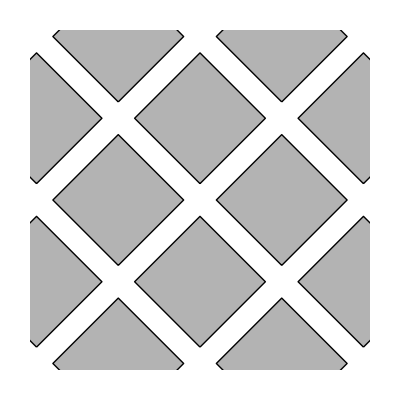
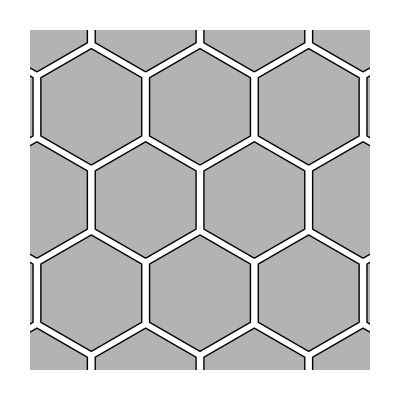
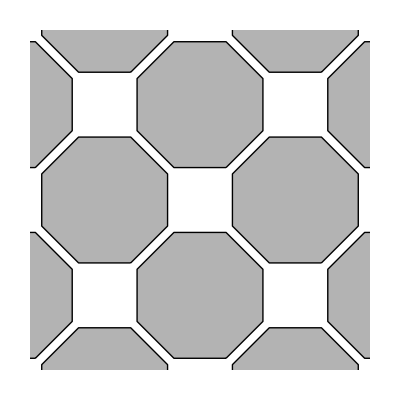
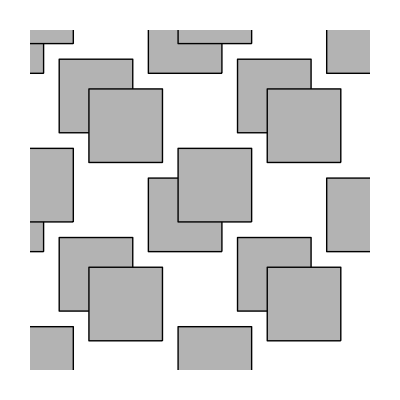
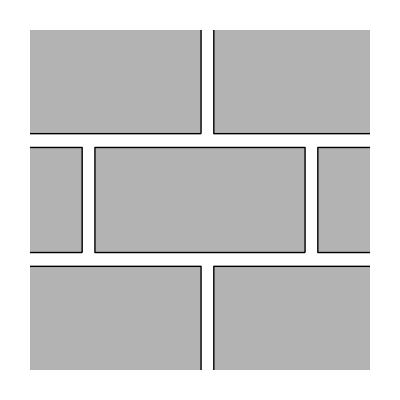
```mathematica
dtShapeArray[]:=
DynamicModule[{
colList={5,5,5,5,5},
spaceH=.4,
spaceV=.4,
offsetH=0,
offsetV=0,
offsetHList={},
offsetVList={},
width=.4,
height=.4,
origin={0,0},
clickPtScaled,
plotrange=1,
plotrangeList,
style,shapeStyle,space,shape=dtShapeStart,res=2,rotate=0,scaleAll=1,max={0,0}
},
Tooltip[Button[$dtIconShapeArray,

$dtMode="layer";
CreateDialog[
Pane[Column[{
Grid[{
{"List the\nnumber of rows\nfor each column.",Spacer[20],Show[-Graphics-,ImageSize->{Automatic,50}],Spacer[20],Show[-Graphics-,ImageSize->{Automatic,50}]},
{"","","{2,1,2}","","{2}"}
}],
InputField[Dynamic@colList,ImageSize->{340,30}],
Grid[{Button[Row[{#[[1]],"x",#[[2]]}],colList=Table[#[[2]],{n,#[[1]]}],ImageSize->{49,20},Appearance->"Palette"]&/@{{1,1},{1,5},{5,1},{5,5},{10,10},{5,10},{10,5}}},Spacings->{0,0}],
Spacer[{0,10}],
Panel@Dynamic@Grid[{
{EventHandler[MouseAppearance[
plotrangeList={0,0};
plotrange=1;
offsetHList=ReplacePart[Table[0,{Max@colList}],Table[n->offsetH,{n,1,Max@colList,2}]];
offsetVList=ReplacePart[Table[0,{Length@colList}],Table[n->offsetV,{n,1,Length@colList,2}]];
style=If[MemberQ[$dtShapeSymbols,$dtStyle[[$dtPn]][[1]]],$dtStyle[[$dtPn]],$dtDefaultStyle];
Dynamic[Graphics[Flatten@{
{EdgeForm[{CapForm["Butt"],style[[4]],Opacity[style[[5]]],AbsoluteThickness[style[[6]]],AbsoluteDashing[style[[7]]]}],Opacity[style[[3]]],style[[2]]},
Table[Polygon[scaleAll(#-{offsetHList[[y]],-offsetVList[[x]]}-{ spaceH*(Length[colList]-1),- spaceV*(Max[colList]-1)}/2)&/@Table[{(x-1) spaceH,-(y-1) spaceV}+{width,-height}{.5Sin[n],.5Cos[n]},{n,rotate*Pi/180,rotate*Pi/180+2Pi-Pi/res,Pi/res}]],{x,Length@colList},{y,Range[colList[[x]]]}]
},PlotRange->{-plotrange plotrangeList[[1]]+{-plotrange,plotrange},-plotrange plotrangeList[[2]]+{-plotrange,plotrange}},Background->LightGray,ImageSize->325]],
(* cursor *)
$dtCursorCanvas],
(* mouse events *)
"MouseUp":>(origin=plotrangeList),
"MouseDown":>(clickPtScaled=MousePosition["GraphicsScaled"]),
"MouseDragged":>(If[MousePosition["Graphics"]=!=None,
plotrangeList=origin+(MousePosition["GraphicsScaled"]-clickPtScaled)])
]},
{""},
{OpenerView[{"SHAPE",
Grid[{
{dtButtonStylePresets[]/."Preset"->"Style"},
{Row@{Pane["width ",50,Alignment->Right],
Slider[Dynamic@width,{0,1,$dtGridSize}],
Button["<",width=Round[width-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",width=Round[width+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@width,50]}},
{Row@{Pane["height ",50,Alignment->Right],
Slider[Dynamic@height,{0,1,$dtGridSize}],
Button["<",height=Round[height-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",height=Round[height+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@height,50]}},
{Row@{Pane["sides ",50,Alignment->Right],
Slider[Dynamic@res,{2,20,1}],
Button["<",res-=1,Appearance->"Palette"],
Button[">",res+=1,Appearance->"Palette"],
" ",Pane[Dynamic[2*res],50]}},
{Row@{Pane["rotate ",50,Alignment->Right],
Slider[Dynamic@rotate,{0,90,.5}],
Button["<",rotate-=.5,Appearance->"Palette"],
Button[">",rotate+=.5,Appearance->"Palette"],
" ",Pane[Dynamic@rotate,50]}}
}]
},False]},
{""},
{OpenerView[{"LAYOUT",
Grid[{
{Grid[Partition[{

Button[Show[-Graphics-,ImageSize->23],
width=.4;height=.4;spaceH=.4;
spaceV=.4;res=2;offsetH=0;offsetV=0;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
width=.4;height=.4;spaceH=.5;
spaceV=.25;res=2;offsetH=.25;offsetV=0;rotate=0,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
width=.375;height=.375;spaceH=.4Cos[30*Pi/180];
spaceV=.4-.2Sin[30*Pi/180];res=3;offsetH=.2Cos[30*Pi/180];offsetV=0;rotate=0,$dtButtonStyle],

Button[Show[-Graphics-,ImageSize->23],
width=.4;height=.4;spaceH=.3;
spaceV=.6Cos[30*Pi/180];res=3;offsetH=.3;offsetV=.2Cos[30*Pi/180];rotate=30,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
Block[{s},
s=((2Cos[67.5*Pi/180])+2(2Cos[67.5*Pi/180])Cos[45*Pi/180]);
width=.4;height=.4;
res=4;
spaceH=.2s;
spaceV=.2s;
offsetH=0;
offsetV=0;
rotate=22.5
],$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
Block[{s},
s=((2Cos[67.5*Pi/180])+(2Cos[67.5*Pi/180])Cos[45*Pi/180]);
width=.45;height=.45;spaceH=.5s;
spaceV=.25s;res=4;offsetH=.25s;offsetV=0;rotate=22.5
],$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
width=.35;height=.35;spaceH=.3;
spaceV=.3;res=2;offsetH=.2;offsetV=.2;rotate=45,$dtButtonStyle],
Button[Show[-Graphics-,ImageSize->23],
width=.5;height=.25;spaceH=.375;
spaceV=.2;res=2;offsetH=.185;offsetV=0;rotate=45,$dtButtonStyle]
},10,10,1,{}],Spacings->{0,0}]},
{""},
{Row@{Pane["scale all ",50,Alignment->Right],
Slider[Dynamic@scaleAll,{.1,2,.05}],
Button["<",scaleAll=Round[scaleAll-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",scaleAll=Round[scaleAll+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@scaleAll,50]}},
{Row@{Pane["space h ",50,Alignment->Right],
Slider[Dynamic@spaceH,{-1,1,$dtGridSize}],
Button["<",spaceH=Round[spaceH-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",spaceH=Round[spaceH+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@spaceH,50]}},
{Row@{Pane["space v ",50,Alignment->Right],
Slider[Dynamic@spaceV,{-1,1,$dtGridSize}],
Button["<",spaceV=Round[spaceV-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",spaceV=Round[spaceV+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@spaceV,50]}},
{Row@{Pane["offset h ",50,Alignment->Right],
Slider[Dynamic@offsetH,{-1,1,$dtGridSize}],
Button["<",offsetH=Round[offsetH-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",offsetH=Round[offsetH+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@offsetH,50]}},
{Row@{Pane["offset v ",50,Alignment->Right],
Slider[Dynamic@offsetV,{-1,1,$dtGridSize}],
Button["<",offsetV=Round[offsetV-=$dtGridSize,$dtGridSize],Appearance->"Palette"],
Button[">",offsetV=Round[offsetV+=$dtGridSize,$dtGridSize],Appearance->"Palette"],
" ",Pane[Dynamic@offsetV,50]}}
}]},False]}},Alignment->Left,Spacings->{0,0}],
Row@{Button["Cancel",DialogReturn[],ImageSize->100],
DefaultButton["Create shapes",
Do[
dtNewEmptyLayer[];
$dtP[[Length@$dtP]]=scaleAll(#-{offsetHList[[y]],-offsetVList[[x]]}-{ spaceH*(Length[colList]-1),- spaceV*(Max[colList]-1)}/2)&/@Table[{(x-1) spaceH,-(y-1) spaceV}+{width,-height}{.5Sin[n],.5Cos[n]},{n,rotate*Pi/180,rotate*Pi/180+2Pi-Pi/res,Pi/res}],
{x,Length@colList},{y,Range[colList[[x]]]}];$dtSelectedLayers=Range[(Length@$dtP-(colList/.List->Plus))+1,Length@$dtP];DialogReturn[],ImageSize->150]}
},Alignment->Center]],WindowTitle->"Shape array",Modal->True],

$dtButtonStyle],"Shape array"]
]
```

#### style button

```mathematica
dtStyle[]:=
DynamicModule[{},
Tooltip[Button[Style["Style",10,Black],

CreateDialog[
Column[{

Pane[
Dynamic[Style[
Switch[$dtStyle[[$dtPn]][[1]],
Text,
Row[{dtColor[],dtOpacity[],dtFont[],dtFontSize[],dtFontLineSpacing[],dtButtonStyleSetAllSelected[]}],
"Link",
Row[{dtColor[],dtLinkThickness[],dtLinkArrowForm[],dtLinkArrowSize[],dtButtonStyleSetAllSelected[]}],
$dtShapeSymbolsAlternates,
Switch[$dtStyle[[$dtPn]][[1]],
Point,
Row[{dtColor[],dtOpacity[],dtPointSize[],dtButtonStyleSetAllSelected[]}],
Line|BSplineCurve|BezierCurve,
Row[{dtEdgeColor[],dtEdgeOpacity[],dtLineThickness[],dtLineDashing[],dtButtonStyleSetAllSelected[]}],
"BSplineCurveArrow"|"BezierCurveArrow"|Arrow,
Row[{dtEdgeColor[],dtEdgeOpacity[],dtLineThickness[],dtLineDashing[],dtArrowSize[],dtArrowPlacement[],dtButtonStyleSetAllSelected[]}],
"BSplineFilledCurve",
Row[{dtColor[],dtOpacity[],dtEdgeColor[],dtEdgeOpacity[],dtLineThickness[],dtLineDashing[],dtButtonStyleSetAllSelected[]}],
"Markers",
Row[{dtColor[],dtOpacity[],dtEdgeColor[],dtEdgeOpacity[],dtLineThickness[],dtLineDashing[],dtMarkerType[],dtMarkerSize[]}],
"CompoundPath",
Row[{dtColor[],dtOpacity[],dtButtonStyleSetAllSelected[]}],
_,
Row[{dtColor[],dtOpacity[],dtEdgeColor[],dtEdgeOpacity[],dtLineThickness[],dtLineDashing[],dtGradientDirection[],dtGradientStart[],dtGradientEnd[],dtButtonStyleSetAllSelected[]}]
],
_,
Which[
MemberQ[{axo,axoExtrude},$dtStyle[[$dtPn]][[1]]],
Switch[$dtAxoSymbols[[$dtPn]],
Point,
Row[{dtColor[],dtOpacity[],dtPointSize[],dtButtonStyleSetAllSelected[]}],
Line|BSplineCurve|"BSplineCurveArrow"|BezierCurve|"BezierCurveArrow"|Arrow,
Row[{dtEdgeColor[],dtOpacity[],dtLineThickness[],dtLineDashing[],If[MemberQ[{Arrow,"BSplineCurveArrow","BezierCurveArrow"},$dtStyle[[$dtPn]][[1]]],dtArrowSize[]],dtButtonStyleSetAllSelected[]}],
"BSplineFilledCurve",
Row[{dtColor[],dtOpacity[],dtEdgeColor[],dtEdgeOpacity[],dtLineThickness[],dtLineDashing[],dtButtonStyleSetAllSelected[]}],
"Markers",
Row[{dtColor[],dtOpacity[],dtEdgeColor[],dtEdgeOpacity[],dtLineThickness[],dtLineDashing[],dtMarkerType[],dtMarkerSize[]}],
_,
Row[{dtColor[],dtOpacity[],dtEdgeColor[],dtEdgeOpacity[],dtLineThickness[],dtLineDashing[],dtGradientDirection[],dtGradientStart[],dtGradientEnd[],dtButtonStyleSetAllSelected[]}]
],
True,
{}
]],FontFamily->"Arial",10]/.Null->Sequence[]],Alignment->{Left,Center},ImageMargins->15],

DefaultButton["Done",DialogReturn[],ImageSize->100]
},Alignment->Center],WindowTitle->"Style"],ImageSize->{99,33},$dtButtonStyle],"Style current object"]
]
```

#### text tools

```mathematica
dtButtonTextTools[]:=
{
Tooltip[Dynamic@Button[$dtIconText,
dtNewEmptyLayer[];$dtStyle[[$dtPn]]=$dtDefaultText;$dtP[[$dtPn]]={{0,0}},$dtButtonStyle],
"Insert text"],


Block[{prevDefault},
Tooltip[Button[$dtIconTextDefaultStyle,
prevDefault=$dtDefaultText;
CreateDialog[Pane[Column[{
Grid[{
{"font",PopupMenu[Dynamic@$dtDefaultText[[5]],{"sans","serif"},Alignment->Center,ImageSize->{66,33},$dtButtonStyle],
"         size",PopupMenu[Dynamic@$dtDefaultText[[6]],Range[8,18],Alignment->Center,$dtButtonStyle]},
{"line space",PopupMenu[Dynamic@$dtDefaultText[[7]],Range[0,18],Alignment->Center,$dtButtonStyle],
"   opacity",PopupMenu[Dynamic@$dtDefaultText[[3]],Table[n,{n,0,1,.1}],Alignment->Center,$dtButtonStyle]},
{ColorSetter[Dynamic@$dtDefaultText[[2]],BaselinePosition->Scaled[.3]],Dynamic@InputField[Dynamic@$dtDefaultText[[4]],ImageSize->{230,33},BaselinePosition->Scaled[.3]],SpanFromLeft,SpanFromLeft,SpanFromLeft}
},Alignment->{{Right,Left}}],
DefaultButton[dtSetTextToDefaultText[prevDefault[[{2,3,5,6,7}]],$dtDefaultText[[{2,3,5,6,7}]]];DialogReturn[]]},Alignment->Center],ImageSize->300],WindowTitle->"Default text",Modal->True],
$dtButtonStyle],"Default text style"]
],

Tooltip[Button[$dtIconTextInsertNumbers,
If[CurrentValue["CommandKey"],
Do[If[MemberQ[$dtShapeSymbols,$dtStyle[[s]][[1]]],$dtStyle[[s]][[8]]="",Nothing],{s,$dtSelectedLayers}]
,
If[CurrentValue["OptionKey"],
Do[If[MemberQ[$dtShapeSymbols,$dtStyle[[s]][[1]]],$dtStyle[[s]][[8]]=ToString[s],Nothing],{s,$dtSelectedLayers}],
Do[If[MemberQ[$dtShapeSymbols,$dtStyle[[s]][[1]]]&&$dtStyle[[s]][[8]]==="",$dtStyle[[s]][[8]]=ToString[s]],{s,$dtSelectedLayers}]
]
],$dtButtonStyle],
"Insert object number in selected shapes.\nCommand-click to remove current number(s).\nOption-click to replace current number(s)."]
}
```

#### ungroup shape

```mathematica
dtUngroupShape[]:=
DynamicModule[{g,p},
Tooltip[Button[$dtIconUngroupShape,
dtSetUndo[];
If[$dtStyle[[$dtPn]][[1]]===graphics,
dtParseDrawGraphics[
$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Graphics"->_][[1]][[1]]]][[-1]][[1]],
$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Location"->_][[1]][[1]]]][[-1]],
$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Size"->_][[1]][[1]]]][[-1]],$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate"->_][[1]][[1]]]][[-1]]
],
Nothing],
$dtButtonStyle],"Ungroup shapes"]
]
```

### render

#### render

```mathematica
dtRender[]:=
DynamicModule[{temp,start,start3d,startRotate,clickPt,clickPtScaled,nearestPoint,nearestPointBeforeValue,nearestPointAfterValue,nearestDimension,nearestPointValue},
EventHandler[

(* render *)
MouseAppearance[
Dynamic@Graphics[{
dtRenderTemplate[],
dtRenderGrid[],
Style[dtRenderObject[],Magnification->(30/13)/$dtPlotrange],
If[$dt3dRotate,dtRenderAxoRotationRings[],Nothing],
If[!$dt3dRotate,dtRenderAxoOrientationVectors[],Nothing],
dtRenderPoints[],
dtRenderBezierHandles[],
dtRenderCenterMark[],
dtRenderSelectionHighlight[],
dtRenderPlanePoints[],
dtRenderObjectNumber[],
dtRenderCanvasDimensions[],
dtRenderZoom[]
},PlotRange->{- $dtPlotrangeList[[1]]+{-$dtPlotrange,$dtPlotrange},- $dtPlotrangeList[[2]]+{-$dtPlotrange,$dtPlotrange}},ImagePadding->None,ImageSize->$dtCanvasSize],
dtRenderCursors[],
dtRenderCursorsHotSpot[]],

(* handle mouse events *)
{
"MouseClicked":>dtMouseClicked[],
"MouseDown":>(
clickPt=$dtZoomStart=$dtZoomEnd=Round[MousePosition["Graphics"],$dtGridSize];
clickPtScaled=MousePosition["GraphicsScaled"];
If[$dtMode==="addPoint"&&MemberQ[$dtBezierSymbols,$dtStyle[[$dtPn]][[1]]],
(* create new layer if shape endpoints same *)
If[Length@$dtP[[$dtPn]]>5&&$dtP[[$dtPn]][[1]]===$dtP[[$dtPn]][[-1]],
dtNewEmptyLayer["SetMode"->False];$dtPn=Length@$dtP;$dtSelectedLayers={$dtPn}];
(* check for proper length before adding points *)
If[Length@$dtP[[$dtPn]]>2&&Mod[Length@$dtP[[$dtPn]]+1,3]≠0,$dtP[[$dtPn]]=Join[$dtP[[$dtPn]],{$dtP[[$dtPn]][[-1]]}]];
(* add points and handles *)
Do[AppendTo[$dtP[[$dtPn]],If[Round[$dtP[[$dtPn]][[1]],Max[$dtGridSize,.05]]===Round[clickPt,Max[$dtGridSize,.05]],$dtP[[$dtPn]][[1]],clickPt]],{
Which[
$dtP[[$dtPn]]==={},2,
Round[$dtP[[$dtPn]][[-2]],Max[$dtGridSize,.05]]===Round[clickPt,Max[$dtGridSize,.05]],0,
Round[$dtP[[$dtPn]][[1]],Max[$dtGridSize,.05]]===Round[clickPt,Max[$dtGridSize,.05]]&&Length[$dtP[[$dtPn]]]>2,2,
$dtP[[$dtPn]][[1]]===$dtP[[$dtPn]][[-1]]&&Length[$dtP[[$dtPn]]]>2,0,
True,3]
}],Nothing];
start=$dtP;start3d=$dtObjOpt;
startRotate=If[$dtStyle[[$dtPn]][[1]]===axo3dObject,
$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_]]],
$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],"AxisRotation"->_]]]
];
dtSetUndo[];
nearestPoint=If[$dtP[[$dtPn]]=!={},{Position[$dtP[[$dtPn]],Last@Nearest[$dtP[[$dtPn]],MousePosition["Graphics"]]][[1]]},{0}];
nearestPointValue=If[Flatten[nearestPoint][[1]]>0,
$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]],{0,0}];
nearestPointBeforeValue=If[Flatten[nearestPoint][[1]]>0,
Which[
Mod[nearestPoint,3]==={{0}},(* before handle *)
$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]],
Mod[nearestPoint+1,3]==={{0}},(* after handle *)
If[Flatten[nearestPoint][[1]]===2&&Mod[Length@$dtP[[$dtPn]]-1,3]===0,$dtP[[$dtPn]][[Length@$dtP[[$dtPn]]-1]],$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-2]]],
True,(* main point *)
If[Flatten[nearestPoint][[1]]===1&&$dtP[[$dtPn]][[1]]===$dtP[[$dtPn]][[-1]]&&Length@$dtP[[$dtPn]]>2,$dtP[[$dtPn]][[-2]],If[Flatten[nearestPoint][[1]]===1,{0,0},$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-1]]]]
],{0,0}];
nearestPointAfterValue=If[Flatten[nearestPoint][[1]]<Length@$dtP[[$dtPn]],
Which[
Mod[nearestPoint,3]==={{0}},(* before handle *)
If[Flatten[nearestPoint][[1]]+1===Length@$dtP[[$dtPn]],$dtP[[$dtPn]][[2]],$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+2]]],
Mod[nearestPoint+1,3]==={{0}},(* after handle *)
$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]],
True,(* main point *)
$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+1]]
],{0,0}];
nearestDimension={Position[$dtCanvasDimensions,Last[Nearest[$dtCanvasDimensions,MousePosition["Graphics"]]]][[1]]};
),
"MouseUp":>(
Switch[$dtMode,
"zoom",
Which[
CurrentValue["OptionKey"],
$dtPlotrange=Min[$dtPlotrange+=.5$dtPlotrange,4];
$dtPlotrangeList=$dtOrigin=$dtZoomStart=$dtZoomEnd=-MousePosition["Graphics"],
CurrentValue["CommandKey"],
$dtPlotrange=$dtCanvasSize/325;
$dtPlotrangeList=$dtOrigin=$dtZoomStart=$dtZoomEnd=MousePosition["Graphics"],
True,
If[$dtZoomEnd===$dtZoomStart,
$dtPlotrange=Max[$dtPlotrange-=.5$dtPlotrange,.1],
$dtPlotrange=Max[.5Max[Abs[$dtZoomEnd-$dtZoomStart]],.1];
];
$dtPlotrangeList=$dtOrigin=-dtFindCenter[{$dtZoomStart,$dtZoomEnd}]
];
$dtZoomStart=$dtZoomEnd,
_,
$dtOrigin=$dtPlotrangeList;
$dtBezierAfterHandleHidden=False
]),
"MouseDragged":>dtMouseDragged[clickPt,clickPtScaled,start,nearestPoint,nearestPointValue,nearestPointBeforeValue,nearestPointAfterValue,nearestDimension,start3d,startRotate]
}]
]
```

#### arrow

```mathematica
dtRenderArrow[func_,shearFunc_,n_]:=
Flatten@{Arrow[Table[func[shearFunc[p]],{p,$dtP[[n]]}]],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],Arrow[Table[func[p],{p,$dtP[[n]]}]]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],Arrow[Table[func[p],{p,$dtP[[n]]}]]},
True,{}]}
```

#### axis/grid

```mathematica
dtRenderGrid[]:=
DynamicModule[{side,gridStep=2},If[MemberQ[{"XY","YZ"},$dtShow3dGrid]&&MemberQ[$dt3dSymbols,$dtStyle[[$dtPn]][[1]]]&&$dtMode=!="CanvasDimensions",
side=If[$dtShow3dGrid==="XY","Top","Right"];
Flatten[{
(* 3d grid *)
If[$dtGridSize>.01&&$dtShowGrid,
{If[$dtCanvasBackgroundColor===White,Darker[$dtCanvasBackgroundColor,.1],Lighter@$dtCanvasBackgroundColor],
(* -1 to 1 grid *)
axo[{Table[Line[{{n,-1},{n,1}}],{n,-1+Mod[2$dtPlotrange,$dtGridSize],1,2$dtGridSize}],
Table[Line[{{-1,n},{1,n}}],{n,-1+Mod[2$dtPlotrange,$dtGridSize],1,2$dtGridSize}]},"Direction"->side,"Tilt"->$tilt,"Turn"->$turn]
},{}],
(* box *)
Opacity[1,Darker[$dtCanvasBackgroundColor,.15]],
axo[{Line[{{0,-2$dtPlotrange},{0,2$dtPlotrange}}],
Line[{{-2$dtPlotrange,0},{2$dtPlotrange,0}}],
Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}]},"Direction"->side,"Tilt"->$tilt,"Turn"->$turn],
(* axis *)
$dt3dAxisXColor,axo[Line[{{0,0},{1.25,0}}],"Direction"->"Left","Tilt"->$tilt,"Turn"->$turn],
$dt3dAxisYColor,axo[Line[{{0,0},{-1.25,0}}],"Direction"->"Right","Tilt"->$tilt,"Turn"->$turn],
$dt3dAxisZColor,axo[Line[{{0,0},{0,1.25}}],"Direction"->"Right","Tilt"->$tilt,"Turn"->$turn],
(* text *)
$dt3dAxisXColor,axo[Text["x",{1.25,0},{-3,0}],"Direction"->"Left","Tilt"->$tilt,"Turn"->$turn],
$dt3dAxisYColor,axo[Text["y",{-1.25,0},{2,0}],"Direction"->"Right","Tilt"->$tilt,"Turn"->$turn],
$dt3dAxisZColor,axo[Text["z",{0,1.25},{0,-1}],"Direction"->"Right","Tilt"->$tilt,"Turn"->$turn],
Opacity[1,Darker[$dtCanvasBackgroundColor,.3]],
axo[Text["{1,-1,}",{1,-1},{-1,1}],"Direction"->side,"Tilt"->$tilt,"Turn"->$turn],
axo[Text["{-1, -1}",{1,1},{-1,-1}],"Direction"->side,"Tilt"->$tilt,"Turn"->$turn],
axo[Text["{1, 1}",{-1,-1},{1,1}],"Direction"->side,"Tilt"->$tilt,"Turn"->$turn],
axo[Text["{-1, 1}",{-1,1},{1,-1}],"Direction"->side,"Tilt"->$tilt,"Turn"->$turn]
}],
(* 2d grid *)
Flatten[{
(* grid *)
If[$dtGridSize>.01&&$dtShowGrid,
{If[$dtCanvasBackgroundColor===White,Darker[$dtCanvasBackgroundColor,.1],Lighter@$dtCanvasBackgroundColor],
Table[Line[Round[#- $dtOrigin&/@{{n,-gridStep $dtPlotrange},{n,gridStep $dtPlotrange}},gridStep $dtGridSize]],{n,-gridStep $dtPlotrange,gridStep $dtPlotrange,gridStep $dtGridSize}],
Table[Line[Round[#- $dtOrigin&/@{{-gridStep $dtPlotrange,n},{gridStep $dtPlotrange,n}},gridStep $dtGridSize]],{n,-gridStep $dtPlotrange,gridStep $dtPlotrange,gridStep $dtGridSize}]
}],
(* axis *)
Opacity[1,Darker[$dtCanvasBackgroundColor,.15]],Line[{{0,-2$dtPlotrange},{0,2$dtPlotrange}}],
Line[{{-2$dtPlotrange,0},{2$dtPlotrange,0}}],
Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}],
(* text *)
Opacity[1,Darker[$dtCanvasBackgroundColor,.3]],
Text["{1, 1}",{1,1},{-1,-1}],
Text["{1, -1}",{1,-1},{-1,1}],
Text["{-1, 1}",{-1,1},{1,-1}],
Text["{-1, -1}",{-1,-1},{1,1}]
}]]
]
```

#### axo

```mathematica
dtRenderAxo[n_]:=
Flatten@{Switch[$dtAxoSymbols[[n]],
Arrow|"BSplineCurveArrow"|"BezierCurveArrow",
{Arrowheads[Switch[$dtStyle[[n]][[10]],"Start",{{-$dtStyle[[n]][[9]],0}},"Both",{-$dtStyle[[n]][[9]],$dtStyle[[n]][[9]]},_,$dtStyle[[n]][[9]]]],CapForm[If[$dtStyle[[n]][[7]]==={},"Round","Butt"]],JoinForm["Round"],$dtStyle[[n]][[4]],Opacity[$dtStyle[[n]][[5]]],AbsoluteThickness[Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]],MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]],True,$dtStyle[[n]][[6]]]],AbsoluteDashing[$dtStyle[[n]][[7]]]},
Line|BSplineCurve|BezierCurve,
{CapForm[If[$dtStyle[[n]][[7]]==={},"Round","Butt"]],JoinForm["Round"],$dtStyle[[n]][[4]],Opacity[$dtStyle[[n]][[5]]],AbsoluteThickness[Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]],MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]],True,$dtStyle[[n]][[6]]]],AbsoluteDashing[$dtStyle[[n]][[7]]]},
_,(* Polygon, Markers *)
{Opacity[$dtStyle[[n]][[3]]],
$dtStyle[[n]][[2]],
EdgeForm[{CapForm[If[$dtStyle[[n]][[7]]==={},"Round","Butt"]],JoinForm["Round"],$dtStyle[[n]][[4]],Opacity[$dtStyle[[n]][[5]]],AbsoluteThickness[Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]],MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]],True,$dtStyle[[n]][[6]]]],AbsoluteDashing[$dtStyle[[n]][[7]]]}]}
],
Switch[$dtAxoSymbols[[n]],
BSplineCurve,
axo[BSplineCurve[$dtP[[n]],SplineClosed->False],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[n]]],
"BSplineCurveArrow",
axo[Arrow[BSplineCurve[$dtP[[n]],SplineClosed->False]],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[n]]],
"BSplineFilledCurve",
axo[FilledCurve@BSplineCurve[$dtP[[n]],SplineClosed->True],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[n]]],
BezierCurve,
axo[BezierCurve[$dtP[[n]]],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[n]]],
"BezierCurveArrow",
axo[Arrow[BezierCurve[$dtP[[n]]]],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[n]]],
"BezierFilledCurve",
axo[FilledCurve@BezierCurve[$dtP[[n]]],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[n]]],
"Markers",
Table[axo[dtDrawMarkers[{n2},n],
"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[n]]],{n2,$dtP[[n]]}],
_,
axo[$dtAxoSymbols[[n]][$dtP[[n]]],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[n]]]]
}
```

#### axo extrude

```mathematica
dtRenderAxoExtrude[n_]:=
{Opacity[$dtStyle[[n]][[3]]],
$dtStyle[[n]][[2]],
EdgeForm[{CapForm[If[$dtStyle[[n]][[7]]==={},"Round","Butt"]],JoinForm["Round"],$dtStyle[[n]][[4]],Opacity[$dtStyle[[n]][[5]]],AbsoluteThickness[Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]],MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]],True,$dtStyle[[n]][[6]]]],AbsoluteDashing[$dtStyle[[n]][[7]]]}],axoExtrude[Polygon[$dtP[[n]]],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[n]]]}
```

#### axo orientation vectors

```mathematica
dtRenderAxoOrientationVectors[]:=
DynamicModule[{moveAxisThick=2},
If[MemberQ[$dt3dSymbols,$dtStyle[[$dtPn]][[1]]]&&$dtShow3dVectors,
{Arrowheads[Medium],
(* x axis *)
If[$dtStyle[[$dtPn]][[1]]=!=axo3dObject,
EventHandler[{$dt3dAxisXColor,AbsoluteThickness[If[$dt3dMoveAxis==="x"&&!$dt3dRotate,moveAxisThick,1]],
If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],
axo[Arrow[{{0,0},{0,-.3}}],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]],
"RotateOrder"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],
"Direction"->"Top",
"AxisRotation"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisRotation"->_][[1]][[1]]]][[-1]],
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]],
axo[Arrow[{{0,0},{0,-.3}}],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]],"Direction"->"Top",
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]
]},{"MouseDown":>($dt3dMoveAxis="x";$dt3dRotate=False)}],
EventHandler[{$dt3dAxisXColor,AbsoluteThickness[If[$dt3dMoveAxis==="x"&&!$dt3dRotate,moveAxisThick,1]],
If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],
axo[Arrow[{{0,0},{0,-.3}}],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]],
"RotateOrder"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],
"Direction"->"Top",
"AxisRotation"->{
{$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[3]]/Degree,"Top"},
{$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[2]]/Degree,"Right"},
{$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[1]]/Degree,"Left"}
},
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]],
axo[Arrow[{{0,0},{0,-.3}}],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]],"Direction"->"Top",
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]
]},{"MouseDown":>($dt3dMoveAxis="x";!$dt3dRotate)}]],
(* y axis *)
If[$dtStyle[[$dtPn]][[1]]=!=axo3dObject,
EventHandler[{$dt3dAxisYColor,AbsoluteThickness[If[$dt3dMoveAxis==="y"&&!$dt3dRotate,moveAxisThick,1]],
If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],
axo[Arrow[{{0,0},{-.3,0}}],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]],
"RotateOrder"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],
"Direction"->"Right",
"AxisRotation"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisRotation"->_][[1]][[1]]]][[-1]],
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]],
axo[Arrow[{{0,0},{-.3,0}}],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]],"Direction"->"Right",
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]
]},{"MouseDown":>($dt3dMoveAxis="y";$dt3dRotate=False)}],
EventHandler[{$dt3dAxisYColor,AbsoluteThickness[If[$dt3dMoveAxis==="y"&&!$dt3dRotate,moveAxisThick,1]],
If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],
axo[Arrow[{{0,0},{-.3,0}}],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]],
"RotateOrder"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],
"Direction"->"Right",
"AxisRotation"->{
{$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[3]]/Degree,"Top"},
{$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[2]]/Degree,"Right"},
{$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[1]]/Degree,"Left"}
},
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]],
axo[Arrow[{{0,0},{-.3,0}}],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]],"Direction"->"Right",
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]
]},{"MouseDown":>($dt3dMoveAxis="y";$dt3dRotate=False)}]],
(* z axis *)
If[$dtStyle[[$dtPn]][[1]]=!=axo3dObject,
EventHandler[{$dt3dAxisZColor,AbsoluteThickness[If[$dt3dMoveAxis==="z"&&!$dt3dRotate,moveAxisThick,1]],
If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],
axo[Arrow[{{0,0},{0,.3}}],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]],
"RotateOrder"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],
"Direction"->"Right",
"AxisRotation"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisRotation"->_][[1]][[1]]]][[-1]],
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]],
axo[Arrow[{{0,0},{0,.3}}],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]],"Direction"->"Right",
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]
]},{"MouseDown":>($dt3dMoveAxis="z";$dt3dRotate=False)}],
EventHandler[{$dt3dAxisZColor,AbsoluteThickness[If[$dt3dMoveAxis==="z"&&!$dt3dRotate,moveAxisThick,1]],
If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],
axo[Arrow[{{0,0},{0,.3}}],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]],
"RotateOrder"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],
"Direction"->"Right",
"AxisRotation"->{
{$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[3]]/Degree,"Top"},
{$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[2]]/Degree,"Right"},
{$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[1]]/Degree,"Left"}
},
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]],
axo[Arrow[{{0,0},{0,.3}}],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]],"Direction"->"Right",
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]
]},{"MouseDown":>($dt3dMoveAxis="z";$dt3dRotate=False)}]]},
{}]
]
```

#### axo rotation rings

```mathematica
(* NOTE: rotation rings must have AbsoluteThickness[1/n] (n must be less than 1) or they thicken when rotated (not sure why) *)
```

```mathematica
dtRenderAxoRotationRings[]:=
DynamicModule[{dash={2,2},size},
If[MemberQ[$dt3dSymbols,$dtStyle[[$dtPn]][[1]]]&&$dtShow3dRings,
size=If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],1,.5];
{(* boundary *)
GrayLevel[.7],
axo[Circle[{0,0},size],"Distort"->False,"Tilt"->$tilt,"Turn"->$turn,"AxisLocation"->If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],{0,0,0},$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]][[-1]]],
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]],
(* x axis *)
If[$dtStyle[[$dtPn]][[1]]===axo3dObject,
EventHandler[{$dt3dAxisXColor,CapForm["Butt"],AbsoluteThickness[1/.99],AbsoluteDashing[If[$dt3dMoveAxis==="x"&&$dt3dRotate===True,{},dash]],axo[{Circle[{0,0},size],Line[size{{-1,0},{-.8,0}}],Line[size{{-.1,0},{.1,0}}],Line[size{{.8,0},{1,0}}]},"Tilt"->$tilt,"Turn"->$turn,"AxisLocation"->If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],{0,0,0},$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]][[-1]]],
"RotateOrder"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],
"Direction"->"Right",
"AxisRotation"->{
{$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[3]]/Degree,"Top"},
{$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[2]]/Degree,"Right"},
{If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]]==="zyx",0,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[1]]/Degree],"Left"}
},
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]},{"MouseDown":>($dt3dMoveAxis="x";$dt3dRotate=True)}],
EventHandler[{$dt3dAxisXColor,CapForm["Butt"],AbsoluteThickness[1/.99],
AbsoluteDashing[If[$dt3dMoveAxis==="x"&&$dt3dRotate===True,{},dash]],
axo[{Circle[{0,0},size],Line[size{{-1,0},{-.8,0}}],Line[size{{-.1,0},{.1,0}}],Line[size{{.8,0},{1,0}}]},"Tilt"->$tilt,"Turn"->$turn,"AxisLocation"->If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],{0,0,0},$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]][[-1]]],
"RotateOrder"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],
"Direction"->"Right",
"AxisRotation"->If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]]==="zyx",
ReplacePart[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisRotation"->_][[1]][[1]]]][[-1]],{3->{0,"Left"}}],
$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisRotation"->_][[1]][[1]]]][[-1]]
],
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]},{"MouseDown":>($dt3dMoveAxis="x";$dt3dRotate=True)}]],
(* y axis *)
If[$dtStyle[[$dtPn]][[1]]===axo3dObject,
EventHandler[{$dt3dAxisYColor,CapForm["Butt"],AbsoluteThickness[1/.99],AbsoluteDashing[If[$dt3dMoveAxis==="y"&&$dt3dRotate===True,{},dash]],axo[{Circle[{0,0},size],Line[size{{-1,0},{-.8,0}}],Line[size{{-.1,0},{.1,0}}],Line[size{{.8,0},{1,0}}]},"Tilt"->$tilt,"Turn"->$turn,"AxisLocation"->If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],{0,0,0},$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]][[-1]]],
"RotateOrder"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],
"Direction"->"Left",
"AxisRotation"->{
{$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[3]]/Degree,"Top"},
{If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]]==="zxy",0,$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[2]]/Degree],"Right"},
{$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]][[1]]/Degree,"Left"}
},
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]},{"MouseDown":>($dt3dMoveAxis="y";$dt3dRotate=True)}],
EventHandler[{$dt3dAxisYColor,CapForm["Butt"],AbsoluteThickness[1/.99],AbsoluteDashing[If[$dt3dMoveAxis==="y"&&$dt3dRotate===True,{},dash]],axo[{Circle[{0,0},size],Line[size{{-1,0},{-.8,0}}],Line[size{{-.1,0},{.1,0}}],Line[size{{.8,0},{1,0}}]},"Tilt"->$tilt,"Turn"->$turn,"AxisLocation"->If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],{0,0,0},$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]][[-1]]],
"RotateOrder"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],
"Direction"->"Left",
"AxisRotation"->If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]]==="zxy",
ReplacePart[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisRotation"->_][[1]][[1]]]][[-1]],{2->{0,"Right"}}],
$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisRotation"->_][[1]][[1]]]][[-1]]
],
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]},{"MouseDown":>($dt3dMoveAxis="y";$dt3dRotate=True)}]],
(* z axis *)
If[$dtStyle[[$dtPn]][[1]]===axo3dObject,
EventHandler[{$dt3dAxisZColor,CapForm["Butt"],AbsoluteThickness[1/.99],AbsoluteDashing[If[$dt3dMoveAxis==="z"&&$dt3dRotate===True,{},dash]],axo[{Circle[{0,0},size],Line[size{{-1,0},{-.8,0}}],Line[size{{-.1,0},{.1,0}}],Line[size{{.8,0},{1,0}}]},"Tilt"->$tilt,"Turn"->$turn,"AxisLocation"->If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],{0,0,0},$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]][[-1]]],
"RotateOrder"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],
"Direction"->"Top",
"AxisRotation"->{{$dtObjOpt[[$dtPn]][[Flatten[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_]]]][[1]][[-1]][[3]]/Degree,"Top"},{0,"Right"},{0,"Left"}},
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]},{"MouseDown":>($dt3dMoveAxis="z";$dt3dRotate=True)}],
EventHandler[{$dt3dAxisZColor,CapForm["Butt"],AbsoluteThickness[1/.99],AbsoluteDashing[If[$dt3dMoveAxis==="z"&&$dt3dRotate===True,{},dash]],axo[{Circle[{0,0},size],Line[size{{-1,0},{-.8,0}}],Line[size{{-.1,0},{.1,0}}],Line[size{{.8,0},{1,0}}]},"Tilt"->$tilt,"Turn"->$turn,"AxisLocation"->If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],{0,0,0},$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisLocation"->_][[1]][[1]]]][[-1]]],
"RotateOrder"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_][[1]][[1]]]][[-1]],
"Direction"->"Top",
"AxisRotation"->ReplacePart[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"AxisRotation"->_][[1]][[1]]]][[-1]],{2->{0,"Right"},3->{0,"Left"}}],
"MoveBeforeRotate"->$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]]]},{"MouseDown":>($dt3dMoveAxis="z";$dt3dRotate=True)}]]},
{}]
]
```

#### bezierCurve

```mathematica
dtRenderBezierCurve[func_,shearFunc_,n_]:=
If[Length@$dtP[[n]]<4,{},
Flatten@{BezierCurve[Table[func[shearFunc[p]],{p,$dtP[[n]][[1;;3IntegerPart[Length[$dtP[[n]]]/3]+1]]}]],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],BezierCurve[Table[func[shearFunc[p]],{p,$dtP[[n]][[1;;3IntegerPart[Length[$dtP[[n]]]/3]+1]]}]]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],BezierCurve[Table[func[shearFunc[p]],{p,$dtP[[n]][[1;;3IntegerPart[Length[$dtP[[n]]]/3]+1]]}]]},
True,{}]}
]
```

#### bezierCurveArrow

```mathematica
dtRenderBezierCurveArrow[func_,shearFunc_,n_]:=
If[Length@$dtP[[n]]<4,{},
Flatten@{Arrow[BezierCurve[Table[func[shearFunc[p]],{p,$dtP[[n]][[1;;3IntegerPart[Length[$dtP[[n]]]/3]+1]]}]]],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],BezierCurve[Table[func[shearFunc[p]],{p,$dtP[[n]][[1;;3IntegerPart[Length[$dtP[[n]]]/3]+1]]}]]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],BezierCurve[Table[func[shearFunc[p]],{p,$dtP[[n]][[1;;3IntegerPart[Length[$dtP[[n]]]/3]+1]]}]]},
True,{}]}
]
```

#### bezierFilledCurve

```mathematica
dtRenderBezierFilledCurve[func_,shearFunc_,n_]:=
Block[{funcPts},
If[Length@$dtP[[n]]<4,{},
Flatten@{If[$dtGradients[[n]][[1]]=!=None,
funcPts=(Table[func[shearFunc[p]],{p,$dtP[[n]][[1;;3IntegerPart[Length[$dtP[[n]]]/3]+1]]}]);
FilledCurve[{BezierCurve[funcPts]},VertexTextureCoordinates->Partition[Riffle[Rescale[Table[First@func[shearFunc[p]],{p,funcPts}]],Rescale[Table[Last@func[shearFunc[p]],{p,funcPts}]]],2]],
FilledCurve[{BezierCurve[Table[func[shearFunc[p]],{p,$dtP[[n]][[1;;3IntegerPart[Length[$dtP[[n]]]/3]+1]]}]]}]
],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],BezierCurve[Table[func[shearFunc[p]],{p,Join[$dtP[[n]][[1;;3IntegerPart[Length[$dtP[[n]]]/3]+1]],{$dtP[[n]][[1]]}]}]]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],BezierCurve[Table[func[shearFunc[p]],{p,Join[$dtP[[n]][[1;;3IntegerPart[Length[$dtP[[n]]]/3]+1]],{$dtP[[n]][[1]]}]}]]},
True,{}]}
]]
```

#### bezierHandles

```mathematica
dtRenderBezierHandles[]:=
Table[If[Length@$dtP[[s]]>1&&$dtP[[s]]=!={},
If[MemberQ[$dtBezierSymbols,$dtStyle[[s]][[1]]]&&MemberQ[{"point","addPoint","splitPoint"},$dtMode],
Flatten[{Gray,
Table[Line[{$dtP[[s]][[n-1]],$dtP[[s]][[n]]}],{n,2,Length@$dtP[[s]],3}],
Table[Line[{$dtP[[s]][[n-1]],$dtP[[s]][[n]]}],{n,4,Length@$dtP[[s]],3}]
}]]],
{s,{$dtPn}}]
```

#### BSplineCurve

```mathematica
dtRenderBSplineCurve[func_,shearFunc_,n_]:=
If[Length@$dtP[[n]]<3,
Flatten@{Line[Table[func[shearFunc[p]],{p,$dtP[[n]]}]],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],Line[Table[func[shearFunc[p]],{p,$dtP[[n]]}]]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],Line[Table[func[shearFunc[p]],{p,$dtP[[n]]}]]},
True,{}]},
Flatten@{BSplineCurve[Table[func[shearFunc[p]],{p,$dtP[[n]]}],SplineDegree->$dtSplineDegree],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],BSplineCurve[Table[func[shearFunc[p]],{p,$dtP[[n]]}],SplineClosed->False,SplineDegree->$dtSplineDegree]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],BSplineCurve[Table[func[shearFunc[p]],{p,$dtP[[n]]}],SplineClosed->False,SplineDegree->$dtSplineDegree]},
True,{}]}
]
```

#### BSplineCurveArrow

```mathematica
dtRenderBSplineCurveArrow[func_,shearFunc_,n_]:=
If[Length@$dtP[[n]]<3,
Flatten@{Line[Table[func[shearFunc[p]],{p,$dtP[[n]]}]],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],Line[Table[func[shearFunc[p]],{p,$dtP[[n]]}]]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],Line[Table[func[shearFunc[p]],{p,$dtP[[n]]}]]},
True,{}]},
Flatten@{Arrow[BSplineCurve[Table[func[shearFunc[p]],{p,$dtP[[n]]}],SplineDegree->$dtSplineDegree]],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],BSplineCurve[Table[func[shearFunc[p]],{p,$dtP[[n]]}],SplineClosed->False,SplineDegree->$dtSplineDegree]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],BSplineCurve[Table[func[shearFunc[p]],{p,$dtP[[n]]}],SplineClosed->False,SplineDegree->$dtSplineDegree]},
True,{}]}
]
```

#### BSplineFilledCurve

```mathematica
dtRenderBSplineFilledCurve[func_,shearFunc_,n_]:=
(* BSplineCurve does not support textures so gradients will not work *)
If[Length@$dtP[[n]]<3,
Flatten@{Polygon[Table[func[shearFunc[p]],{p,$dtP[[n]]}]],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],Line[Table[func[shearFunc[p]],{p,Join[$dtP[[n]],{$dtP[[n]][[1]]}]}]]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],Line[Table[func[shearFunc[p]],{p,Join[$dtP[[n]],{$dtP[[n]][[1]]}]}]]},
True,{}]},
Flatten@{FilledCurve[{BSplineCurve[Table[func[shearFunc[p]],{p,$dtP[[n]]}],SplineClosed->True,SplineDegree->$dtSplineDegree]}],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],BSplineCurve[Table[func[shearFunc[p]],{p,$dtP[[n]]}],SplineClosed->True,SplineDegree->$dtSplineDegree]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],BSplineCurve[Table[func[shearFunc[p]],{p,$dtP[[n]]}],SplineClosed->True,SplineDegree->$dtSplineDegree]},
True,{}]}
]
```

#### canvas dimensions

```mathematica
(* this must be a line not a rectangle so mousedown is passed to 3d orientation axis *)
dtRenderCanvasDimensions[]:=
If[$dtMode==="canvasDimensions",
{$dtCanvasDimensionColor,Line[{$dtCanvasDimensions[[1]],{$dtCanvasDimensions[[2]][[1]],$dtCanvasDimensions[[1]][[2]]},$dtCanvasDimensions[[2]],{$dtCanvasDimensions[[1]][[1]],$dtCanvasDimensions[[2]][[2]]},$dtCanvasDimensions[[1]]}],EdgeForm[$dtCanvasDimensionColor],White,Table[Disk[n,Offset[4]],{n,$dtCanvasDimensions}]},

{$dtCanvasDimensionColor,Line[{$dtCanvasDimensions[[1]],{$dtCanvasDimensions[[2]][[1]],$dtCanvasDimensions[[1]][[2]]},$dtCanvasDimensions[[2]],{$dtCanvasDimensions[[1]][[1]],$dtCanvasDimensions[[2]][[2]]},$dtCanvasDimensions[[1]]}]}
]
```

#### center mark

```mathematica
dtRenderCenterMark[]:=
DynamicModule[{temp},
If[$dtP[[$dtPn]]=!={}&&MemberQ[$dtShapeSymbols,$dtStyle[[$dtPn]][[1]]],
{GrayLevel[0,.3],temp=dtFindCenter@$dtP[[$dtPn]];Line[{Offset[{-6,0},temp],Offset[{6,0},temp]}],Line[{{Offset[{0,-6},temp],Offset[{0,6},temp]}}]},{}
]
]
```

#### CompoundPath

```mathematica
dtRenderCompoundPath[func_,shearFunc_,n_]:=
If[Length@$dtP[[n]]<3,
Flatten@{Line[Table[func[shearFunc[p]],{p,$dtP[[n]]}]],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],Line[Table[func[shearFunc[p]],{p,$dtP[[n]]}]]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],Line[Table[func[shearFunc[p]],{p,$dtP[[n]]}]]},
True,{}]},
Flatten@{FilledCurve[Table[{Line[Join[Table[func[shearFunc[p]],{p,$dtP[[n2]]}],{func[shearFunc[$dtP[[n2]][[1]]]]}]]},{n2,Flatten@Table[If[$dtStyle[[n3]][[1]]==="CompoundPath",n3,{}],{n3,Length@$dtStyle}]}]],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],BSplineCurve[Table[func[shearFunc[p]],{p,$dtP[[n]]}],SplineClosed->True,SplineDegree->$dtSplineDegree]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],BSplineCurve[Table[func[shearFunc[p]],{p,$dtP[[n]]}],SplineClosed->True,SplineDegree->$dtSplineDegree]},
True,{}]}
]
```

#### cursors

```mathematica
dtRenderCursors[]:=
Dynamic@Switch[$dtMode,
"canvas",$dtCursorCanvas,
"text",$dtCursorText,
"canvasDimensions",$dtCursorCanvasDimension,
"point",$dtCursorPoint,
"addPoint"|"splitPoint",$dtCursorDraw,
"zoom",$dtIconZoom,
_,$dtCursorSelect
]

(* hot spot will not change; drew layer cursor so hot spot in middle *)
(*Dynamic@Switch[$dtMode,"layer",Scaled[{.1,.9}],_,Scaled[{.5,.5}]]*)
dtRenderCursorsHotSpot[]:=Scaled[{.5,.5}]
```

#### curve style

```mathematica
dtRenderCurveStyle[n_]:=
{If[MemberQ[{"BezierCurveArrow","BSplineCurveArrow"},$dtStyle[[n]][[1]]],
Arrowheads[Switch[$dtStyle[[n]][[10]],
"Start",Switch[$dtStyle[[n]][[9]],
"SmallMedium",{$dtArrowSmallMediumStart},
"MediumLarge",{$dtArrowMediumLargeStart},
"ExtraLarge",{$dtArrowExtraLargeStart},
_,{{-$dtStyle[[n]][[9]],0}}],
"End",Switch[$dtStyle[[n]][[9]],
"SmallMedium",{$dtArrowSmallMediumEnd},
"MediumLarge",{$dtArrowMediumLargeEnd},
"ExtraLarge",{$dtArrowExtraLargeEnd},
_,$dtStyle[[n]][[9]]],
"Both",Switch[$dtStyle[[n]][[9]],
"SmallMedium",{$dtArrowSmallMediumStart,$dtArrowSmallMediumEnd},
"MediumLarge",{$dtArrowMediumLargeStart,$dtArrowMediumLargeEnd},
"ExtraLarge",{$dtArrowExtraLargeStart,$dtArrowExtraLargeEnd},
_,{-$dtStyle[[n]][[9]],$dtStyle[[n]][[9]]}],
_,(* none *){}]],
{}],CapForm[If[$dtStyle[[n]][[7]]==={},"Round","Butt"]],$dtStyle[[n]][[4]],Opacity[$dtStyle[[n]][[5]]],AbsoluteThickness[Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]]+2,MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]]+6,True,$dtStyle[[n]][[6]]]],AbsoluteDashing[If[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],{},$dtStyle[[n]][[7]]]]}
```

#### filled style

```mathematica
dtRenderFilledStyle[n_]:=
{EdgeForm[{CapForm[If[$dtStyle[[n]][[7]]==={},"Round","Butt"]],$dtStyle[[n]][[4]],Opacity[$dtStyle[[n]][[5]]],AbsoluteThickness[Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]]+2,MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]]+6,True,$dtStyle[[n]][[6]]]],AbsoluteDashing[If[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],{},$dtStyle[[n]][[7]]]]}],
If[$dtGradients[[n]][[1]]=!=None,
Switch[$dtGradients[[n]][[1]],
Left,
Texture[Graphics[Flatten@{Thickness[1],Line[Table[{a,.5},{a,0,1,1/(Length[$dtGradients[[n]][[2]]]-1)}],VertexColors->$dtGradients[[n]][[2]]]},ImagePadding->0,PlotRangePadding->0]],
Right,
Texture[Graphics[Flatten@{Thickness[1],Line[Table[{-a,.5},{a,0,1,1/(Length[$dtGradients[[n]][[2]]]-1)}],VertexColors->$dtGradients[[n]][[2]]]},ImagePadding->0,PlotRangePadding->0]],
Bottom,
Texture[Graphics[Flatten@{Thickness[1],Line[Table[{.5,a},{a,0,1,1/(Length[$dtGradients[[n]][[2]]]-1)}],VertexColors->$dtGradients[[n]][[2]]]},ImagePadding->0,PlotRangePadding->0]],
Top,
Texture[Graphics[Flatten@{Thickness[1],Line[Table[{.5,-a},{a,0,1,1/(Length[$dtGradients[[n]][[2]]]-1)}],VertexColors->$dtGradients[[n]][[2]]]},ImagePadding->0,PlotRangePadding->0]],
"RadialCenter",
Texture[Graphics[{$dtGradients[[n]][[2]][[2]],Rectangle[{-1,-1},{1,1}],Polygon[Join[{{0,0}},Table[{Sin[x],Cos[x]},{x,0,2Pi,2Pi/50}]],VertexColors->Flatten[{$dtGradients[[n]][[2]][[1]],Table[$dtGradients[[n]][[2]][[2]],{51}]}]]},ImagePadding->0,PlotRangePadding->0]],
"RadialTopLeft",
Texture[Graphics[{$dtGradients[[n]][[2]][[2]],Rectangle[{-1,-1},{1,1}],Polygon[Join[{{-1/4,1/4}},Table[{Sin[x],Cos[x]},{x,0,2Pi,2Pi/50}]],VertexColors->Flatten[{$dtGradients[[n]][[2]][[1]],Table[$dtGradients[[n]][[2]][[2]],{51}]}]]},ImagePadding->0,PlotRangePadding->0]],
"RadialTopRight",
Texture[Graphics[{$dtGradients[[n]][[2]][[2]],Rectangle[{-1,-1},{1,1}],Polygon[Join[{{1/4,1/4}},Table[{Sin[x],Cos[x]},{x,0,2Pi,2Pi/50}]],VertexColors->Flatten[{$dtGradients[[n]][[2]][[1]],Table[$dtGradients[[n]][[2]][[2]],{51}]}]]},ImagePadding->0,PlotRangePadding->0]],
"RadialBottomLeft",
Texture[Graphics[{$dtGradients[[n]][[2]][[2]],Rectangle[{-1,-1},{1,1}],Polygon[Join[{{-1/4,-1/4}},Table[{Sin[x],Cos[x]},{x,0,2Pi,2Pi/50}]],VertexColors->Flatten[{$dtGradients[[n]][[2]][[1]],Table[$dtGradients[[n]][[2]][[2]],{51}]}]]},ImagePadding->0,PlotRangePadding->0]],
"RadialBottomRight",
Texture[Graphics[{$dtGradients[[n]][[2]][[2]],Rectangle[{-1,-1},{1,1}],Polygon[Join[{{1/4,-1/4}},Table[{Sin[x],Cos[x]},{x,0,2Pi,2Pi/50}]],VertexColors->Flatten[{$dtGradients[[n]][[2]][[1]],Table[$dtGradients[[n]][[2]][[2]],{51}]}]]},ImagePadding->0,PlotRangePadding->0]],
_,{}],
{}]}
```

#### link

```mathematica
dtRenderLink[func_,shearFunc_,n_]:=
If[$dtStyle[[n]][[11]]==="Corner"&&Length@$dtP[[n]]>2,
Switch[$dtStyle[[n]][[12]],
"Vertical",
Arrow[Table[func[shearFunc[p]],{p,{$dtP[[n]][[1]],{$dtP[[n]][[1]][[1]],$dtP[[n]][[2]][[2]]},$dtP[[n]][[2]],{$dtP[[n]][[2]][[1]],$dtP[[n]][[3]][[2]]},$dtP[[n]][[3]]}}]],
_,(* Horizontal *)
Arrow[{$dtP[[n]][[1]],{$dtP[[n]][[2]][[1]],$dtP[[n]][[1]][[2]]},$dtP[[n]][[2]],{$dtP[[n]][[3]][[1]],$dtP[[n]][[2]][[2]]},$dtP[[n]][[3]]}]
],
Arrow[func[shearFunc[#]]&/@$dtP[[n]]]]
```

#### link style

```mathematica
dtRenderLinkStyle[n_,export_]:=
{Arrowheads[Switch[$dtStyle[[n]][[6]],
"Start",
If[$dtStyle[[n]][[9]]==="Open",
Switch[$dtStyle[[n]][[10]],
"SmallMedium",{$dtOpenArrowSmallMediumStart},
"MediumLarge",{$dtOpenArrowMediumLargeStart},
"ExtraLarge",{$dtOpenArrowExtraLargeStart},
_,
{{-$dtStyle[[n]][[10]],$dtStyle[[n]][[7]],$dtOpenArrow}}
],
Switch[$dtStyle[[n]][[10]],
"SmallMedium",{$dtArrowSmallMediumStart},
"MediumLarge",{$dtArrowMediumLargeStart},
"ExtraLarge",{$dtArrowExtraLargeStart},
_,
{{-$dtStyle[[n]][[10]],$dtStyle[[n]][[7]]}}
]],
"End",
If[$dtStyle[[n]][[9]]==="Open",
Switch[$dtStyle[[n]][[10]],
"SmallMedium",{$dtOpenArrowSmallMediumEnd},
"MediumLarge",{$dtOpenArrowMediumLargeEnd},
"ExtraLarge",{$dtOpenArrowExtraLargeEnd},
_,
{{$dtStyle[[n]][[10]],$dtStyle[[n]][[8]],$dtOpenArrow}}
],
Switch[$dtStyle[[n]][[10]],
"SmallMedium",{$dtArrowSmallMediumEnd},
"MediumLarge",{$dtArrowMediumLargeEnd},
"ExtraLarge",{$dtArrowExtraLargeEnd},
_,
{{$dtStyle[[n]][[10]],$dtStyle[[n]][[8]]}}
]],
"Both",
If[$dtStyle[[n]][[9]]==="Open",
Switch[$dtStyle[[n]][[10]],
"SmallMedium",{$dtOpenArrowSmallMediumStart,$dtOpenArrowSmallMediumEnd},
"MediumLarge",{$dtOpenArrowMediumLargeStart,$dtOpenArrowMediumLargeEnd},
"ExtraLarge",{$dtOpenArrowExtraLargeStart,$dtOpenArrowExtraLargeEnd},
_,
{{-$dtStyle[[n]][[10]],$dtStyle[[n]][[7]],$dtOpenArrow},{$dtStyle[[n]][[10]],$dtStyle[[n]][[8]],$dtOpenArrow}}
],
Switch[$dtStyle[[n]][[10]],
"SmallMedium",{$dtArrowSmallMediumStart,$dtArrowSmallMediumEnd},
"MediumLarge",{$dtArrowMediumLargeStart,$dtArrowMediumLargeEnd},
"ExtraLarge",{$dtArrowExtraLargeStart,$dtArrowExtraLargeEnd},
_,
{{-$dtStyle[[n]][[10]],$dtStyle[[n]][[7]]},{$dtStyle[[n]][[10]],$dtStyle[[n]][[8]]}}
]],
_,(* none *){}]],
CapForm[If[$dtStyle[[n]][[7]]==={},"Round","Butt"]],If[MemberQ[$dtSelectedLayers,n]&&MemberQ[{"layer","canvas"},$dtMode]&&!export,$dtHiliteColors,$dtStyle[[n]][[2]]],Opacity[1],AbsoluteThickness[$dtStyle[[n]][[3]]]}
```

#### line | arrow style

```mathematica
dtRenderLineArrowStyle[n_,export_:False]:=
If[!export,
(* dashing magnification *)
{Arrowheads[Switch[$dtStyle[[n]][[10]],
"Start",Switch[$dtStyle[[n]][[9]],
"SmallMedium",{$dtArrowSmallMediumStart},
"MediumLarge",{$dtArrowMediumLargeStart},
"ExtraLarge",{$dtArrowExtraLargeStart},
_,{{-$dtStyle[[n]][[9]],0}}],
"End",Switch[$dtStyle[[n]][[9]],
"SmallMedium",{$dtArrowSmallMediumEnd},
"MediumLarge",{$dtArrowMediumLargeEnd},
"ExtraLarge",{$dtArrowExtraLargeEnd},
_,$dtStyle[[n]][[9]]],
"Both",Switch[$dtStyle[[n]][[9]],
"SmallMedium",{$dtArrowSmallMediumStart,$dtArrowSmallMediumEnd},
"MediumLarge",{$dtArrowMediumLargeStart,$dtArrowMediumLargeEnd},
"ExtraLarge",{$dtArrowExtraLargeStart,$dtArrowExtraLargeEnd},
_,{-$dtStyle[[n]][[9]],$dtStyle[[n]][[9]]}],
_,(* none *){}]],CapForm[If[$dtStyle[[n]][[7]]==={},"Round","Butt"]],$dtStyle[[n]][[4]],Opacity[$dtStyle[[n]][[5]]],AbsoluteThickness[Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]]+2,MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]]+6,True,$dtStyle[[n]][[6]]]],AbsoluteDashing[If[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],{},((30/13)/$dtPlotrange)*$dtStyle[[n]][[7]]]]},
(* no dashing magnification *)
{Arrowheads[Switch[$dtStyle[[n]][[10]],
"Start",Switch[$dtStyle[[n]][[9]],
"SmallMedium",{$dtArrowSmallMediumStart},
"MediumLarge",{$dtArrowMediumLargeStart},
"ExtraLarge",{$dtArrowExtraLargeStart},
_,{{-$dtStyle[[n]][[9]],0}}],
"End",Switch[$dtStyle[[n]][[9]],
"SmallMedium",{$dtArrowSmallMediumEnd},
"MediumLarge",{$dtArrowMediumLargeEnd},
"ExtraLarge",{$dtArrowExtraLargeEnd},
_,$dtStyle[[n]][[9]]],
"Both",Switch[$dtStyle[[n]][[9]],
"SmallMedium",{$dtArrowSmallMediumStart,$dtArrowSmallMediumEnd},
"MediumLarge",{$dtArrowMediumLargeStart,$dtArrowMediumLargeEnd},
"ExtraLarge",{$dtArrowExtraLargeStart,$dtArrowExtraLargeEnd},
_,{-$dtStyle[[n]][[9]],$dtStyle[[n]][[9]]}],
_,(* none *){}]],CapForm[If[$dtStyle[[n]][[7]]==={},"Round","Butt"]],$dtStyle[[n]][[4]],Opacity[$dtStyle[[n]][[5]]],AbsoluteThickness[Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]]+2,MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],$dtStyle[[n]][[6]]+6,True,$dtStyle[[n]][[6]]]],AbsoluteDashing[If[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],{},$dtStyle[[n]][[7]]]]}
]
```

#### lines

```mathematica
dtRenderLines[func_,shearFunc_,n_,export_:False]:=
Flatten@{Line[Table[func[shearFunc[p]],{p,$dtP[[n]]}]],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[If[export,1,((30/13)/$dtPlotrange)]*$dtStyle[[n]][[7]]],Line[Table[func[shearFunc[p]],{p,$dtP[[n]]}]]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],Line[Table[func[shearFunc[p]],{p,$dtP[[n]]}]]},
True,{}]}
```

#### markers

```mathematica
dtRenderMarkers[func_,shearFunc_,n_]:=
Block[{funcPts},
funcPts=Table[func[shearFunc[p]],{p,$dtP[[n]]}];
Flatten@{dtDrawMarkers[funcPts,n],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],
dtDrawMarkers[funcPts,n]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],
dtDrawMarkers[funcPts,n]},
True,{}]}
]
```

#### mouse clicked

```mathematica
dtMouseClicked[]:=
DynamicModule[{temp,nearestPoint,deletePrecision=.03,linkOrigin,linkTarget},
Switch[$dtMode,
"addPoint",
If[MemberQ[$dtBezierSymbols,$dtStyle[[$dtPn]][[1]]],
Nothing,
If[Length@$dtP[[$dtPn]]>1&&$dtP[[$dtPn]][[1]]===Round[MousePosition["Graphics"],$dtGridSize],
(* create new layer *)
dtNewEmptyLayer["SetMode"->False];$dtPn=Length@$dtP;$dtSelectedLayers={$dtPn},
(* addPoint *)
Which[
$dtP[[$dtPn]]==={},$dtP[[$dtPn]]={Round[MousePosition["Graphics"],$dtGridSize]},
$dtP[[$dtPn]][[-1]]===Round[MousePosition["Graphics"],$dtGridSize],
Nothing,
True,$dtP[[$dtPn]]=AppendTo[$dtP[[$dtPn]],Round[MousePosition["Graphics"],$dtGridSize]]
]
]
],
"splitPoint",
If[FreeQ[{axo,axoExtrude},$dtStyle[[$dtPn]][[1]]]&&$dtP[[$dtPn]]=!={},If[Union[#<deletePrecision&/@Abs[MousePosition["Graphics"]-Nearest[$dtP[[$dtPn]],MousePosition["Graphics"]][[1]]]]==={True},
(* delete point *)
$dtP[[$dtPn]]=Delete[$dtP[[$dtPn]],Position[$dtP[[$dtPn]],Nearest[$dtP[[$dtPn]],MousePosition["Graphics"]][[1]]]];
(* remove hanging handle if bezier *)
If[MemberQ[$dtBezierSymbols,$dtStyle[[$dtPn]][[1]]]&&Mod[Length@$dtP[[$dtPn]],3]==0,$dtP[[$dtPn]]=Most[$dtP[[$dtPn]]]],
(* split point *)
If[$dtStyle[[$dtPn]][[1]]===Point,
AppendTo[$dtP[[$dtPn]],MousePosition["Graphics"]],
Do[If[Round[RegionNearest[Line[$dtP[[$dtPn]][[{n,If[n==Length@$dtP[[$dtPn]],1,n+1]}]]],MousePosition["Graphics"]/.None->{0,0}],.01]==Round[RegionNearest[Line[Join[$dtP[[$dtPn]],{$dtP[[$dtPn]][[1]]}]],MousePosition["Graphics"]/.None->{0,0}],.01],
If[n==Length@$dtP[[$dtPn]],
AppendTo[$dtP[[$dtPn]],RegionNearest[Line[Join[$dtP[[$dtPn]],{$dtP[[$dtPn]][[1]]}]],MousePosition["Graphics"]/.None->{0,0}]];
If[MemberQ[{BezierCurve,"BezierFilledCurve"},$dtStyle[[$dtPn]][[1]]],
$dtP[[$dtPn]]=Insert[$dtP[[$dtPn]],$dtP[[$dtPn]][[n]]+.5($dtP[[$dtPn]][[n+1]]-$dtP[[$dtPn]][[n]]),n+1];$dtP[[$dtPn]]=Join[$dtP[[$dtPn]],{$dtP[[$dtPn]][[-1]]+($dtP[[$dtPn]][[-1]]-$dtP[[$dtPn]][[-2]])}]],
$dtP[[$dtPn]]=Insert[$dtP[[$dtPn]],RegionNearest[Line[Join[$dtP[[$dtPn]],{$dtP[[$dtPn]][[1]]}]],MousePosition["Graphics"]/.None->{0,0}],n+1];
If[MemberQ[{BezierCurve,"BezierFilledCurve"},$dtStyle[[$dtPn]][[1]]]&&(Mod[Length@$dtP[[$dtPn]]-1,3]=!=0&&n=!=Length@$dtP[[$dtPn]]-1),
$dtP[[$dtPn]]=Insert[$dtP[[$dtPn]],$dtP[[$dtPn]][[n]]+.5($dtP[[$dtPn]][[n+1]]-$dtP[[$dtPn]][[n]]),n+1];$dtP[[$dtPn]]=Insert[$dtP[[$dtPn]],$dtP[[$dtPn]][[n+2]]+.5($dtP[[$dtPn]][[n+3]]-$dtP[[$dtPn]][[n+2]]),n+3]];
];Break[]],
{n,Length@$dtP[[$dtPn]]}]
]]],
"splitShape",
If[Length@$dtP[[$dtPn]]>2,
temp=$dtPn;
nearestPoint=First@Nearest[$dtP[[$dtPn]],MousePosition["Graphics"]/.None->{0,0}];
nearestPoint=If[MemberQ[$dtBezierSymbols,$dtStyle[[$dtPn]][[1]]],3IntegerPart[First[Flatten[Position[$dtP[[$dtPn]],nearestPoint,Infinity]]]/3]+1,First[Flatten[Position[$dtP[[$dtPn]],nearestPoint,Infinity]]]];
$dtDupeOffset={0,0};
dtDupeObj[];
$dtP[[temp]]=Take[$dtP[[$dtPn]],nearestPoint];
$dtP[[$dtPn]]=Drop[$dtP[[$dtPn]],nearestPoint-1],
$dtMode="layer"
],
"toggleBezierPtType",
Which[
(* Bezier *)
MemberQ[$dtBezierSymbols,$dtStyle[[$dtPn]][[1]]]&&Length@$dtP[[$dtPn]]>6,
nearestPoint=First@Nearest[$dtP[[$dtPn]],MousePosition["Graphics"]/.None->{0,0}];
nearestPoint=3IntegerPart[First[Flatten[Position[$dtP[[$dtPn]],nearestPoint,Infinity]]]/3]+1;
If[$dtP[[$dtPn]][[nearestPoint]]===$dtP[[$dtPn]][[nearestPoint-1]]||$dtP[[$dtPn]][[nearestPoint]]===$dtP[[$dtPn]][[nearestPoint+1]],
(* change to smooth point *)
temp={
(* handle before *)
If[4≤nearestPoint≤Length[$dtP[[$dtPn]]]-3,
($dtP[[$dtPn]][[nearestPoint-3]]-$dtP[[$dtPn]][[nearestPoint+3]])/2,
If[$dtP[[$dtPn]][[1]]===$dtP[[$dtPn]][[-1]],
($dtP[[$dtPn]][[-4]]-$dtP[[$dtPn]][[4]])/2,
($dtP[[$dtPn]][[If[Mod[Length[$dtP[[$dtPn]]],3]==1,-4,-5]]]-$dtP[[$dtPn]][[1]])/2
]
],
(* handle after *)
If[4≤nearestPoint≤Length[$dtP[[$dtPn]]]-3,
($dtP[[$dtPn]][[nearestPoint+3]]-$dtP[[$dtPn]][[nearestPoint-3]])/2,
If[$dtP[[$dtPn]][[1]]===$dtP[[$dtPn]][[-1]],
($dtP[[$dtPn]][[4]]-$dtP[[$dtPn]][[-4]])/2,
If[nearestPoint==1,
($dtP[[$dtPn]][[4]]-$dtP[[$dtPn]][[-2]])/2,
($dtP[[$dtPn]][[1]]-$dtP[[$dtPn]][[If[Mod[Length[$dtP[[$dtPn]]],3]==1,-4,-5]]])/2
]
]
]
};
If[nearestPoint≥4,$dtP[[$dtPn]][[nearestPoint-1]]=.37temp[[1]]+$dtP[[$dtPn]][[nearestPoint]]];
If[nearestPoint≤Length@$dtP[[$dtPn]]-1,$dtP[[$dtPn]][[nearestPoint+1]]=.37temp[[2]]+$dtP[[$dtPn]][[nearestPoint]]];
If[$dtP[[$dtPn]][[nearestPoint]]==$dtP[[$dtPn]][[-1]],$dtP[[$dtPn]][[-2]]=.37temp[[1]]+$dtP[[$dtPn]][[nearestPoint]]],
(* change to corner point *)
If[nearestPoint>1,$dtP[[$dtPn]][[nearestPoint-1]]=$dtP[[$dtPn]][[nearestPoint]]];
If[nearestPoint<Length@$dtP[[$dtPn]],$dtP[[$dtPn]][[nearestPoint+1]]=$dtP[[$dtPn]][[nearestPoint]]];
If[$dtP[[$dtPn]][[nearestPoint]]==$dtP[[$dtPn]][[-1]],$dtP[[$dtPn]][[-2]]=$dtP[[$dtPn]][[nearestPoint]]]
],
(* BSpline *)
MemberQ[$dtBSplineSymbols,$dtStyle[[$dtPn]][[1]]],
nearestPoint=First@Nearest[$dtP[[$dtPn]],MousePosition["Graphics"]/.None->{0,0}];
nearestPoint=First[Flatten[Position[$dtP[[$dtPn]],nearestPoint,Infinity]]];
If[$dtP[[$dtPn]][[nearestPoint]]===$dtP[[$dtPn]][[If[nearestPoint===Length@$dtP[[$dtPn]],nearestPoint-1,nearestPoint+1]]],
$dtP[[$dtPn]]=Delete[$dtP[[$dtPn]],If[nearestPoint==Length@$dtP[[$dtPn]],nearestPoint-1,nearestPoint+1]],
$dtP[[$dtPn]]=Insert[$dtP[[$dtPn]],$dtP[[$dtPn]][[nearestPoint]],nearestPoint]
],
True,Nothing
],
"linkChain",
If[MousePosition["Graphics"]=!=None,
linkOrigin=$dtSelectedLayers[[1]];
linkTarget=Position[$dtP,Last@Nearest[If[NumberQ@#[[1]],#,Null]&/@Cases[$dtPShapes,{_,_},Infinity]/.Null->Sequence[],MousePosition["Graphics"]]][[1]][[1]];
(* add new link *)
If[$dtP[[$dtPn]]=!={},dtNewEmptyLayer["SetMode"->False]];
$dtStyle[[Length@$dtP]]=$dtDefaultLink;
$dtStyle[[Length@$dtP]][[4]]=linkOrigin;
$dtStyle[[Length@$dtP]][[5]]=linkTarget;
dtCalculateLinkLocs["Link"->{Length@$dtP}];
$dtPn=linkTarget;
$dtSelectedLayers={$dtPn}
],
"linkTree",
If[MousePosition["Graphics"]=!=None,
If[CurrentValue["CommandKey"],
$dtPn=$dtLinkTreeOrigin=Position[$dtP,Last@Nearest[If[NumberQ@#[[1]],#,Null]&/@Cases[$dtPShapes,{_,_},Infinity]/.Null->Sequence[],MousePosition["Graphics"]]][[1]][[1]];
$dtSelectedLayers={$dtPn},
linkTarget=Position[$dtP,Last@Nearest[If[NumberQ@#[[1]],#,Null]&/@Cases[$dtPShapes,{_,_},Infinity]/.Null->Sequence[],MousePosition["Graphics"]]][[1]][[1]];
(* add new link *)
dtNewEmptyLayer["SetMode"->False];
$dtStyle[[Length@$dtP]]=$dtDefaultLink;
$dtStyle[[Length@$dtP]][[4]]=$dtLinkTreeOrigin;
$dtStyle[[Length@$dtP]][[5]]=linkTarget;
dtCalculateLinkLocs["Link"->{Length@$dtP}]
]
],
_,
If[FreeQ[$dt3dSymbols,$dtStyle[[$dtPn]][[1]]],
(* collect selected layers *)
dtGetVisibleP[];
Which[
CurrentValue["ShiftKey"],
If[FreeQ[$dtSelectedLayers,Position[$dtPVisible,Last@Nearest[If[NumberQ@#[[1]],#,Null]&/@Cases[$dtPVisible,{_,_},Infinity]/.Null->Sequence[],MousePosition["Graphics"]]][[1]][[1]]],
AppendTo[$dtSelectedLayers,Position[$dtPVisible,Last@Nearest[If[NumberQ@#[[1]],#,Null]&/@Cases[$dtPVisible,{_,_},Infinity]/.Null->Sequence[],MousePosition["Graphics"]]][[1]][[1]]],
$dtSelectedLayers=Delete[$dtSelectedLayers,Position[$dtSelectedLayers,Position[$dtP,Last@Nearest[If[NumberQ@#[[1]],#,Null]&/@Cases[$dtPVisible,{_,_},Infinity]/.Null->Sequence[],MousePosition["Graphics"]]][[1]][[1]]]]
],
True,
(* one selected layer *)
$dtSelectedLayers=If[$dtP=!={{}},{Position[$dtPVisible,Last@Nearest[If[NumberQ@#[[1]],#,Null]&/@Cases[$dtPVisible,{_,_},Infinity]/.Null->Sequence[],MousePosition["Graphics"]]][[1]][[1]]},
$dtSelectedLayers
]];
$dtPn=$dtSelectedLayers[[-1]];
$dtShow3dGrid=If[FreeQ[$dt3dSymbols,$dtStyle[[$dtPn]][[1]]],"2D",$dtCurrent3dGrid];
$dtSelectedLayers=If[$dtSelectedLayers==={},{$dtRenderLayers[[1]]},$dtSelectedLayers];
$dtPn=If[FreeQ[$dtSelectedLayers,$dtPn],$dtSelectedLayers[[1]],$dtPn];
Which[
MemberQ[$dtLibraryCircuitMembers,$dtStyle[[$dtPn]][[1]]],$dtLibrary="Circuit",
MemberQ[$dtLibraryMechanicalMembers,$dtStyle[[$dtPn]][[1]]],$dtLibrary="Mechanical",
MemberQ[$dtLibrary3dMembers,$dtStyle[[$dtPn]][[1]]],$dtLibrary="3D",
_,$dtLibrary=$dtLibrary]]
]
]
```

#### mouse dragged

```mathematica
calcBeforeHandle[]:=
$dtP[[$dtPn]][[- 2]]-($dtP[[$dtPn]][[- 1]]-$dtP[[$dtPn]][[- 2]])

calcAfterHandle[nearestPoint_]:=
$dtP[[$dtPn]][[nearestPoint+1]]-($dtP[[$dtPn]][[nearestPoint]]-$dtP[[$dtPn]][[nearestPoint+1]])

calcLastHandle[]:=If[CurrentValue["ShiftKey"],
If[Abs[$dtP[[$dtPn]][[1]][[1]]-$dtP[[$dtPn]][[2]][[1]]]>Abs[$dtP[[$dtPn]][[1]][[2]]-$dtP[[$dtPn]][[2]][[2]]],
$dtP[[$dtPn]][[2]][[2]]=$dtP[[$dtPn]][[1]][[2]];
{($dtP[[$dtPn]][[1]]-($dtP[[$dtPn]][[2]]-$dtP[[$dtPn]][[1]]))[[1]],$dtP[[$dtPn]][[1]][[2]]},
$dtP[[$dtPn]][[2]][[1]]=$dtP[[$dtPn]][[1]][[1]];
{$dtP[[$dtPn]][[1]][[1]],($dtP[[$dtPn]][[1]]-($dtP[[$dtPn]][[2]]-$dtP[[$dtPn]][[1]]))[[2]]}],
$dtP[[$dtPn]][[1]]-($dtP[[$dtPn]][[2]]-$dtP[[$dtPn]][[1]])
]

beforeHandle[nearestPoint_,nearestPointAfterValue_]:=
DynamicModule[{pt,angle,constrainAngle=Pi/4},
If[Flatten[nearestPoint][[1]]+2≤Length[$dtP[[$dtPn]]],If[$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+1]]===$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+2]],$dtBezierAfterHandleHidden=True]
];
$dtP[[$dtPn]]=ReplacePart[$dtP[[$dtPn]],{nearestPoint->If[CurrentValue["ShiftKey"],
(* constrain move *)
pt=MousePosition["Graphics"]-$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+1]];
angle=Round[ArcTan[pt[[2]]/(pt[[1]]+$MachineEpsilon)]+If[pt[[1]]<0,If[pt[[2]]>0,Pi,-Pi],0],constrainAngle];
$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+1]]+Sqrt[Plus[Sequence@@((MousePosition["Graphics"]-$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+1]])^2)]]{Cos[angle],Sin[angle]},
MousePosition["Graphics"]]}];
If[!CurrentValue["CommandKey"],
$dtP[[$dtPn]]=If[Flatten[nearestPoint][[1]]+2≤Length@$dtP[[$dtPn]]||(Mod[Length@$dtP[[$dtPn]]-1,3]===0&&$dtP[[$dtPn]][[1]]===$dtP[[$dtPn]][[-1]]&&Length@$dtP[[$dtPn]]>4),ReplacePart[$dtP[[$dtPn]],
{If[Flatten[nearestPoint][[1]]+1===Length@$dtP[[$dtPn]],{{2}},nearestPoint+2]->$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+1]]+
{Sqrt[ReplacePart[($dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+1]]-nearestPointAfterValue)^2,0->Plus]]Cos[If[$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+1]][[1]]>$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]][[1]],0,Pi]+ArcTan[ReplacePart[ReplaceAll[Reverse[$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]]-$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+1]]],{0->.001,0.->.001}],0->Divide]]],
Sqrt[ReplacePart[($dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+1]]-nearestPointAfterValue)^2,0->Plus]]Sin[If[$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+1]][[1]]>$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]][[1]],0,Pi]+ArcTan[ReplacePart[ReplaceAll[Reverse[$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]]-$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]+1]]],{0->.001,0.->.001}],0->Divide]]]}(*]*)}],$dtP[[$dtPn]]
]];
If[$dtBezierAfterHandleHidden,
$dtP[[$dtPn]]=ReplacePart[$dtP[[$dtPn]],{nearestPoint+2->calcAfterHandle[Flatten[nearestPoint][[1]]]}]]
]

afterHandle[nearestPoint_,nearestPointBeforeValue_]:=
DynamicModule[{pt,angle,constrainAngle=Pi/4},
$dtP[[$dtPn]]=ReplacePart[$dtP[[$dtPn]],{nearestPoint->If[CurrentValue["ShiftKey"],
(* constrain move *)
pt=MousePosition["Graphics"]-$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-1]];
angle=Round[ArcTan[pt[[2]]/(pt[[1]]+$MachineEpsilon)]+If[pt[[1]]<0,If[pt[[2]]>0,Pi,-Pi],0],constrainAngle];
$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-1]]+Sqrt[Plus[Sequence@@((MousePosition["Graphics"]-$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-1]])^2)]]{Cos[angle],Sin[angle]},
MousePosition["Graphics"]]}];
If[!CurrentValue["CommandKey"],
$dtP[[$dtPn]]=If[Flatten[nearestPoint][[1]]-2≥1||(Mod[Length@$dtP[[$dtPn]]-1,3]===0&&$dtP[[$dtPn]][[1]]===$dtP[[$dtPn]][[-1]]&&Length@$dtP[[$dtPn]]>4),ReplacePart[$dtP[[$dtPn]],
{If[Flatten[nearestPoint][[1]]===2,{{Length@$dtP[[$dtPn]]-1}},nearestPoint-2]->
$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-1]]+{Sqrt[ReplacePart[($dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-1]]-nearestPointBeforeValue)^2,0->Plus]]Cos[If[$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-1]][[1]]>$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]][[1]],0,
Pi]+ArcTan[ReplacePart[ReplaceAll[Reverse[$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]]-$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-1]]],{0->.001,0.->.001}],0->Divide]]],
Sqrt[ReplacePart[($dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-1]]-nearestPointBeforeValue)^2,0->Plus]]Sin[If[$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-1]][[1]]>$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]][[1]],0,
Pi]+ArcTan[ReplacePart[ReplaceAll[Reverse[$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]]-$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]-1]]],{0->.001,0.->.001}],0->Divide]]]}(*]*)}],$dtP[[$dtPn]]
]]
]

mainPoint[mouseLoc_,clickPt_,nearestPoint_,nearestPointValue_,nearestPointBeforeValue_,nearestPointAfterValue_]:=
Block[{},
mouseLoc=Round[MousePosition["Graphics"],$dtGridSize];
If[$dtBezierAfterHandleHidden||(nearestPoint==={{1}}&&$dtP[[$dtPn]][[2]]===$dtP[[$dtPn]][[-1]]),
$dtBezierAfterHandleHidden=True;
$dtP[[$dtPn]]=ReplacePart[$dtP[[$dtPn]],{{{2}}->mouseLoc}];
$dtP[[$dtPn]]=ReplacePart[$dtP[[$dtPn]],{{{-2}}->nearestPointValue-(mouseLoc-nearestPointValue)}],
(* check for closed shape *)
If[(nearestPoint==={{1}}||nearestPoint==={{3IntegerPart[Length[$dtP[[$dtPn]]]/3]+1}})&&Round[$dtP[[$dtPn]][[1]],Max[$dtGridSize,.05]]==Round[$dtP[[$dtPn]][[3IntegerPart[Length[$dtP[[$dtPn]]]/3]+1]],Max[$dtGridSize,.05]],
$dtP[[$dtPn]][[3IntegerPart[Length[$dtP[[$dtPn]]]/3]+1]]=Round[$dtP[[$dtPn]][[3IntegerPart[Length[$dtP[[$dtPn]]]/3]+1]],Max[$dtGridSize,.05]];
$dtP[[$dtPn]]=ReplacePart[$dtP[[$dtPn]],{
{1}->nearestPointValue+(mouseLoc-clickPt),
{3IntegerPart[Length[$dtP[[$dtPn]]]/3]+1}->nearestPointValue+(mouseLoc-clickPt)}],
$dtP[[$dtPn]]=ReplacePart[$dtP[[$dtPn]],{nearestPoint->nearestPointValue+(mouseLoc-clickPt)}]];
(* bezier after handle *)
If[nearestPointAfterValue=!=None,
$dtP[[$dtPn]]=If[Flatten[nearestPoint][[1]]+1≤Length@$dtP[[$dtPn]],ReplacePart[$dtP[[$dtPn]],
{nearestPoint+1->nearestPointAfterValue+(mouseLoc-clickPt)}],$dtP[[$dtPn]]]
];
(* bezier before handle *)
If[nearestPointBeforeValue=!=None,
$dtP[[$dtPn]]=If[Flatten[nearestPoint][[1]]-1≥1||($dtP[[$dtPn]][[1]]===$dtP[[$dtPn]][[-1]]&&Length@$dtP[[$dtPn]]>3),
ReplacePart[$dtP[[$dtPn]],{If[Flatten[nearestPoint][[1]]===1||Flatten[nearestPoint][[1]]===Length@$dtP[[$dtPn]],{{Length@$dtP[[$dtPn]]-1}},nearestPoint-1]->nearestPointBeforeValue+(mouseLoc-clickPt)}],$dtP[[$dtPn]]]
];
]
]
```

```mathematica
dtMouseDragged[clickPt_,clickPtScaled_,start_,nearestPoint_,nearestPointValue_,nearestPointBeforeValue_,nearestPointAfterValue_,nearestDimension_,start3d_,startRotate_]:=
DynamicModule[{temp,link3Start, mouseLoc,newHandleLoc,angle,pt,constrainAngle=Pi/4},
Switch[$dtMode,
"addPoint",
If[MemberQ[$dtBezierSymbols,$dtStyle[[$dtPn]][[1]]],
mouseLoc=If[CurrentValue["ShiftKey"],
pt=MousePosition["Graphics"]-$dtP[[$dtPn]][[-2]];
angle=Round[ArcTan[pt[[2]]/(pt[[1]]+$MachineEpsilon)]+If[pt[[1]]<0,If[pt[[2]]>0,Pi,-Pi],0],constrainAngle];
$dtP[[$dtPn]][[-2]]+Sqrt[Plus[Sequence@@((MousePosition["Graphics"]-$dtP[[$dtPn]][[-2]])^2)]]{Cos[angle],Sin[angle]},
MousePosition["Graphics"]
];
Which[
Length@$dtP[[$dtPn]]>4&&$dtP[[$dtPn]][[1]]===$dtP[[$dtPn]][[-1]],
If[CurrentValue["CommandKey"],
$dtP[[$dtPn]][[-2]]=mouseLoc,
$dtP[[$dtPn]][[2]]=mouseLoc;
$dtP[[$dtPn]][[-2]]=calcLastHandle[]];,
Length@$dtP[[$dtPn]]>4,
$dtP[[$dtPn]][[-1]]=mouseLoc;
$dtP[[$dtPn]][[-3]]=If[!CurrentValue["CommandKey"],calcBeforeHandle[],$dtP[[$dtPn]][[-3]]];,
True,
$dtP[[$dtPn]][[-1]]=mouseLoc;
],
Nothing],
"point",
If[MemberQ[$dtBezierSymbols,$dtStyle[[$dtPn]][[1]]],
Which[

Mod[nearestPoint,3]==={{0}},(* before handle *)
(* check for corner point *)
If[Round[$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]],Max[$dtGridSize,.05]]==Round[$dtP[[$dtPn]][[Flatten[nearestPoint+1][[1]]]],Max[$dtGridSize,.05]]&&
Round[$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]],Max[$dtGridSize,.05]]==Round[$dtP[[$dtPn]][[Flatten[nearestPoint+2][[1]]]],Max[$dtGridSize,.05]],
$dtP[[$dtPn]][[Flatten[nearestPoint][[1]]]]=
$dtP[[$dtPn]][[Flatten[nearestPoint+1][[1]]]]=
$dtP[[$dtPn]][[Flatten[nearestPoint+2][[1]]]]=
MousePosition["Graphics"],
beforeHandle[nearestPoint,nearestPointAfterValue]
],

Mod[nearestPoint+1,3]==={{0}},(* after handle *)
afterHandle[nearestPoint,nearestPointBeforeValue],

True,(* main point *)
(* remove last handle if first pt = last main pt *)
If[(nearestPoint==={{1}}||nearestPoint==={{3IntegerPart[Length[$dtP[[$dtPn]]]/3]+1}})&&
(Round[$dtP[[$dtPn]][[1]],Max[$dtGridSize,.05]]==Round[$dtP[[$dtPn]][[3IntegerPart[Length[$dtP[[$dtPn]]]/3]+1]],Max[$dtGridSize,.05]]),
$dtP[[$dtPn]]=$dtP[[$dtPn]][[;;3IntegerPart[Length[$dtP[[$dtPn]]]/3]+1]]
];
(* check for corner point *)
If[nearestPoint==={{1}}&&
(Round[$dtP[[$dtPn]][[1]],Max[$dtGridSize,.05]]==Round[$dtP[[$dtPn]][[2]],Max[$dtGridSize,.05]]&&
Round[$dtP[[$dtPn]][[1]],Max[$dtGridSize,.05]]==Round[$dtP[[$dtPn]][[-1]],Max[$dtGridSize,.05]]),
$dtP[[$dtPn]][[-2]]=$dtP[[$dtPn]][[-1]]=$dtP[[$dtPn]][[1]]=$dtP[[$dtPn]][[2]]=MousePosition["Graphics"],
mainPoint[mouseLoc,clickPt,nearestPoint,nearestPointValue,nearestPointBeforeValue,nearestPointAfterValue]
]
],
If[FreeQ[$dt3dSymbols,$dtStyle[[$dtPn]][[1]]],$dtP[[$dtPn]]=ReplacePart[$dtP[[$dtPn]],nearestPoint->Round[MousePosition["Graphics"],$dtGridSize]]];
],
"layer",
(* check for 3d in multiple selections *)
Do[If[FreeQ[$dt3dSymbols,$dtStyle[[s]][[1]]],

(* move 2D *)
$dtP[[s]]=Round[MousePosition["Graphics"]-clickPt,$dtGridSize]+#&/@start[[s]],

(* rotate 3D *)
If[$dt3dRotate,
Switch[$dt3dMoveAxis,
"x",
If[$dtStyle[[$dtPn]][[1]]===axo3dObject,
$dtObjOpt[[s]][[Flatten[Position[$dtObjOpt[[s]],"Rotate3D"->_]]]][[-1]][[2]]=
Round[Min[Max[50(If[clickPt[[2]]>0,-1,1](MousePosition["Graphics"]-clickPt)[[1]]-If[clickPt[[1]]>0,-1,1](MousePosition["Graphics"]-clickPt)[[2]])+startRotate[[1]][[-1]][[2]]/Degree,-180],180]]Degree,
$dtObjOpt[[s]][[Flatten[Position[$dtObjOpt[[s]],"AxisRotation"->_]]]][[-1]][[2]][[1]]=
Round@Min[Max[50(If[clickPt[[2]]>0,-1,1](MousePosition["Graphics"]-clickPt)[[1]]-If[clickPt[[1]]>0,-1,1](MousePosition["Graphics"]-clickPt)[[2]])+startRotate[[1]][[-1]][[2]][[1]],-180],180]
],
"y",
If[$dtStyle[[$dtPn]][[1]]===axo3dObject,
$dtObjOpt[[s]][[Flatten[Position[$dtObjOpt[[s]],"Rotate3D"->_]]]][[-1]][[1]]=
Round[Min[Max[50(If[clickPt[[2]]>0,-1,1](MousePosition["Graphics"]-clickPt)[[1]]-If[clickPt[[1]]>0,-1,1](MousePosition["Graphics"]-clickPt)[[2]])+startRotate[[1]][[-1]][[1]]/Degree,-180],180]]Degree,
$dtObjOpt[[s]][[Flatten[Position[$dtObjOpt[[s]],"AxisRotation"->_]]]][[-1]][[3]][[1]]=
Round@Min[Max[50(If[clickPt[[2]]>0,-1,1](MousePosition["Graphics"]-clickPt)[[1]]-If[clickPt[[1]]>0,-1,1](MousePosition["Graphics"]-clickPt)[[2]])+startRotate[[1]][[-1]][[3]][[1]],-180],180]
],
"z",
If[$dtStyle[[$dtPn]][[1]]===axo3dObject,
$dtObjOpt[[s]][[Flatten[Position[$dtObjOpt[[s]],"Rotate3D"->_]]]][[-1]][[3]]=
Round[Min[Max[50(If[clickPt[[2]]>0,-1,1](MousePosition["Graphics"]-clickPt)[[1]]-If[clickPt[[1]]>0,-1,1](MousePosition["Graphics"]-clickPt)[[2]])+startRotate[[1]][[-1]][[3]]/Degree,-180],180]]Degree,
$dtObjOpt[[s]][[Flatten[Position[$dtObjOpt[[s]],"AxisRotation"->_]]]][[-1]][[1]][[1]]=
Round@Min[Max[50(If[clickPt[[2]]>0,-1,1](MousePosition["Graphics"]-clickPt)[[1]]-If[clickPt[[1]]>0,-1,1](MousePosition["Graphics"]-clickPt)[[2]])+startRotate[[1]][[-1]][[1]][[1]],-180],180]
]
],

(* move 3D *)
If[Length@$dtSelectedLayers==1,
Quiet@Switch[$dt3dMoveAxis,
"x",
$dtObjOpt[[s]][[Position[$dtObjOpt[[s]],"AxisLocation"->_][[1]][[1]]]][[-1]][[1]]=
Round[Subtract[Sequence@@((MousePosition["Graphics"]-clickPt)*
{If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],
If[-90≤axo[Null,"Angles"->True,$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],If[$dtStyle[[$dtPn]][[1]]===axo3dObject,"Rotate3D"->_,"AxisRotation"->_]]]][[1]],"Direction"->"Top",$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_]]][[1]]][[1]]≤90,1,-1],
1],
If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],
If[0≤axo[Null,"Angles"->True,$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],If[$dtStyle[[$dtPn]][[1]]===axo3dObject,"Rotate3D"->_,"AxisRotation"->_]]]][[1]],"Direction"->"Top",$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_]]][[1]]][[1]]≤180,-1,1],
1]
})],$dtGridSize]
+start3d[[s]][[Position[start3d[[s]],"AxisLocation"->_][[1]][[1]]]][[-1]][[1]],
"y",
$dtObjOpt[[s]][[Position[$dtObjOpt[[s]],"AxisLocation"->_][[1]][[1]]]][[-1]][[2]]=
Round[Subtract[Sequence@@((MousePosition["Graphics"]-clickPt)*
{If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],
If[-90≤axo[Null,"Angles"->True,$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],If[$dtStyle[[$dtPn]][[1]]===axo3dObject,"Rotate3D"->_,"AxisRotation"->_]]]][[1]],$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_]]][[1]]][[2]]≤90,1,-1],
-1],
If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],
If[0≤axo[Null,"Angles"->True,$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],If[$dtStyle[[$dtPn]][[1]]===axo3dObject,"Rotate3D"->_,"AxisRotation"->_]]]][[1]],$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_]]][[1]]][[2]]≤180,-1,1],
-1]
})],$dtGridSize]
+start3d[[s]][[Position[start3d[[s]],"AxisLocation"->_][[1]][[1]]]][[-1]][[2]],
"z",
$dtObjOpt[[s]][[Position[$dtObjOpt[[s]],"AxisLocation"->_][[1]][[1]]]][[-1]][[3]]=
Round[Plus[Sequence@@((MousePosition["Graphics"]-clickPt)*
{If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],
If[-90≤axo[Null,"Angles"->True,$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],If[$dtStyle[[$dtPn]][[1]]===axo3dObject,"Rotate3D"->_,"AxisRotation"->_]]]][[1]],$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_]]][[1]]][[3]]≤90,1,-1],
1],
If[$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"MoveBeforeRotate"->_][[1]][[1]]]][[-1]],
If[0≤axo[Null,"Angles"->True,$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],If[$dtStyle[[$dtPn]][[1]]===axo3dObject,"Rotate3D"->_,"AxisRotation"->_]]]][[1]],$dtObjOpt[[$dtPn]][[Flatten@Position[$dtObjOpt[[$dtPn]],"RotateOrder"->_]]][[1]]][[3]]≤180,1,-1],
1]
})],$dtGridSize]
+start3d[[s]][[Position[start3d[[s]],"AxisLocation"->_][[1]][[1]]]][[-1]][[3]]
]]

]],{s,$dtSelectedLayers}];

(* move library objects *)
Do[If[$dtObjOpt[[s]]=!={}&&FreeQ[$dt3dSymbols,$dtStyle[[s]][[1]]],
$dtObjOpt[[s]][[Position[$dtObjOpt[[s]],"Location"->_][[1]][[1]]]][[-1]]=$dtP[[s]][[1]]
],{s,$dtSelectedLayers}],
"canvas",
If[MousePosition["Graphics"]=!=None,
$dtPlotrangeList=$dtOrigin+2$dtPlotrange(MousePosition["GraphicsScaled"]-clickPtScaled);
],
"canvasDimensions",
If[MousePosition["Graphics"]=!=None,$dtCanvasDimensions=ReplacePart[$dtCanvasDimensions,nearestDimension->Round[MousePosition["Graphics"],$dtGridSize]]
],
"zoom",
$dtZoomEnd=If[MousePosition["Graphics"]=!=None,MousePosition["Graphics"],$dtZoomEnd]

]]
```

#### object

```mathematica
Options[dtRenderObject]={"Export"->False,"SelectedObjectsOnly"->False};
dtRenderObject[OptionsPattern[]]:=
DynamicModule[{func,shearFunc,compoundPath},
(* collect compoundPath extras *)
compoundPath=Flatten[Table[If[$dtStyle[[n]][[1]]==="CompoundPath",If[OptionValue["SelectedObjectsOnly"],If[MemberQ[$dtSelectedLayers,n],n,{}],If[MemberQ[$dtRenderLayers,n],n,{}]],{}],{n,Length@$dtP}]];
$dtFinalGraphic=Table[If[$dtP[[n]]=!={},{

If[$dtObjOpt[[n]]==={}||$dtStyle[[n]][[1]]===axo||$dtStyle[[n]][[1]]===axoExtrude,
func=
ScalingTransform[If[MemberQ[$dtSelectedLayers,n],If[$dtScaleProportionally,{$dtScaleLive[[1]],$dtScaleLive[[1]]}*{$dtScale[[n]][[1]],$dtScale[[n]][[1]]},$dtScaleLive*$dtScale [[n]]],{1,1}],If[$dtScaleEach,dtFindSide[$dtP[[n]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]];
shearFunc=ShearingTransform[If[MemberQ[$dtSelectedLayers,n],$dtShearLive Degree,0],Switch[$dtShearDirection,"Horizontal",{1,0},_,{0,1}],Switch[$dtShearDirection,"Horizontal",{0,1},_,{1,0}],If[$dtShearEach,dtFindSide[$dtP[[n]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]];
Flatten[{
Opacity[$dtStyle[[n]][[3]]],
$dtStyle[[n]][[2]],
Switch[$dtStyle[[n]][[1]],
Line|Arrow,dtRenderLineArrowStyle[n,OptionValue["Export"]],
Point,dtRenderPointStyle[n],
BSplineCurve|"BSplineCurveArrow"|BezierCurve|"BezierCurveArrow",dtRenderCurveStyle[n],
axoExtrude,dtRenderAxoExtrude[n],
axo,dtRenderAxo[n],
"Link",dtRenderLinkStyle[n,OptionValue["Export"]],
_,{}
],

If[$dtObjOpt[[n]]==={}&&$dtStyle[[n]][[1]]=!=Text,
If[OptionValue["Export"]===True,
Switch[$dtStyle[[n]][[1]],
Point,Point[$dtP[[n]]](* no scale, shear or rotate *),
Arrow,dtRenderArrow[func,shearFunc,n],
BSplineCurve,dtRenderBSplineCurve[func,shearFunc,n],
"BSplineCurveArrow",dtRenderBSplineCurveArrow[func,shearFunc,n],
"BSplineFilledCurve",Flatten@{dtRenderShadow[func,shearFunc,n],Opacity[$dtStyle[[n]][[3]]],$dtStyle[[n]][[2]],dtRenderFilledStyle[n],dtRenderBSplineFilledCurve[func,shearFunc,n]},
BezierCurve,dtRenderBezierCurve[func,shearFunc,n],
"BezierCurveArrow",dtRenderBezierCurveArrow[func,shearFunc,n],
"BezierFilledCurve",Flatten@{dtRenderShadow[func,shearFunc,n],Opacity[$dtStyle[[n]][[3]]],$dtStyle[[n]][[2]],dtRenderFilledStyle[n],dtRenderBezierFilledCurve[func,shearFunc,n]},
Polygon,Flatten@{dtRenderShadow[func,shearFunc,n],Opacity[$dtStyle[[n]][[3]]],$dtStyle[[n]][[2]],dtRenderFilledStyle[n],dtRenderPolygons[func,shearFunc,n]},
Line,dtRenderLines[func,shearFunc,n,OptionValue["Export"]],
Text,func[#]&/@$dtP[[n]],
"Link",dtRenderLink[func,shearFunc,n],
"Markers",Flatten@{dtRenderShadow[func,shearFunc,n],Opacity[$dtStyle[[n]][[3]]],$dtStyle[[n]][[2]],dtRenderFilledStyle[n],dtRenderMarkers[func,shearFunc,n]},
"CompoundPath",dtRenderCompoundPath[func,shearFunc,n],
_,$dtStyle[[n]][[1]][$dtObjOpt[[n]]](* library object *)
],
Rotate[Rotate[
Switch[$dtStyle[[n]][[1]],
Point,Point[$dtP[[n]]](* no scale or rotate *),
Arrow,dtRenderArrow[func,shearFunc,n],
BSplineCurve,dtRenderBSplineCurve[func,shearFunc,n],
"BSplineCurveArrow",dtRenderBSplineCurveArrow[func,shearFunc,n],
"BSplineFilledCurve",Flatten@{dtRenderShadow[func,shearFunc,n],Opacity[$dtStyle[[n]][[3]]],$dtStyle[[n]][[2]],dtRenderFilledStyle[n],dtRenderBSplineFilledCurve[func,shearFunc,n]},
BezierCurve,dtRenderBezierCurve[func,shearFunc,n],
"BezierCurveArrow",dtRenderBezierCurveArrow[func,shearFunc,n],
"BezierFilledCurve",Flatten@{dtRenderShadow[func,shearFunc,n],Opacity[$dtStyle[[n]][[3]]],$dtStyle[[n]][[2]],dtRenderFilledStyle[n],dtRenderBezierFilledCurve[func,shearFunc,n]},
Polygon,Flatten@{dtRenderShadow[func,shearFunc,n],Opacity[$dtStyle[[n]][[3]]],$dtStyle[[n]][[2]],dtRenderFilledStyle[n],dtRenderPolygons[func,shearFunc,n]},
Line,dtRenderLines[func,shearFunc,n,OptionValue["Export"]],
Text,func[#]&/@$dtP[[n]],
"Link",dtRenderLink[func,shearFunc,n],
"Markers",Flatten@{dtRenderShadow[func,shearFunc,n],Opacity[$dtStyle[[n]][[3]]],$dtStyle[[n]][[2]],dtRenderFilledStyle[n],dtRenderMarkers[func,shearFunc,n]},
"CompoundPath",dtRenderCompoundPath[func,shearFunc,n],
_,$dtStyle[[n]][[1]][$dtObjOpt[[n]]](* library object *)
],$dtRotate [[n]]Degree,If[$dtRotateEach,dtFindSide[$dtP[[n]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]],If[MemberQ[$dtSelectedLayers,n],$dtRotate[[n]]+$dtRotateLive,0] Degree,If[$dtRotateEach,dtFindSide[$dtP[[n]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]]
]
]
}],

(* library object *)
If[$dtStyle[[n]][[1]]===axoText&&!OptionValue["Export"],
Style[$dtStyle[[n]][[1]][$dtObjOpt[[n]]],Magnification->($dtCanvasSize/325)/$dtPlotrange],
$dtStyle[[n]][[1]][$dtObjOpt[[n]]]
]
],

(* shape text *)
If[MemberQ[$dtShapeSymbols,$dtStyle[[n]][[1]]]&&$dtStyle[[n]][[8]]=!="",
Text[Style[RawBoxes@$dtStyle[[n]][[8]],FontColor->$dtDefaultText[[2]],FontOpacity->$dtDefaultText[[3]],FontFamily->Switch[$dtDefaultText[[5]],"serif","Times",_,"Arial"],FontSize->$dtDefaultText[[6]],LineSpacing->{0,$dtDefaultText[[7]]},Magnification->($dtCanvasSize/325)/$dtPlotrange],dtFindCenter@$dtP[[n]]],
{}],

(* text object *)
If[$dtStyle[[n]][[1]]===Text,
If[OptionValue["Export"]===True&&$dtStyle[[n]][[8]]==0,
Text[Style[RawBoxes@$dtStyle[[n]][[4]],FontColor->$dtStyle[[n]][[2]],FontFamily->Switch[$dtStyle[[n]][[5]],"serif","Times",_,"Arial"],FontSize->$dtStyle[[n]][[6]],LineSpacing->{0,$dtStyle[[n]][[7]]},Magnification->($dtCanvasSize/325)/$dtPlotrange],(func[#]&/@$dtP[[n]])[[1]],$dtStyle[[n]][[9]]],
Rotate[Rotate[Text[Style[RawBoxes@$dtStyle[[n]][[4]],FontColor->$dtStyle[[n]][[2]],FontFamily->Switch[$dtStyle[[n]][[5]],"serif","Times",_,"Arial"],FontSize->$dtStyle[[n]][[6]],LineSpacing->{0,$dtStyle[[n]][[7]]},Magnification->($dtCanvasSize/325)/$dtPlotrange],(func[#]&/@$dtP[[n]])[[1]],$dtStyle[[n]][[9]]],If[MemberQ[$dtSelectedLayers,n],$dtStyle[[n]][[8]],$dtStyle[[n]][[8]]] Degree,(func[#]&/@$dtP[[n]])[[1]]],If[MemberQ[$dtSelectedLayers,n],$dtRotate[[n]]+$dtRotateLive,0] Degree,If[$dtRotateEach,dtFindSide[$dtP[[n]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]]
]
]

},{}],{n,If[OptionValue["Export"],Complement[If[OptionValue["SelectedObjectsOnly"],$dtSelectedLayers,$dtRenderLayers],If[compoundPath=!={},Rest@compoundPath,{}]],If[OptionValue["SelectedObjectsOnly"],$dtSelectedLayers,$dtRenderLayers]]}]
]
```

#### object number

```mathematica
dtRenderObjectNumber[]:=
If[$dtStyle[[$dtPn]][[1]]==="Link"||$dtShowObjNumber===True,
Table[If[$dtStyle[[n]][[1]]=!="Link",Text[Style["\n "<>ToString[n]<>" ",12,Red,Background->Opacity[.8,$dtCanvasBackgroundColor],LineSpacing->{0,12}],If[$dtStyle[[n]][[1]]=!="Link",{0,.05}+dtFindCenter[$dtP[[n]]]]],{}],{n,Range[Length@$dtP]}]
]
```

#### plane point (for 3D visual orientation)

```mathematica
dtRenderPlanePoints[]:=
Block[{p,rotate},
If[MemberQ[$dt3dSymbols,$dtStyle[[$dtPn]][[1]]]&&$dtShow3dGrid=!="2D",
p=If[$dtStyle[[$dtPn]][[1]]===axo3dObject,
rotate=$dtObjOpt[[$dtPn]][[Position[$dtObjOpt[[$dtPn]],"Rotate3D"->_][[1]][[1]]]][[-1]];
axo[Null,"PlanePosition"->True,"Tilt"->$tilt,"Turn"->$turn,"AxisRotation"->{{rotate[[3]]/Degree,"Top"},{rotate[[2]]/Degree,"Right"},{rotate[[1]]/Degree,"Left"}},FilterRules[$dtObjOpt[[$dtPn]],Options[axo]]],
axo[Null,"PlanePosition"->True,"Tilt"->$tilt,"Turn"->$turn,FilterRules[$dtObjOpt[[$dtPn]],Options[axo]]]
];
{{GrayLevel[.7],Line[{{0,0},p}]},Point[{p}]},
Nothing]
]
```

#### point style

```mathematica
dtRenderPointStyle[n_]:=
{$dtStyle[[n]][[2]],Opacity[$dtStyle[[n]][[3]]],AbsolutePointSize[$dtStyle[[n]][[11]]]}
```

#### points

```mathematica
dtRenderPoints[]:=
Block[{func},
Table[If[$dtP[[s]]=!={}&&FreeQ[Join[$dt3dSymbols,{Text}],$dtStyle[[s]][[1]]]&&FreeQ[{"canvasDimensions"},$dtMode],
func=ScalingTransform[If[$dtScaleProportionally,{$dtScaleLive[[1]],$dtScaleLive[[1]]}*{$dtScale[[s]][[1]],$dtScale[[s]][[1]]},$dtScaleLive*$dtScale [[s]]],If[$dtScaleEach,dtFindSide[$dtP[[s]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]];
{Rotate[Rotate[Point[Table[func[p],{p,If[MemberQ[$dtBezierSymbols,$dtStyle[[s]][[1]]],If[MemberQ[{"point","addPoint","splitPoint"},$dtMode],$dtP[[s]],Take[$dtP[[s]],{1,-1,3}]],$dtP[[s]]]}]],$dtRotate [[s]]Degree,If[$dtRotateEach,dtFindSide[$dtP[[s]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]],If[MemberQ[$dtSelectedLayers,s],$dtRotateLive,0] Degree,If[$dtRotateEach,dtFindSide[$dtP[[s]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]],
(* larger bezier main points *)
If[MemberQ[$dtBezierSymbols,$dtStyle[[s]][[1]]],
{PointSize[Medium],
Rotate[Rotate[Point[Table[func[p],{p,Take[$dtP[[s]],{1,-1,3}]}]],$dtRotate [[s]]Degree,If[$dtRotateEach,dtFindSide[$dtP[[s]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]],If[MemberQ[$dtSelectedLayers,s],$dtRotateLive,0] Degree,If[$dtRotateEach,dtFindSide[$dtP[[s]],$dtTransformCenter],$dtSelectedObjectsTransformCenter]]
}
]}
],{s,Sort@$dtSelectedLayers}]
]
```

#### polygons

```mathematica
dtRenderPolygons[func_,shearFunc_,n_]:=
Block[{funcPts},
funcPts=Table[func[shearFunc[p]],{p,$dtP[[n]]}];
Flatten@{If[$dtGradients[[n]][[1]]=!=None,
Polygon[funcPts,VertexTextureCoordinates->Partition[Riffle[Rescale[Table[First@p,{p,funcPts}]],Rescale[Table[Last@p,{p,funcPts}]]],2]],
Polygon[funcPts]
],
Which[MemberQ[$dtRoadDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],CapForm["Butt"],JoinForm["Round"],White,AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[$dtStyle[[n]][[7]]],Line[func[shearFunc[#]]&/@Join[$dtP[[n]],{$dtP[[n]][[1]]}]]},
MemberQ[$dtTrainTrackDash,$dtStyle[[n]][[7]]],
{Opacity[$dtStyle[[n]][[5]]],JoinForm["Round"],$dtStyle[[n]][[4]],AbsoluteThickness[$dtStyle[[n]][[6]]],AbsoluteDashing[{}],Line[func[shearFunc[#]]&/@Join[$dtP[[n]],{$dtP[[n]][[1]]}]]},
True,{}]}
]
```

#### selection highlight

```mathematica
(* links are highlighted in dtRenderObject code *)
dtRenderSelectionHighlight[]:=
Flatten@{$dtHiliteColors,PointSize[Medium],
Table[{
If[MemberQ[$dt3dSymbols,$dtStyle[[n2]][[1]]],
If[$dtStyle[[n2]][[1]]===axo3dObject,
axo3dObject["Object"->{$dtHiliteColors,PointSize[Medium],Point[{{0,0,0}}]},"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"AxisLocation"->_][[1]][[1]]]],
$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"Rotate3D"->_][[1]][[1]]]],
$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"RotateOrder"->_][[1]][[1]]]],
$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"Direction"->_][[1]][[1]]]],
$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"Location"->_][[1]][[1]]]],
$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"Center"->_][[1]][[1]]]],
$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"MoveBeforeRotate"->_][[1]][[1]]]]]
,
axo[Point[{{0,0}}],"Tilt"->$tilt,"Turn"->$turn,$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"AxisLocation"->_][[1]][[1]]]],
$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"AxisRotation"->_][[1]][[1]]]],
$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"RotateOrder"->_][[1]][[1]]]],
$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"Direction"->_][[1]][[1]]]],
$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"Location"->_][[1]][[1]]]],
$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"Center"->_][[1]][[1]]]],
$dtObjOpt[[n2]][[Position[$dtObjOpt[[n2]],"MoveBeforeRotate"->_][[1]][[1]]]]]
],
Switch[$dtMode,
"point",
If[$dtP[[$dtPn]]=!={},
{EdgeForm[$dtHiliteColors],White,Disk[#,Offset[4]]}&/@{First@Nearest[$dtP[[$dtPn]],MousePosition["Graphics"]/.None->$dtP[[$dtPn]][[1]]]}],
"layer"|"addPoint"|"splitPoint"|"canvas"|"linkTree",
If[$dtP[[n2]]=!={}&&$dtStyle[[n2]][[1]]=!="Link",
{If[FreeQ[{Point,"Markers"},$dtStyle[[n2]][[1]]]&&FreeQ[$dtBezierSymbols,$dtStyle[[n2]][[1]]],Line[Join[Table[$dtP[[n2]][[n]],{n,Length@$dtP[[n2]]}],If[FreeQ[{Line,Arrow,BSplineCurve,"BSplineCurveArrow"},$dtStyle[[n2]][[1]]],{$dtP[[n2]][[1]]},{}]]]
],
If[MemberQ[$dtBezierSymbols,$dtStyle[[n2]][[1]]],
Point[Table[$dtP[[n2]][[n]],{n,1,Length@$dtP[[n2]],3}]],
Point[Table[$dtP[[n2]][[n]],{n,Length@$dtP[[n2]]}]]
]}],
_,{}
]]},{n2,$dtSelectedLayers}]}
```

#### shadow

```mathematica
dtRenderShadow[func_,shearFunc_,n_]:=
If[$dtShadow&&$dtObjOpt[[n]]==={}&&$dtStyle[[n]][[1]]=!=Text&&$dtStyle[[n]][[3]]==1,
If[Length@$dtP[[n]]>3,
Switch[$dtStyle[[n]][[1]],
"BSplineFilledCurve",
Table[{GrayLevel[0,.1(1-x)],FilledCurve[{BSplineCurve[x {$dtShadowOffset,-$dtShadowOffset}+#&/@(func[shearFunc[#]]&/@$dtP[[n]]),SplineClosed->True]}]},{x,0,1,.1}],
"BezierFilledCurve",
Table[{GrayLevel[0,.1(1-x)],FilledCurve[{BezierCurve[x {$dtShadowOffset,-$dtShadowOffset}+#&/@(func[shearFunc[#]]&/@$dtP[[n]][[1;;3IntegerPart[Length[$dtP[[n]]]/3]+1]])]}]},{x,0,1,.1}],
Polygon,
Table[{GrayLevel[0,.1(1-x)],Polygon[x {$dtShadowOffset,-$dtShadowOffset}+#&/@(func[shearFunc[#]]&/@$dtP[[n]])]},{x,0,1,.1}],
"Markers",
Table[
Switch[$dtStyle[[n]][[13]][[1]],
1,(* disk *)
Table[Polygon[n2+.5$dtStyle[[n]][[13]][[2]]#&/@CirclePoints[20]],{n2,pts}],
2,(* box *)
Table[Polygon[n2+$dtStyle[[n]][[13]][[2]]#&/@{{-.5,-.5},{.5,-.5},{.5,.5},{-.5,.5}}],{n2,pts}],
3,(* triangle *)
Table[Polygon[n2+1.2$dtStyle[[n]][[13]][[2]]#&/@{{-.5,-.4},{.5,-.4},{0,.4}}],{n2,pts}],
_,{}
],{pts,(func[shearFunc[#]]&/@$dtP[[n]])}],
_,{}
]]]
```

#### template

```mathematica
dtRenderTemplate[]:=
Flatten@{If[$dtTemplate[[1]]=!=Null&&$dtTemplateRender,
Rotate[Inset[ImageCompose[Graphics[Background->$dtCanvasBackgroundColor,ImageSize->720],{ImageResize[$dtTemplate[[1]],{{720},{720}}],1-$dtTemplate[[5]]}],$dtTemplate[[3]],ImageScaled[{.5,.5}],2$dtTemplate[[2]]],$dtTemplate[[4]] Degree]
]}
```

#### zoom

```mathematica
dtRenderZoom[]:=
If[$dtMode==="zoom"&&$dtZoomStart=!=$dtZoomEnd,
{Opacity[0],CapForm["Butt"],EdgeForm[{AbsoluteDashing[{2,2}],Gray}],Rectangle[$dtZoomStart,$dtZoomEnd]},{}
]
```

### 2d libraries

#### circuits library

```mathematica
Options[acSource]={"Location"->{0,0},"Size"->.1,"Rotate"->0,"LineWeight"->1.5,"Color"->Black,"ColorFill"->White,"LinkIn"->False,"LinkOut"->False};

acSource[OptionsPattern[]]:=
Module[{loc,scale,rotate,thickness,color,colorFill},
{loc,scale,rotate,thickness,color,colorFill}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","ColorFill"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
Table[loc+scale{Sin[x],Cos[x]},{x,0,2Pi,2Pi/50}],
GraphicsGroup[{
Opacity[1],
Rotate[{
{colorFill,EdgeForm[{color,AbsoluteThickness[thickness]}],Disk[loc,scale]},
color,AbsoluteThickness[thickness],Line[Table[loc+scale {.2x,-.3Sin[x]},{x,-Pi,Pi,.1}]]
},rotate,loc]
}]]]

Options[capacitor]={"Location"->{0,0},"Size"->.1,"Rotate"->0,"LineWeight"->1.5,"Color"->Black,"LinkIn"->False,"LinkOut"->False};

capacitor[OptionsPattern[]]:=
Module[{rt,loc,scale,rotate,thickness,color},
{loc,scale,rotate,thickness,color}=OptionValue[{"Location","Size","Rotate","LineWeight","Color"}];
Which[
OptionValue["LinkIn"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 0,.25}]},
OptionValue["LinkOut"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 0,-.25}]},
True,
GraphicsGroup[{
Opacity[1],
Rotate[{
color,AbsoluteThickness[thickness],
Line[{loc+scale{-1,.25},loc+scale{1,.25}}],
Line[{loc+scale{-1,-.25},loc+scale{1,-.25}}]
},rotate,loc]
}]]]

Options[currentSource]={"Location"->{0,0},"Size"->.1,"Rotate"->0,"LineWeight"->1.5,"Color"->Black,"ColorFill"->White,"LinkIn"->False,"LinkOut"->False};

currentSource[OptionsPattern[]]:=
Module[{loc,scale,rotate,thickness,color,colorFill},
{loc,scale,rotate,thickness,color,colorFill}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","ColorFill"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
Table[loc+scale{Sin[x],Cos[x]},{x,0,2Pi,2Pi/50}],
GraphicsGroup[{
Opacity[1],
Rotate[{
{colorFill,EdgeForm[{color,AbsoluteThickness[thickness]}],Disk[loc,scale]},
(* arrow *)
color,AbsoluteThickness[thickness],CapForm["Butt"],
Line[{loc+scale{-.6,0},loc+scale{.6,0}}],
Line[{loc+scale{.3,.3},loc+scale{.6,0},loc+scale{.3,-.3}}]
},rotate,loc]
}]]]

Options[dcSource]={"Location"->{0,0},"Size"->.1,"Rotate"->0,"LineWeight"->1.5,"Color"->Black, "NumberOfCells"->1,"LinkIn"->False,"LinkOut"->False};

dcSource[OptionsPattern[]]:=
Module[{rt,loc,scale,rotate,thickness,color,numCells},
{loc,scale,rotate,thickness,color,numCells}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","NumberOfCells"}];
Which[
OptionValue["LinkIn"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 0,-.4numCells+.2}]},
OptionValue["LinkOut"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 0,.4numCells-.2}]},
True,
GraphicsGroup[{
Opacity[1],
Rotate[Flatten@{
color,Table[{AbsoluteThickness[thickness],Line[ {loc+scale{-1,.4numCells-.4(n-1)-.2},loc+scale{1,.4numCells-.4(n-1)-.2}}],
AbsoluteThickness[1.3333thickness],Line[ {loc+scale{-.5,.4numCells-.4n-.2},loc+scale{.5,.4numCells-.4n-.2}}]},{n,1,2numCells,2}]
},rotate,loc]
}]]]

Options[diode]={"Location"->{0,0},"Size"->.05,"Rotate"->0,"LineWeight"->1.5,"Color"->Black,"ColorFill"->White,"LinkIn"->False,"LinkOut"->False};

diode[OptionsPattern[]]:=
Module[{rt,loc,scale,rotate,thickness,color,colorFill},
{loc,scale,rotate,thickness,color,colorFill}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","ColorFill"}];
Which[
OptionValue["LinkIn"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ -1,0}]},
OptionValue["LinkOut"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 1,0}]},
True,
GraphicsGroup[{
Opacity[1],
colorFill,EdgeForm[{color,AbsoluteThickness[thickness],JoinForm["Round"]}],
Rotate[{Polygon[{{loc+scale{-1,1},loc+scale{-1,-1},loc+scale{.866,0}}}],
color,AbsoluteThickness[thickness],Line[ {loc+scale{1,1},loc+scale{1,-1}}]
},rotate,loc]
}]]]

Options[galvanometer]={"Location"->{0,0},"Size"->.1,"Rotate"->0,"LineWeight"->1.5,"Color"->Black,"ColorFill"->White,"LinkIn"->False,"LinkOut"->False};

galvanometer[OptionsPattern[]]:=
Module[{loc,scale,rotate,thickness,color,colorFill},
{loc,scale,rotate,thickness,color,colorFill}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","ColorFill"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
Table[loc+scale{Sin[x],Cos[x]},{x,0,2Pi,2Pi/50}],
GraphicsGroup[{
Opacity[1],
Rotate[{
{colorFill,EdgeForm[{color,AbsoluteThickness[thickness]}],Disk[loc,scale]},
(* arrow *)
color,AbsoluteThickness[thickness],CapForm["Butt"],
Line[{loc+scale{0,-.6},loc+scale{0,.6}}],
Line[{loc+scale{-.3,.3},loc+scale{0,.6},loc+scale{.3,.3}}]
},rotate,loc]
}]]]

Options[ground]={"Location"->{0,0},"Size"->.075,"Rotate"->0,"LineWeight"->1.5,"Color"->Black,"LinkIn"->False,"LinkOut"->False};

ground[OptionsPattern[]]:=
Module[{rt,loc,scale,rotate,thickness,color},
{loc,scale,rotate,thickness,color}=OptionValue[{"Location","Size","Rotate","LineWeight","Color"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 0,0}]},
GraphicsGroup[{
Opacity[1],
color,AbsoluteThickness[thickness],
Rotate[Array[Line[ {loc+scale{-#/3,.5(#-3)},loc+scale{#/3,.5(#-3)}}]&,3],rotate,loc]
}]]]

Options[inductor]={"Location"->{0,0},"Size"->.25,"Rotate"->0,"LineWeight"->1.5,"Color"->Black,"NumberOfCoils"->4,"CoilHeight"->1.5,"LinkIn"->False,"LinkOut"->False};

inductor[OptionsPattern[]]:=
Module[{rt,loc,scale,rotate,thickness,color,numCoils,coilHeight},
{loc,scale,rotate,thickness,color,numCoils,coilHeight}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","NumberOfCoils","CoilHeight"}];
Which[
OptionValue["LinkIn"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ -.5,0}]},
OptionValue["LinkOut"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ .5,0}]},
True,
GraphicsGroup[{
Opacity[1],
Rotate[{
color,AbsoluteThickness[thickness],CapForm["Butt"],Array[Circle[ loc+scale{-.5+.5(1/numCoils)+(#-1)(1/numCoils),0},scale{.5/numCoils,Abs[coilHeight] /(2numCoils)},{0,If[coilHeight<0,-Pi,Pi]}]&,numCoils]
},rotate,loc]
}]]]

Options[inductorCoil]={"Location"->{0,0},"Size"->.2,"Rotate"->0,"LineWeight"->1.5,"Color"->Black,"ReverseFlow"->False,"NumberOfCoils"->3,"Height"->5,"CoilHeight"->.5,"ArrowSize"->0,"PointSize"->0,"LinkIn"->False,"LinkOut"->False};

inductorCoil[OptionsPattern[]]:=
Module[{rt,res=Pi/50,plusSize=4,loc,scale,rotate,thickness,color,reverseFlow,numCoils,height=OptionValue["Height"],coilHeight,arrowSize,pointSize},
{loc,scale,rotate,thickness,color,reverseFlow,numCoils,coilHeight,arrowSize,pointSize}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","ReverseFlow","NumberOfCoils","CoilHeight","ArrowSize","PointSize"}];
Which[
OptionValue["LinkIn"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ -.5,0}]},
OptionValue["LinkOut"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ .5,0}]},
True,
GraphicsGroup[{
Opacity[1],
Rotate[{
color,AbsoluteThickness[thickness],CapForm["Butt"],
Line[loc+scale#&/@ Join[{{-.5,0}},{(1-.44/(numCoils+1)),1}#&/@Table[{-.5,0}+{(1/(2Pi)),1/8}{( a-Pi Sin[a])/(numCoils+1),(height-coilHeight Pi Cos[a])},{a,1.25,2(numCoils+1) Pi-1.25,res}],{{.5,0}}]],
(* arrow *)
Arrowheads[{{arrowSize,If[reverseFlow,.5,.5]}}],
{color,AbsoluteThickness[.001],
If[reverseFlow,Arrow[loc+scale#&/@{{-.5,.05height },{-.5,0}}],
If[!reverseFlow,Arrow[loc+scale#&/@{{.5,.05height},{.5,0}}]]]},
(* connectors *)
{EdgeForm[color],White,
Disk[loc+scale{-.5,0},scale pointSize],
Disk[loc+scale{.5,0},scale pointSize]}
},rotate,loc]
}]]]

Options[meter]={"Location"->{0,0},"Size"->.1,"Rotate"->0,"LineWeight"->1.5,"Color"->Black,"ColorFill"->White,"LinkIn"->False,"LinkOut"->False};

meter[OptionsPattern[]]:=
Module[{loc,scale,rotate,thickness,color,colorFill},
{loc,scale,rotate,thickness,color,colorFill}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","ColorFill"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
Table[loc+scale{Sin[x],Cos[x]},{x,0,2Pi,2Pi/50}],
GraphicsGroup[{
Opacity[1],
Rotate[{
{colorFill,EdgeForm[{color,AbsoluteThickness[thickness]}],Disk[loc,scale]}
},rotate,loc]
}]]]

Options[motor]={"Location"->{0,0},"Size"->.1,"Rotate"->0,"LineWeight"->1.5,"Color"->Black,"ColorFill"->White,"LinkIn"->False,"LinkOut"->False};

motor[OptionsPattern[]]:=
Module[{rt,loc,scale,rotate,thickness,color,colorFill},
{loc,scale,rotate,thickness,color,colorFill}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","ColorFill"}];
Which[
OptionValue["LinkIn"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 0,-1}]},
OptionValue["LinkOut"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 0,1}]},
True,
GraphicsGroup[{
Opacity[1],
Rotate[{
colorFill,EdgeForm[{color,AbsoluteThickness[thickness]}],
Rectangle[loc+scale{-.25,-1},loc+scale{.25,1}],
Disk[loc,.75scale]
},rotate,loc]
}]]]

Options[node]={"Location"->{0,0},"Size"->3,"LineWeight"->1,"Color"->Black,"ColorFill"->Black,"LinkIn"->False,"LinkOut"->False};

node[OptionsPattern[]]:=
Module[{loc,scale,thickness,color,colorFill},
{loc,scale,thickness,color,colorFill}=OptionValue[{"Location","Size","LineWeight","Color","ColorFill"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
GraphicsGroup[{
Opacity[1],
colorFill,EdgeForm[If[thickness==0,{},{color,AbsoluteThickness[thickness]}]],
Disk[loc,Offset[scale]]
}]]]

Options[nodeOpen]={"Location"->{0,0},"Size"->.015,"LineWeight"->1,"Color"->Black,"ColorFill"->White,"LinkIn"->False,"LinkOut"->False};

nodeOpen[OptionsPattern[]]:=
Module[{loc,scale,thickness,color,colorFill},
{loc,scale,thickness,color,colorFill}=OptionValue[{"Location","Size","LineWeight","Color","ColorFill"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
Table[loc+scale{Sin[x],Cos[x]},{x,0,2Pi,2Pi/50}],
GraphicsGroup[{
Opacity[1],
colorFill,EdgeForm[If[thickness==0,{},{color,AbsoluteThickness[thickness]}]],
Disk[loc,scale]
}]]]

Options[resistor]={"Location"->{0,0},"Size"->.1,"Rotate"->0,"LineWeight"->1.5,"Color"->Black,"Width"->1/3,"NumberOfTurns"->3,"LinkIn"->False,"LinkOut"->False};

resistor[OptionsPattern[]]:=
Module[{rt,loc,scale,rotate,thickness,color,width,turns},
{loc,scale,rotate,thickness,color,width,turns}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","Width","NumberOfTurns"}];
Which[
OptionValue["LinkIn"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ -1,0}]},
OptionValue["LinkOut"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 1,0}]},
True,
GraphicsGroup[{
Rotate[{
Opacity[1],
color,AbsoluteThickness[thickness],
 Line[{-scale width((2turns-1)/2),0}+#&/@Join[{loc+scale{-.5width,0}},Flatten[Table[{loc+scale{width(n-1),.5},loc+scale{width n,-.5}},{n,1,2turns,2}],1],{loc+scale{width 2 turns-.5width,0}}] ]
},rotate,loc]
}]]]

Options[resistorBox]={"Location"->{0,0},"Size"->.2,"Rotate"->0,"LineWeight"->1.5,"Color"->Black,"ColorFill"->White,"LinkIn"->False,"LinkOut"->False};

resistorBox[OptionsPattern[]]:=
Module[{rt,loc,scale,rotate,thickness,color,colorFill},
{loc,scale,rotate,thickness,color,colorFill}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","ColorFill"}];
Which[
OptionValue["LinkIn"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ -.73,0}]},
OptionValue["LinkOut"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ .73,0}]},
True,
GraphicsGroup[{
Rotate[{
Opacity[1],
{color,Line[loc+scale#&/@{{-.66,0},{-.5,0}}],Line[loc+scale#&/@{{.66,0},{.5,0}}]},
{color,EdgeForm[{color,AbsoluteThickness[1]}],Rectangle[loc+scale{-.8,-.07},loc+scale{-.66,.07}]},
{colorFill,EdgeForm[{color,AbsoluteThickness[1]}],Rectangle[loc+scale{.66,-.07},loc+scale{.8,.07}]},
{colorFill,EdgeForm[{color,AbsoluteThickness[thickness]}],Rectangle[loc+scale{-.5,-.25},loc+scale{.5,.25}]}
},rotate,loc]
}]]]

Options[switch]={"Location"->{0,0},"Size"->.1,"Rotate"->0,"LineWeight"->1.5,"State"->2,"Color"->Black,"ColorFill"->White,"NodeSize"->1,"LinkIn"->False,"LinkOut"->False};

switch[OptionsPattern[]]:=
Module[{rt,loc,scale,rotate,thickness,color,colorFill,nodeSize,state},
{loc,scale,rotate,thickness,color,colorFill,nodeSize,state}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","ColorFill","NodeSize","State"}];
Which[
OptionValue["LinkIn"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ -1,0}]},
OptionValue["LinkOut"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 1,0}]},
True,
GraphicsGroup[{
Opacity[1],
Rotate[{
color,AbsoluteThickness[thickness],
Switch[state,
True|1,
Line[ {loc+scale{-1,0},loc+scale{1,0}}],
_,
Rotate[Line[ {loc+scale{-1,0},loc+scale{1,0}}],30 Degree,loc+scale{-1,0}]
],
colorFill,EdgeForm[{color}],
Disk[ loc+scale{-1,0},nodeSize(scale/6)],
Disk[ loc+scale{1,0},nodeSize(scale/6)]
},rotate,loc]
}]]]

Options[switchDouble]={"Location"->{0,0},"Size"->.1,"Rotate"->0,"LineWeight"->1.5,"State"->1,"Color"->Black,"ColorFill"->White,"NodeSize"->1,"LinkIn"->False,"LinkOut"->False,"LinkOut2"->False};

switchDouble[OptionsPattern[]]:=
Module[{rt,loc,scale,rotate,thickness,color,colorFill,nodeSize,state},
{loc,scale,rotate,thickness,color,colorFill,nodeSize,state}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","ColorFill","NodeSize","State"}];
Which[
OptionValue["LinkIn"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ -1,0}]},
OptionValue["LinkOut"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 1,0}]},
OptionValue["LinkOut2"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 0,2Cos[60]}]},
True,
GraphicsGroup[{
Opacity[1],
Rotate[{
color,AbsoluteThickness[thickness],
Switch[state,
1,
Line[ {loc+scale{-1,0},loc+scale{1,0}}],
2,
Line[ {loc+scale{-1,0},loc+scale{0,2Cos[60]}}],
3,
Line[ {loc+scale{1,0},loc+scale{0,2Cos[60]}}],
_,
{}
],
colorFill,
EdgeForm[If[state==1||state==2,color,Black]],Disk[ loc+scale{-1,0},nodeSize(scale/6)],
EdgeForm[If[state==1||state==3,color,Black]],Disk[ loc+scale{1,0},nodeSize(scale/6)],
EdgeForm[If[state==2||state==3,color,Black]],Disk[ loc+scale{0,2Cos[60]},nodeSize(scale/6)]
},rotate,loc]
}]]]

Options[variableCapacitor]={"Location"->{0,0},"Size"->.1,"Rotate"->0,"LineWeight"->1.5,"Color"->Black,"LinkIn"->False,"LinkOut"->False};

variableCapacitor[OptionsPattern[]]:=
Module[{rt,loc,scale,rotate,thickness,color},
{loc,scale,rotate,thickness,color}=OptionValue[{"Location","Size","Rotate","LineWeight","Color"}];
Which[
OptionValue["LinkIn"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 0,-.2}]},
OptionValue["LinkOut"],
rt=RotationTransform[rotate,loc];
{rt[loc+scale{ 0,.2}]},
True,
GraphicsGroup[{
Opacity[1],
Rotate[{
color,AbsoluteThickness[thickness],
Line[{loc+scale{-1,.2},loc+scale{1,.2}}],
 Line[{loc+scale{-1,-.2},loc+scale{1,-.2}}],
Arrowheads[Medium],AbsoluteThickness[.5thickness],Arrow[{loc+scale{-1,-1},loc+scale{1,1}}]
},rotate,loc]
}]]]
```

#### mechanical library

```mathematica
Options[axis2D]={"Location"->{0,0},"Size"->.3,"Rotate"->0,"LineWeight"->1,"Color"->Black,"AxisLabels"->{"",""},"ArrowSize"->Medium,"LinkIn"->False,"LinkOut"->False};

axis2D[OptionsPattern[]]:=
Module[{loc,size,rotate,lineWeight,color,labels,arrowSize},
{loc,size,rotate,lineWeight,color,labels,arrowSize}=OptionValue[{"Location","Size","Rotate","LineWeight","Color","AxisLabels","ArrowSize"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
GraphicsGroup[{
Opacity[1],
Rotate[{
color,AbsoluteThickness[lineWeight],Arrowheads[arrowSize],
Arrow[loc+size#&/@{{0,0},{1,0}}],
Arrow[loc+size#&/@{{0,0},{0,1}}],
If[labels=!=None,Text[labels[[1]],loc+size{1,0},{-1,0}]],
If[labels=!=None,Text[labels[[2]],loc+size{0,1},{0,-1}]]
},rotate,loc]
}]]]

Options[bar]={"Location"->{0,0},"Size"->.3,"Rotate"->0,"EndLocation"->{1,0},"Ends"->"Round","Thickness"->.3,"LineWeight"->1,"PointSize"->Medium,"PointsVisible"->True,"EdgeColor"->Black,"Color"->White,"LinkIn"->False,"LinkOut"->False};

bar[OptionsPattern[]]:=
Module[{dist,angle,loc,size,rotate,thickness,color,endLoc,ends,lineWeight,pointSize,pointsVisible,edgeColor},
{loc,size,rotate,thickness,color,endLoc,ends,lineWeight,pointSize,pointsVisible,edgeColor}=OptionValue[{"Location","Size","Rotate","Thickness","Color","EndLocation","Ends","LineWeight","PointSize","PointsVisible","EdgeColor"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
(* adjust variables *)
pointsVisible=If[Head@pointsVisible=!=List,{pointsVisible,pointsVisible},pointsVisible];
thickness*=size;
(* graphics *)
If[endLoc==={0,0},endLoc=loc+{.0001,0},endLoc+=loc];
dist=Sqrt[Plus[Sequence@@((endLoc-loc)^2)]];
angle=If[endLoc[[1]]<loc[[1]],Pi-ArcSin[ Last@(endLoc-loc)/dist],ArcSin[ Last@(endLoc-loc)/dist]];
GraphicsGroup[{
Opacity[1],
Rotate[{
EdgeForm[{edgeColor,AbsoluteThickness[lineWeight]}],JoinForm["Round"],
color,Rotate[{Polygon[Switch[ends,
"Round",
Flatten[{Table[loc+.5thickness{Cos[n], Sin[n]},{n,1.5Pi,.5Pi,-Pi/50}],
Table[loc+{dist,0}+.5thickness{ Cos[n],Sin[n]},{n,.5Pi,-.5Pi,-Pi/50}]},1],
_,
{loc+{-.5thickness,.5thickness},{dist+.5thickness,.5thickness},{dist+.5thickness,-.5thickness},loc+{-.5thickness,-.5thickness}}
]]},angle,loc],
edgeColor,PointSize[pointSize],If[pointsVisible[[1]],Point[loc],{}],If[pointsVisible[[2]],Point[endLoc],{}]
},rotate,loc]
}]]]

Options[centerOfMass]={"Location"->{0,0},"Size"->.075,"Rotate"->0,"LineWeight"->1,"Color"->Black,"LinkIn"->False,"LinkOut"->False};

centerOfMass[OptionsPattern[]]:=
Module[{loc,size,rotate,lineWeight,color},
{loc,size,rotate,lineWeight,color}=OptionValue[{"Location","Size","Rotate","LineWeight","Color"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
GraphicsGroup[{
Opacity[1],
Rotate[{
EdgeForm[{color,AbsoluteThickness[lineWeight]}],
White,Disk[loc,.5size],
color,EdgeForm[{}],Disk[loc,.5size,{0,Pi/2}],Disk[loc,.5size,{Pi,3Pi/2}]

},rotate,loc]
}]]]

Options[coilSpring]={"Location"->{0,0},"Size"->.3,"Rotate"->0,"Force"->0,"Segments"->4,"Height"->.2,"EndLength"->.2,"Thickness"->4,"LineWeight"->1,"Color"->Black,"LinkIn"->False,"LinkOut"->False};

coilSpring[OptionsPattern[]]:=
Module[{f,s,e,loc,scale,rotate,color,force,segments,height,endLength,thickness,borderThickness},
{loc,scale,rotate,color,force,segments,height,endLength,thickness,borderThickness}=OptionValue[{"Location","Size","Rotate","Color","Force","Segments","Height","EndLength","Thickness","LineWeight"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
f=force+1;
s=(f-2endLength)/(segments+.5);
e=endLength+s/4;
GraphicsGroup[{
Opacity[1],
Rotate[Flatten@{
(* color outline *)
AbsoluteThickness[thickness],JoinForm["Round"],CapForm["Butt"],
color,Line[Flatten[{{loc+scale{0,0},loc+scale{ endLength,0}},
Flatten[Table[{loc+scale{ e+a s,-height},loc+scale{e+a s+.5s,height}},{a,0,segments-1}],1],
{loc+scale{f-e,-height},loc+scale{f-endLength,0},loc+scale{f,0}}},1]],
(* white filling *)
{GrayLevel[1,1],CapForm["Round"],AbsoluteThickness[thickness-2borderThickness],Line[{loc+{0,0},loc+scale{ endLength,0}}],
Table[Line[{loc+scale{ e+a s,-height},loc+scale{e+a s+.5s,height}}],{a,0,segments-1}],
Line[{loc+scale{f-e,-height},loc+scale{f-endLength,0}}],Line[{loc+scale{f-endLength,0},loc+scale{f,0}}]}},
rotate,loc]
}]
]]

Options[conveyorBelt]={"Location"->{0,0},"Size"->.3,"Rotate"->0,"Length"->1,"Height"->.33,"Speed"->0,"LineWeight"->2,"LinkIn"->False,"LinkOut"->False};

conveyorBelt[OptionsPattern[]]:=
Module[{p,l,loc,size,rotate,lineWeight,speed,length,height},
{loc,size,rotate,lineWeight,speed,length,height}=OptionValue[{"Location","Size","Rotate","LineWeight","Speed","Length","Height"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
height*=size;
GraphicsGroup[{
Opacity[1],
Rotate[{
LightGray,EdgeForm[{Black}],Disk[loc+{0,-height/2},height/2],Disk[loc+{length,-height/2},height/2],
Black,AbsoluteThickness[lineWeight],Circle[loc+{0,-height/2},height/2,{Pi/2,3Pi/2}],Circle[loc+{length,-height/2},height/2,{-Pi/2,Pi/2}],
Line[{loc+{0,0},loc+{length,0}}],Line[{loc+{0,-height},loc+{length,-height}}],
AbsolutePointSize[4],Point[loc+{0,-height/2}],Point[loc+{length,-height/2}],
(* movement *)
l=((2Pi height/2)+2length)/99;(* last number is path divisions >>> (0,#) *)
p=Partition[
Flatten@{
Table[loc+{a,0},{a,0,length,l}],
Table[loc+{length,-height/2}+height/2{Sin[a],Cos[a]},{a,0,Pi,(Pi/(2Pi height/4))l}],
Table[loc+{a,-height},{a,length,0,-l}],
Table[loc+{0,-height/2}+height/2{Sin[a],Cos[a]},{a,Pi,2Pi,(Pi/(2Pi height/4))l}]
},2,2,1,{}];
GrayLevel[.7],AbsolutePointSize[lineWeight],Array[Point[p[[speed+#]]]&,3]
},rotate,loc]
}]
]]

Options[damper]={"Location"->{0,0},"Size"->.3,"Rotate"->Pi/2,"Force"->.2,"Width"->.2,"EndLength"->.35,"Thickness"->4,"Gap"->.4,"Color"->Black,"LinkIn"->False,"LinkOut"->False};

damper[OptionsPattern[]]:=
Module[{f,s,e,loc,scale,rotate,color,force,width,endLength,thickness,gap},{loc,scale,rotate,color,force,width,endLength,thickness,gap}=OptionValue[{"Location","Size","Rotate","Color","Force","Width","EndLength","Thickness","Gap"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
f=endLength+(1-2endLength) force;
If[thickness<3,thickness=3];
GraphicsGroup[{Opacity[1],
Rotate[Table[{If[t==thickness,color,White],AbsoluteThickness[t],
Line[{loc+scale{endLength,width},loc+scale{1-endLength,width},loc+scale{1-endLength,-width},loc+scale{endLength,-width}}],Line[{loc+scale{f,(1-gap) width},loc+scale{f,-(1-gap) width}}],
Line[{loc+scale{0,0},loc+scale{f,0}}],
Line[{loc+scale{1-endLength,0},loc+scale{1,0}}]},
{t,{thickness,thickness-2}}],rotate,loc]
}]
]]

Options[dimensionArrow]={"Location"->{0,0},"Rotate"->0,"Length"->1,"Height"->.25,"BreakWidth"->0,"BreakCenter"->.5,"ArrowPosition"->"Both","ShowEnd"->"Both","Offset"->0,"Position"->{-1,-1},"ArrowSize"->Small,"LineWeight"->1,"Color"->Black,"Label"->None,"LabelRotation"->True,"LabelOffset"->{0,0},"ArrowsInside"->True,"ArrowsOutsideLength"->{.5,.5},"LinkIn"->False,"LinkOut"->False};

dimensionArrow[OptionsPattern[]]:=
Module[{pts,offset,labelDimension,autoPad=2,loc,rotate,arrowSize,arrowPos,arrowsInside,arrowsOutsideLength,thickness,color,label,labelOffset,labelRot,bWidth,bCtr,length,height,pos,showEnd},
{loc,rotate,arrowSize,arrowPos,arrowsInside,arrowsOutsideLength,thickness,color,label,labelOffset,labelRot,bWidth,bCtr,length,height,pos,showEnd}=OptionValue[{"Location","Rotate","ArrowSize","ArrowPosition","ArrowsInside","ArrowsOutsideLength","LineWeight","Color","Label","LabelOffset","LabelRotation","BreakWidth","BreakCenter","Length","Height","Position","ShowEnd"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
offset=.5height OptionValue["Offset"];
loc=loc-.5 {length,height}-.5 pos{length,height};
bWidth=If[bWidth===Automatic||bWidth==="Start"||bWidth==="End",
labelDimension=ImageDimensions[Rasterize[label]];
If[label===None,0,If[labelRot,.5labelDimension[[1]]+autoPad,.5(Abs[labelDimension[[1]]Cos[rotate]]+Abs[labelDimension[[2]]Sin[rotate]])-
.25(Abs[Cos[rotate]Sin[rotate]])(Abs[labelDimension[[1]]Cos[rotate]]+Abs[labelDimension[[2]]Sin[rotate]])+autoPad]],bWidth];
(* graphics *)
If[arrowsInside,
Rotate[{Opacity[1],
color,Arrowheads->arrowSize,AbsoluteThickness[thickness],
If[showEnd==="Both"||showEnd==="Start",Line[{loc+{0,0},loc+{0,height}}]],
If[showEnd==="Both"||showEnd==="End",Line[{loc+{length,0},loc+{length,height}}]],
If[arrowPos==="Both"||arrowPos==="Start",Arrow[{{-bWidth,0}+loc+{bCtr length,.5height+offset},loc+{0,.5height+offset}}],Line[{{-bWidth,0}+loc+{bCtr length,.5height+offset},loc+{0,.5height+offset}}]],
If[arrowPos==="Both"||arrowPos==="End",Arrow[{{bWidth,0}+loc+{bCtr length,.5height+offset},loc+{length,.5height+offset}}],Line[{{bWidth,0}+loc+{bCtr length,.5height+offset},loc+{length,.5height+offset}}]],
If[label=!=None,Text[label,loc+{bCtr length,.5height+offset},labelOffset,Switch[labelRot,True,{1,0},False,{Cos[-rotate],Sin[-rotate]},_,{Cos[labelRot],Sin[labelRot]}]]]
},rotate,OptionValue["Location"]],
Rotate[{Opacity[1],
color,Arrowheads->arrowSize,AbsoluteThickness[thickness],
If[showEnd==="Both"||showEnd==="Start",Line[{loc+{0,0},loc+{0,height}}]],
If[showEnd==="Both"||showEnd==="End",Line[{loc+{length,0},loc+{length,height}}]],
If[arrowPos==="Both"||arrowPos==="Start",
Arrow[{loc+{-arrowsOutsideLength[[1]],.5height+offset},loc+{0,.5height+offset}}],
Line[{loc+{-arrowsOutsideLength[[1]],.5height+offset},loc+{0,.5height+offset}}]],
If[arrowPos==="Both"||arrowPos==="End",
Arrow[{loc+{length+arrowsOutsideLength[[2]],.5height+offset},loc+{length,.5height+offset}}],
Line[{loc+{length+arrowsOutsideLength[[2]],.5height+offset},loc+{length,.5height+offset}}]],
If[label=!=None,Text[label,loc+Switch[OptionValue["BreakWidth"],"End",{length+arrowsOutsideLength[[2]],.5height+offset},"Start",{-arrowsOutsideLength[[1]],.5height+offset},_,{.5 length,.5height+offset}],labelOffset,Switch[labelRot,True,{1,0},False,{Cos[-rotate],Sin[-rotate]},_,{Cos[labelRot],Sin[labelRot]}]]]
},rotate,OptionValue["Location"]]
]]]

Options[gaugeBar]={"Location"->{0,0},"Size"->.3,"Rotate"->3Pi/2,"Width"->.25,"Value"->.5,"BaseColor"->GrayLevel[.7],"BarColor"->Red,"LinkIn"->False,"LinkOut"->False};

gaugeBar[OptionsPattern[]]:=
Module[{loc,scale,rotate,width,value,c1,c2},
{loc,scale,rotate,width,value,c1,c2}=OptionValue[{"Location","Size","Rotate","Width","Value","BaseColor","BarColor"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
GraphicsGroup[{
Opacity[1],
Rotate[{
EdgeForm[],
c1,Rectangle[loc+scale{0,0},loc+scale{width,1}],
c2,Rectangle[loc+scale{0,0},loc+scale{width,value}]
},rotate,loc]
}]
]]

Options[gear]={"Location"->{0,0},"Size"->.18,"Rotate"->0,"LineWeight"->1,"Color"->LightGray,"Teeth"->16,"ToothHeight"->.2,"ToothWidth"->.1,"ToothCurveMidPoint"->0,"ToothCurve"->0,"ToothBaseSize"->0,"ToothPeakSize"->0,"CheckFit"->False,"AutoToothShape"->False,"LinkIn"->False,"LinkOut"->False};

gear[OptionsPattern[]]:=
Module[{pts,finalPts,inside1,inside2,outside,mid1,mid2,a,ctr,distance,loc,rotate,s,lw,c,n,th=1-OptionValue["ToothHeight"],tw,tc,tcm,tbs,tps,checkFit,autoToothShape},
{loc,rotate,s,lw,c,n,tw,tc,tcm,tbs,tps,checkFit,autoToothShape}=OptionValue[{"Location","Rotate","Size","LineWeight","Color","Teeth","ToothWidth","ToothCurve","ToothCurveMidPoint","ToothBaseSize","ToothPeakSize","CheckFit","AutoToothShape"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
(* auto tooth shape *)
If[autoToothShape,th=1-(3/n);tw=.1;tcm=.5;tc=1/2.5;tbs=0;tps=1.15/n^1.58];
tw=tw (17/n);
tbs=Min[tbs,tw];
(* teeth top and bottom *)
outside=Flatten[Table[{{Sin[a+tps],Cos[a+tps]},{Sin[tw+ a-tps],Cos[tw +a-tps]}},{a,0,2Pi,2Pi/n}],1];
inside1=Table[th{Sin[a-tbs],Cos[a-tbs]},{a,(2Pi/n)/2,2Pi,2Pi/n}];
inside2=Table[th{Sin[tw+a+tbs],Cos[tw+a+tbs]},{a,(2Pi/n)/2,2Pi,2Pi/n}];
(* mid points for curve *)
mid1=Table[(th+tcm(1-th)){Sin[a-(tc tw)],Cos[a-(tc tw)]},{a,(2Pi/n)/2,2Pi,2Pi/n}];
mid2=Table[(th+tcm(1-th)){Sin[(tc tw)+tw+a],Cos[(tc tw)+tw+a]},{a,(2Pi/n)/2,2Pi,2Pi/n}];
(* assemble points *)
pts=Riffle[outside,mid1,3];
pts=Riffle[pts,inside1,4];
pts=Riffle[pts,inside2,5];
pts=s Riffle[pts,mid2,6];
(* remove excess points at end *)
pts=pts[[;;-3]];
(* duplicate all points then remove extra mid points so BSplineCurve will have sharp tooth corners *)
pts=Riffle[pts,pts];
pts=Delete[pts,List/@Sort[Flatten@Table[{n,n-6},{n,12,Length@pts,12}],Greater]];
Rotate[{If[checkFit,distance=Sqrt[Plus[Sequence@@((pts[[1]]-s inside1[[1]])^2)]];{Hue[0,1,1,.25],EdgeForm[],Disk[pts[[4]],distance],Disk[pts[[11]],distance]}],
Opacity[1],c,CapForm["Round"],EdgeForm[AbsoluteThickness[lw]],FilledCurve[BSplineCurve[loc+#&/@pts,SplineClosed->True]],{GrayLevel[0,.2],Disk[loc,th.8 s]},Disk[loc,.3s],{GrayLevel[0,.5],Disk[loc,.15s]}},rotate,loc]
]]

Options[gearExtrude]={"Location"->{0,0},"Size"->.18,"Rotate"->0,"LineWeight"->1,"Color"->LightGray,"Teeth"->16,"ToothHeight"->.2,"ToothWidth"->.1,"ToothCurveMidPoint"->0,"ToothCurve"->0,"ToothBaseSize"->0,"LinkIn"->False,"LinkOut"->False};

gearExtrude[OptionsPattern[]]:=
Module[{pts,finalPts,inside1,inside2,outside,mid1,mid2,a,ctr,loc,rotate,s,lw,c,n,th=1-OptionValue["ToothHeight"],tw,tc,tcm,tbs},
{loc,rotate,s,lw,c,n,tw,tc,tcm,tbs}=OptionValue[{"Location","Rotate","Size","LineWeight","Color","Teeth","ToothWidth","ToothCurve","ToothCurveMidPoint","ToothBaseSize"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
tw=tw (17/n);
tbs=Min[tbs,tw];
(* teeth top and bottom *)
outside=Flatten[Table[{{Sin[a],Cos[a]},{Sin[tw+ a],Cos[tw +a]}},{a,0,2Pi,2Pi/n}],1];
inside1=Table[th{Sin[a-tbs],Cos[a-tbs]},{a,(2Pi/n)/2,2Pi,2Pi/n}];
inside2=Table[th{Sin[tw+a+tbs],Cos[tw+a+tbs]},{a,(2Pi/n)/2,2Pi,2Pi/n}];
(* mid points for curve *)
mid1=Table[(th+tcm(1-th)){Sin[a-(tc tw)],Cos[a-(tc tw)]},{a,(2Pi/n)/2,2Pi,2Pi/n}];
mid2=Table[(th+tcm(1-th)){Sin[(tc tw)+tw+a],Cos[(tc tw)+tw+a]},{a,(2Pi/n)/2,2Pi,2Pi/n}];
(* assemble points *)
pts=Riffle[outside,mid1,3];
pts=Riffle[pts,inside1,4];
pts=Riffle[pts,inside2,5];
pts=s Riffle[pts,mid2,6];
(* remove excess points at end *)
pts=pts[[;;-3]];
Rotate[Polygon[pts],rotate,loc]
]]

Options[graphics]={"Location"->{0,0},"Size"->.5,"Rotate"->0,"Graphics"->Graphics[{
Gray,Rectangle[{0,0},{1,1}],Disk[{1.5,1.5},.6],Opacity[0],EdgeForm[{CapForm["Butt"],AbsoluteDashing[{4,1}],Gray}],Rectangle[{-.2,-.2},{2.2,2.2}]}](* graphics or image *),"LinkIn"->False,"LinkOut"->False};

graphics[OptionsPattern[]]:=
Module[{loc,size,rotate,g},
{loc,size,rotate,g}=OptionValue[{"Location","Size","Rotate","Graphics"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
GraphicsGroup[{
Opacity[1],
Rotate[{
Inset[Show[g,ImageSize->Automatic],loc,Scaled[{.5,.5}],4size]
},rotate,loc]
}]]]

Options[liquidWave]={"Location"->{0,0},"Size"->.3,"Rotate"->0,"Color"->Hue[.6,.2,.9],"Width"->1,"Height"->.5,"WaveQuantity"->5,"WaveTurbulence"->.75,"Resolution"->1,"LinkIn"->False,"LinkOut"->False};

liquidWave[OptionsPattern[]]:=
Module[{loc,scale,rotate,color,width,height,quantity,turbulence,resolution},
{loc,scale,rotate,color,width,height,quantity,turbulence,resolution}=OptionValue[{"Location","Size","Rotate","Color","Width","Height","WaveQuantity","WaveTurbulence","Resolution"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
GraphicsGroup[{
Opacity[1],
Rotate[{
color,EdgeForm[],
Polygon[loc+scale#&/@{Sequence@@ReplacePart[Table[{x,height-.1turbulence Abs@Sin[quantity x Pi]},{x,-.5width,.5width,1/(10resolution quantity)}],{-1,1}->.5width],{.5width,0},{-.5width,0},{-.5width,height}}]
},rotate,loc]
}]]]

Options[pipeElbow]={"Location"->{0,0},"Size"->.3,"Rotate"->0,"Color"->GrayLevel[.8],"Width"->1,"Height"->1,"Radius"->.1,"ElipseRatio"->.5,"Resolution"->1,"LinkIn"->False,"LinkOut"->False};

pipeElbow[OptionsPattern[]]:=
Module[{loc,scale,rotate,color,width,height,radius,ratio,resolution},
{loc,scale,rotate,color,width,height,radius,ratio,resolution}=OptionValue[{"Location","Size","Rotate","Color","Width","Height","Radius","ElipseRatio","Resolution"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
GraphicsGroup[{
Opacity[1],
Rotate[{
color,
Polygon[scale{Sequence@@Table[loc+radius{ratio Sin[x],Cos[x]},{x,Pi,2Pi,Pi/(10resolution)}],Sequence@@Table[loc+{width,0}+radius{Sin[x],Cos[x]},{x,0,.5Pi,Pi/(10resolution)}],Sequence@@Table[loc+{width,-height}+radius{Sin[x],ratio Cos[x]},{x,.5Pi,1.5Pi,Pi/(10resolution)}],
loc+{width-radius,-radius}
}]
},rotate,loc]
}]]]

Options[pivot]={"Location"->{0,0},"Size"->.15,"Rotate"->0,"LineWeight"->1,"Color"->LightGray,"LinkIn"->False,"LinkOut"->False};

pivot[OptionsPattern[]]:=
Module[{loc,scale,rotate,thickness,color},
{loc,scale,rotate,thickness,color}=OptionValue[{"Location","Size","Rotate","LineWeight","Color"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
GraphicsGroup[{
Opacity[1],
Rotate[{
(* pivot *)
color,EdgeForm[{Black,AbsoluteThickness[thickness]}],
Polygon[Flatten[{{loc+scale {.5,-1},loc+scale {-.5,-1},loc+scale {-.5,0}},Table[loc+.5scale{Sin[x],Cos[x]},{x,-Pi/2,Pi/2,Pi/20}]},1]],
Black,PointSize->Medium,Point[loc+scale{0,0}],
(* base *)
EdgeForm[],
Polygon[{loc+scale{-1,-1.75},loc+scale{1,-1.75},loc+scale{1,-1},loc+scale{-1,-1}},VertexColors->{GrayLevel[1,0],GrayLevel[1,0],GrayLevel[.5,1],GrayLevel[.5,1]}],
Black,CapForm["Butt"],AbsoluteThickness[thickness],
Line[{loc+scale{-1,-1},loc+scale{1,-1}}]
},rotate,loc]
}]]]

Options[rollingBlock]={"Location"->{0,0},"Size"->.15,"Rotate"->0,"LineWeight"->1,"Color"->LightGray,"LinkIn"->False,"LinkOut"->False};

rollingBlock[OptionsPattern[]]:=
Module[{surfaceWidth=1.3,surfaceHeight=.75,loc,scale,rotate,thickness,color},
{loc,scale,rotate,thickness,color}=OptionValue[{"Location","Size","Rotate","LineWeight","Color"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
GraphicsGroup[{
Opacity[1],
Rotate[{
(* rollers *)
EdgeForm[{Black,AbsoluteThickness[thickness]}],color,
Disk[loc+scale{-.5,-.85},scale.15],
Disk[loc+scale{.5,-.85},scale.15],
(* block *)
color,EdgeForm[{Black,AbsoluteThickness[thickness]}],
Rectangle[loc+scale{-1,-.7},loc+scale{1,.7}],
(* surface *)
EdgeForm[],
Polygon[{loc+scale{-surfaceWidth,-1-surfaceHeight},loc+scale{surfaceWidth,-1-surfaceHeight},loc+scale{surfaceWidth,-1},loc+scale{-surfaceWidth,-1}},VertexColors->{GrayLevel[1,0],GrayLevel[1,0],GrayLevel[.5,1],GrayLevel[.5,1]}],
Black,CapForm["Butt"],AbsoluteThickness[thickness],
Line[{loc+scale{-surfaceWidth,-1},loc+scale{surfaceWidth,-1}}]
},rotate,loc]
}]]]

Options[rotationArrow]={"Location"->{0,0},"Size"->.15,"Rotate"->0,"Segment"->{0,3Pi/2},"BreakWidthNumber"->0,"BreakCenter"->.5,"ArrowPosition"->"End","ArrowSize"->Small,"LineWeight"->1,"Resolution"->180,"Color"->Black,"Label"->None,"LabelRotation"->False,"LabelOffset"->{0,0},"LinkIn"->False,"LinkOut"->False};

rotationArrow[OptionsPattern[]]:=
Module[{pts,loc,scale,rotate,segment,arrowSize,arrowPos,thickness,res,color,label,labelOffset,labelRot,bWidth,bCtr},
{loc,scale,rotate,segment,arrowSize,arrowPos,thickness,res,color,label,labelOffset,labelRot,bWidth,bCtr}=OptionValue[{"Location","Size","Rotate","Segment","ArrowSize","ArrowPosition","LineWeight","Resolution","Color","Label","LabelOffset","LabelRotation","BreakWidthNumber","BreakCenter"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
{
bWidth=If[bWidth==0,.0001,If[segment[[1]]<segment[[2]],bWidth,-bWidth]];
pts=If[segment[[1]]<segment[[2]],Pi/res,-Pi/res];
Rotate[{Opacity[1],
color,Arrowheads[arrowSize],AbsoluteThickness[thickness],
If[arrowPos==="Both"||arrowPos==="Start",
Arrow[BSplineCurve[Table[loc +scale{Sin[x],Cos[x]},{x,segment[[1]]+bCtr(segment[[2]]-segment[[1]])-bWidth,segment[[1]],-pts}],SplineDegree->2]],
BSplineCurve[Table[loc +scale{Sin[x],Cos[x]},{x,segment[[1]]+bCtr(segment[[2]]-segment[[1]])-bWidth,segment[[1]],-pts}],SplineDegree->2]],
If[arrowPos==="Both"||arrowPos==="End",
Arrow[BSplineCurve[Table[loc +scale{Sin[x],Cos[x]},{x,segment[[1]]+bCtr(segment[[2]]-segment[[1]])+bWidth,segment[[2]],pts}],SplineDegree->2]],
BSplineCurve[Table[loc +scale{Sin[x],Cos[x]},{x,segment[[1]]+bCtr(segment[[2]]-segment[[1]])+bWidth,segment[[2]],pts}],SplineDegree->2]
],
If[label=!=None,
Switch[labelRot,
True,
Rotate[Text[label,loc+scale {0,1},labelOffset],bCtr(segment[[1]]-segment[[2]])-segment[[1]],loc],
False,
Rotate[Text[label,loc+scale {Sin[segment[[1]]],Cos[segment[[1]]]},labelOffset,{Cos[-bCtr(segment[[1]]-segment[[2]])],
Sin[-bCtr(segment[[1]]-segment[[2]])]}],bCtr(segment[[1]]-segment[[2]]),loc],
_,
Rotate[Text[label,loc+scale {0,1},labelOffset,{Cos[labelRot],Sin[labelRot]}],bCtr(segment[[1]]-segment[[2]])-segment[[1]],loc]
]]
},rotate,loc]
}]]

Options[rotationArrow3d]={"Location"->{0,0,0},"Size"->.15,"Rotate"->{0,0,0},"Segment"->{0,3Pi/2},"BreakWidthNumber"->0,"BreakCenter"->.5,"ArrowPosition"->"End","ArrowSize"->Small,"LineWeight"->1,"Resolution"->180,"Color"->Black,"Label"->None,"LabelOffset"->{0,0},"LinkIn"->False,"LinkOut"->False};

rotationArrow3d[OptionsPattern[]]:=
Module[{pts,loc,scale,rotate,segment,arrowSize,arrowPos,thickness,res,color,label,labelOffset,bWidth,bCtr},
{loc,scale,rotate,segment,arrowSize,arrowPos,thickness,res,color,label,labelOffset,bWidth,bCtr}=OptionValue[{"Location","Size","Rotate","Segment","ArrowSize","ArrowPosition","LineWeight","Resolution","Color","Label","LabelOffset","BreakWidthNumber","BreakCenter"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
{
bWidth=If[bWidth==0,.0001,If[segment[[1]]<segment[[2]],bWidth,-bWidth]];
pts=If[segment[[1]]<segment[[2]],Pi/res,-Pi/res];
Rotate[Rotate[Rotate[{Opacity[1],
color,Arrowheads[arrowSize],AbsoluteThickness[thickness],
If[arrowPos==="Both"||arrowPos==="Start",
Arrow[BSplineCurve[Table[loc +scale{Sin[x],Cos[x],0},{x,segment[[1]]+bCtr(segment[[2]]-segment[[1]])-bWidth,segment[[1]],-pts}],SplineDegree->2]],
BSplineCurve[Table[loc +scale{Sin[x],Cos[x],0},{x,segment[[1]]+bCtr(segment[[2]]-segment[[1]])-bWidth,segment[[1]],-pts}],SplineDegree->2]],
If[arrowPos==="Both"||arrowPos==="End",
Arrow[BSplineCurve[Table[loc +scale{Sin[x],Cos[x],0},{x,segment[[1]]+bCtr(segment[[2]]-segment[[1]])+bWidth,segment[[2]],pts}],SplineDegree->2]],
BSplineCurve[Table[loc +scale{Sin[x],Cos[x],0},{x,segment[[1]]+bCtr(segment[[2]]-segment[[1]])+bWidth,segment[[2]],pts}],SplineDegree->2]
],
If[label=!=None,
Rotate[Text[label,loc+scale {0,1,0},labelOffset],bCtr(segment[[1]]-segment[[2]])-segment[[1]],{0,0,1},loc]]
},rotate[[1]],{1,0,0},loc],rotate[[2]],{0,1,0},loc],rotate[[3]],{0,0,1},loc]
}]]

Options[sphere]={"Location"->{0,0},"Size"->.12,"Rotate"->0,"LineWeight"->1,"Color"->Gray,"LinkIn"->False,"LinkOut"->False};

sphere[OptionsPattern[]]:=
Module[{loc,scale,rotate,thickness,color},
{loc,scale,rotate,thickness,color}=OptionValue[{"Location","Size","Rotate","LineWeight","Color"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
GraphicsGroup[{
Opacity[1],
Rotate[{
{EdgeForm[],Polygon[Prepend[Table[loc +scale{Sin[x],Cos[x]},{x,0,2Pi,2Pi/50}],loc+scale{-.33,.33}],
VertexColors->Flatten[{{Lighter[color,1]},Array[color&,51]},1]]},
GrayLevel[0,.7],AbsoluteThickness[thickness],Circle[loc,scale]
},rotate,loc]
}]]]

Options[surface]={"Location"->{0,0},"Size"->.3,"Rotate"->0,"Width"->1,"LineWeight"->1,"Opacity"->0,"LinkIn"->False,"LinkOut"->False};

surface[OptionsPattern[]]:=
Module[{loc,scale,rotate,width,thickness,opacity},
{loc,scale,rotate,width,thickness,opacity}=OptionValue[{"Location","Size","Rotate","Width","LineWeight","Opacity"}];
GraphicsGroup[{
Opacity[1],
Rotate[{EdgeForm[],
Polygon[{loc+scale{-.5width,-.4},loc+scale{.5width,-.4},loc+scale{.5width,0},loc+scale{-.5width,0}},VertexColors->{GrayLevel[1,opacity],GrayLevel[1,opacity],GrayLevel[.5+.1opacity,1],GrayLevel[.5+.1opacity,1]}],
Black,CapForm["Butt"],AbsoluteThickness[thickness],
Line[{loc+scale{-.5width,0},loc+scale{.5width,0}}]
},rotate,loc]
}]
]

Options[titleText]={"Location"->{0,0},"Rotate"->0,"Text"->"Title","FontFamily"->"Arial","FontColor"->Black,"FontSize"->18,"FontWeight"->Plain,"FontSlant"->Plain,"LineSpacing"->18,"Alignment"->Center,"Magnify"->1,"LinkIn"->False,"LinkOut"->False};

titleText[OptionsPattern[]]:=
Module[{loc,rotate,text,fontfamily,fontcolor,fontsize,fontweight,fontslant,linespacing,align,magnify},
{loc,rotate,text,fontfamily,fontcolor,fontsize,fontweight,fontslant,linespacing,align,magnify}=OptionValue[{"Location","Rotate","Text","FontFamily","FontColor","FontSize","FontWeight","FontSlant","LineSpacing","Alignment","Magnify"}];
If[OptionValue["LinkIn"]||OptionValue["LinkOut"],
{loc},
{
(* graphics *)(* StripOnInput->True so Convert To InputForm of pasted Draw graphic does not crash kernel *)
GraphicsGroup[{
Opacity[1],
Rotate[{
Inset[Graphics[{fontcolor,Text[Style[text,StripOnInput->True,fontsize,FontFamily->fontfamily,FontWeight->fontweight,FontSlant->fontslant,LineSpacing->{0,linespacing},TextAlignment->align,Magnification->magnify],{0,0}]}],loc,Scaled[{.5,.5}],ImageScaled[1]]
},rotate,loc]
}]
}]]
```

### 3d

#### Axonometric

```mathematica
(* Copyright 2016, Tim Shedelbower *)
(* returns base and offaxis tilt turn values, offAxis is a list {{30,"Left"},{45,"Top"}} *)
allTiltTurn[tilt_,turn_,offAxis_]:=
Module[{finalTT,tt={},temp},
{
tt=tiltTurn[tilt,turn];
(Switch[#[[2]],
"Left",
temp=pro2[tt[[2]],tt[[3]],tt[[1]],tt[[9]],tt[[6]],tt[[5]]];
tt[[6]]-=temp[[1]];tt[[4]]+=90;tt[[5]]-=temp[[2]];tt[[9]]+=#[[1]];
tt[[9]]=pro5[tt[[9]]];
temp=pro4[tt[[3]],tt[[9]]];
tt[[1]]=temp[[1]];tt[[2]]=temp[[2]];tt[[8]]=pro3[tt[[3]],tt[[1]],tt[[8]]];tt[[7]]=pro3[tt[[2]],tt[[3]],tt[[7]]];
temp=pro2[tt[[2]],tt[[3]],tt[[1]],tt[[9]],tt[[6]],tt[[5]]];
tt[[6]]+=temp[[1]];tt[[4]]-=90;tt[[5]]+=temp[[2]],
"Right",
temp=pro2[tt[[3]],tt[[1]],tt[[2]],tt[[7]],tt[[5]],tt[[4]]];
tt[[6]]+=90;tt[[4]]-=temp[[2]];tt[[5]]-=temp[[1]];
tt[[7]]+=#[[1]];
tt[[7]]=pro5[tt[[7]]];
temp=pro4[tt[[1]],tt[[7]]];
tt[[2]]=temp[[1]];tt[[3]]=temp[[2]];tt[[8]]=pro3[tt[[3]],tt[[1]],tt[[8]]];tt[[9]]=pro3[tt[[1]],tt[[2]],tt[[9]]];
temp=pro2[tt[[3]],tt[[1]],tt[[2]],tt[[7]],tt[[5]],tt[[4]]];
tt[[6]]-=90;tt[[4]]+=temp[[2]];tt[[5]]+=temp[[1]],
"Top",
temp=pro2[tt[[1]],tt[[2]],tt[[3]],tt[[8]],tt[[4]],tt[[6]]];
tt[[6]]-=temp[[2]];tt[[4]]-=temp[[1]];tt[[5]]+=90;tt[[8]]+=#[[1]];
tt[[8]]=pro5[tt[[8]]];
temp=pro4[tt[[2]],tt[[8]]];
tt[[3]]=temp[[1]];tt[[1]]=temp[[2]];tt[[9]]=pro3[tt[[1]],tt[[2]],tt[[9]]];tt[[7]]=pro3[tt[[2]],tt[[3]],tt[[7]]];
temp=pro2[tt[[1]],tt[[2]],tt[[3]],tt[[8]],tt[[4]],tt[[6]]];
tt[[6]]+=temp[[2]];tt[[4]]+=temp[[1]];tt[[5]]-=90
];tt)&/@offAxis
}
]

(* returns tilt, angle and rotation values *)
tiltTurn[tilt_,turn_]:=
Module[{},
{
ArcTan[(Cos[tilt Pi/180] Cos[turn Pi/180])/Sqrt[1-Cos[tilt Pi/180]^2 Cos[turn Pi/180]^2]]180/Pi,
tilt,
ArcTan[(Cos[tilt Pi/180] Sin[turn Pi/180])/Sqrt[1-Cos[tilt Pi/180]^2 Sin[turn Pi/180]^2]]180/Pi,
ArcTan[Sin[tilt Pi/180]Tan[turn Pi/180]]180/Pi,
-90,
180-ArcTan[Sin[tilt Pi/180]/Tan[turn Pi/180]]180/Pi,
ArcTan[Tan[tilt Pi/180]/Sin[turn Pi/180]]180/Pi,
turn,
ArcTan[Cos[turn Pi/180]/Tan[tilt Pi/180]]180/Pi
}
]

(* returns remaining turn values *)
pro2[tilt1_,tilt2_,tilt3_,turn_,constrain1_,constrain2_]:=
Module[{temp1,temp2},
Which[tilt1>0,temp1=ArcTan[Sin[tilt2 Pi/180]Tan[turn Pi/180]]180/Pi,
tilt1<0,temp1=180+ArcTan[Sin[tilt2 Pi/180]Tan[turn Pi/180]]180/Pi,
tilt1==0,temp2=turn+90;Which[tilt2>0,temp1=turn,tilt2<0,temp1=-turn,True,temp1=constrain1]];
Which[tilt3>0&&tilt1≠0,temp2=180+ArcTan[-Sin[tilt2 Pi/180]/Tan[turn Pi/180]]180/Pi,
tilt3<0&&tilt1≠0,temp2=ArcTan[-Sin[tilt2 Pi/180]/Tan[turn Pi/180]]180/Pi,
tilt3==0,Which[tilt2>0,temp2=90-turn,tilt2<0,temp2=turn-90,True,temp2=constrain2]];
{temp1,temp2}
]

(* returns turn value *)
pro3[tilt1_,tilt2_,turn_]:=
Module[{finalTurn},
finalTurn=turn;
Which[tilt2>0,finalTurn=ArcTan[Sin[tilt1 Pi/180]/Sin[tilt2 Pi/180]]180/Pi,
tilt2<0,finalTurn=180+ArcTan[Sin[tilt1 Pi/180]/Sin[tilt2 Pi/180]]180/Pi,
tilt2==0,Which[tilt1>0,finalTurn=90,tilt1<0,finalTurn=-90]];
finalTurn
]

(* returns remaining tilt values *)
pro4[tilt_,turn_]:=
Module[{tilt1,tilt2,ctst,ctct},
ctst=Cos[tilt Pi/180]Sin[turn Pi/180];
ctct=Cos[tilt Pi/180]Cos[turn Pi/180];
Which[
ctst==1,tilt1=90,
ctst==-1,tilt1=-90,
True,tilt1=ArcTan[ctst/Sqrt[1-ctst^2]]180/Pi
];
Which[
ctct==1,tilt2=90,
ctct==-1,tilt2=-90,
True,tilt2=ArcTan[ctct/Sqrt[1-ctct^2]]180/Pi
];
{tilt1,tilt2}
]

(* returns adjusted turn value *)
pro5[turn_]:=
Module[{ct,st,at,finalTurn},
finalTurn=turn;
ct=Cos[turn Pi/180];
st=Sin[turn Pi/180];
at=ArcTan[Tan[turn Pi/180]]180/Pi;
Which[
ct>0,finalTurn=at,
ct<0,finalTurn=If[st≥0,180+at,at-180],
ct==0,finalTurn=Which[st>0,90,st<0,-90]
];
finalTurn
]

(* returns inclination angle value *)
pro6[angle_]:=Which[
Cos[angle Pi/180]==0,0,
Cos[angle Pi/180]<0,ArcTan[Tan[angle Pi/180]]180/Pi,
True,180+ArcTan[Tan[angle Pi/180]]180/Pi
]

(* returns:
{right rotation 1, right horizontal scale, right rotation 2, right inclination,
top rotation 1, top horizontal scale, top rotation 2, top inclination,
left rotation 1, left horizontal scale, left rotation 2, left inclination,
right inclination scale, top inclination scale, left inclination scale} *)
pro7[tt_]:={
N@{pro5[#[[7]]+180],Sin[#[[1]]Pi/180],pro5[#[[6]]],pro6[#[[6]]],(* right *)
pro5[#[[8]]+90],Sin[#[[2]]Pi/180],pro5[#[[5]]],pro6[#[[5]]],(* top *)
pro5[#[[9]]-90],Sin[#[[3]]Pi/180],pro5[#[[4]]],pro6[#[[4]]],(* left *)
Cos[#[[1]]Pi/180],(* right scale *)
Cos[#[[2]]Pi/180],(* top scale *)
Cos[#[[3]]Pi/180](* left scale *)
}&/@tt[[1]]
}

(* final output *)
Options[axo]:={"Location"->{0,0},"AxisLocation"->{0,0,0},"Tilt"->30,"Turn"->30,"AxisRotation"->{{0,"Top"},{0,"Right"},{0,"Left"}},"Center"->{0,0},"Distort"->True,"Direction"->"Right","RotateOrder"->"zyx","Angles"->False,"PlanePosition"->False,"MoveBeforeRotate"->False};
axo[g_,OptionsPattern[]]:=
(*Quiet@*)Module[{g2,r1,r2,r3,finalZ,ctr=1,values,valuesZero,scale,r,axisLoc2,
loc,axisLoc,tilt,turn,offAxis,center,distort,direction,rotateOrder,moveBeforeRotate
},
{loc,axisLoc,tilt,turn,offAxis,center,distort,direction,rotateOrder,moveBeforeRotate}=OptionValue[{"Location","AxisLocation","Tilt","Turn","AxisRotation","Center","Distort","Direction","RotateOrder","MoveBeforeRotate"}];
offAxis=Join[{{0,direction}},If[rotateOrder==="zyx",offAxis,{offAxis[[1]],offAxis[[3]],offAxis[[2]]}]]/.{0->.001,90->89.999,180->179.99,-90->-89.999,-180->-179.99};
values=pro7[allTiltTurn[tilt,turn,offAxis]][[1]][[-1]];
Which[
OptionValue["Angles"],
(* return inclination angles *)
{values[[4]],values[[12]],values[[8]]},

OptionValue["PlanePosition"],
(* return plane positions *)
r1=RotationTransform[-offAxis[[3]][[1]]Degree,If[rotateOrder==="zyx",{1,0,0},{0,1,0}]];
r2=RotationTransform[-offAxis[[4]][[1]]Degree,If[rotateOrder==="zyx",{0,1,0},{1,0,0}]];
r3=RotationTransform[offAxis[[2]][[1]]Degree,{0,0,1}];
finalZ=If[moveBeforeRotate,r3[r1[r2[axisLoc]]],{0,0,0}];

g2={0,0};
(g2+=If[moveBeforeRotate,
{axisLoc[[3]]#[[14]]Cos[#[[8]] Pi/180],axisLoc[[3]]#[[14]]Sin[#[[8]] Pi/180]-Cos[$tilt Pi/180]finalZ[[3]]},
{0,0}
];g2+={axisLoc[[1]]#[[13]]Cos[#[[4]]Pi/180],axisLoc[[1]]#[[13]]Sin[#[[4]]Pi/180]};
g2+={axisLoc[[2]]#[[15]]Cos[#[[12]] Pi/180],axisLoc[[2]]#[[15]]Sin[#[[12]]Pi/180]};
g2+=loc
)&/@{If[moveBeforeRotate,values,pro7[allTiltTurn[tilt,turn,{{0,"Top"}}]][[1]][[-1]]]};
g2,

True,
(* return graphic *)
g2=g;
If[Head@g===List&&!MemberQ[g,Line|Polygon|Arrow,Infinity,Heads->True],
(* location *)
(g2+=axisLoc[[3]]#[[14]]{Cos[#[[8]] Pi/180],Sin[#[[8]] Pi/180]};g2+=axisLoc[[1]]#[[13]]{Cos[#[[4]]Pi/180],Sin[#[[4]]Pi/180]};
g2+=axisLoc[[2]]#[[15]]{Cos[#[[12]] Pi/180],Sin[#[[12]] Pi/180]};
g2+=loc
)&/@{values},
(* graphic *)
If[distort,
Switch[offAxis[[ctr++]][[2]],
"Right",
g2=Rotate[GeometricTransformation[Rotate[g2,#[[1]]°,center],ScalingTransform[#[[2]],{1,0},center]],#[[3]]°,center],
"Top",
g2=Rotate[GeometricTransformation[Rotate[g2,#[[5]]°,center],ScalingTransform[#[[6]],{1,0},center]],#[[7]]°,center],
"Left",
g2=Rotate[GeometricTransformation[Rotate[g2,#[[9]]°,center],ScalingTransform[#[[10]],{1,0},center]],#[[11]]°,center]
]&/@{values};
];
If[moveBeforeRotate,
g2=Translate[Translate[Translate[Translate[g2,
(* top *)axisLoc[[3]]#[[14]]{Cos[#[[8]] Pi/180],Sin[#[[8]] Pi/180]}],
(* right *)axisLoc[[1]]#[[13]]{Cos[#[[4]]Pi/180],Sin[#[[4]]Pi/180]}],
(* left *)axisLoc[[2]]#[[15]]{Cos[#[[12]] Pi/180],Sin[#[[12]] Pi/180]}],loc]&/@{values},
g2=Translate[Translate[Translate[Translate[g2,
(* top *)axisLoc[[3]]#[[14]]{0,1}],
(* right *)axisLoc[[1]]#[[13]]{Cos[#[[4]]Pi/180],Sin[#[[4]]Pi/180]}],
(* left *)axisLoc[[2]]#[[15]]{Cos[#[[12]] Pi/180],Sin[#[[12]] Pi/180]}],loc]&/@{pro7[allTiltTurn[tilt,turn,{{0,"Top"}}]][[1]][[-1]]}
]
]
]
]
```

#### Axonometric extrude

```mathematica
(* extrude - must be polygon; if no extrusion Reverse@ points *)
Options[axoExtrude]:={"Location"->{0,0},"AxisLocation"->{0,0,0},"Tilt"->30,"Turn"->30,"AxisRotation"->{{0,"Top"},{0,"Right"},{0,"Left"}},"Direction"->"Right","Direction"->"Right","Center"->{0,0},"Extrude"->.5,"InteriorLines"->True,"BuildPolygons"->1,"Taper"->1,"RotateOrder"->"zyx","MoveBeforeRotate"->True,"DrawFrontFace"->True,"DrawBackFace"->False,"Closed"->True};
axoExtrude[g_,OptionsPattern[]]:=
Module[{g2,doubleG,g2Extrude,polyList,values,valuesZero,valueList,n2,final,combineLines,combineFinal,temp,
loc,axisLoc,tilt,turn,offAxis,center,extrude,intLines,buildPolys,taper,direction,rotateOrder,moveBeforeRotate,drawFrontFace,drawBackFace,closed
},
{loc,axisLoc,tilt,turn,offAxis,center,extrude,intLines,buildPolys,taper,direction,rotateOrder,moveBeforeRotate,drawFrontFace,drawBackFace,closed}=OptionValue[{"Location","AxisLocation","Tilt","Turn","AxisRotation","Center","Extrude","InteriorLines","BuildPolygons","Taper","Direction","RotateOrder","MoveBeforeRotate","DrawFrontFace","DrawBackFace","Closed"}];
offAxis=Join[{{0,direction}},If[rotateOrder==="zyx",offAxis,{offAxis[[1]],offAxis[[3]],offAxis[[2]]}]]/.{0->.001,90->89.999,180->179.99,-90->-89.999,-180->-179.99};
values=pro7[allTiltTurn[tilt,turn,offAxis]][[1]][[-1]];
valuesZero=pro7[allTiltTurn[tilt,turn,{{0,offAxis[[1]][[2]]}}]][[1]][[1]];
valueList=Flatten@Switch[offAxis[[1]][[2]],"Left",{values[[9;;11]]},"Right",{values[[1;;3]]},"Top",{values[[5;;7]]}];
(* orient base polygon *)
polyList=Extract[g,Position[g,Polygon[_]]];
g2=RotationTransform[valueList[[1]]°,center][#[[1]]]&/@polyList;
g2=ScalingTransform[{valueList[[2]],1},center][#]&/@g2;
g2=RotationTransform[valueList[[3]]°,center][#]&/@g2;
g2=TranslationTransform[loc][#]&/@g2;

(* calculate extrusion polygons >>> points doubled for ability to start at any point *)
Switch[offAxis[[1]][[2]],
"Left",temp={12,15},
"Right",temp={4,13},
"Top",temp={8,14}
];
final=If[moveBeforeRotate,
({doubleG=Flatten[{#,#},1];
Polygon[Table[
(values[[13]]axisLoc[[1]]{Cos[values[[4]]°],Sin[values[[4]]°]})+
(values[[15]]axisLoc[[2]]{Cos[values[[12]]°],Sin[values[[12]]°]})+
(values[[14]]axisLoc[[3]]{Cos[values[[8]] °],Sin[values[[8]] °]})+#&/@{doubleG[[buildPolys+n]],doubleG[[buildPolys+n+1]],
doubleG[[buildPolys+n+1]]-values[[temp[[2]]]] extrude{Cos[values[[temp[[1]]]] °],Sin[values[[temp[[1]]]] °]},
doubleG[[buildPolys+n]]-values[[temp[[2]]]] extrude{Cos[values[[temp[[1]]]] °],Sin[values[[temp[[1]]]] °]}},{n,
(n2=Length@#+1;If[EvenQ[n2],
Flatten[{Array[{#,n2-#}&,IntegerPart[.5n2-1]],IntegerPart[.5n2]}],
Flatten[Array[{#,n2-#}&,IntegerPart[.5n2]]]
])}]]}&/@g2),
({doubleG=Flatten[{#,#},1];
Polygon[Table[
(valuesZero[[13]]axisLoc[[1]]{Cos[valuesZero[[4]]°],Sin[valuesZero[[4]]°]})+
(valuesZero[[15]]axisLoc[[2]]{Cos[valuesZero[[12]]°],Sin[valuesZero[[12]]°]})+
(valuesZero[[14]]axisLoc[[3]]{0,1})+#&/@{doubleG[[buildPolys+n]],doubleG[[buildPolys+n+1]],
doubleG[[buildPolys+n+1]]-values[[temp[[2]]]] extrude{Cos[values[[temp[[1]]]] °],Sin[values[[temp[[1]]]] °]},
doubleG[[buildPolys+n]]-values[[temp[[2]]]] extrude{Cos[values[[temp[[1]]]] °],Sin[values[[temp[[1]]]] °]}},{n,
(n2=Length@#+1;If[EvenQ[n2],
Flatten[{Array[{#,n2-#}&,IntegerPart[.5n2-1]],IntegerPart[.5n2]}],
Flatten[Array[{#,n2-#}&,IntegerPart[.5n2]]]
])}]]}&/@g2)
];
{
(* draw extrusions *)
final=If[closed,final,{{Polygon[Most[final[[1]][[1]][[1]]]]}}];
If[intLines||final==={},
final,
final=final[[1]][[1]][[1]];
temp=RegionUnion[Table[MeshRegion[Round[#,.001]&/@final[[n]],Polygon[(Range[Length@final[[n]]])]],{n,Length@final}]];
(* While statement added as workaround for RegionUnion not always evaluating with compound shapes *)
While[Head@temp===RegionUnion,
temp=RegionUnion[Table[MeshRegion[Round[#,.001]&/@final[[n]],Polygon[(Range[Length@final[[n]]])]],{n,Length@final}]]
];
combineLines=MeshPrimitives[temp,1];
combineFinal={{combineLines[[1]][[1]][[1]]}};
Do[If[combineLines[[n]][[1]][[-1]]===combineLines[[n+1]][[1]][[1]],
AppendTo[combineFinal[[-1]],combineLines[[n+1]][[1]][[1]]],
AppendTo[combineFinal,{combineLines[[n+1]][[1]][[1]]}]],
{n,Length@combineLines-1}];
Polygon[combineFinal]
],
(* draw original polygon *)
If[drawBackFace||drawFrontFace,
axo[g,"Location"->Which[
drawBackFace,
(If[direction==="Right",-extrude,0]values[[13]]{Cos[values[[4]]°],Sin[values[[4]]°]})+
(If[direction==="Left",extrude,0]values[[15]]{Cos[values[[12]]°],Sin[values[[12]]°]})+
(If[direction==="Top",extrude,0]values[[14]]{Cos[values[[8]] °],Sin[values[[8]] °]})+loc,
drawFrontFace,
loc
],"AxisLocation"->axisLoc,"Tilt"->tilt,"Turn"->turn,"AxisRotation"->offAxis,"Direction"->direction,"Center"->center,"MoveBeforeRotate"->OptionValue["MoveBeforeRotate"]],
Nothing]
}
]
```

#### Axonometric based functions

```mathematica
Options[axoText]=Union[{"Text"->"3D\nTEXT","Font"->"Arial","Color"->Black,"FontSize"->12,"LineSpacing"->12},Options[axo]];
axoText[OptionsPattern[]]:=
Module[{loc,axisLoc,offAxis,center,direction,distort,rotateOrder,text,font,fontSize,color,space},
{loc,axisLoc,offAxis,center,direction,distort,rotateOrder,text,font,fontSize,color,space}=OptionValue[{"Location","AxisLocation","AxisRotation","Center","Direction","Distort","RotateOrder","Text","Font","FontSize","Color","LineSpacing"}];
axo[Text[Style[RawBoxes@text,FontFamily->font,FontSize->fontSize,FontColor->color,LineSpacing->{0,space}]],"Location"->loc,"AxisLocation"->axisLoc,"Tilt"->$tilt,"Turn"->$turn,"AxisRotation"->offAxis,"Center"->center,"Direction"->direction,"Distort"->distort,"RotateOrder"->rotateOrder,"MoveBeforeRotate"->OptionValue["MoveBeforeRotate"]]
]

Options[axoPoint]=Union[Options[node],Options[axo]];
axoPoint[OptionsPattern[]]:=
Module[{loc,axisLoc,offAxis,center,direction,scale,rotateOrder,thickness,color,fill},
{loc,axisLoc,offAxis,center,direction,scale,rotateOrder,thickness,color,fill}=OptionValue[{"Location","AxisLocation","AxisRotation","Center","Direction","Size","RotateOrder","LineWeight","Color","ColorFill"}];
axo[node["Size"->scale,"LineWeight"->thickness,"Color"->color,"ColorFill"->fill],"Location"->loc,"AxisLocation"->axisLoc,"Tilt"->$tilt,"Turn"->$turn,"AxisRotation"->offAxis,"Center"->center,"Direction"->direction,"Distort"->False,"RotateOrder"->rotateOrder,"MoveBeforeRotate"->OptionValue["MoveBeforeRotate"]]
]

Options[axoRotationArrow]=Union[Options[rotationArrow],Options[axo]];
axoRotationArrow[OptionsPattern[]]:=
Module[{loc,axisLoc,offAxis,center,direction,scale,rotate,rotateOrder,segment,arrowSize,thickness,res,color,label,labelOffset,bWidth,bCtr,arrowPos,labelRot},
{loc,axisLoc,offAxis,center,direction,scale,rotate,rotateOrder,segment,arrowSize,thickness,res,color,label,labelOffset,bWidth,bCtr,arrowPos,labelRot}=OptionValue[{"Location","AxisLocation","AxisRotation","Center","Direction","Size","Rotate","RotateOrder","Segment","ArrowSize","LineWeight","Resolution","Color","Label","LabelOffset","BreakWidthNumber","BreakCenter","ArrowPosition","LabelRotation"}];
axo[rotationArrow["Size"->scale,"Rotate"->rotate,"Segment"->segment,"BreakWidthNumber"->bWidth,"BreakCenter"->bCtr,"ArrowPosition"->arrowPos,"ArrowSize"->arrowSize,"LineWeight"->thickness,"Resolution"->res,"Color"->color,"Label"->label,"LabelRotation"->labelRot,"LabelOffset"->labelOffset],"Location"->loc,"AxisLocation"->axisLoc,"Tilt"->$tilt,"Turn"->$turn,"AxisRotation"->offAxis,"Center"->center,"Direction"->direction,"RotateOrder"->rotateOrder,"MoveBeforeRotate"->OptionValue["MoveBeforeRotate"]]
]

Options[axoDimensionArrow]=Union[Options[dimensionArrow],Options[axo]];
axoDimensionArrow[OptionsPattern[]]:=
Module[{loc,axisLoc,offAxis,center,direction,rotate,rotateOrder,arrowSize,arrowPos,arrowsInside,arrowsOutsideLength,thickness,color,label,labelOffset,labelRot,bWidth,bCtr,length,height,offset,pos,showEnd},
{loc,axisLoc,offAxis,center,direction,rotate,rotateOrder,arrowSize,arrowPos,arrowsInside,arrowsOutsideLength,thickness,color,label,labelOffset,labelRot,bWidth,bCtr,length,height,offset,pos,showEnd}=OptionValue[{"Location","AxisLocation","AxisRotation","Center","Direction","Rotate","RotateOrder","ArrowSize","ArrowPosition","ArrowsInside","ArrowsOutsideLength","LineWeight","Color","Label","LabelOffset","LabelRotation","BreakWidth","BreakCenter","Length","Height","Offset","Position","ShowEnd"}];
axo[dimensionArrow["Rotate"->rotate,"Length"->length,"Height"->height,"BreakWidth"->bWidth,"BreakCenter"->bCtr,"ArrowPosition"->arrowPos,"ShowEnd"->showEnd,"Offset"->offset,"Position"->pos,"ArrowSize"->arrowSize,"LineWeight"->thickness,"Color"->color,"Label"->label,"LabelRotation"->labelRot,"LabelOffset"->labelOffset,"ArrowsInside"->arrowsInside,"ArrowsOutsideLength"->arrowsOutsideLength],"Location"->loc,"AxisLocation"->axisLoc,"Tilt"->$tilt,"Turn"->$turn,"AxisRotation"->offAxis,"Center"->center,"Direction"->direction,"RotateOrder"->rotateOrder,"MoveBeforeRotate"->OptionValue["MoveBeforeRotate"]]
]

Options[axoAxis]=Union[Options[axo],{"Size"->.3,"LineWeight"->1,"Color"->Black,"ArrowSize"->Medium}];
axoAxis[OptionsPattern[]]:=
Module[{loc,axisLoc,offAxis,center,direction,tilt,turn,size,lineWeight,color,arrowSize,rotateOrder},
{loc,axisLoc,offAxis,center,direction,tilt,turn,size,lineWeight,color,arrowSize,rotateOrder}=OptionValue[{"Location","AxisLocation","AxisRotation","Center","Direction","Tilt","Turn","Size","LineWeight","Color","ArrowSize","RotateOrder"}];
{axo[{
GraphicsGroup[{
Opacity[1],
color,AbsoluteThickness[lineWeight],Arrowheads[arrowSize],
Arrow[loc+size#&/@{{0,0},{1,0}}]
}]
},"AxisRotation"->offAxis,"Location"->loc,"AxisLocation"->axisLoc,"Tilt"->$tilt,"Turn"->$turn,"Center"->center,"Direction"->"Top","RotateOrder"->rotateOrder,"MoveBeforeRotate"->OptionValue["MoveBeforeRotate"]],
axo[{
GraphicsGroup[{
Opacity[1],
color,AbsoluteThickness[lineWeight],Arrowheads[arrowSize],
Arrow[loc+size#&/@{{0,0},{0,1}}]
}]
},"AxisRotation"->offAxis,"Location"->loc,"AxisLocation"->axisLoc,"Tilt"->$tilt,"Turn"->$turn,"Center"->center,"Direction"->"Right","RotateOrder"->rotateOrder,"MoveBeforeRotate"->OptionValue["MoveBeforeRotate"]],
axo[{
GraphicsGroup[{
Opacity[1],
color,AbsoluteThickness[lineWeight],Arrowheads[arrowSize],
Arrow[loc+size#&/@{{0,0},{0,-1}}]
}]
},"AxisRotation"->offAxis,"Location"->loc,"AxisLocation"->axisLoc,"Tilt"->$tilt,"Turn"->$turn,"Center"->center,"Direction"->"Top","RotateOrder"->rotateOrder,"MoveBeforeRotate"->OptionValue["MoveBeforeRotate"]]}
]

Options[axo3dObject]=Union[Options[axo],{"Object"->{Cuboid[{0,0,0}],Cone[{{0,2,0},{0,2,2}}]},"Size"->.4,"ColorFill"->Gray,"EdgeColor"->Black,"EdgeOpacity"->1,"Opacity"->1,"LineWeight"->1,"Rotate3D"->{0,0,0},"RotateOrder"->"zyx","FlatShading"->False}];
axo3dObject[OptionsPattern[]]:=
DynamicModule[{obj,axisLoc,center,rotate,color,opacity,edgeColor,edgeOpacity,lineWeight,size,rotateOrder,flatShading},
{obj,axisLoc,center,rotate,color,opacity,edgeColor,edgeOpacity,lineWeight,size,rotateOrder,flatShading}=OptionValue[{"Object","AxisLocation","Center","Rotate3D","ColorFill","Opacity","EdgeColor","EdgeOpacity","LineWeight","Size","RotateOrder","FlatShading"}];
axo[Inset[Graphics3D[Rotate[Rotate[Rotate[Rotate[Rotate[Flatten@{Opacity[opacity],EdgeForm[{edgeColor,Opacity[edgeOpacity],AbsoluteThickness[lineWeight]}],If[flatShading,{},{Specularity[GrayLevel[.3],3]}],obj},
If[rotateOrder==="zyx",-rotate[[1]],-rotate[[2]]] ,
If[rotateOrder==="zyx",{1,0,0},{0,1,0}]],
If[rotateOrder==="zyx",-rotate[[2]],-rotate[[1]]] ,
If[rotateOrder==="zyx",{0,1,0},{1,0,0}]],
rotate[[3]] ,{0,0,1}],$turn Degree,{0,0,1}],$tilt Degree,{1,0,0}],ViewPoint->{0,-Infinity,0},Boxed->False,Lighting->If[flatShading,{{"Ambient",color}},{{"Ambient",Darker[color,.4]},{"Directional",Darker[color,.6],ImageScaled[{0,2,3}]},{"Directional",Darker[color,.6],ImageScaled[{2,2,3}]},{"Directional",Darker[color,.6],ImageScaled[{2,0,3}]}}],SphericalRegion->True],axo[{0,0},"AxisLocation"->axisLoc,"Tilt"->$tilt,"Turn"->$turn,"AxisRotation"->If[OptionValue["MoveBeforeRotate"],{{rotate[[3]]/Degree,"Top"},{rotate[[2]]/Degree,"Right"},{rotate[[1]]/Degree,"Left"}},{{0,"Top"},{0,"Left"},{0,"Right"}}],"RotateOrder"->rotateOrder,"MoveBeforeRotate"->OptionValue["MoveBeforeRotate"]][[1]],{.5,.5},size],
"Distort"->False,"MoveBeforeRotate"->OptionValue["MoveBeforeRotate"]]
]
```